## Dynamical Chern-Simons theory with xAct

## Preliminaries

#### Load the xPert package, which also loads xTensor

Loading the xPert package, which also loads xTensor

```mathematica
Block[{Print}, <<xAct`xPert`]
Block[{Print},<<xAct`xCoba`]
```

Turn off extra info

```mathematica
$DefInfoQ=False;
$CVVerbose=False;
```

#### Define the manifold and metric and some constants

The first step is to define a manifold using the command DefManifold

We define the 4-manifold M4, and choose the labels for tensor indices to run over a number of Greek letters. Note that it is important to exclude any labels we want to use for other quantities from this index range.

```mathematica
DefManifold[M4,4,{α,β,γ,ψ,μ,ν,σ,ω,τ,κ,ζ,ξ,λ,η,υ}]
```

These are the mass and rotation of the black holes we will be considering and the coupling constants α, β and κ that are in the action.

```mathematica
DefConstantSymbol/@{M,J,χ , a,b,k};
```

s = 0 for  Kerr metric, and s = 1 for CS metrics

```mathematica
s = 1;
```

A function that expands and expression up to the relevant orders of spin and coupling

```mathematica
SpinOrder = 4;
CouplingOrder = 2;
```

```mathematica
Perturbations[expr_] :=Simplify[Normal[Series[expr, {J, 0, SpinOrder}, {a, 0, CouplingOrder}]]];

CollectJ[expr_] := Collect[expr, {a, J}];
```

## Rules

Next, define a Lorentzian metric g and its covariant derivative CD

```mathematica
DefMetric[{3,1,0},g[-μ,-ν],CD]
```

Contracted second Bianchi identity 

-Graphics-

```mathematica
RuleDivRiemann=MakeRule[{CD[α]@RiemannCD[-α,-β,-γ,-ξ],-CD[-ξ]@RicciCD[-β,-γ]+CD[-γ]@RicciCD[-β,-ξ]},UseSymmetries->True,MetricOn->All];
```

Twice contracted second Bianchi identity

-Graphics-

```mathematica
RuleDivRicci=MakeRule[{CD[α]@RicciCD[-α,-β],Evaluate[CD[α]@RicciCD[-α,-β]//RicciToEinstein//ContractMetric]}];
```

#### Making some more rules, but I don’t know exactly what purpose they serve

This  is copied from ‘note on simpler equations for EdGB and dCS theories’.

```mathematica
PreferDivOf[tens_]:={bigexpr:(CD[b_]@CD[a_][expr_?(!FreeQ[#,tens[___,-b_,___]]&)]):>CommuteCovDs[bigexpr,CD,{a,b}],
bigexpr:(CD[-b_]@CD[a_][expr_?(!FreeQ[#,tens[___,b_,___]]&)]):>CommuteCovDs[bigexpr,CD,{a,-b}]};
```

```mathematica
SetAttributes[myCommutator,HoldFirst];
myCommutator[expr_,covd_,{b_,a_}]:=xAct`xTensor`Private`addCurvature[expr,covd,{a,b},Select[FindFreeIndices[expr],AIndexQ],VBundlesOfCovD[covd]]+xAct`xTensor`Private`addTorsion[expr,covd,{a,b}]+xAct`xTensor`Private`addOther[expr,covd,{a,b}];
```

```mathematica
ContainsDual[i_,inds_List]:=!FreeQ[inds,ChangeIndex[i]]
```

```mathematica
HiddenCommutatorRule={epsilong[inds__]covd_?CovDQ[a_]@covd_[b_]@inner_ /;ContainsDual[a,{inds}]&&ContainsDual[b,{inds}]:>epsilong[inds] 1/2 myCommutator[inner,covd,{a,b}],
epsilong[inds__]covd1_?CovDQ[c_]@covd2_?CovDQ[a_]@covd2_[b_]@inner_ /;ContainsDual[a,{inds}]&&ContainsDual[b,{inds}]:>epsilong[inds] 1/2 covd1[c]@myCommutator[inner,covd2,{a,b}]};
```

```mathematica
NumPairs[inds1_List,inds2_List]:=Length@Select[inds1,ContainsDual[#,inds2]&]
```

```mathematica
EpsBianchiRules={epsilong[inds1__]RiemannCD[inds2___]/;(NumPairs[{inds1},{inds2}]≥3)->0,
epsilong[inds1__]WeylCD[inds2___]/;(NumPairs[{inds1},{inds2}]≥3)->0,epsilong[inds1__]CD[_]@RiemannCD[inds2___]/;(NumPairs[{inds1},{inds2}]≥3)->0,
epsilong[inds1__]CD[_]@WeylCD[inds2___]/;(NumPairs[{inds1},{inds2}]≥3)->0,epsilong[inds1__]CD[a_]@RiemannCD[inds2__]/;ContainsDual[a,{inds1}]&&(NumPairs[{inds1},{inds2}]≥2):>0,epsilong[inds1__]CD[_]@CD[a_]@RiemannCD[inds2__]/;ContainsDual[a,{inds1}]&&(NumPairs[{inds1},{inds2}]≥2):>0};
```

## Varying the Chern-Simons action

Needs ‘preliminaries’ and ‘rules’

A class of modified theories of gravity are those that add higher-curvature corrections to the Einstein-Hilbert action. One such example is the Chern-Simons  modified general relativity described by the action,

-Graphics-

here,  ϑ is a pseudo-scalar field that comes with a general kinetic and potential term in the action. The scalar field is coupled the Chern-Simons topological invariant.

-Graphics-

#### Explicit form of the Chern-Simons invariant

```mathematica
CSinvariant=1/2 epsilong[α,β,γ,κ]RiemannCD[-α,-β,-μ,ν]RiemannCD[-γ, -κ,-ν,μ]
```

1/2 epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ]

#### Definitions and constructing the Lagrangian

Generic potential for the ϑ scalar field.

```mathematica
DefScalarFunction/@{V};
```

Defining the ϑ scalar field as a tensor.

```mathematica
DefTensor[ϑ[],M4];
```

The Einstein-Hilbert term.

```mathematica
LEH=k *Sqrt[-Detg[]]RicciScalarCD[]
```

k √(-Detg[]) RicciScalarCD[]

The Chern-Simons term.

```mathematica
LCS=(a/8)Sqrt[-Detg[]] * ϑ[]*epsilong[α,β,γ,κ]RiemannCD[-α,-β,-μ, ν]RiemannCD[-γ, -κ,-ν,μ]
```

1/8 a √(-Detg[]) epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ

The scalar field term.

```mathematica
Lϑ=-Sqrt[-Detg[]](b/2)(CD[-α]@ϑ[]CD[α]@ϑ[] +2*V[ϑ[]])
```

-1/2 b √(-Detg[]) (2 V[ϑ]+CD[-α][ϑ] CD[α][ϑ])

Assemble the  Lagrangian.

```mathematica
Ltotal=LEH+ LCS +Lϑ
```

k √(-Detg[]) RicciScalarCD[]+1/8 a √(-Detg[]) epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ-1/2 b √(-Detg[]) (2 V[ϑ]+CD[-α][ϑ] CD[α][ϑ])

#### Defining variations to all the quantities

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

DefMetricPerturbation::unknown: Unknown metric g.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
DefTensorPerturbation[δϑ[LI["order"]],ϑ[],{M4}]
```

```mathematica
Lpert=Perturbation[Ltotal]//ExpandPerturbation//ContractMetric//ToCanonical;
```

ToCanonical::noident: Unknown expression not canonicalized: Detg[] .

ToCanonical::noident: Unknown expression not canonicalized: RicciScalarCD[] .

General::stop: Further output of ToCanonical::noident will be suppressed during this calculation.

#### Scalar field equation of motion

Here we take the variational derivative of the action with respect to the ϑ scalar field.

```mathematica
EOMTheta=ToCanonical[1/(√(-Detg[]))VarD[δϑ[LI[1]],CD][Lpert]/.delta[-LI[1],LI[1]]->1];
```

ToCanonical::noident: Unknown expression not canonicalized: epsilong[α,β,γ,κ] .

ToCanonical::noident: Unknown expression not canonicalized: RiemannCD[-α,-β,-μ,ν] .

ToCanonical::noident: Unknown expression not canonicalized: RiemannCD[-γ,-κ,-ν,μ] .

General::stop: Further output of ToCanonical::noident will be suppressed during this calculation.

Check wether we found the correct equation of motion.

```mathematica
EOMThetaKnown=b * CD[-α][CD[α][ϑ[]]]-b * V'[ϑ[]] + a/4 CSinvariant;
```

```mathematica
EOMTheta==EOMThetaKnown //Simplification
```

ToCanonical::noident: Unknown expression not canonicalized: epsilong[α,β,γ,κ] .

ToCanonical::noident: Unknown expression not canonicalized: RiemannCD[-α,-β,-μ,ν] .

ToCanonical::noident: Unknown expression not canonicalized: RiemannCD[-γ,-κ,-ν,μ] .

General::stop: Further output of ToCanonical::noident will be suppressed during this calculation.

1/8 a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ]-1/(Detg[])(√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-(k △[Detg[]] RicciScalarCD[])/(2 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(k △[Detg[]] RicciScalarCD[])/(4 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-(k △[RicciScalarCD[]])/(2 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-(b △[Detg[]] V[ϑ])/(4 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(b △[Detg[]] V[ϑ])/(2 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-1/(16 √(-(Detg[])))a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] δϑ | 1
 ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-((a epsilong[α,β,γ,κ] △[Detg[]] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ)/(16 (-(Detg[]))^(3/2)))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(a epsilong[α,β,γ,κ] △[Detg[]] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ)/(32 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-1/(16 √(-(Detg[])))a epsilong[α,β,γ,κ] △[RiemannCD[-γ,-κ,-ν,μ]] RiemannCD[-α,-β,-μ,ν] ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-1/(16 √(-(Detg[])))a epsilong[α,β,γ,κ] △[RiemannCD[-α,-β,-μ,ν]] RiemannCD[-γ,-κ,-ν,μ] ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-1/(16 √(-(Detg[])))a △[epsilong[α,β,γ,κ]] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(b △[CD[α][ϑ]] CD[-α][ϑ])/(4 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(b △[CD[-α][ϑ]] CD[α][ϑ])/(4 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],-(b △[Detg[]] CD[-α][ϑ] CD[α][ϑ])/(8 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(b △[Detg[]] CD[-α][ϑ] CD[α][ϑ])/(4 (-(Detg[]))^(3/2))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][Detg[],(b δϑ | 1
  V'[ϑ])/(2 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][epsilong[α,β,γ,κ],1/8 a RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) δϑ | 1
 ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][epsilong[α,β,γ,κ],-1/(16 √(-(Detg[])))a △[Detg[]] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][epsilong[α,β,γ,κ],1/8 a △[RiemannCD[-γ,-κ,-ν,μ]] RiemannCD[-α,-β,-μ,ν] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][epsilong[α,β,γ,κ],1/8 a △[RiemannCD[-α,-β,-μ,ν]] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[Detg[]],-(k RicciScalarCD[])/(2 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[Detg[]],(b V[ϑ])/(2 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[Detg[]],-1/(16 √(-(Detg[])))a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[Detg[]],(b CD[-α][ϑ] CD[α][ϑ])/(4 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[epsilong[α,β,γ,κ]],1/8 a RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[RicciScalarCD[]],k √(-(Detg[]))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[RiemannCD[-α,-β,-μ,ν]],1/8 a epsilong[α,β,γ,κ] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[RiemannCD[-γ,-κ,-ν,μ]],1/8 a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[CD[-α][ϑ]],-1/2 b √(-(Detg[])) CD[α][ϑ]]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][△[CD[α][ϑ]],-1/2 b √(-(Detg[])) CD[-α][ϑ]]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RicciScalarCD[],-(k △[Detg[]])/(2 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-α,-β,-μ,ν],1/8 a epsilong[α,β,γ,κ] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) δϑ | 1
 ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-α,-β,-μ,ν],-(a epsilong[α,β,γ,κ] △[Detg[]] RiemannCD[-γ,-κ,-ν,μ] ϑ)/(16 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-α,-β,-μ,ν],1/8 a epsilong[α,β,γ,κ] △[RiemannCD[-γ,-κ,-ν,μ]] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-α,-β,-μ,ν],1/8 a △[epsilong[α,β,γ,κ]] RiemannCD[-γ,-κ,-ν,μ] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-γ,-κ,-ν,μ],1/8 a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] √(-(Detg[])) δϑ | 1
 ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-γ,-κ,-ν,μ],-(a epsilong[α,β,γ,κ] △[Detg[]] RiemannCD[-α,-β,-μ,ν] ϑ)/(16 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-γ,-κ,-ν,μ],1/8 a epsilong[α,β,γ,κ] △[RiemannCD[-α,-β,-μ,ν]] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][RiemannCD[-γ,-κ,-ν,μ],1/8 a △[epsilong[α,β,γ,κ]] RiemannCD[-α,-β,-μ,ν] √(-(Detg[])) ϑ]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][CD[-α][ϑ],-1/2 b △[CD[α][ϑ]] √(-(Detg[]))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][CD[-α][ϑ],(b △[Detg[]] CD[α][ϑ])/(4 √(-(Detg[])))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][CD[α][ϑ],-1/2 b △[CD[-α][ϑ]] √(-(Detg[]))]+√(-(Detg[])) VarD[δϑ | 1
 ,CD][CD[α][ϑ],(b △[Detg[]] CD[-α][ϑ])/(4 √(-(Detg[])))]+b (Detg[]) V'[ϑ])==1/8 a epsilong[α,β,γ,κ] RiemannCD[-α,-β,-μ,ν] RiemannCD[-γ,-κ,-ν,μ]+b (CD[-α][CD[α][ϑ]]-V'[ϑ])

#### Metric equations of motion

Here we take the variational derivative of the action with respect to the metric tensor.

```mathematica
EOMCS=((-1)/Sqrt[-Detg[]])VarD[h[LI[1],μ,ν],CD][Lpert]/.{{δ, {{, 1}, {1, }}}}->1 //Simplification;
```

ToCanonical::noident: Unknown expression not canonicalized: Detg[] .

ToCanonical::noident: Unknown expression not canonicalized: VarD[h[LI[1],μ,ν],CD][Detg[],-(k △[RicciScalarCD[]])/(2 √(-(Detg[])))] .

General::stop: Further output of ToCanonical::noident will be suppressed during this calculation.

Since the CS equations are quite complicated, let’s look at the result piece by piece.

All terms proportional to the α coefficient together should be the C-tensor.

```mathematica
Ctensor =Coefficient[EOMCS,a]/.EpsBianchiRules/.RuleDivRiemann//ToCanonical
```

ReplaceAll::reps: {EpsBianchiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {RuleDivRiemann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ToCanonical::noident: Unknown expression not canonicalized: 0/.EpsBianchiRules/.RuleDivRiemann .

0/.EpsBianchiRules/.RuleDivRiemann

All terms proportional to the κ coefficient should gives us the Einstein Tensor.

```mathematica
Gtensor= Coefficient[EOMCS, k]/.EpsBianchiRules/.RuleDivRiemann//ToCanonical
```

ReplaceAll::reps: {EpsBianchiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {RuleDivRiemann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ToCanonical::noident: Unknown expression not canonicalized: 0/.EpsBianchiRules/.RuleDivRiemann .

0/.EpsBianchiRules/.RuleDivRiemann

All terms proportional to the β coefficient together should be the scalar field energy-momentum tensor.

```mathematica
ThetaEM =-2*Coefficient[EOMCS, b]/.EpsBianchiRules/.RuleDivRiemann//ContractMetric//ToCanonical
```

ReplaceAll::reps: {EpsBianchiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {RuleDivRiemann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ToCanonical::noident: Unknown expression not canonicalized: 0/.EpsBianchiRules/.RuleDivRiemann .

0/.EpsBianchiRules/.RuleDivRiemann

#### Checking the CS field equations

To check the field equations will need the energy-momentum tensor of the scalar field.

```mathematica
ThetaEMKnown = CD[-μ]@ϑ[] CD[-ν]@ϑ[] - (1/2)g[-μ,-ν]CD[-γ]@ϑ[]CD[γ]@ϑ[] -g[-μ,-ν]V[ϑ[]];
```

And we will also need an explicit form of the so called C-tensor.

```mathematica
CtensorKnown = CD[α]@CD[β][Symmetrize[(1/2)epsilong[-β,-μ,ξ,σ]RiemannCD[-ξ,-σ,-ν,-α],{-μ,-ν}]ϑ[]];
```

In the CS theory, the following equations are required to vanish.

```mathematica
EOMCSKnown = k EinsteinCD[-μ,-ν] - (b/2)ThetaEM +a CtensorKnown ;
```

Now we can check if each of the three terms in the field equations derived from the action by ‘xPert’  match the known expressions.

```mathematica
Ctensor == CtensorKnown                /.EpsBianchiRules/.RuleDivRiemann//ToCanonical
ThetaEM == ThetaEMKnown                /.EpsBianchiRules/.RuleDivRiemann//ToCanonical
Gtensor == EinsteinCD[-μ, -ν]//RicciToEinstein//ToCanonical
```

ReplaceAll::reps: {EpsBianchiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {RuleDivRiemann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ToCanonical::noident: Unknown expression not canonicalized: (0/.EpsBianchiRules/.RuleDivRiemann)==CD[α][CD[β][1/2 epsilong[Times[«2»],Times[«2»],ξ,σ] RiemannCD[Times[«2»],Times[«2»],Times[«2»],Times[«2»]] ϑ]]/.EpsBianchiRules/.RuleDivRiemann .

(0/.EpsBianchiRules/.RuleDivRiemann)==CD[α][CD[β][1/2 epsilong[-β,-μ,ξ,σ] RiemannCD[-ξ,-σ,-ν,-α] ϑ]]/.EpsBianchiRules/.RuleDivRiemann

ReplaceAll::reps: {EpsBianchiRules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {RuleDivRiemann} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ToCanonical::noident: Unknown expression not canonicalized: (0/.EpsBianchiRules/.RuleDivRiemann)==-g[-μ,-ν] V[ϑ]-1/2 g[-μ,-ν] CD[-γ][ϑ] CD[γ][ϑ]+CD[-μ][ϑ] CD[-ν][ϑ]/.EpsBianchiRules/.RuleDivRiemann .

(0/.EpsBianchiRules/.RuleDivRiemann)==-g[-μ,-ν] V[ϑ]-1/2 g[-μ,-ν] CD[-γ][ϑ] CD[γ][ϑ]+CD[-μ][ϑ] CD[-ν][ϑ]/.EpsBianchiRules/.RuleDivRiemann

ToCanonical::noident: Unknown expression not canonicalized: 0/.EpsBianchiRules/.RuleDivRiemann .

ToCanonical::noident: Unknown expression not canonicalized: EinsteinCD[-μ,-ν] .

(0/.EpsBianchiRules/.RuleDivRiemann)==EinsteinCD[-μ,-ν]

## dCS black hole corrections

### Definition of auxiliary H1, H2, H3, H4 functions

```mathematica
h1old=(((21120 M^4)/(91 r^8)-(21352 M^3)/(1001 r^7)-(43564 M^2)/(2145 r^6)-(551776 M)/(15015 r^5)-5618/(15015 r^4)+89989/(30030 M^2 r^2)) x α1 α2 χ+((-(555211 M^5)/(49725 r^9)-(417419143 M^4)/(53603550 r^8)-(278633 M^3)/(17867850 r^7)+(2744165393 M^2)/(536035500 r^6)+(244492811 M)/(30630600 r^5)+157764391/(306306000 r^4)-75784931/(61261200 M^2 r^2)) x α1 α2+(-(11556352 M^6)/(4641 r^10)+(1402164667 M^5)/(3828825 r^9)+(12014583319 M^4)/(53603550 r^8)+(879521737 M^3)/(4873050 r^7)-(895892573 M^2)/(76576500 r^6)-(611550767 M)/(153153000 r^5)-43683743/(12252240 r^4)) x^3 α1 α2) χ^3+((-(215890457 M^6)/(72747675 r^10)-(5370832184 M^5)/(1527701175 r^9)-(239796071 M^4)/(138253500 r^8)+(73116187457 M^3)/(142585443000 r^7)+(51055732423 M^2)/(28517088600 r^6)+(124579741399 M)/(38022784800 r^5)+13257009917/(228136708800 r^4)-269491237/(517316800 M^2 r^2)) x α1 α2+((19969871 M^7)/(266475 r^11)+(59377329659 M^6)/(1527701175 r^10)-(214583261 M^5)/(51351300 r^9)-(1254915767471 M^4)/(61108047000 r^8)-(446965000019 M^3)/(17823180375 r^7)-(159760943957 M^2)/(171102531600 r^6)-(400284899851 M)/(342205063200 r^5)+78866591491/(62219102400 r^4)) x^3 α1 α2+((1979504000 M^8)/(153153 r^12)-(2341189681 M^7)/(1154725 r^11)-(5743531286 M^6)/(5990985 r^10)-(618038509793 M^5)/(1222160940 r^9)+(625324695777 M^4)/(15842827000 r^8)+(119328259777 M^3)/(12962313000 r^7)+(618612635933 M^2)/(171102531600 r^6)) x^5 α1 α2) χ^5+((-(2341531 M^7)/(2374050 r^11)-(53665632273233 M^6)/(32466705371100 r^10)-(95087511719 M^5)/(68350958676 r^9)-(11880679967 M^4)/(23124434025 r^8)+(62259732688039 M^3)/(173155761979200 r^7)+(1066889690459 M^2)/(1247220374400 r^6)+(943317541216949 M)/(519467285937600 r^5)-2824812817577/(86577880989600 r^4)-35076332233/(115321852800 M^2 r^2)) x α1 α2+((21280993133 M^8)/(1120314195 r^12)+(2931257500747 M^7)/(154603358910 r^11)+(787494083293 M^6)/(100391791500 r^10)-(7893873837089 M^5)/(4271934917250 r^9)-(76012359528667 M^4)/(12986682148440 r^8)-(2585013656033623 M^3)/(259733642968800 r^7)-(1850581049315 M^2)/(10389345718752 r^6)-(260863983635261 M)/(519467285937600 r^5)+10618779791359/(16233352685550 r^4)) x^3 α1 α2+(-(19881763831 M^9)/(72747675 r^13)-(537227083454 M^8)/(4547157615 r^12)+(35666641375489 M^7)/(2576722648500 r^11)+(3922018897088191 M^6)/(81166763427750 r^10)+(734049937168871 M^5)/(14115958857000 r^9)+(94303544126287 M^4)/(72148234158000 r^8)+(6258075105119 M^3)/(2777899924800 r^7)-(1615419894955571 M^2)/(1038934571875200 r^6)) x^5 α1 α2+(-(177346187008 M^10)/(3828825 r^14)+(11896103298269 M^9)/(1673196525 r^13)+(42765725618009 M^8)/(15460335891 r^12)+(8444945247145793 M^7)/(7730167945500 r^11)-(41779474857807 M^6)/(501029403875 r^10)-(682799394806203 M^5)/(46381007673000 r^9)-(129268760489437 M^4)/(38196123966000 r^8)) x^7 α1 α2) χ^7+((-(60621969142687 M^8)/(165812102430975 r^12)-(5259796263131537 M^7)/(6632484097239000 r^11)-(84237129026753533 M^6)/(92854777361346000 r^10)-(29602836479604457 M^5)/(46427388680673000 r^9)-(297348798821593 M^4)/(1688268679297200 r^8)+(1145334109057561 M^3)/(4642738868067300 r^7)+(1022552231728543 M^2)/(2110335849121500 r^6)+(430923667764431 M)/(368471338735500 r^5)-3020620243877933/(53059872777912000 r^4)-2483487563065/(11873537964288 M^2 r^2)) x α1 α2+((1198353982414 M^9)/(195763993425 r^13)+(2219053635549979 M^8)/(244354677266700 r^12)+(159852191003471221 M^7)/(23213694340336500 r^11)+(1689440973672791 M^6)/(644824842787125 r^10)-(18621689864599607 M^5)/(23213694340336500 r^9)-(364458932365460839 M^4)/(148567643778153600 r^8)-(21246338584892251 M^3)/(3909674836267200 r^7)+(3430785763203343 M^2)/(185709554722692000 r^6)-(1749615176149829 M)/(6632484097239000 r^5)+48460533278247173/(106119745555824000 r^4)) x^3 α1 α2+(-(72082785470149 M^10)/(1092306340125 r^14)-(4471159441060979 M^9)/(75369137468625 r^13)-(25767936654198241 M^8)/(1105414016206500 r^12)+(19134494118497473 M^7)/(7737898113445500 r^11)+(90363246738677413 M^6)/(7737898113445500 r^10)+(461671330752654949 M^5)/(23213694340336500 r^9)+(12046724644016113 M^4)/(123806369815128000 r^8)+(102372265821056807 M^3)/(123806369815128000 r^7)-(16605494599540151 M^2)/(17686624259304000 r^6)) x^5 α1 α2+((3363978697939 M^11)/(4583103525 r^15)+(21087234947343491 M^10)/(75369137468625 r^14)-(622847453244697 M^9)/(23190503836500 r^13)-(170714333325485149 M^8)/(1934474528361375 r^12)-(1024805135624520571 M^7)/(11606847170168250 r^11)-(114948613749036787 M^6)/(92854777361346000 r^10)-(143154922327517369 M^5)/(46427388680673000 r^9)+(1447993526788041281 M^4)/(742838218890768000 r^8)) x^7 α1 α2+((168256922368 M^12)/(1276275 r^16)-(119370792022717 M^11)/(6200669475 r^15)-(96284510891338934 M^10)/(15073827493725 r^14)-(610357045628752871 M^9)/(301476549874500 r^13)+(127974103713840211 M^8)/(892834397705250 r^12)+(4809919846849289 M^7)/(238089172721400 r^11)+(439879442653907 M^6)/(147388535494200 r^10)) x^9 α1 α2) χ^9+((-(44803161662930274517 M^9)/(310055366577728772000 r^13)-(238656858211567593671 M^8)/(620110733155457544000 r^12)-(113439234964891761451 M^7)/(206703577718485848000 r^11)-(4539791590224029502907 M^6)/(8681550264176405616000 r^10)-(11321565804968046424099 M^5)/(34726201056705622464000 r^9)-(486342553551477943 M^4)/(8458458423262848000 r^8)+(1152412005133742219 M^3)/(6523189829380224000 r^7)+(318044130277566374761 M^2)/(1044397024261823232000 r^6)+(32673734632347080381063 M)/(39687086921949282816000 r^5)-5021071921583185626377/(79374173843898565632000 r^4)-20699246890193281/(131065915644518400 M^2 r^2)) x α1 α2+((8604455091358421417 M^10)/(3875692082221609650 r^14)+(452485152820071685247 M^9)/(103351788859242924000 r^13)+(2228668948274025747409 M^8)/(482308348009800312000 r^12)+(59671253627187135679 M^7)/(18872935356905229600 r^11)+(164658629617876292113 M^6)/(140025004260909768000 r^10)-(14354791540278731881253 M^5)/(34726201056705622464000 r^9)-(12518436498789079477393 M^4)/(9921771730487320704000 r^8)-(78146534185634498687 M^3)/(22498348595209344000 r^7)+(343022732878270764679 M^2)/(3968708692194928281600 r^6)-(33068568870683844937 M)/(212230411347322368000 r^5)+9541893354575056482367/(26458057947966188544000 r^4)) x^3 α1 α2+(-(507264598774997381 M^11)/(24638856212470500 r^15)-(15364220622483421706167 M^10)/(542596891511025351000 r^14)-(463550177391058040606 M^9)/(22608203812959389625 r^13)-(339562133347976374567 M^8)/(40192362334150026000 r^12)+(3593713887514555841 M^7)/(12692324947626324000 r^11)+(3750321387438232904551 M^6)/(868155026417640561600 r^10)+(26392768057095260953207 M^5)/(2480442932621830176000 r^9)-(80999332474468704239 M^4)/(381606605018743104000 r^8)+(919307893239534508943 M^3)/(2480442932621830176000 r^7)-(3523179549590971548739 M^2)/(4960885865243660352000 r^6)) x^5 α1 α2+((4113429009197474 M^12)/(24346695862125 r^16)+(267186399024278358329 M^11)/(1897191928360228500 r^15)+(1095622368746555956751 M^10)/(20096181167075013000 r^14)+(9268138505145659 M^9)/(625111626164775750 r^13)-(19806758355099623678003 M^8)/(1085193783022050702000 r^12)-(874801209726929091479 M^7)/(26794908222766684000 r^11)+(105709940325497159129 M^6)/(289385008805880187200 r^10)-(1886009330002304745209 M^5)/(1929233392039201248000 r^9)+(6324580913208315319043 M^4)/(4960885865243660352000 r^8)) x^7 α1 α2+(-(309459137410747 M^13)/(189434945700 r^17)-(306855600887481143891 M^12)/(542054836674351000 r^16)+(9797287929396090899 M^11)/(252958923781363800 r^15)+(50315125023919939934411 M^10)/(361731261007350234000 r^14)+(2315949405368962365787 M^9)/(17363100528352811232 r^13)+(161704819871500329173 M^8)/(289385008805880187200 r^12)+(16021627870253385331933 M^7)/(4340775132088202808000 r^11)-(166294012596321711383 M^6)/(69452402113411244928 r^10)) x^9 α1 α2+(-(7006644224 M^14)/(21879 r^18)+(191903437247131733 M^13)/(4357003751100 r^17)+(27132901536220207657 M^12)/(2125705241860200 r^16)+(2571118832946142853039 M^11)/(758876771344091400 r^15)-(6793754071986316981477 M^10)/(31005536657772877200 r^14)-(1582402495722958579529 M^9)/(62011073315545754400 r^13)-(716369237280904046173 M^8)/(289385008805880187200 r^12)) x^11 α1 α2) χ^11+((-(5807690878663615497497 M^10)/(97512412788695698794000 r^14)-(9171479037347583086927 M^9)/(48756206394347849397000 r^13)-(498141633732063879838087 M^8)/(1560198604619131180704000 r^12)-(37578441370423082239339 M^7)/(100657974491556850368000 r^11)-(124102646923077481227397 M^6)/(390049651154782795176000 r^10)-(2227538846237095774081981 M^5)/(12481588836953049445632000 r^9)-(4028362933269649122559 M^4)/(416052961231768314854400 r^8)+(346009255488187096602637 M^3)/(2627702913042747251712000 r^7)+(182650044293030181646069 M^2)/(891542059782360674688000 r^6)+(40908788806471105596461263 M)/(66568473797082930376704000 r^5)-117066131371983868323307/(1840602962131325263872000 r^4)-20769104997209334450857/(164298989215342485504000 M^2 r^2)) x α1 α2+((387884066789842034639 M^11)/(449365957551593082000 r^15)+(2077791050746607520763 M^10)/(977568048006974424000 r^14)+(44656630449934833853363 M^9)/(15759581864839708896000 r^13)+(303797258233447233471719 M^8)/(116806312645282548288000 r^12)+(1196468861823637772152381 M^7)/(704605821440897952576000 r^11)+(1944562076466671892480979 M^6)/(3120397209238262361408000 r^10)-(173278662698439304624811 M^5)/(713233647825888539750400 r^9)-(7329566062861186782567607 M^4)/(9985271069562439556505600 r^8)-(17378065033355184364111973 M^3)/(7132336478258885397504000 r^7)+(3731852284719099144904357 M^2)/(33284236898541465188352000 r^6)-(6576035284144122306583979 M)/(66568473797082930376704000 r^5)+120898323239787308625949447/(399410842782497582260224000 r^4)) x^3 α1 α2+(-(54724727032653258033857 M^12)/(7500954829899669138000 r^16)-(880833045983415142811491 M^11)/(65008275192463799196000 r^15)-(37457820049535403417026461 M^10)/(2730347558083479566232000 r^14)-(43262712288620496237707 M^9)/(4598480097824807690496 r^13)-(30177634127528083885200947 M^8)/(7280926821555945509952000 r^12)-(5152888005421624882599 M^7)/(33707994544240488472000 r^11)+(1552473498594945644483401 M^6)/(780099302309565590352000 r^10)+(15247388669775849506635381 M^5)/(2269379788536918081024000 r^9)-(171599937332238730214507 M^4)/(573866153423128710144000 r^8)+(2697640040241365464153 M^3)/(14736232393096870656000 r^7)-(8342859823868645674682927 M^2)/(14264672956517770795008000 r^6)) x^5 α1 α2+((34794250571137230590173 M^13)/(681904984536333558000 r^17)+(30187116063503380693571141 M^12)/(455057926347246594372000 r^16)+(63714129073913178701452343 M^11)/(1365173779041739783116000 r^15)+(11108793927603359133022363 M^10)/(546069511616695913246400 r^14)+(445720103861399479176227 M^9)/(188299831591964108016000 r^13)-(4956851113965089400345953 M^8)/(840106940948762943456000 r^12)-(187905854790132521491877837 M^7)/(10921390232333918264928000 r^11)+(22244963400942353771669 M^6)/(33095121916163388681600 r^10)-(84714959333943159062893 M^5)/(231140534017649063808000 r^9)+(12388190488501324542347363 M^4)/(12481588836953049445632000 r^8)) x^7 α1 α2+(-(532165261783711051667 M^14)/(1482402140296377300 r^18)-(39544065040225352189993 M^13)/(140392202698656909000 r^17)-(21116249299773406294225219 M^12)/(195024825577391397588000 r^16)-(21970011559832041342493393 M^11)/(2730347558083479566232000 r^15)+(1928456285235968411718593 M^10)/(78009930230956559035200 r^14)+(524440619393678936644393891 M^9)/(10921390232333918264928000 r^13)-(534229860364417228661609 M^8)/(445771029891180337344000 r^12)+(283926685055698128313339 M^7)/(280035646982920981152000 r^11)-(11876742566354521800244427 M^6)/(7280926821555945509952000 r^10)) x^9 α1 α2+((13454541714779107 M^15)/(4205455794540 r^19)+(11664247394039134689313 M^14)/(11365083075605559300 r^18)-(138381657187052281770373 M^13)/(3182223261169556604000 r^17)-(36282470245215717542667701 M^12)/(182023170538898637748800 r^16)-(510143137700084387806307899 M^11)/(2730347558083479566232000 r^15)+(4150172588418052129393931 M^10)/(5460695116166959132464000 r^14)-(1365473934561349518800399 M^9)/(330951219161633886816000 r^13)+(62604836806628468188503313 M^8)/(21842780464667836529856000 r^12)) x^11 α1 α2+((1864353902034688 M^16)/(2691663975 r^20)-(43264981044409733113 M^15)/(483627416372100 r^19)-(196376506051989887265043 M^14)/(8523812306704169475 r^18)-(50316734828878817541406979 M^13)/(9546669783508669812000 r^17)+(36865758222268948706135641 M^12)/(118710763394933894184000 r^16)+(10451380102451002717379459 M^11)/(341293444760434945779000 r^15)+(76521867610880861320841 M^10)/(40449593453088586166400 r^14)) x^13 α1 α2) χ^13+((-(47488600400040185814740933 M^11)/(1878337283724650384187552000 r^15)-(763477502930618591433581957 M^10)/(8264684048388461690425228800 r^14)-(28162471726462437243090961 M^9)/(155351203917076347564384000 r^13)-(379799210678572488144799993 M^8)/(1530497045997863276004672000 r^12)-(38138961938194076883222589 M^7)/(148112617354631929935936000 r^11)-(1854948195139416440730508117 M^6)/(9182982275987179656028032000 r^10)-(4787235194317241854403077679 M^5)/(47226765990791209659572736000 r^9)+(34204615511373531767194369 M^4)/(3148451066052747310638182400 r^8)+(178537432641967953955434191611 M^3)/(1763132596989538493957382144000 r^7)+(1527875210537435862826996761191 M^2)/(10578795581937230963744292864000 r^6)+(709582582384094408789832807 M)/(1484118347634291661580288000 r^5)-3493359608519410575861952087/(56571099368648293923766272000 r^4)-12047297477135092360863949/(114516395483093712396288000 M^2 r^2)) x α1 α2+((28346564218992289832903798 M^12)/(80709805160043571195558875 r^16)+(1531130303638026949281775723 M^11)/(1475836437212225301861648000 r^15)+(34320245296250309448969205153 M^10)/(20661710120971154226063072000 r^14)+(181569666985718487615743621 M^9)/(97231577039864255181473280 r^13)+(131648259603824975094568843159 M^8)/(82646840483884616904252288000 r^12)+(167187904005571434980313393127 M^7)/(165293680967769233808504576000 r^11)+(3360189254881362094740272747 M^6)/(9182982275987179656028032000 r^10)-(59173732139392370067804053 M^5)/(377814127926329677276581888 r^9)-(101954331364961407979196069589 M^4)/(220391574623692311744672768000 r^8)-(1601542715931104330402371468601 M^3)/(881566298494769246978691072000 r^7)+(139324280819424088157172817 M^2)/(1149869084993177278667857920 r^6)-(38688574601909261562134639 M)/(592185153489544948709376000 r^5)+2975878040732162916358522999/(11314219873729658784753254400 r^4)) x^3 α1 α2+(-(2056924710192248529748917121 M^13)/(737918218606112650930824000 r^17)-(67452781024980332120148344917 M^12)/(10330855060485577113031536000 r^16)-(173252532478893297640059922283 M^11)/(20661710120971154226063072000 r^15)-(60969649065004448098402997929 M^10)/(8035109491488782199024528000 r^14)-(297137784846041920833903910877 M^9)/(57852788338719231832976601600 r^13)-(456767525473411492395483583 M^8)/(191312130749732909500584000 r^12)-(3971870344505466055749728719 M^7)/(17399334838712550927211008000 r^11)+(5053111795885897373673484873 M^6)/(4861578851993212759073664000 r^10)+(773204425518001603397137086833 M^5)/(165293680967769233808504576000 r^9)-(83777448533619558646084745233 M^4)/(264469889548430774093607321600 r^8)+(490113856894192506144066443417 M^3)/(5289397790968615481872146432000 r^7)-(1063329500402811002951178219679 M^2)/(2115759116387446192748858572800 r^6)) x^5 α1 α2+((131093125601525880411119521 M^14)/(7421591279084466316833000 r^18)+(53977145057051098849329571849 M^13)/(1721809176747596185505256000 r^17)+(743097730242093631917732705593 M^12)/(24105328474466346597073584000 r^16)+(340139447084797610372855621269 M^11)/(16070218982977564398049056000 r^15)+(489933331404773643011390943271 M^10)/(48210656948932693194147168000 r^14)+(17456833939485155081211179551 M^9)/(8507762990988122328378912000 r^13)-(41548232675379856468784921623 M^8)/(17531147981430070252417152000 r^12)-(3568701104590679816117172957667 M^7)/(330587361935538467617009152000 r^11)+(230385286340574967868737063961 M^6)/(330587361935538467617009152000 r^10)-(5013617775965887814736416209 M^5)/(36731929103948718624112128000 r^9)+(43747237262015258404715330387 M^4)/(52893977909686154818721464320 r^8)) x^7 α1 α2+(-(11157660561366014629808519 M^15)/(106240796590760768336400 r^19)-(1178439156793684092460539647147 M^14)/(9039498177924879973902594000 r^18)-(9257548187764313359674016411 M^13)/(103308550604855771130315360 r^17)-(39433654271125415489458326169 M^12)/(977243046262149186367848000 r^16)-(258141280838392334674724915203 M^11)/(32140437965955128796098112000 r^15)+(797213105276918998731913564283 M^10)/(115705576677438463665953203200 r^14)+(7259664602192285096767946179007 M^9)/(289263941693596159164883008000 r^13)-(64867899179864121698248186159 M^8)/(48210656948932693194147168000 r^12)+(2616338628058925335022401211 M^7)/(8699667419356275463605504000 r^11)-(47195555126907144238030331767 M^6)/(36731929103948718624112128000 r^10)) x^9 α1 α2+((3882529449797028419177909 M^16)/(5773956336454389583500 r^20)+(7165898383969685469871667 M^15)/(14301645694910103429900 r^19)+(10737558175736756987876362267 M^14)/(56145951415682484309954000 r^18)+(14316960179619979220243283727 M^13)/(602633211861658664926839600 r^17)-(1102726124179666732551167126951 M^12)/(36157992711699519895610376000 r^16)-(1059805451310541058121722740823 M^11)/(16070218982977564398049056000 r^15)+(30813609866264100524709648703 M^10)/(13148360986072552689312864000 r^14)-(94217127917700804642700713341 M^9)/(96421313897865386388294336000 r^13)+(72200973831310716949473363283 M^8)/(36157992711699519895610376000 r^12)) x^11 α1 α2+(-(12799646830491286237 M^17)/(2241507938489820 r^21)-(227830882478674511801382377 M^16)/(132800995738450960420500 r^20)+(85001506583895165954680449 M^15)/(2478951920451084594516000 r^19)+(966896955077117431196232200153 M^14)/(3615799271169951989561037600 r^18)+(138171838839107879536294817909 M^13)/(556276810949223383009390400 r^17)-(222503035591869850809874543 M^12)/(82741402086268924246248000 r^16)+(183073172678905010180676443533 M^11)/(41323420241942308452126144000 r^15)-(646650853551365541442278997907 M^10)/(192842627795730772776588672000 r^14)) x^13 α1 α2+(-(16806410046861824 M^18)/(12262024775 r^22)+(42857565267055301882527 M^17)/(257773412926329300 r^21)+(988432685554828083320341 M^16)/(25637257864565822475 r^20)+(57716926592437754674230569647 M^15)/(7436855761353253783548000 r^19)-(119812693185532474312424929301 M^14)/(286968196124599364250876000 r^18)-(1283816077006297794509734284421 M^13)/(36157992711699519895610376000 r^17)-(2335437355308790308870143 M^12)/(1861415326213617497843520 r^16)) x^15 α1 α2) χ^15) Sin[θm]+((416 M^3)/(11 r^7)+(112 M^2)/(165 r^6)+(428 M)/(1155 r^5)-3202/(385 r^4)-122/(385 M r^3)-1117/(1155 M^2 r^2)+1117/(1155 M^3 r)) α1^2+((-(3635392 M^4)/(105105 r^8)-(2245064 M^3)/(105105 r^7)-(87538336 M^2)/(7882875 r^6)+(995398 M)/(2627625 r^5)+2988737/(1126125 r^4)+736487/(1126125 M r^3)-787153/(450450 M^2 r^2)+787153/(450450 M^3 r)) α1^2+(-(20268 M^4)/(637 r^8)-(11710 M^3)/(637 r^7)-(30707 M^2)/(3234 r^6)+(1074 M)/(7007 r^5)-271/(12012 r^4)-271/(12012 M r^3)+72185/(48048 M^2 r^2)-72185/(48048 M^3 r)) α2^2+x^2 ((-(87008 M^5)/(165 r^9)+(3377728 M^4)/(35035 r^8)+(903092 M^3)/(15015 r^7)+(493638556 M^2)/(7882875 r^6)-(22915196 M)/(7882875 r^5)-169553/(160875 r^4)-7721321/(1126125 M r^3)) α1^2+((342 M^5)/r^9-(9279 M^4)/(637 r^8)-(19280 M^3)/(1001 r^7)-(1094689 M^2)/(42042 r^6)+(298393 M)/(84084 r^5)+80291/(24024 r^4)+80291/(24024 M r^3)) α2^2)) χ^2+(((20538629 M^5)/(9984975 r^9)+(16621150253 M^4)/(7129272150 r^8)+(3397102409 M^3)/(1980353375 r^7)+(7843511311 M^2)/(7921413500 r^6)+(52374110171 M)/(142585443000 r^5)+8924417807/(6337130800 r^4)+2587287007/(6337130800 M r^3)-2361823829/(4073869800 M^2 r^2)+2361823829/(4073869800 M^3 r)) α1^2+((15634742 M^5)/(5555277 r^9)+(195050761 M^4)/(55552770 r^8)+(837128102 M^3)/(305540235 r^7)+(132162379 M^2)/(90530440 r^6)+(6439541 M)/(24690120 r^5)+7300753/(45265220 r^4)+7300753/(45265220 M r^3)+38484689/(33256080 M^2 r^2)-38484689/(33256080 M^3 r)) α2^2+x^4 (((10262944 M^7)/(3135 r^11)-(22949408896 M^6)/(33948915 r^10)-(161053631378 M^5)/(509233725 r^9)-(3369459397903 M^4)/(17823180375 r^8)+(1412645519 M^3)/(72747675 r^7)+(268462443617 M^2)/(35646360750 r^6)+(100281690107 M)/(7129272150 r^5)) α1^2+(-(52278 M^7)/(19 r^11)+(1410966874 M^6)/(5555277 r^10)+(17934373931 M^5)/(101846745 r^9)+(15076240511 M^4)/(122216094 r^8)-(5225144009 M^3)/(611080470 r^7)-(90427594 M^2)/(20369349 r^6)-(2260354559 M)/(488864376 r^5)) α2^2)+x^2 (((394156096 M^6)/(1996995 r^10)+(5572463867 M^5)/(72747675 r^9)+(239529718877 M^4)/(11882120250 r^8)-(4652025848 M^3)/(396070675 r^7)-(1005064298479 M^2)/(71292721500 r^6)-(3923753621 M)/(1851759000 r^5)+114539029037/(19011392400 r^4)-2569493923/(576102800 M r^3)) α1^2+((914062364 M^6)/(5555277 r^10)+(44605292 M^5)/(793611 r^9)+(3916137067 M^4)/(203693490 r^8)-(119690549 M^3)/(37035180 r^7)-(13173547 M^2)/(16628040 r^6)-(25006595 M)/(9053044 r^5)-1854539893/(325909584 r^4)+1083245237/(325909584 M r^3)) α2^2)) χ^4+(((689175924133 M^6)/(1159525191825 r^10)+(1685688259219 M^5)/(1803705853950 r^9)+(1070641829464 M^4)/(1159525191825 r^8)+(47869116105047 M^3)/(64933410742200 r^7)+(182252961169 M^2)/(371048061384 r^6)+(4815511981187 M)/(17315576197920 r^5)+669540462641/(726527672640 r^4)+215460667241/(726527672640 M r^3)+276185536873/(2248776129600 M^2 r^2)-276185536873/(2248776129600 M^3 r)) α1^2+((18790650751 M^6)/(22086194130 r^10)+(16117618771 M^5)/(11043097065 r^9)+(26496805448723 M^4)/(17315576197920 r^8)+(1041169280395 M^3)/(865778809896 r^7)+(48454961239417 M^2)/(69262304791680 r^6)+(565559724311 M)/(2565270547840 r^5)+1060397305757/(6296573162880 r^4)+1060397305757/(6296573162880 M r^3)+32632890911/(27257892480 M^2 r^2)-32632890911/(27257892480 M^3 r)) α2^2+x^6 ((-(318181216 M^9)/(24035 r^13)+(9549002125088 M^8)/(3681032355 r^12)+(41960201760586 M^7)/(42945377475 r^11)+(60565456272452 M^6)/(147575933505 r^10)-(2239381301749754 M^5)/(40583381713875 r^9)-(249469446608464 M^4)/(13527793904625 r^8)-(239606655369997 M^3)/(10822235123700 r^7)) α1^2+((5290734 M^9)/(437 r^13)-(6999759908840 M^8)/(5153445297 r^12)-(7789472738396 M^7)/(11043097065 r^11)-(487281184384 M^6)/(1405485081 r^10)+(1830448388231 M^5)/(176689553040 r^9)+(41612745017 M^4)/(23785132140 r^8)+(170941482787 M^3)/(36646722112 r^7)) α2^2)+x^4 ((-(134832072512 M^8)/(216531315 r^12)-(6490388409149 M^7)/(42945377475 r^11)+(1666459133699 M^6)/(1623335268555 r^10)+(105674266680847 M^5)/(2164447024740 r^9)+(13447476937601621 M^4)/(324667053711000 r^8)+(270346775189789 M^3)/(32466705371100 r^7)-(9868053163547 M^2)/(1236826871280 r^6)+(149949403442089 M)/(18552403069200 r^5)) α1^2+(-(2430690877070 M^8)/(5153445297 r^12)-(869976653866 M^7)/(11043097065 r^11)-(621693015739 M^6)/(154603358910 r^10)+(523217453608 M^5)/(25767226485 r^9)+(134217313351241 M^4)/(17315576197920 r^8)+(5489363864561 M^3)/(541111756185 r^7)+(117936029346649 M^2)/(9894614970240 r^6)-(88207486984403 M)/(23087434930560 r^5)) α2^2)+x^2 ((-(13259195381 M^7)/(842066225 r^11)-(5114201612050 M^6)/(324667053711 r^10)-(42403058016491 M^5)/(3312929119500 r^9)-(349407092988589 M^4)/(36074117079000 r^8)-(25326512907991 M^3)/(4328894049480 r^7)-(63453445124159 M^2)/(8657788098960 r^6)-(11082150301273 M)/(6659836999200 r^5)+31297845791581/(15741432907200 r^4)-360902736307/(242175890880 M r^3)) α1^2+(-(208576970729 M^7)/(8589075495 r^11)-(1948175135983 M^6)/(77301679455 r^10)-(381904981949 M^5)/(21698717040 r^9)-(13990702374757 M^4)/(1442964683160 r^8)-(350521623489 M^3)/(98664251840 r^7)-(10925998354561 M^2)/(5771858732640 r^6)-(557204145889 M)/(274850415840 r^5)-8333137394287/(2098857720960 r^4)+6239936758721/(2098857720960 M r^3)) α2^2)) χ^6+(((171903051903854 M^7)/(829060512154875 r^11)+(335738191849 M^6)/(793359341775 r^10)+(48578674861215431 M^5)/(92854777361346000 r^9)+(429417842135627 M^4)/(840314727252000 r^8)+(5249525503478779 M^3)/(12380636981512800 r^7)+(57447503721570961 M^2)/(185709554722692000 r^6)+(1749183007349 M)/(8185545111744 r^5)+5441696649495133/(8163057350448000 r^4)+1870359058674133/(8163057350448000 M r^3)+5257025424527/(8245512475200 M^2 r^2)-5257025424527/(8245512475200 M^3 r)) α1^2+((53351825182 M^7)/(175685635125 r^11)+(2478267546871 M^6)/(3710480613840 r^10)+(283313158769117 M^5)/(324667053711000 r^9)+(372693404891971 M^4)/(432889404948000 r^8)+(9303547348961 M^3)/(13670191735200 r^7)+(549772726472149 M^2)/(1298668214844000 r^6)+(480806383814 M)/(2705558780925 r^5)+55155536643323/(371048061384000 r^4)+55155536643323/(371048061384000 M r^3)+19839616921/(14991840864 M^2 r^2)-19839616921/(14991840864 M^3 r)) α2^2+x^8 (((62148970624 M^11)/(1514205 r^15)-(61796407856384912 M^10)/(8374348607625 r^14)-(1029212546281186 M^9)/(440755189875 r^13)-(1454229097716964574 M^8)/(1934474528361375 r^12)+(218883742843490836 M^7)/(1934474528361375 r^11)+(1310694008921954 M^6)/(39479072007375 r^10)+(178457499177143398 M^5)/(5803423585084125 r^9)) α1^2+(-(1072244534 M^11)/(27531 r^15)+(1274813699691698 M^10)/(276077426625 r^14)+(3779698955925917 M^9)/(1932541986375 r^13)+(26463119986873 M^8)/(35137127025 r^12)-(187814560994939 M^7)/(30920671782000 r^11)+(72581710045199 M^6)/(15460335891000 r^10)-(1072418027257 M^5)/(271233963000 r^9)) α2^2)+x^6 (((242842166194112 M^10)/(164202913875 r^14)+(248950393413949 M^9)/(1196335515375 r^13)-(166982896384105108 M^8)/(1934474528361375 r^12)-(152899125996138679 M^7)/(1221773386333500 r^11)-(516100994450381069 M^6)/(5803423585084125 r^10)-(231752848447176701 M^5)/(11606847170168250 r^9)+(502659568678237 M^4)/(62110218970800 r^8)-(173287829355684697 M^3)/(14285350363284000 r^7)) α1^2+((280820499500452 M^10)/(276077426625 r^14)+(106109262148 M^9)/(5413282875 r^13)-(90849909444991 M^8)/(1288361324250 r^12)-(248049584098027 M^7)/(3865083972750 r^11)-(16396038016904827 M^6)/(649334107422000 r^10)-(15084870105830947 M^5)/(649334107422000 r^9)-(2332636749463549 M^4)/(115437174652800 r^8)+(165547291137617 M^3)/(44398913328000 r^7)) α2^2)+x^4 (((522970726871 M^9)/(8956522575 r^13)+(4390193483195269 M^8)/(77378981134455 r^12)+(22033342379852471 M^7)/(473748864088500 r^11)+(406842010137318131 M^6)/(11606847170168250 r^10)+(36635000546936681 M^5)/(1688268679297200 r^9)+(566876031006731 M^4)/(27210191168160 r^8)+(104500756606717153 M^3)/(18570955472269200 r^7)-(3919572851405168 M^2)/(1934474528361375 r^6)+(553057871516140079 M)/(185709554722692000 r^5)) α1^2+((1121785621888 M^9)/(11712375675 r^13)+(35707593561461 M^8)/(386508397275 r^12)+(635954921222323 M^7)/(10306890594000 r^11)+(2789175774884371 M^6)/(81166763427750 r^10)+(24143191687429 M^5)/(1603294092400 r^9)+(143762100779519 M^4)/(18552403069200 r^8)+(1714044288671131 M^3)/(259733642968800 r^7)+(2652080289259487 M^2)/(324667053711000 r^6)-(3413919580767181 M)/(865778809896000 r^5)) α2^2)+x^2 ((-(35658640162241 M^8)/(7895814401475 r^12)-(8639543579243189 M^7)/(1289649685574250 r^11)-(40719734904905929 M^6)/(5803423585084125 r^10)-(14206683764212001 M^5)/(2210828032413000 r^9)-(6132136559086129 M^4)/(1190445863607000 r^8)-(1113959348876851 M^3)/(325806236355600 r^7)-(854647385077927681 M^2)/(185709554722692000 r^6)-(150136204386085837 M)/(123806369815128000 r^5)-24852537167921/(100778485808000 r^4)+444696164721371/(907006372272000 M r^3)) α1^2+(-(245829099143 M^8)/(33609425850 r^12)-(8221413442111 M^7)/(736206471000 r^11)-(388478134653907 M^6)/(36074117079000 r^10)-(63641985670027 M^5)/(7730167945500 r^9)-(532175628192269 M^4)/(101856330576000 r^8)-(3995418611231 M^3)/(1567020470400 r^7)-(3311817958907 M^2)/(2122006887000 r^6)-(139336392240977 M)/(96197645544000 r^5)-8046450435281/(2078700624000 r^4)+819333308305511/(247365374256000 M r^3)) α2^2)) χ^8+(((15678459265583294 M^8)/(197739391950082125 r^12)+(79069216617149491 M^7)/(395478783900164250 r^11)+(45995095170108365741 M^6)/(155027683288864386000 r^10)+(52704115790266525843 M^5)/(155027683288864386000 r^9)+(15512250252456130027 M^4)/(47182338392263074000 r^8)+(475578880578674669 M^3)/(1700930694391929000 r^7)+(135085958055905326853 M^2)/(620110733155457544000 r^6)+(104911338955910884699 M)/(620110733155457544000 r^5)+79324335404076265193/(155027683288864386000 r^4)+113823507299670554147/(620110733155457544000 M r^3)+38128762048195543/(36517378470693120 M^2 r^2)-38128762048195543/(36517378470693120 M^3 r)) α1^2+((702140713655417987 M^8)/(5962603203417861000 r^12)+(908348325664541 M^7)/(2868015008859000 r^11)+(47157698819126927897 M^6)/(95401651254685776000 r^10)+(35120047656226443247 M^5)/(60710141707527312000 r^9)+(1211474880472579033 M^4)/(2196748548627633000 r^8)+(439704827871376427 M^3)/(1001216729809296000 r^7)+(54990926251059308023 M^2)/(190803302509371552000 r^6)+(55002734078029159483 M)/(381606605018743104000 r^5)+391759401440865949/(3089932024443264000 r^4)+391759401440865949/(3089932024443264000 M r^3)+481396168707120049/(328440327073689600 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r)) α2^2+x^10 ((-(30218122688 M^13)/(284487 r^17)+(131287725903019968544 M^12)/(7528539398254875 r^16)+(1159048086510371186 M^11)/(242856109621125 r^15)+(12027175900614314188184 M^10)/(9689230205554024125 r^14)-(4399752611418035103794 M^9)/(22608203812959389625 r^13)-(105207295850116366262 M^8)/(2055291255723580875 r^12)-(25348117970203056599 M^7)/(638349284130618060 r^11)) α1^2+((9740312059 M^13)/(94829 r^17)-(42348286330248243649 M^12)/(3474710491502250 r^16)-(245827542774016453 M^11)/(56043717604875 r^15)-(5057369040356422259 M^10)/(3613698911162340 r^14)-(417056578657395707 M^9)/(72273978223246800 r^13)-(5234302510410155531 M^8)/(361369891116234000 r^12)+(88662168128306359 M^7)/(32121768099220800 r^11)) α2^2)+x^8 ((-(437770657533446144 M^12)/(147618419573625 r^16)-(1201757118711684037 M^11)/(6159714053117625 r^15)+(173648913475468377637 M^10)/(645948680370268275 r^14)+(15303485737973417953 M^9)/(61199739624523500 r^13)+(51225694907824552558 M^8)/(324519671956354875 r^12)+(21440920066654241182 M^7)/(589779229903288425 r^11)-(949585201680165681511 M^6)/(135649222877756337750 r^10)+(222052611510822572686 M^5)/(13564922287775633775 r^9)) α1^2+(-(3211900839528447838 M^12)/(1737355245751125 r^16)+(100502892538161697 M^11)/(473824157932125 r^15)+(65298353362845399389 M^10)/(271027418337175500 r^14)+(27566190104891533 M^9)/(190061303181750 r^13)+(83609324743062241481 M^8)/(1517753542688182800 r^12)+(99255050309922410621 M^7)/(2385041281367144400 r^11)+(19998964251716263618949 M^6)/(667811558782800432000 r^10)-(150164714111005742851 M^5)/(44520770585520028800 r^9)) α2^2)+x^6 ((-(609522082915065917 M^11)/(3985697328487875 r^15)-(589719652221156398 M^10)/(4079675876022747 r^14)-(1491563600426760126107 M^9)/(12918973607405365500 r^13)-(3775292142099840040909 M^8)/(45216407625918779250 r^12)-(2414086042222181921 M^7)/(47960126531226000 r^11)-(11498746262022703759643 M^6)/(271298445755512675500 r^10)-(12965254623533695075037 M^5)/(1085193783022050702000 r^9)+(1763590133905723593451 M^4)/(1446925044029400936000 r^8)-(2896893922918104708497 M^3)/(620110733155457544000 r^7)) α1^2+(-(1364552418879993821 M^11)/(5212065737253375 r^15)-(308602454723777723 M^10)/(1290606753986550 r^14)-(344505153686940431 M^9)/(2244533485194000 r^13)-(48681080067146040719 M^8)/(579697533665625375 r^12)-(1589919644987351878799 M^7)/(41738222423925027000 r^11)-(12854384768059446823 M^6)/(689887973949174000 r^10)-(7184973417455618243 M^5)/(518487235079814000 r^9)-(4477495983605511702853 M^4)/(333905779391400216000 r^8)+(881720747780183609633 M^3)/(190803302509371552000 r^7)) α2^2)+x^4 (((30670025158727103623 M^10)/(1937846041110804825 r^14)+(3139957324293153020533 M^9)/(135649222877756337750 r^13)+(3298040529980598680281 M^8)/(135649222877756337750 r^12)+(896667982230357133 M^7)/(40561926553863000 r^11)+(1120486561436347823819 M^6)/(63834928413061806000 r^10)+(121282327082903963027 M^5)/(10335178885924292400 r^9)+(1759533684760361838301 M^4)/(140025004260909768000 r^8)+(627343855964139243067 M^3)/(166952889695700108000 r^7)+(44971063036293418117 M^2)/(36477101950321032000 r^6)-(100685996264867663743 M)/(206703577718485848000 r^5)) α1^2+((125072644375694924 M^10)/(4517123638952925 r^14)+(10888179343667414147 M^9)/(271027418337175500 r^13)+(776693716088472251803 M^8)/(20869111211962513500 r^12)+(20744688873622626104 M^7)/(745325400427232625 r^11)+(45736180987651891 M^6)/(2559881164932000 r^10)+(582034390302637829 M^5)/(61379738858713275 r^9)+(58928039792119266929 M^4)/(10771154173916136000 r^8)+(2951680498146458176471 M^3)/(667811558782800432000 r^7)+(219723718785015682031 M^2)/(29354354232211008000 r^6)-(1855812942180502516613 M)/(381606605018743104000 r^5)) α2^2)+x^2 ((-(40791817888350527 M^9)/(26692094230176375 r^13)-(2783200746967559389 M^8)/(922783829100383250 r^12)-(4203134116864792749503 M^7)/(1085193783022050702000 r^11)-(203755718083813758067 M^6)/(49326990137365941000 r^10)-(31488567671453396659 M^5)/(8159351752045494000 r^9)-(122506485191716847453 M^4)/(38756920822216096500 r^8)-(9574515974606480421241 M^3)/(4340775132088202808000 r^7)-(657273030514346339917 M^2)/(206703577718485848000 r^6)-(278462041240852683569 M)/(310055366577728772000 r^5)-325109838430684355599/(177174495187273584000 r^4)+2468539601841650634587/(1240221466310915088000 M r^3)) α1^2+(-(461715790797751649 M^9)/(180684945558117000 r^13)-(2797932474439773389 M^8)/(542054836674351000 r^12)-(2104589537584813587433 M^7)/(333905779391400216000 r^11)-(498936631506175136741 M^6)/(83476444847850054000 r^10)-(455095007697597330607 M^5)/(95401651254685776000 r^9)-(335049948025344623287 M^4)/(102740239812738528000 r^8)-(20069239007301242441 M^3)/(11038207583186784000 r^7)-(16896758180182257991 M^2)/(14133577963657152000 r^6)-(813782703691085780507 M)/(763213210037486208000 r^5)-487136475550639255919/(117417416928844032000 r^4)+63596754016961004583/(16773916704120576000 M r^3)) α2^2)) χ^10+(((11251123079691713381 M^9)/(351396082121425941600 r^13)+(338458151329040249113 M^8)/(3513960821214259416000 r^12)+(3640443086018289671 M^7)/(21825843610026456000 r^11)+(769278565655729859083 M^6)/(3513960821214259416000 r^10)+(2249926866171625786259 M^5)/(9370562189904691776000 r^9)+(4318997420975181808943 M^4)/(18741124379809383552000 r^8)+(1874312300205327412853 M^3)/(9370562189904691776000 r^7)+(5528361185123824769 M^2)/(33717165301006387200 r^6)+(2811277217586680222873 M)/(20444862959792054784000 r^5)+10812126645163739934587/(26458057947966188544000 r^4)+3990908580453706950587/(26458057947966188544000 M r^3)+30593905184947093907/(22202566110181416960 M^2 r^2)-30593905184947093907/(22202566110181416960 M^3 r)) α1^2+((16869639853709582053 M^9)/(351396082121425941600 r^13)+(4628687262261945301 M^8)/(30292765700122926000 r^12)+(730156122826817363639 M^7)/(2635470615910694562000 r^11)+(15734006733826606604411 M^6)/(42167529854571112992000 r^10)+(11528288487752138582833 M^5)/(28111686569714075328000 r^9)+(2934938826477796024199 M^4)/(7666823609922020544000 r^8)+(51873235597499350672873 M^3)/(168670119418284451968000 r^7)+(15806324505970696630511 M^2)/(74964497519237534208000 r^6)+(2052020274303808631749 M)/(17299499427516354048000 r^5)+24985882804644279731/(232088227613738496000 r^4)+24985882804644279731/(232088227613738496000 M r^3)+178005276135804336899/(111012830550907084800 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r)) α2^2+x^12 (((11321247833024 M^15)/(46940355 r^19)-(928318325291810372992 M^14)/(25597033954066575 r^18)-(11330964832540735493 M^13)/(1292779492629625 r^17)-(142091955420912956896849 M^12)/(74388283513608314250 r^16)+(4705498646305030059929 M^11)/(15687325094706515250 r^15)+(110503813331539975824299 M^10)/(1537357859281238494500 r^14)+(75183920512329988271027 M^9)/(1537357859281238494500 r^13)) α1^2+(-(1005983646869 M^15)/(4267305 r^19)+(53758135371297125239 M^14)/(1969002611851275 r^18)+(1011688611449190431639 M^13)/(118140156711076500 r^17)+(3596328935919886528969 M^12)/(1535822037243994500 r^16)+(9232145486200651561 M^11)/(358358475356932050 r^15)+(116841946290271835701 M^10)/(4300301704283184600 r^14)-(1776710171056484611 M^9)/(1433433901427728200 r^13)) α2^2)+x^10 (((135967075376251279232 M^14)/(25597033954066575 r^18)+(3275798954335246541 M^13)/(66774871184521500 r^17)-(5336966156672396996874979 M^12)/(9224147155687430967000 r^16)-(1979837586404437154383511 M^11)/(4612073577843715483500 r^15)-(4571833583110988043781933 M^10)/(18448294311374861934000 r^14)-(2441943514059240342139 M^9)/(43153904821929501600 r^13)+(378366351747940742697383 M^8)/(73793177245499447736000 r^12)-(46293914650067656158179 M^7)/(2236156886227255992000 r^11)) α1^2+((5894852118087210346 M^14)/(1969002611851275 r^18)-(375854643922819931 M^13)/(518158582066125 r^17)-(2499932754307348358917 M^12)/(4607466111731983500 r^16)-(34837001151638130001919 M^11)/(129009051128495538000 r^15)-(189160844298103501473721 M^10)/(1941925716986827572000 r^14)-(5719095519989869533548 M^9)/(88693722650840682375 r^13)-(6001550615571799268785423 M^8)/(147586354490998895472000 r^12)+(272098297470381895937 M^7)/(94244159955937992000 r^11)) α2^2)+x^8 (((17272572273533207089 M^13)/(52959380594620500 r^17)+(2750111722001262758066231 M^12)/(9224147155687430967000 r^16)+(14086596127031737318939 M^11)/(61494314371249539780 r^15)+(582430913887103660259799 M^10)/(3689658862274972386800 r^14)+(135193403238796772684219 M^9)/(1475863544909988954720 r^13)+(5243879943329649139605673 M^8)/(73793177245499447736000 r^12)+(1464181639241793519913501 M^7)/(73793177245499447736000 r^11)+(375582846087474180013 M^6)/(36896588622749723868000 r^10)+(33914911422046731907723 M^5)/(5270941231821389124000 r^9)) α1^2+((2351940128760216161 M^13)/(4073798507278500 r^17)+(770488919194721408657 M^12)/(1535822037243994500 r^16)+(39873644058470642776991 M^11)/(129009051128495538000 r^15)+(6045993463705737889160491 M^10)/(36896588622749723868000 r^14)+(301201674989226689257331 M^9)/(4099620958083302652000 r^13)+(1252685651349074922542113 M^8)/(36896588622749723868000 r^12)+(1702991250388739212072693 M^7)/(73793177245499447736000 r^11)+(99503210003939046854401 M^6)/(5178468578631540192000 r^10)-(1010103188975389935953 M^5)/(194320414076364576000 r^9)) α2^2)+x^6 ((-(12482766074033816114 M^12)/(321085601353642125 r^16)-(165959163609499430083 M^11)/(2981301601708930500 r^15)-(528098866478049519531947 M^10)/(9224147155687430967000 r^14)-(8310027629689464186878 M^9)/(164716913494418410125 r^13)-(1987457734053502699123 M^8)/(51245261976041283150 r^12)-(30138540564881202999593 M^7)/(1190212536217733028000 r^11)-(1804345815947678417561051 M^6)/(73793177245499447736000 r^10)-(44751988023172405668829 M^5)/(6023932836367301856000 r^9)-(744834456179535185089 M^4)/(282057055883418816000 r^8)+(1277821222300641618421 M^3)/(3373402388365689039360 r^7)) α1^2+(-(6798893682413528303 M^12)/(94029920647591500 r^16)-(54466060707711894497 M^11)/(542054836674351000 r^15)-(1653744366093587311963399 M^10)/(18448294311374861934000 r^14)-(42832188205749638153797 M^9)/(658867653977673640500 r^13)-(167704645037464575158087 M^8)/(4099620958083302652000 r^12)-(2698751872977893813813 M^7)/(124230938123736444000 r^11)-(350123001085412274937999 M^6)/(29517270898199779094400 r^10)-(26454519117445844765831 M^5)/(3011966418183650928000 r^9)-(40985607588625630654753 M^4)/(3513960821214259416000 r^8)+(1055229322400566870559491 M^3)/(168670119418284451968000 r^7)) α2^2)+x^4 (((101325551599125461669 M^11)/(19965686484171928500 r^15)+(871770844269342021233 M^10)/(87849020530356485400 r^14)+(235518462542013877154293 M^9)/(18448294311374861934000 r^13)+(680232800572667209922 M^8)/(50131234541779516125 r^12)+(9464580077118929411881 M^7)/(752991604545912732000 r^11)+(131573189011219837027 M^6)/(12871651359759192000 r^10)+(12044986292789836251953 M^5)/(1686701194182844519680 r^9)+(22809802952146494997483 M^4)/(2720485797069104064000 r^8)+(12938084683439162319973 M^3)/(4960885865243660352000 r^7)+(303659952912915251533817 M^2)/(84335059709142225984000 r^6)-(29046584660548728382033 M)/(9370562189904691776000 r^5)) α1^2+((10746276521128944062 M^11)/(1151866527932995875 r^15)+(733783936552027776451 M^10)/(40545701783241454800 r^14)+(393524823396342005638091 M^9)/(18448294311374861934000 r^13)+(80709099356763559278851 M^8)/(4099620958083302652000 r^12)+(326925823089271341533357 M^7)/(21083764927285556496000 r^11)+(1577109278579501933884403 M^6)/(147586354490998895472000 r^10)+(426147746070087557249 M^5)/(68287497740196134400 r^9)+(108403900947079495096687 M^4)/(28111686569714075328000 r^8)+(3627006250947846886277 M^3)/(1167267262410273024000 r^7)+(2574853173173337198551447 M^2)/(337340238836568903936000 r^6)-(15164703810892876476883 M)/(2584982673077156352000 r^5)) α2^2)+x^2 ((-(713446198043633267 M^10)/(1262198570838455250 r^14)-(51375762143265279893 M^9)/(36859728893855868000 r^13)-(22387947261910609974883 M^8)/(10541882463642778248000 r^12)-(68423049666885678209 M^7)/(26420758054242552000 r^11)-(201549335312233317402731 M^6)/(73793177245499447736000 r^10)-(30737575273960409966197 M^5)/(12047865672734603712000 r^9)-(118734561079790649319289 M^4)/(56223373139428150656000 r^8)-(128210120560369962697829 M^3)/(84335059709142225984000 r^7)-(788156663255146096338551 M^2)/(337340238836568903936000 r^6)-(21959694174853688954489 M)/(32127641793958943232000 r^5)-16267922771276967197479/(5291611589593237708800 r^4)+625286966811339470683/(195985614429379174400 M r^3)) α1^2+(-(435534157127310853 M^10)/(449815773324918000 r^14)-(583283810698206130349 M^9)/(239588237810063142000 r^13)-(306376376904009469901 M^8)/(85359372175245168000 r^12)-(16530212210014582043453 M^7)/(4099620958083302652000 r^11)-(9642836895916286150071 M^6)/(2544592318810325784000 r^10)-(233214995930093628197 M^5)/(75299160454591273200 r^9)-(15564520128279762878827 M^4)/(7027921642428518832000 r^8)-(450195828866365128830737 M^3)/(337340238836568903936000 r^7)-(4663207672852294540151 M^2)/(5072785546414569984000 r^6)-(13024414184178100076449 M)/(16063820896979471616000 r^5)-866693549487714121247/(191725057593957888000 r^4)+8076736739542489696541/(1889861281997584896000 M r^3)) α2^2)) χ^12+(((3337816848849892215977 M^10)/(248984263484179531308000 r^14)+(9880143740535236400259 M^9)/(210678992178921141876000 r^13)+(15595532390294127543297359 M^8)/(167981383097326457122464000 r^12)+(138347881699516230223569211 M^7)/(1007888298583958742734784000 r^11)+(7360916969799313579769477 M^6)/(43821230373215597510208000 r^10)+(721108705424886707290145681 M^5)/(4031553194335834970939136000 r^9)+(28724265726431603835809339 M^4)/(167981383097326457122464000 r^8)+(2437926129535540461807649189 M^3)/(16126212777343339883756544000 r^7)+(6800133378433267878859849 M^2)/(52700041756023986548224000 r^6)+(7365166335493063695722522071 M)/(64504851109373359535026176000 r^5)+760200429554390134796210341/(2263328109100819632807936000 r^4)+286095078575751647259782341/(2263328109100819632807936000 M r^3)+926658173336210289866119/(558616563332164450713600 M^2 r^2)-926658173336210289866119/(558616563332164450713600 M^3 r)) α1^2+((109094117289217034156563 M^10)/(5389776997775180442432000 r^14)+(259615691968464783757177 M^9)/(3487502763266293227456000 r^13)+(36449759900900748315303151 M^8)/(237150187902107939467008000 r^12)+(27696945491669625586527361 M^7)/(118575093951053969733504000 r^11)+(34255982546774504901520129 M^6)/(118575093951053969733504000 r^10)+(8033358288913741538894333 M^5)/(26350020878011993274112000 r^9)+(1065834291057601946061230849 M^4)/(3794403006433727031472128000 r^8)+(216106060748550055583104331 M^3)/(948600751608431757868032000 r^7)+(20653809564136080443098193 M^2)/(127542958199453009461248000 r^6)+(15190391388582104824004737 M)/(153309212381160688140288000 r^5)+73353323634179947308599419/(798821685564995164520448000 r^4)+73353323634179947308599419/(798821685564995164520448000 M r^3)+284308434382751507205991/(164298989215342485504000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r)) α2^2+x^14 ((-(60530096795456 M^17)/(122044923 r^21)+(187182036066995079468352 M^16)/(2726471949955879125 r^20)+(446349468834377812602137 M^15)/(29991191449514670375 r^19)+(12823198060195502706228047362 M^14)/(4593240944067520311942375 r^18)-(1971042380330414679309965681 M^13)/(4593240944067520311942375 r^17)-(174254419755062767518451447 M^12)/(1837296377627008124776950 r^16)-(6423421744663430182245344263 M^11)/(110237782657620487486617000 r^15)) α1^2+((27070289947007 M^17)/(55474965 r^21)-(1131296717637584794526498 M^16)/(20763132541971694875 r^20)-(1259025884911706407885967 M^15)/(83052530167886779500 r^19)-(33537463824450715647593 M^14)/(9228058907542975500 r^18)-(13056073720387405509562931 M^13)/(241848967848886301904000 r^17)-(365790073109832850353221 M^12)/(8637463137460225068000 r^16)-(29162738484933819809129 M^11)/(56905639493855600448000 r^15)) α2^2)+x^12 ((-(771847507135424939392 M^16)/(87950708063092875 r^20)+(973681811875582375663819 M^15)/(3239048676547584400500 r^19)+(57437298179930609559452701247 M^14)/(55118891328810243743308500 r^18)+(5757670839614417938936303319 M^13)/(8646100600597685293068000 r^17)+(315562023660509073848054332619 M^12)/(881902261260963899892936000 r^16)+(70438943108699887763868372647 M^11)/(881902261260963899892936000 r^15)-(1610947600471972608170666023 M^10)/(587934840840642599928624000 r^14)+(44245006803214078580143988273 M^9)/(1763804522521927799785872000 r^13)) α1^2+(-(2985597454915692976867 M^16)/(669778469095861125 r^20)+(102344184657951029914394 M^15)/(62289397625915084625 r^19)+(296935473317181818441459 M^14)/(294458970595234945500 r^18)+(40255525881277706802237119 M^13)/(90693362943332363214000 r^17)+(2096540558680728618663803537 M^12)/(13833760960956296468908800 r^16)+(236112410552648638035437353 M^11)/(2593830180179305587920400 r^15)+(43200327817688027438011299143 M^10)/(830025657657377788134528000 r^14)-(645115195290411065504013647 M^9)/(276675219219125929378176000 r^13)) α2^2)+x^10 ((-(1967578663496867008063027 M^15)/(3239048676547584400500 r^19)-(7369570855687932549305253751 M^14)/(13779722832202560935827125 r^18)-(19281473152888037457480048563 M^13)/(48994570070053549994052000 r^17)-(75993955450422739355868506689 M^12)/(293967420420321299964312000 r^16)-(31800328458909573299804536019 M^11)/(220475565315240974973234000 r^15)-(37310346673172492495882067161 M^10)/(352760904504385559957174400 r^14)-(101337813310962131875030151947 M^9)/(3527609045043855599571744000 r^13)-(847139435305747160463577 M^8)/(584283071642874633469440 r^12)-(19338607627779975896231968763 M^7)/(2351739363362570399714496000 r^11)) α1^2+(-(275464622016069101644163 M^15)/(249157590503660338500 r^19)-(2967527575424434871105429 M^14)/(3239048676547584400500 r^18)-(78568140108061772081888389 M^13)/(145109380709331781142400 r^17)-(652469191213633051890532577 M^12)/(2358027436526641443564000 r^16)-(7152619387183966397701153391 M^11)/(59287546975526984866752000 r^15)-(437643593851065191650890719 M^10)/(8300256576573777881345280 r^14)-(996982549997512962757402127 M^9)/(29643773487763492433376000 r^13)-(724757268297591746751752467 M^8)/(28621574401978544418432000 r^12)+(3173800758092858081916328613 M^7)/(553350438438251858756352000 r^11)) α2^2)+x^8 (((40817448716436181444643459 M^14)/(524941822179145178507700 r^18)+(87733764093223341204776372 M^13)/(810571931306032996225125 r^17)+(47606936224713703432484378449 M^12)/(440951130630481949946468000 r^16)+(80887042474604053212748494031 M^11)/(881902261260963899892936000 r^15)+(4615989091661175081173700487 M^10)/(67838635481612607684072000 r^14)+(21753262863636420054586117 M^9)/(504448597889869240608000 r^13)+(55588656827530272966789950003 M^8)/(1411043618017542239828697600 r^12)+(277533373196722410217000273 M^7)/(23754943064268387875904000 r^11)+(2121556838528177862317444069 M^6)/(503944149291979371367392000 r^10)-(8181611150530687131128989 M^5)/(33596276619465291424492800 r^9)) α1^2+((10971379545637371020359 M^14)/(71978859478835208900 r^18)+(9216099487212105580926319 M^13)/(45346681471666181607000 r^17)+(4024453150316161744429151119 M^12)/(23056268268260494114848000 r^16)+(6341886832959638512534891163 M^11)/(51876603603586111758408000 r^15)+(4762586345293910183775316619 M^10)/(63848127512105983702656000 r^14)+(33944529025310505733592599 M^9)/(878334029267066442470400 r^13)+(55848698512817754860565871 M^8)/(2794699184031575044224000 r^12)+(3865765560380685168215205031 M^7)/(276675219219125929378176000 r^11)+(693611923684145355558399217 M^6)/(43118215982201443539456000 r^10)-(515339297865475610591577257 M^5)/(67757196543459411276288000 r^9)) α2^2)+x^6 ((-(6745747752103168041842197 M^13)/(572663806013612922008400 r^17)-(1425855416411296844465298847 M^12)/(62993018661497421420924000 r^16)-(260925937348596324603739 M^11)/(9108302293449598239000 r^15)-(8751621997920738127352215567 M^10)/(293967420420321299964312000 r^14)-(7242727205290350388983349 M^9)/(269488849888759022121600 r^13)-(467336671009646127193686781 M^8)/(21910615186607798755104000 r^12)-(108173197976720353047318563 M^7)/(7410943371940873108344000 r^11)-(1136444684766123209938555057 M^6)/(71992021327425624481056000 r^10)-(9879256254213379909377935039 M^5)/(2015776597167917485469568000 r^9)-(22538681938673670017511577177 M^4)/(4031553194335834970939136000 r^8)+(2092558018240571251477173247 M^3)/(503944149291979371367392000 r^7)) α1^2+(-(46244655702559095611 M^13)/(1968652566942501440 r^17)-(162821605839258553801526287 M^12)/(3705471685970436554172000 r^16)-(5579629207208720280388049 M^11)/(111442757472795084336000 r^15)-(17881707214789758004934123 M^10)/(399050796950662398141600 r^14)-(59082842291487473326520473 M^9)/(1718479622479043039616000 r^13)-(9637295802753518287025535439 M^8)/(415012828828688894067264000 r^12)-(127224031171079355257598143 M^7)/(9486007516084317578680320 r^11)-(232857260166693563784800671 M^6)/(29643773487763492433376000 r^10)-(72636124938756019224885281 M^5)/(12240009698173313004748800 r^9)-(493460969306893867032678523 M^4)/(43118215982201443539456000 r^8)+(19856204570011653928788669551 M^3)/(2529602004289151354314752000 r^7)) α2^2)+x^4 (((2072859558177589900937 M^12)/(1156896577805278630320 r^16)+(558424776540052976509001 M^11)/(127258623558580649335200 r^15)+(120532581516462838508076139 M^10)/(17998005331856406120264000 r^14)+(47282353515877040243881981 M^9)/(5792461486114705418016000 r^13)+(60452979247213616037646244999 M^8)/(7055218090087711199143488000 r^12)+(8014414665370757014594629269 M^7)/(1007888298583958742734784000 r^11)+(1319979486416039579421770257 M^6)/(201577659716791748546956800 r^10)+(37904097952134577938383082541 M^5)/(8063106388671669941878272000 r^9)+(32163707538596377473442025009 M^4)/(5375404259114446627918848000 r^8)+(551581538704970899060340941 M^3)/(293203868678969816068300800 r^7)+(1463916445585636678772613487 M^2)/(266548971526336196425728000 r^6)-(187275074120963354186490153 M)/(36198008478885162477568000 r^5)) α1^2+((44044202254764500562971 M^12)/(12832802375655191529600 r^16)+(86454413144995584289691 M^11)/(10364955764952270081600 r^15)+(353302190628871294866399857 M^10)/(29643773487763492433376000 r^14)+(3782707883297187739180199 M^9)/(290218761418663562284800 r^13)+(128660249018324051479861297 M^8)/(10710008485901648879155200 r^12)+(10681520463917921059515959 M^7)/(1097917536583833053088000 r^11)+(368388840091345290763733617 M^6)/(52700041756023986548224000 r^10)+(684177493851069414680012657 M^5)/(158100125268071959644672000 r^9)+(11374944692244747355363781 M^4)/(4058185033618959391948800 r^8)+(720477002537200313112533041 M^3)/(316200250536143919289344000 r^7)+(122205891383864725022754931289 M^2)/(15177612025734908125888512000 r^6)-(103172043662350929143461030583 M)/(15177612025734908125888512000 r^5)) α2^2)+x^2 ((-(26798945345665809032369 M^11)/(121140420502879656578700 r^15)-(27492254472793539902970919 M^10)/(41995345774331614280616000 r^14)-(214333743852296765460461 M^9)/(185478155793882727776000 r^13)-(7246900541526750227762461 M^8)/(4560580536578998835904000 r^12)-(15145902350274468248290957 M^7)/(8128131440193215667216000 r^11)-(243452655467405142861522703 M^6)/(125986037322994842841848000 r^10)-(14480328974441148474269414819 M^5)/(8063106388671669941878272000 r^9)-(3443804783651293912070325829 M^4)/(2303744682477619983393792000 r^8)-(4431233624783069902850991061 M^3)/(4031553194335834970939136000 r^7)-(19283550288237859894089692819 M^2)/(10750808518228893255837696000 r^6)-(1187740022409368281565525677 M)/(2224305210668046880518144000 r^5)-3082897881818566274421790019/(754442703033606544269312000 r^4)+9463750284303267715174547143/(2263328109100819632807936000 M r^3)) α1^2+(-(176215093302864465947063 M^11)/(456058053657899883590400 r^15)-(1436225538204707366144801 M^10)/(1235157228656812184724000 r^14)-(1138560725462926994051531 M^9)/(567344947134229520256000 r^13)-(3081421973396203142592097 M^8)/(1185750939510539697335040 r^12)-(25457644176063191362445827 M^7)/(9121161073157997671808000 r^11)-(13436898217829808882994523 M^6)/(5155438867437129118848000 r^10)-(1366828821851000229288196627 M^5)/(632400501072287838578688000 r^9)-(151038804859933545097147883 M^4)/(94860075160843175786803200 r^8)-(2555158381070903506279714043 M^3)/(2529602004289151354314752000 r^7)-(2730556186505478994223007361 M^2)/(3794403006433727031472128000 r^6)-(150409678508945102183437159 M)/(237150187902107939467008000 r^5)-3914265534052631000374046941/(798821685564995164520448000 r^4)+3771033940789221491332042499/(798821685564995164520448000 M r^3)) α2^2)) χ^14;
```

```mathematica
h2old= (((10560 M^3)/(91 r^7)+(2570584 M^2)/(45045 r^6)+(5030294 M)/(225225 r^5)-1352913/(175175 r^4)-2310579/(350350 M r^3)-2964341/(750750 M^2 r^2)-12761/(17875 M^3 r)) x α1 α2 χ+((-(555211 M^4)/(99450 r^8)-(33606289 M^3)/(4123350 r^7)-(1807455889 M^2)/(321621300 r^6)-(185905529 M)/(160810650 r^5)+5347197771/(1667666000 r^4)+20139019441/(15008994000 M r^3)+827344753/(1000599600 M^2 r^2)-7696421/(25014990 M^3 r)) x α1 α2+(-(5239616 M^5)/(4641 r^9)-(2886836873 M^4)/(7657650 r^8)-(3454981169 M^3)/(53603550 r^7)+(18272087263 M^2)/(321621300 r^6)+(3088505012 M)/(134008875 r^5)+88918288507/(15008994000 r^4)+24278291273/(45026982000 M r^3)) x^3 α1 α2) χ^3+((-(215890457 M^5)/(145495350 r^9)-(187233623063 M^4)/(67218851700 r^8)-(166624140317 M^3)/(61912100250 r^7)-(20708823173351 M^2)/(14115958857000 r^6)-(159730924237 M)/(2823191771400 r^5)+22983577894763/(15057022780800 r^4)+39339324782369/(90342136684800 M r^3)+6177261799/(23332163400 M^2 r^2)-526011681341/(2737640505600 M^3 r)) x α1 α2+((66278587 M^6)/(2078505 r^10)+(457042973 M^5)/(12471030 r^9)+(130719429227 M^4)/(7075668600 r^8)+(8783890886741 M^3)/(4705319619000 r^7)-(193600640563741 M^2)/(28231917714000 r^6)-(40259253842303 M)/(56463835428000 r^5)-91019743021/(307286179200 r^4)+7541098038449/(30114045561600 M r^3)) x^3 α1 α2+((799072192 M^7)/(153153 r^11)+(19176462931 M^6)/(14549535 r^10)+(22877571428 M^5)/(218243025 r^9)-(2346150948803 M^4)/(14937522600 r^8)-(22245000031223 M^3)/(522813291000 r^7)-(2993840565719 M^2)/(434337195600 r^6)-(533584761907 M)/(1129276708560 r^5)) x^5 α1 α2) χ^5+((-(2341531 M^6)/(4748100 r^10)-(107618668841869 M^5)/(93792704405400 r^9)-(29328226640521 M^4)/(20703406323600 r^8)-(42093685672652137 M^3)/(37141910944538400 r^7)-(15564083388564457 M^2)/(29713528755630720 r^6)+(255839194516747 M)/(3265222940179200 r^5)+134002257506061937/(148567643778153600 r^4)+54953444630533147/(297135287556307200 M r^3)+187036780192037/(1632611470089600 M^2 r^2)-19346178451909/(136050955840800 M^3 r)) x α1 α2+((4987855582 M^7)/(622396775 r^11)+(250826417341579 M^6)/(20098436658300 r^10)+(2048428097699 M^5)/(209868813000 r^9)+(15952929549562429 M^4)/(3714191094453840 r^8)+(268568693747047 M^3)/(952356690885600 r^7)-(99412472930517457 M^2)/(37141910944538400 r^6)+(3771109050406303 M)/(99045095852102400 r^5)-1514824992862663/(49522547926051200 r^4)+210752016107441/(1212797092066560 M r^3)) x^3 α1 α2+(-(7214994524 M^8)/(72747675 r^12)-(12365516612287 M^7)/(128836132425 r^11)-(53014126238267 M^6)/(1322265569625 r^10)-(7886851249536739 M^5)/(2110335849121500 r^9)+(50538299085919739 M^4)/(5158598742297000 r^8)-(6238420672328401 M^3)/(92854777361346000 r^7)+(2301602421702041 M^2)/(16507515975350400 r^6)-(35826670535441129 M)/(148567643778153600 r^5)) x^5 α1 α2+(-(63929293504 M^9)/(3828825 r^13)-(5679517339472 M^8)/(1673196525 r^12)-(46669018978523 M^7)/(386508397275 r^11)+(15640740902365841 M^6)/(50246091645750 r^10)+(1482528606725303 M^5)/(23448176101350 r^9)+(27694916625176809 M^4)/(3714191094453840 r^8)+(171886296744443 M^3)/(386894905672275 r^7)) x^7 α1 α2) χ^7+((-(60621969142687 M^7)/(331624204861950 r^11)-(29341767677392531 M^6)/(57481528842738000 r^10)-(614997960764144471 M^5)/(804741403798332000 r^9)-(501127036184297657 M^4)/(643793123038665600 r^8)-(33040529336175197 M^3)/(59427057511261440 r^7)-(12111748092589 M^2)/(55270700810325 r^6)+(845761050635058457 M)/(9656896845579984000 r^5)+3314068354855954711/(5518226768902848000 r^4)+2554036135081927/(29430542767481856 M r^3)+969763849488449/(17244458652821400 M^2 r^2)-84387641309815507/(735763569187046400 M^3 r)) x α1 α2+((14073801047687 M^8)/(5481391815900 r^12)+(1985158455208433 M^7)/(386894905672275 r^11)+(6274264747901 M^6)/(1164347934750 r^10)+(388879153427899571 M^5)/(104966270060652000 r^9)+(168413669652999961 M^4)/(104966270060652000 r^8)+(4496679248535293 M^3)/(33015031950700800 r^7)-(690411176644143979 M^2)/(482844842278999200 r^6)+(153151919737742539 M)/(1136105511244704000 r^5)+31657197795954733/(1839408922967616000 r^4)+507829609410570581/(3678817845935232000 M r^3)) x^3 α1 α2+(-(25666908582737 M^9)/(1092306340125 r^13)-(196750079613797 M^8)/(6152582650500 r^12)-(72778191945558037 M^7)/(3316242048619500 r^11)-(5367066010379079001 M^6)/(603556052848749000 r^10)-(136205121642268649 M^5)/(114963057685476000 r^9)+(2874544699525313921 M^4)/(804741403798332000 r^8)-(415864043278160297 M^3)/(1072988538397776000 r^7)-(17078696790259121 M^2)/(804741403798332000 r^6)-(3395188161479603563 M)/(19313793691159968000 r^5)) x^5 α1 α2+((1055713788293 M^10)/(4583103525 r^14)+(2158987639121 M^9)/(11111475375 r^13)+(3562319193395099 M^8)/(50246091645750 r^12)+(39545505781668457 M^7)/(5803423585084125 r^11)-(15107267391982031129 M^6)/(1207112105697498000 r^10)+(43400869925070949 M^5)/(63532216089342000 r^9)-(15684195910705747 M^4)/(214597707679555200 r^8)+(2344926999995025757 M^3)/(9656896845579984000 r^7)) x^7 α1 α2+((163712290048 M^11)/(3828825 r^15)+(767192710586429 M^10)/(105411381075 r^14)+(1353160611449228 M^9)/(15073827493725 r^13)-(1019119066034653 M^8)/(1957639934250 r^12)-(1959800768299268963 M^7)/(23213694340336500 r^11)-(236181156313277639 M^6)/(30177802642437450 r^10)-(3473291560234409 M^5)/(8047414037983320 r^9)) x^9 α1 α2) χ^9+((-(44803161662930274517 M^8)/(620110733155457544000 r^12)-(2488520902117258902181 M^7)/(10541882463642778248000 r^11)-(61111401730182226921 M^6)/(147438915575423472000 r^10)-(149102726271518781620083 M^5)/(295172708981997790944000 r^9)-(7232064907709777049149 M^4)/(15742544479039882183680 r^8)-(50795236962806149085887 M^3)/(168670119418284451968000 r^7)-(1067124253263008009339 M^2)/(10881943188276416256000 r^6)+(357096124458934372711 M)/(4685281094952345888000 r^5)+20048384579534076437743/(46529688115388814336000 r^4)+2169796518077500457297/(53974438213851024629760 M r^3)+173973838841760821609/(6105705680299889664000 M^2 r^2)-49393786096118323361/(508808806691657472000 M^3 r)) x α1 α2+((7187477184617255479 M^9)/(7751384164443219300 r^13)+(4803207610076230773833 M^8)/(2108376492728555649600 r^12)+(220529512052450981691907 M^7)/(73793177245499447736000 r^11)+(72546021517637906071 M^6)/(26961336224150328000 r^10)+(1194295116084826719529 M^5)/(675452423299766112000 r^9)+(6346398125952691784101 M^4)/(8031910448489735808000 r^8)+(8466577685205762705311 M^3)/(78712722395199410918400 r^7)-(303595760718667672761113 M^2)/(337340238836568903936000 r^6)+(23539016059947204340021 M)/(168670119418284451968000 r^5)+38004167686609351477303/(1349360955346275615744000 r^4)+14270992454818230304013/(122669177758752328704000 M r^3)) x^3 α1 α2+(-(32403615140761031 M^10)/(4479792038631000 r^14)-(119430305259180780934907 M^9)/(9224147155687430967000 r^13)-(403998615659897996446 M^8)/(32943382698883682025 r^12)-(192586757858475535367 M^7)/(24663495068682970500 r^11)-(665950954093762755277 M^6)/(195737870677717368000 r^10)-(836613642431513070347 M^5)/(1229886287424990795600 r^9)+(1127253879991066522672063 M^4)/(590345417963995581888000 r^8)-(31040977191884028599333 M^3)/(98390902993999263648000 r^7)-(3574538225591838560921 M^2)/(84335059709142225984000 r^6)-(1042969351955916854827 M)/(7333483452968889216000 r^5)) x^5 α1 α2+((23332125976915577 M^11)/(453223107587250 r^15)+(23986913024923572403 M^10)/(381683583220401000 r^14)+(45056036936650592219317 M^9)/(1153018394460928870875 r^13)+(30565923859807944943897 M^8)/(2049810479041651326000 r^12)+(959402928194426765111 M^7)/(401049876334236129000 r^11)-(705158245769021934011 M^6)/(155354057358946205760 r^10)+(1568736637410694066591 M^5)/(2589234289315770096000 r^9)+(17915476572424620457 M^4)/(407415747387160512000 r^8)+(7590880056809112998213 M^3)/(42167529854571112992000 r^7)) x^7 α1 α2+(-(102248810737561 M^12)/(227321934840 r^16)-(61056285910857167299 M^11)/(180684945558117000 r^15)-(14278401228253341495137 M^10)/(129009051128495538000 r^14)-(64878816663833428547 M^9)/(5993597891934653000 r^13)+(19740320187992438511223 M^8)/(1294617144657885048000 r^12)-(85488691137144689795669 M^7)/(73793177245499447736000 r^11)+(5067901986571088281963 M^6)/(147586354490998895472000 r^10)-(789808183118909006123 M^5)/(3208399010673889032000 r^9)) x^9 α1 α2+(-(21217410944 M^13)/(225225 r^17)-(27749178489911369 M^12)/(2010924808200 r^16)+(1111724459012057141 M^11)/(108410967334870200 r^15)+(101341656698942052004123 M^10)/(129009051128495538000 r^14)+(162764348313862670488499 M^9)/(1537357859281238494500 r^13)+(596997545913455087219387 M^8)/(73793177245499447736000 r^12)+(31424158442914239052949 M^7)/(73793177245499447736000 r^11)) x^11 α1 α2) χ^11+((-(5807690878663615497497 M^9)/(195024825577391397588000 r^13)-(112488536698404405696770329 M^8)/(1007888298583958742734784000 r^12)-(15609193702993481215855357 M^7)/(69509537833376465016192000 r^11)-(30360696605188132484880889 M^6)/(95989361769900832641408000 r^10)-(1375558761027838928714180809 M^5)/(4031553194335834970939136000 r^9)-(154079143679992291131791449 M^4)/(537540425911444662791884800 r^8)-(165001019921325557855172757 M^3)/(948600751608431757868032000 r^7)-(2056968849958183425972803 M^2)/(47430037580421587893401600 r^6)+(69978436059116478282946511 M)/(1112152605334023440259072000 r^5)+1712270503606399361991693739/(5265702131377417104900096000 r^4)+86962086005197266336701029/(5670756141483372266815488000 M r^3)+2092453302765680952899539/(154317825620510429509632000 M^2 r^2)-3666300750708039248435347/(43317284384704681967616000 M^3 r)) x α1 α2+((670624384214393781637 M^10)/(1866266273467860264000 r^14)+(264888920186670330164944399 M^9)/(251972074645989685683696000 r^13)+(831382882563133739367064759 M^8)/(503944149291979371367392000 r^12)+(945403887851693550276501539 M^7)/(522608747413904533269888000 r^11)+(1017532173612655025850278497 M^6)/(671925532389305828489856000 r^10)+(4320800479230265156276039 M^5)/(4391670146335332212352000 r^9)+(56039192353987322231814109 M^4)/(121249720130401051757568000 r^8)+(89005967584972311288653957 M^3)/(948600751608431757868032000 r^7)-(20159000584662450335000179321 M^2)/(32252425554686679767513088000 r^6)+(8237180293621822821453631297 M)/(64504851109373359535026176000 r^5)+122384162548659021546683533/(4095546102182435526033408000 r^4)+52262009937737855093589637597/(516038808874986876280209408000 M r^3)) x^3 α1 α2+(-(494933361325914471588421 M^11)/(195024825577391397588000 r^15)-(238612200562556851969420549 M^10)/(41995345774331614280616000 r^14)-(3014654367529659930716257429 M^9)/(440951130630481949946468000 r^13)-(48232350338291492148542341 M^8)/(8399069154866322856123200 r^12)-(2059311537199701742171109239 M^7)/(564417447207016895931479040 r^11)-(158019422137172148222587459 M^6)/(91626208962178067521344000 r^10)-(6409509163669156319164337 M^5)/(14096339840335087310976000 r^9)+(19753091604716771946987236347 M^4)/(16126212777343339883756544000 r^8)-(3972736395575477726255096371 M^3)/(16126212777343339883756544000 r^7)-(1397406536547936225689763509 M^2)/(32252425554686679767513088000 r^6)-(353735961989261412433995011 M)/(2932038686789698160683008000 r^5)) x^5 α1 α2+((2965027933634343296231 M^12)/(194829995581809588000 r^16)+(22286133186598001906916293 M^11)/(894424200061829513076000 r^15)+(75358023867986278465869839 M^10)/(3458440240239074117227200 r^14)+(23055371735963488479632565251 M^9)/(1763804522521927799785872000 r^13)+(7870009694980975128520219037 M^8)/(1411043618017542239828697600 r^12)+(17760678693365885867414160731 M^7)/(14110436180175422398286976000 r^11)-(8768172101996180862224070577 M^6)/(3527609045043855599571744000 r^10)+(1472278211890262133644167459 M^5)/(3527609045043855599571744000 r^9)+(445613480577718402211599171 M^4)/(8063106388671669941878272000 r^8)+(783697028183578780533170081 M^3)/(5375404259114446627918848000 r^7)) x^7 α1 α2+(-(2778205986340262453 M^13)/(29238700992039000 r^17)-(154720810330846167805063 M^12)/(1462796176505360697000 r^16)-(241955505795202845166220683 M^11)/(3990507969506623981416000 r^15)-(363669175325602823703991 M^10)/(16578356667060754566000 r^14)-(541242919693570164542839837 M^9)/(146983710210160649982156000 r^13)+(248477723952799664219131327 M^8)/(44233342257603205010304000 r^12)-(575883342253964073558604943 M^7)/(762726280009482291799296000 r^11)-(2250681794681878429428719 M^6)/(37931280054235006447008000 r^10)-(5167374217227695866217482067 M^5)/(28220872360350844796573952000 r^9)) x^9 α1 α2+((968316009450077 M^14)/(1236898763100 r^18)+(2354583371979002144399 M^13)/(4427954445041127000 r^17)+(19224665228168193353249413 M^12)/(120924483924443150952000 r^16)+(12773291185245660862634869 M^11)/(823438152437874789816000 r^15)-(490603736178060737617436803 M^10)/(27135454192645043073628800 r^14)+(35385588673534536195775369 M^9)/(23056268268260494114848000 r^13)-(119389251496431954410467 M^8)/(16858346690771113976448000 r^12)+(2343793945520382148948417841 M^7)/(9406957453450281598857984000 r^11)) x^11 α1 α2+((501180748188544 M^15)/(2691663975 r^19)+(121907686627858763 M^14)/(5090814909180 r^18)-(6862237908116852046887 M^13)/(34095249226816677900 r^17)-(14866758658265545228959563 M^12)/(13436053769382572328000 r^16)-(1652832070234580267511463687 M^11)/(12969150900896527939602000 r^15)-(4873886495095051777526513903 M^10)/(587934840840642599928624000 r^14)-(248901670934920763793449219 M^9)/(587934840840642599928624000 r^13)) x^13 α1 α2) χ^13+((-(47488600400040185814740933 M^10)/(3756674567449300768375104000 r^14)-(4278225178751368362589968319 M^9)/(82646840483884616904252288000 r^13)-(9406566548678093502554438101 M^8)/(82646840483884616904252288000 r^12)-(40233621752799707564896637 M^7)/(228938616298849354305408000 r^11)-(34653123649361181463446262589 M^6)/(165293680967769233808504576000 r^10)-(106210888414190872178173211 M^5)/(533205422476674947769369600 r^9)-(136356876068796175417248269 M^4)/(930576669769284919400448000 r^8)-(182378595087017839009465337497 M^3)/(2644698895484307740936073216000 r^7)+(4327836305757249257097979487 M^2)/(459947633997270911467143168000 r^6)+(44629407100480111570256530157 M)/(682502940770143933144793088000 r^5)+10658665975794575194355371201/(41323420241942308452126144000 r^4)-1430687192156369369103698273/(813753506302863920288022528000 M r^3)+4277933057705250048135540079/(1511256511705318709106327552000 M^2 r^2)-1082959714938848811774941100169/(14105060775916307951659057152000 M^3 r)) x α1 α2+((41848197466414930810345333 M^11)/(286968196124599364250876000 r^15)+(11171092225708389693044737 M^10)/(22098085690878239813971200 r^14)+(25613230899244155273910728097 M^9)/(27548946827961538968084096000 r^13)+(112128552020694213259196317 M^8)/(93703900775379384245184000 r^12)+(32878914359499807887805952489 M^7)/(27548946827961538968084096000 r^11)+(22252238102275837096631731 M^6)/(23150375485681965519398400 r^10)+(413805263128123634345387887267 M^5)/(661174723871076935234018304000 r^9)+(3283213558272133569309310561 M^4)/(10578795581937230963744292864 r^8)+(225649190047734140132275764701 M^3)/(2644698895484307740936073216000 r^7)-(204367808428659631681296898799 M^2)/(440783149247384623489345536000 r^6)+(8551366129235007660607999613 M)/(75833660085571548127199232000 r^5)+296114097082157985226534586737/(10578795581937230963744292864000 r^4)+949406888624402823548379104699/(10578795581937230963744292864000 M r^3)) x^3 α1 α2+(-(3488864549942289065658739 M^12)/(3626133752364189930864000 r^16)-(5081775044191048091477542 M^11)/(2305994433144102034158825 r^15)-(15443624562189579246823076209 M^10)/(5165427530242788556515768000 r^14)-(352714803071801944109181378817 M^9)/(115705576677438463665953203200 r^13)-(18967448104202588837079681221 M^8)/(7513349134898601536750208000 r^12)-(143293977158635267393989284281 M^7)/(82646840483884616904252288000 r^11)-(12161563438669225959401969993 M^6)/(12714898535982248754500352000 r^10)-(58252390799983859494333408549 M^5)/(165293680967769233808504576000 r^9)+(78605558644529712546207216311 M^4)/(94453531981582419319145472000 r^8)-(1548600385684832629803125293 M^3)/(7071387421081036740470784000 r^7)-(100955455000156768227533850077 M^2)/(2115759116387446192748858572800 r^6)-(10153523619056135782647856349 M)/(95304464702137215889588224000 r^5)) x^5 α1 α2+((13388849573450950941684009391 M^13)/(2582713765121394278257884000 r^17)+(160642307864703420921999350609 M^12)/(10330855060485577113031536000 r^16)+(223250214511516362835181306693 M^11)/(12052664237233173298536792000 r^15)+(2901292366679431560954903679 M^10)/(207506414414344447033632000 r^14)+(875148018314671299011826815629 M^9)/(115705576677438463665953203200 r^13)+(553314460631073221658181593643 M^8)/(192842627795730772776588672000 r^12)+(254103105150306063567886013237 M^7)/(578527883387192318329766016000 r^11)-(803051094320196010700403001 M^6)/(426564337981339958215495680 r^10)+(25873366466281364448382348831 M^5)/(132234944774215387046803660800 r^9)+(618235692892939239695399573 M^4)/(25928420543963801381726208000 r^8)+(158370117994106735387143837213 M^3)/(1322349447742153870468036608000 r^7)) x^7 α1 α2+(-(7170895402978542629824457 M^14)/(265601991476901920841000 r^18)+(31381480073509308698951657 M^13)/(3615799271169951989561037600 r^17)-(32649970157875606325650612417 M^12)/(72315985423399039791220752000 r^16)-(1157686097752406753830437828491 M^11)/(144631970846798079582441504000 r^15)-(2637365480947314237570821337 M^10)/(310535632521305592232832000 r^14)-(5201804347653111652641689001883 M^9)/(1157055766774384636659532032000 r^13)+(35591773733465364609571796417 M^8)/(23141115335487692733190640640 r^12)-(149298506431044950148225703601 M^7)/(144631970846798079582441504000 r^11)-(58979295555188463876809597617 M^6)/(330587361935538467617009152000 r^10)-(390528555110005648052219329 M^5)/(2448795273596581241607475200 r^9)) x^9 α1 α2+((5800467163940621387612 M^15)/(37012540618297369125 r^19)+(511580973360687284058055537 M^14)/(1239475960225542297258000 r^18)+(687921694242208219682783753 M^13)/(3784195992851859748363200 r^17)+(15132937006629116696396812201 M^12)/(597652772094206940423312000 r^16)-(1992892388519939436753949889057 M^11)/(144631970846798079582441504000 r^15)-(2352450228766553065680804058597 M^10)/(144631970846798079582441504000 r^14)-(23538595876286702088091141163 M^9)/(12441459857789082114618624000 r^13)-(119560572617240394188551164511 M^8)/(289263941693596159164883008000 r^12)+(239758531721137974472261487 M^7)/(1662436446514920454970592000 r^11)) x^11 α1 α2+(-(2814188048257011103 M^16)/(2241507938489820 r^20)+(59326903731352747259379959 M^15)/(132800995738450960420500 r^19)-(393974455828735946941443739 M^14)/(2478951920451084594516000 r^18)-(64886286541317881473585077203 M^13)/(425388149549406116418945600 r^17)-(964789861574041665163265485877 M^12)/(24105328474466346597073584000 r^16)-(92292539444603277022245271 M^11)/(5466060878563797414302400 r^15)-(1276615408204705603413860759 M^10)/(562223404652276305471104000 r^14)-(239647224129504527395154130239 M^9)/(578527883387192318329766016000 r^13)) x^13 α1 α2+(-(37409590219167104 M^17)/(110358222975 r^21)-(8771467534147027987931 M^16)/(257773412926329300 r^20)-(590661746733471322275631 M^15)/(1154791267290877916700 r^19)+(2518859575829998035963335101 M^14)/(2478951920451084594516000 r^18)+(507015666096537058868913835831 M^13)/(9039498177924879973902594000 r^17)-(118299991803191999940477881 M^12)/(52402887987970318689290400 r^16)-(202125688772709503304423623 M^11)/(803510949148878219902452800 r^15)) x^15 α1 α2) χ^15) Sin[θm]+(1117/(2310 M^4)+(208 M^2)/(11 r^6)-(208 M)/(165 r^5)-142/(231 r^4)-5188/(1155 M r^3)-337/(1155 M^2 r^2)-1117/(2310 M^3 r)) α1^2+(-(27 M)/(2 r^5)-60/(7 r^4)-5/(M r^3)) α2^2+((787153/(900900 M^4)-(1817696 M^3)/(105105 r^7)-(3258916 M^2)/(315315 r^6)-(42983383 M)/(7882875 r^5)+93497/(5255250 r^4)+36396163/(31531500 M r^3)+2033089/(7882875 M^2 r^2)-787153/(900900 M^3 r)) α1^2+(-72185/(96096 M^4)-(10134 M^3)/(637 r^7)-(447949 M^2)/(57330 r^6)-(564161 M)/(194040 r^5)+154675/(96096 r^4)+1153277/(1345344 M r^3)+457841/(3363360 M^2 r^2)+72185/(96096 M^3 r)) α2^2+x^2 ((-(40384 M^4)/(165 r^8)-(4002832 M^3)/(105105 r^7)-(1675328 M^2)/(315315 r^6)+(190462 M)/(9625 r^5)+80274479/(15765750 r^4)+8052437/(6306300 M r^3)-988269/(350350 M^2 r^2)) α1^2+((171 M^4)/r^8+(81219 M^3)/(637 r^7)+(4701743 M^2)/(126126 r^6)-(32689 M)/(5544 r^5)-1852791/(224224 r^4)-3310225/(1345344 M r^3)+462029/(672672 M^2 r^2)) α2^2)) χ^2+((2361823829/(8147739600 M^4)+(20538629 M^4)/(19969950 r^8)+(9363388297 M^3)/(7129272150 r^7)+(36493042031 M^2)/(35646360750 r^6)+(83929674911 M)/(142585443000 r^5)+5799776369/(25924626000 r^4)+244629458729/(342205063200 M r^3)+14264964073/(68441012640 M^2 r^2)-2361823829/(8147739600 M^3 r)) α1^2+(-38484689/(66512160 M^4)+(7817371 M^4)/(5555277 r^8)+(1056044117 M^3)/(488864376 r^7)+(5098718593 M^2)/(2444321880 r^6)+(11739211525 M)/(7821830016 r^5)+17076834179/(22813670880 r^4)+474922692703/(1095056202240 M r^3)+80412903443/(547528101120 M^2 r^2)+38484689/(66512160 M^3 r)) α2^2+x^4 (((4304896 M^6)/(3135 r^10)+(4922780944 M^5)/(20369349 r^9)+(90298479 M^4)/(5143775 r^8)-(936528281726 M^3)/(17823180375 r^7)-(55319173981 M^2)/(5628372750 r^6)-(4969400627 M)/(85551265800 r^5)+204019127867/(57034177200 r^4)) α1^2+(-(22890 M^6)/(19 r^10)-(2777121484 M^5)/(5555277 r^9)-(9386472061 M^4)/(135795660 r^8)+(19249244711 M^3)/(407386980 r^7)+(1407956651 M^2)/(64324260 r^6)+(196646892773 M)/(39109150080 r^5)-136797673/(3724680960 r^4)) α2^2)+x^2 (((54180608 M^5)/(665665 r^9)+(28276713449 M^4)/(1018467450 r^8)+(205948495667 M^3)/(35646360750 r^7)-(203535858709 M^2)/(35646360750 r^6)-(518015492539 M)/(71292721500 r^5)-41407402951/(17823180375 r^4)+511251115763/(342205063200 M r^3)-498839550277/(342205063200 M^2 r^2)) α1^2+((368652568 M^5)/(5555277 r^9)+(10235629991 M^4)/(1222160940 r^8)-(19129289 M^3)/(3325608 r^7)-(226509607 M^2)/(28756728 r^6)-(57619958789 M)/(19554575040 r^5)-370278127403/(182509367040 r^4)-593609636575/(219011240448 M r^3)+46811675773/(109505620224 M^2 r^2)) α2^2)) χ^4+((-276185536873/(4497552259200 M^4)+(689175924133 M^5)/(2319050383650 r^9)+(4291114665589 M^4)/(8116676342775 r^8)+(18447395642927 M^3)/(32466705371100 r^7)+(61772832408823 M^2)/(129866821484400 r^6)+(24665530531451 M)/(74209612276800 r^5)+1563816248/(7887926475 r^4)+5230896744923/(10655739198720 M r^3)+101691561547/(634270190400 M^2 r^2)+276185536873/(4497552259200 M^3 r)) α1^2+(-32632890911/(54515784960 M^4)+(18790650751 M^5)/(44172388260 r^9)+(102835530179 M^4)/(117793035360 r^8)+(187950555387019 M^3)/(173155761979200 r^7)+(133165162227871 M^2)/(129866821484400 r^6)+(320916397697939 M)/(415573828750080 r^5)+2781225789599/(6296573162880 r^4)+4654308888113/(16962197091840 M r^3)+6378009397421/(51946728593760 M^2 r^2)+32632890911/(54515784960 M^3 r)) α2^2+x^6 ((-(359247968 M^8)/(72105 r^12)-(21099863654336 M^7)/(25767226485 r^11)-(479031598326 M^6)/(14315125825 r^10)+(4218181598580062 M^5)/(40583381713875 r^9)+(244442365414823 M^4)/(18037058539500 r^8)-(166713674961611 M^3)/(108222351237000 r^7)-(162866325028322 M^2)/(40583381713875 r^6)) α1^2+((2044170 M^8)/(437 r^12)+(104922890348363 M^7)/(77301679455 r^11)+(21692149623491 M^6)/(257672264850 r^10)-(126664083892441 M^5)/(1030689059400 r^9)-(949364187809041 M^4)/(24736537425600 r^8)-(1818753406193641 M^3)/(247365374256000 r^7)-(14689442913647 M^2)/(41227562376000 r^6)) α2^2)+x^4 ((-(64466003072 M^7)/(303143841 r^11)-(609022603383 M^6)/(14315125825 r^10)+(203994434438428 M^5)/(40583381713875 r^9)+(78220670804401 M^4)/(4328894049480 r^8)+(48621775318973 M^3)/(3092067178200 r^7)+(35282533062221 M^2)/(7639224793200 r^6)-(34727347501243 M)/(57718587326400 r^5)+10353041418121/(5497008316800 r^4)) α1^2+(-(2374118536099 M^7)/(15460335891 r^11)+(30921189913 M^6)/(1577585295 r^10)+(10413487606043 M^5)/(309206717820 r^9)+(372646738313 M^4)/(17358973632 r^8)+(166654294733071 M^3)/(20371266115200 r^7)+(5329592052245987 M^2)/(1038934571875200 r^6)+(293186965579121 M)/(75558877954560 r^5)-27674534687/(1018563305760 r^4)) α2^2)+x^2 ((-(17290656503 M^6)/(2526198675 r^10)-(22998519098519 M^5)/(3246670537110 r^9)-(172568244773411 M^4)/(29515186701000 r^8)-(52531527703931 M^3)/(10822235123700 r^7)-(1182479373324091 M^2)/(324667053711000 r^6)-(207811022070073 M)/(51946728593760 r^5)-9616278955001/(6790422038400 r^4)+245096830709449/(692623047916800 M r^3)-6748167796859/(12368268712800 M^2 r^2)) α1^2+(-(1659635301631 M^6)/(154603358910 r^10)-(1211497515659 M^5)/(88344776520 r^9)-(28749107656153 M^4)/(2473653742560 r^8)-(1348416237430783 M^3)/(173155761979200 r^7)-(4225920917344801 M^2)/(1038934571875200 r^6)-(1815172280056301 M)/(831147657500160 r^5)-107287221958753/(69262304791680 r^4)-222870149646979/(118735379642880 M r^3)+128822192451341/(207786914375040 M^2 r^2)) α2^2)) χ^6+((-5257025424527/(16491024950400 M^4)+(85951525951927 M^6)/(829060512154875 r^10)+(753906823447 M^5)/(3173437367100 r^9)+(59620702884943531 M^4)/(185709554722692000 r^8)+(3651899705134663 M^3)/(10924091454276000 r^7)+(239452094759327 M^2)/(816305735044800 r^6)+(27877824581512777 M)/(123806369815128000 r^5)+39922015171331/(253961784236160 r^4)+76422720110669329/(212239491111648000 M r^3)+26586933229656769/(212239491111648000 M^2 r^2)+5257025424527/(16491024950400 M^3 r)) α1^2+(-19839616921/(29983681728 M^4)+(26675912591 M^6)/(175685635125 r^10)+(187839945538211 M^5)/(482362479799200 r^9)+(436005750496992623 M^4)/(742838218890768000 r^8)+(660973309705427899 M^3)/(990450958521024000 r^7)+(1613215349784497 M^2)/(2606449890844800 r^6)+(52418874608451973 M)/(110050106502336000 r^5)+6447183658762081/(22010021300467200 r^4)+325195364964758149/(1697915928893184000 M r^3)+84326877872659337/(848957964446592000 M^2 r^2)+19839616921/(29983681728 M^3 r)) α2^2+x^8 (((21051777008 M^10)/(1514205 r^14)+(17262012158499344 M^9)/(8374348607625 r^13)+(133928583305624 M^8)/(2791449535875 r^12)-(1016859643065144056 M^7)/(5803423585084125 r^11)-(10729679788541159 M^6)/(644824842787125 r^10)+(4744859334360713 M^5)/(1547579622689100 r^9)+(99382192011567089 M^4)/(23213694340336500 r^8)) α1^2+(-(369464146 M^10)/(27531 r^14)-(23198622080944253 M^9)/(7730167945500 r^13)-(12869124399301 M^8)/(198209434500 r^12)+(10929118338647 M^7)/(46849502700 r^11)+(22622147665939181 M^6)/(401968733166000 r^10)+(45453761802011 M^5)/(4872348280800 r^9)+(324543289559981 M^4)/(535958310888000 r^8)) α2^2)+x^6 (((210891766808768 M^9)/(492608741625 r^13)+(391015169587466 M^8)/(8374348607625 r^12)-(8766280877567032 M^7)/(305443346583375 r^11)-(827667179035042033 M^6)/(23213694340336500 r^10)-(1174745796647325599 M^5)/(46427388680673000 r^9)-(19787136578873981 M^4)/(2857070072656800 r^8)-(51240590951860067 M^3)/(371419109445384000 r^7)-(381958879393975879 M^2)/(185709554722692000 r^6)) α1^2+((527117208800957 M^9)/(1932541986375 r^13)-(14732914074083 M^8)/(157758529500 r^12)-(1291902125532173 M^7)/(15460335891000 r^11)-(2783932347475639 M^6)/(66994788861000 r^10)-(1011260358537969623 M^5)/(67530747171888000 r^9)-(402999249919011673 M^4)/(49522547926051200 r^8)-(54751360565979307 M^3)/(11606847170168250 r^7)-(214687900363670779 M^2)/(1485676437781536000 r^6)) α2^2)+x^4 (((2100676068002 M^8)/(98521748325 r^12)+(1802837947564931 M^7)/(89283439770525 r^11)+(54064026183285199 M^6)/(3316242048619500 r^10)+(26162227848537343 M^5)/(2018582116551000 r^9)+(55328555010986969 M^4)/(6190318490756400 r^8)+(1070459745793573 M^3)/(137817851371200 r^7)+(28957627429789 M^2)/(11292767085600 r^6)+(7209639191964107 M)/(45020498114592000 r^5)+3990545488619917/(5053321216944000 r^4)) α1^2+((9210987279833 M^8)/(257672264850 r^12)+(2827502525483 M^7)/(68712603960 r^11)+(3184067649980293 M^6)/(100492183291500 r^10)+(1325348118316392013 M^5)/(67530747171888000 r^9)+(2963144593398371113 M^4)/(297135287556307200 r^8)+(212392967135330369 M^3)/(42447898222329600 r^7)+(5644884513036799 M^2)/(1800819924583680 r^6)+(1235247174704741389 M)/(495225479260512000 r^5)-753567215921405947/(1980901917042048000 r^4)) α2^2)+x^2 ((-(325139643128021 M^7)/(165812102430975 r^11)-(3572546907270499 M^6)/(1160684717016825 r^10)-(15586311646625911 M^5)/(4642738868067300 r^9)-(7610617335095651 M^4)/(2321369434033650 r^8)-(4582724227952839 M^3)/(1560584493468000 r^7)-(54217521970247 M^2)/(23694999007680 r^6)-(27648794759128421 M)/(11005010650233600 r^5)-468017130574033/(505332121694400 r^4)-11833034272340821/(42447898222329600 M r^3)+25756743630711391/(212239491111648000 M^2 r^2)) α1^2+(-(1249099126001 M^7)/(386508397275 r^11)-(155726287727071 M^6)/(26797915544400 r^10)-(8738733301607983 M^5)/(1350614943437760 r^9)-(87858526047027643 M^4)/(15638699345068800 r^8)-(12097556602849784707 M^3)/(2971352875563072000 r^7)-(40641580765341953 M^2)/(16507515975350400 r^6)-(3452796451283 M)/(2282697331200 r^5)-260141101333575457/(237708230045045760 r^4)-566105786875243333/(339583185778636800 M r^3)+738233726119067603/(848957964446592000 M^2 r^2)) α2^2)) χ^8+((-38128762048195543/(73034756941386240 M^4)+(7839229632791647 M^7)/(197739391950082125 r^11)+(8617591669131021923 M^6)/(77513841644432193000 r^10)+(55796620408965896491 M^5)/(310055366577728772000 r^9)+(91319805569347737749 M^4)/(413407155436971696000 r^8)+(85592028072955303483 M^3)/(377458707138104592000 r^7)+(15224420093176627943 M^2)/(74840950553244876000 r^6)+(406639227948419057791 M)/(2480442932621830176000 r^5)+436075192760769337/(3523356438383281500 r^4)+2745437813846668771651/(9921771730487320704000 M r^3)+496705845381927873683/(4960885865243660352000 M^2 r^2)+38128762048195543/(73034756941386240 M^3 r)) α1^2+(-481396168707120049/(656880654147379200 M^4)+(702140713655417987 M^7)/(11925206406835722000 r^11)+(8313400780467286843 M^6)/(45934128381885744000 r^10)+(792796893173099912311 M^5)/(2480442932621830176000 r^9)+(3250702326821509499351 M^4)/(7716933568156804992000 r^8)+(3319433971832557012937 M^3)/(7310779169832762624000 r^7)+(43223250899991851729 M^2)/(104126539900166784000 r^6)+(4280773117170154114789 M)/(13229028973983094272000 r^5)+4728285965205432453127/(22678335383971018752000 r^4)+789275905084611027157/(5570117462729723904000 M r^3)+24958003861857109649/(309450970151651328000 M^2 r^2)+481396168707120049/(656880654147379200 M^3 r)) α2^2+x^10 ((-(1529686077088 M^12)/(46940355 r^16)-(10895046800920091024 M^11)/(2509513132751625 r^15)-(27257933886838582 M^10)/(501902626550325 r^14)+(789200794081429653944 M^9)/(2948896149516442125 r^13)+(16293293745579619772 M^8)/(837340881961458875 r^12)-(458954143150982191 M^7)/(103945764657284550 r^11)-(2418028433489259187931 M^6)/(542596891511025351000 r^10)) α1^2+((54423227977 M^12)/(1706922 r^16)+(20186564699099433077 M^11)/(3474710491502250 r^15)-(1922702349332771 M^10)/(463294732200300 r^14)-(1071209215783113059 M^9)/(2834273655813600 r^13)-(216258951767617827287 M^8)/(2890959128929872000 r^12)-(340780234626046357 M^7)/(31014120923385600 r^11)-(289382343820740897 M^6)/(374753961157576000 r^10)) α2^2)+x^8 ((-(109727775062469728 M^11)/(147618419573625 r^15)-(2339117077251002407 M^10)/(67756854584293875 r^14)+(1761298008917897867719 M^9)/(27129844575551267550 r^13)+(15409024792849553539409 M^8)/(271298445755512675500 r^12)+(113429844463457757748 M^7)/(3229743401851341375 r^11)+(134631418249783128071 M^6)/(15072135875306259750 r^10)+(349542131710302917153 M^5)/(542596891511025351000 r^9)+(579297632526856987813 M^4)/(271298445755512675500 r^8)) α1^2+(-(722348718086051701 M^11)/(1737355245751125 r^15)+(4708282533573727363 M^10)/(20848262949013500 r^14)+(48048538659001250599 M^9)/(309745620956772000 r^13)+(574810617191333892821 M^8)/(8672877386789616000 r^12)+(601950420828818780533 M^7)/(27257614644195936000 r^11)+(1893005518563599561963 M^6)/(177174495187273584000 r^10)+(91547170517519827617127 M^5)/(17363100528352811232000 r^9)+(7848921915196171333193 M^4)/(34726201056705622464000 r^8)) α2^2)+x^6 ((-(188398747301918281 M^10)/(3985697328487875 r^14)-(90788592083595429638 M^9)/(2187890691576715125 r^13)-(14626895591255413709 M^8)/(461391914550191625 r^12)-(12652382478357547325011 M^7)/(542596891511025351000 r^11)-(15962012270887737835127 M^6)/(1085193783022050702000 r^10)-(1263360259183889956777 M^5)/(111301926463800072000 r^9)-(30167066109562146728311 M^4)/(8681550264176405616000 r^8)-(168829891048439488631 M^3)/(354348990374547168000 r^7)-(561813155464458397 M^2)/(651376820541447000 r^6)) α1^2+(-(865352208211724381 M^10)/(10424131474506750 r^14)-(1020059788198470367 M^9)/(11657093261814000 r^13)-(267971150720296538243 M^8)/(4336438693394808000 r^12)-(23605627594623703309519 M^7)/(667811558782800432000 r^11)-(453971338683115673011 M^6)/(26961336224150328000 r^10)-(66586273159218812631337 M^5)/(8681550264176405616000 r^9)-(11110177009664810320493 M^4)/(2572311189385601664000 r^8)-(8056897570725483463961 M^3)/(2834791922996377344000 r^7)+(167309836860212630599 M^2)/(551209540582628928000 r^6)) α2^2)+x^4 (((10959216039814390858 M^9)/(1937846041110804825 r^13)+(2245959574964109269081 M^8)/(271298445755512675500 r^12)+(944538867521269680613 M^7)/(108519378302205070200 r^11)+(315144693386487892297 M^6)/(38756920822216096500 r^10)+(280352690521767407891 M^5)/(41340715543697169600 r^9)+(836855902882056426931 M^4)/(173631005283528112320 r^8)+(645196550824638042479 M^3)/(143496698581428192000 r^7)+(21299699824264721983 M^2)/(13780238514565723200 r^6)+(14207307754764603529 M)/(24318067966880688000 r^5)+9126199421347359229/(330725724349577356800 r^4)) α1^2+((5259033744932923 M^9)/(516242701594620 r^13)+(73011297291870741857 M^8)/(4336438693394808000 r^12)+(121235846417499800881 M^7)/(7029595355608425600 r^11)+(8583484281343171928909 M^6)/(620110733155457544000 r^10)+(5932670533572784517903 M^5)/(631385473758284044800 r^9)+(25132295928627045472943 M^4)/(4630160140894082995200 r^8)+(140749651337776423729873 M^3)/(46301601408940829952000 r^7)+(6827033221748835267797 M^2)/(3472620105670562246400 r^6)+(2869143561072082370987 M)/(1417395961498188672000 r^5)-211402810132142643941/(293978421644068761600 r^4)) α2^2)+x^2 ((-(12798398925870899603 M^8)/(19378460411108048250 r^12)-(53650627815601040759 M^7)/(38756920822216096500 r^11)-(2023669493606736232993 M^6)/(1085193783022050702000 r^10)-(26082176149164799291 M^5)/(12402214663109150880 r^9)-(375352290366439549 M^4)/(176669724545714400 r^8)-(726655252774454878481 M^3)/(377458707138104592000 r^7)-(107608311844851113 M^2)/(70862856407343000 r^6)-(4237929757476265118999 M)/(2480442932621830176000 r^5)-630326544389940002387/(992177173048732070400 r^4)-15434333526684032357/(20887940485236464640 M r^3)+61853535044272329157/(97272271867522752000 M^2 r^2)) α1^2+(-(135615262026124219 M^8)/(120456630372078000 r^12)-(124053537382791737531 M^7)/(47700825627342888000 r^11)-(7745592126990514596337 M^6)/(2170387566044101404000 r^10)-(1529925771766857535597 M^5)/(408543541843595558400 r^9)-(45597584077217820784099 M^4)/(13890480422682248985600 r^8)-(345843806553157588274861 M^3)/(138904804226822489856000 r^7)-(3651753209561089373131 M^2)/(2240400068174556288000 r^6)-(2027981874007013194663 M)/(1889861281997584896000 r^5)-25067011075590901933949/(31749669537559426252800 r^4)-11631404285880466223557/(7055482119457650278400 M r^3)+175249064852652223985143/(158748347687797131264000 M^2 r^2)) α2^2)) χ^10+((-30593905184947093907/(44405132220362833920 M^4)+(11251123079691713381 M^8)/(702792164242851883200 r^12)+(53289687658659068609 M^7)/(1003988806061216976000 r^11)+(30503900631874755077 M^6)/(305561810540370384000 r^10)+(412097458259472287 M^5)/(2935639783804728000 r^9)+(3065281029660307991459 M^4)/(18741124379809383552000 r^8)+(6213227806185991438973 M^3)/(37482248759618767104000 r^7)+(8444501797835834745659 M^2)/(56223373139428150656000 r^6)+(494302885835125673 M)/(3966725329530163200 r^5)+4036921208130835374761/(40889725919584109568000 r^4)+198047652786067611121459/(899573970230850410496000 M r^3)+10506006542146661579053/(128510567175835772928000 M^2 r^2)+30593905184947093907/(44405132220362833920 M^3 r)) α1^2+(-178005276135804336899/(222025661101814169600 M^4)+(16869639853709582053 M^8)/(702792164242851883200 r^12)+(333285301568820483139 M^7)/(3877474009615734528000 r^11)+(916151393007306172799 M^6)/(5270941231821389124000 r^10)+(350343591255802014506213 M^5)/(1349360955346275615744000 r^9)+(2177467351489804591097 M^4)/(6884494670134059264000 r^8)+(630147687271255341259 M^3)/(1916705902480505136000 r^7)+(133714514199369818161589 M^2)/(449786985115425205248000 r^6)+(1682702838763308648403693 M)/(7196591761846803283968000 r^5)+80069870524458512137619/(514042268703343091712000 r^4)+55109879445571076812093/(505023983287494967296000 M r^3)+16736089992338096461817/(252511991643747483648000 M^2 r^2)+178005276135804336899/(222025661101814169600 M^3 r)) α2^2+x^12 (((3167628794752 M^14)/(46940355 r^18)+(346082729957105574448 M^13)/(42661723256777625 r^17)+(325666115827369297 M^12)/(7313438272590450 r^16)-(19163103770347306414831 M^11)/(50131234541779516125 r^15)-(253309614299870352641 M^10)/(11387835994675840700 r^14)+(2289042225360038446187 M^9)/(409962095808330265200 r^13)+(342531330916663411651 M^8)/(74840950553244876000 r^12)) α1^2+(-(283834802107 M^14)/(4267305 r^18)-(604850935094965904869 M^13)/(59070078355538250 r^17)+(2160487999232818349 M^12)/(15752020894810200 r^16)+(29457604554311649643 M^11)/(52959380594620500 r^15)+(1609005182201423849963 M^10)/(17201206817132738400 r^14)+(454450777111403085647 M^9)/(36695907876549841920 r^13)+(4892011859897382336691 M^8)/(5504386181482476288000 r^12)) α2^2)+x^10 (((150144108399879294656 M^13)/(127985169770332875 r^17)+(2698914348398557739 M^12)/(1316418889066281000 r^16)-(1038639559293286695625997 M^11)/(9224147155687430967000 r^15)-(56876316392291837269909 M^10)/(709549781206725459000 r^14)-(34363324597040596456973 M^9)/(768678929640619247250 r^13)-(3847279145472741323773 M^8)/(363513188401475112000 r^12)-(36269105812110714403739 M^7)/(36896588622749723868000 r^11)-(320927316597153037012487 M^6)/(147586354490998895472000 r^10)) α1^2+((16910233749662270972 M^13)/(29535039177769125 r^17)-(3977768019657181583 M^12)/(9326854477190250 r^16)-(505606265287523927207 M^11)/(2047762716325326000 r^15)-(2021464221777708028547 M^10)/(21501508521415923000 r^14)-(93712394276506455024401 M^9)/(3243656142659316384000 r^13)-(10041319148470642414486241 M^8)/(787127223951994109184000 r^12)-(467578675691201020243177 M^7)/(82855497258104643072000 r^11)-(211349245810851770897113 M^6)/(787127223951994109184000 r^10)) α2^2)+x^8 (((72555114540688437881 M^12)/(837721111223997000 r^16)+(652194317548865259182033 M^11)/(9224147155687430967000 r^15)+(233744143869725318597197 M^10)/(4612073577843715483500 r^14)+(254923504821270692331049 M^9)/(7379317724549944773600 r^13)+(297890364227447274954683 M^8)/(14758635449099889547200 r^12)+(4690146208477378464077 M^7)/(323654286164471262000 r^11)+(9588412299714525631103 M^6)/(2342640547476172944000 r^10)+(31555147622432490734257 M^5)/(49195451496999631824000 r^9)+(12041857780254970358083 M^4)/(13571159033655070848000 r^8)) α1^2+((111829226718299226179 M^12)/(708840940266459000 r^16)+(10366811308905977909 M^11)/(67508660977758000 r^15)+(3692974174528893490651 M^10)/(36859728893855868000 r^14)+(62745858816556939065314017 M^9)/(1180690835927991163776000 r^13)+(1465268446814816482603159 M^8)/(62141622943578482304000 r^12)+(5135610197874003899286817 M^7)/(524751482634662739456000 r^11)+(12079919689093500945460967 M^6)/(2361381671855982327552000 r^10)+(38408673916465352237011 M^5)/(12695600386322485632000 r^9)-(865814701963162309377281 M^4)/(3148508895807976436736000 r^8)) α2^2)+x^6 ((-(3796706857487543858527 M^11)/(329433826988836820250 r^15)-(1531081200695947278557 M^10)/(97096285849341378600 r^14)-(48247767800153380037197 M^9)/(3074715718562476989000 r^13)-(853046265513557643421 M^8)/(62011073315545754400 r^12)-(10219269027814125593971 M^7)/(958352951240252568000 r^11)-(16223465265277324273451 M^6)/(2306036788921857741750 r^10)-(51886348482324197294111 M^5)/(8433505970914222598400 r^9)-(14228192551187727388009 M^4)/(7333483452968889216000 r^8)-(246260289679674388824011 M^3)/(337340238836568903936000 r^7)-(40347139789609680757 M^2)/(661451448699154713600 r^6)) α1^2+(-(205571693175054064367 M^11)/(9214932223463967000 r^15)-(11463288127860393101 M^10)/(335088444489598800 r^14)-(299640650920052088263021 M^9)/(9224147155687430967000 r^13)-(4082209391159640672101081 M^8)/(168670119418284451968000 r^12)-(36133426012000328825039881 M^7)/(2361381671855982327552000 r^11)-(60309570973650838049681 M^6)/(7333483452968889216000 r^10)-(234217398191862106943 M^5)/(56195275501677312000 r^9)-(124586478085645574093819 M^4)/(49976331679491689472000 r^8)-(7613759377052883291169 M^3)/(3482221820248453201920 r^7)+(35364365991085192837507 M^2)/(51898498282549062144000 r^6)) α2^2)+x^4 (((23604423939546422491 M^10)/(13310457656114619000 r^14)+(2635452111765526638503 M^9)/(752991604545912732000 r^13)+(334741722062380626360659 M^8)/(73793177245499447736000 r^12)+(389661863175111767941 M^7)/(79262274162727656000 r^11)+(5501356753442526221543 M^6)/(1171320273738086472000 r^10)+(9809270360493779525359 M^5)/(2480442932621830176000 r^9)+(43872572787191621066837 M^4)/(15333647219844041088000 r^8)+(10445100996281801802613 M^3)/(3627314396092138752000 r^7)+(167546038611587116710913 M^2)/(168670119418284451968000 r^6)+(627639538322918464912813 M)/(674680477673137807872000 r^5)-6333547886364415972877/(11733573524750222745600 r^4)) α1^2+((5674791530758747127 M^10)/(1675442222447994000 r^14)+(613964809321798236144707 M^9)/(84335059709142225984000 r^13)+(996838743751930449572633 M^8)/(107335530538908287616000 r^12)+(1259850269831546605711087 M^7)/(138904804226822489856000 r^11)+(1821847751308426271907 M^6)/(244982018036723968000 r^10)+(7170776710371816282403529 M^5)/(1349360955346275615744000 r^9)+(15529189641746653202120717 M^4)/(4722763343711964655104000 r^8)+(5285921702174887751940959 M^3)/(2698721910692551231488000 r^7)+(3527767308712474293713911 M^2)/(2698721910692551231488000 r^6)+(40380309130418028952151681 M)/(21589775285540409851904000 r^5)-43370882766640324235683631/(43179550571080819703808000 r^4)) α2^2)+x^2 ((-(160089144552926514883 M^9)/(658867653977673640500 r^13)-(558192225796830186773 M^8)/(878490205303564854000 r^12)-(1429439702919228689323 M^7)/(1405584328485703766400 r^11)-(9176409535906773292499 M^6)/(7027921642428518832000 r^10)-(2061894891128191942171 M^5)/(1405584328485703766400 r^9)-(3346155540788828183203 M^4)/(2261859838942511808000 r^8)-(450866900355537765534299 M^3)/(337340238836568903936000 r^7)-(5947564469838450679463 M^2)/(5622337313942815065600 r^6)-(8630067922864667713183 M)/(7027921642428518832000 r^5)-305211223358703796526701/(674680477673137807872000 r^4)-597939333815991416775833/(539744382138510246297600 M r^3)+2827441396425032792400469/(2698721910692551231488000 M^2 r^2)) α1^2+(-(2241448431173219537473 M^9)/(5270941231821389124000 r^13)-(202048949853975332349127 M^8)/(168670119418284451968000 r^12)-(407332118506245078911 M^7)/(208879404852364646400 r^11)-(12125758267856351659967 M^6)/(5078240154528994252800 r^10)-(33382608363381843075157 M^5)/(13768989340268118528000 r^9)-(70097391199477341025247 M^4)/(32796967664666421216000 r^8)-(2451959798778729364603 M^3)/(1469892108220343808000 r^7)-(434103539220294180649 M^2)/(378767987465621225472 r^6)-(141550750499840499973049 M)/(179914794046170082099200 r^5)-650031552072551445103543/(1107167963361046659072000 r^4)-29372580296359472922308543/(17271820228432327881523200 M r^3)+56567217958399065569020289/(43179550571080819703808000 M^2 r^2)) α2^2)) χ^12+((-926658173336210289866119/(1117233126664328901427200 M^4)+(3337816848849892215977 M^9)/(497968526968359062616000 r^13)+(4388505596890015130861 M^8)/(171176681145373427774250 r^12)+(36859796249974581418144693 M^7)/(671925532389305828489856000 r^11)+(174832045236640211240782321 M^6)/(2015776597167917485469568000 r^10)+(39494699581714524009413633 M^5)/(350569842985724780081664000 r^9)+(510522155868018974547845503 M^4)/(4031553194335834970939136000 r^8)+(48691658799322650830761681 M^3)/(383957447079603330565632000 r^7)+(3723898110864406693101754789 M^2)/(32252425554686679767513088000 r^6)+(4202256167670143449647152803 M)/(43003234072915573023350784000 r^5)+5166857569905699446967401201/(64504851109373359535026176000 r^4)+793632545150785752016257197/(4410588110042622874189824000 M r^3)+27076930928250208977830889/(398178093267736787253248000 M^2 r^2)+926658173336210289866119/(1117233126664328901427200 M^3 r)) α1^2+(-284308434382751507205991/(328597978430684971008000 M^4)+(109094117289217034156563 M^9)/(10779553995550360884864000 r^13)+(12825166019256892277931377 M^8)/(310119476487371920841472000 r^12)+(759192282373642465644841967 M^7)/(8063106388671669941878272000 r^11)+(28760518857906428997778397 M^6)/(183252417924356135042688000 r^10)+(3425263779077889747457227823 M^5)/(16126212777343339883756544000 r^9)+(23878962748710966057160159 M^4)/(97292384780351975165952000 r^8)+(32057408609220145098930027433 M^3)/(129009702218746719070052352000 r^7)+(342219302436557598162414587 M^2)/(1535829788318413322262528000 r^6)+(520367426081168358057942617 M)/(2948793193571353578744053760 r^5)+6915111250197495856608419467/(57337645430554097364467712000 r^4)+44685203511081952642350946637/(516038808874986876280209408000 M r^3)+28486754857299202340070093257/(516038808874986876280209408000 M^2 r^2)+284308434382751507205991/(328597978430684971008000 M^3 r)) α2^2+x^14 ((-(77737131073984 M^16)/(610224615 r^20)-(1251199423195644576773632 M^15)/(89973574348544011125 r^19)-(537894944612298916693 M^14)/(53984144609126406675 r^18)+(311561312571273944245284884 M^13)/(599118384008806997209875 r^17)+(34205548834773651142427933 M^12)/(1360960279723709722057000 r^16)-(290644471758125576876256779 M^11)/(44095113063048194994646800 r^15)-(128507341156405484772840283 M^10)/(27559445664405121871654250 r^14)) α1^2+((155472250419 M^16)/(1232777 r^20)+(698738561817213017079907 M^15)/(41526265083943389750 r^19)-(1153688065680052891787 M^14)/(3322101206715471180 r^18)-(2209705853685079818853747 M^13)/(2879154379153408356000 r^17)-(108595472082519317505778369 M^12)/(967395871395545207616000 r^16)-(31950408273185818813571 M^11)/(2354716116987128294400 r^15)-(706193847458337722295269 M^10)/(725546903546658905712000 r^14)) α2^2)+x^12 ((-(155837864926008233248768 M^15)/(89973574348544011125 r^19)+(173425096557902990980853 M^14)/(3239048676547584400500 r^18)+(1879080842774047271546186893 M^13)/(11023778265762048748661700 r^17)+(92403817662526229894750815669 M^12)/(881902261260963899892936000 r^16)+(23744101843615109686163074723 M^11)/(440951130630481949946468000 r^15)+(7007128481557934686828149727 M^10)/(587934840840642599928624000 r^14)+(1222458725365096523316326257 M^9)/(1007888298583958742734784000 r^13)+(30982540196787853158624028511 M^8)/(14110436180175422398286976000 r^12)) α1^2+(-(30392305517156849184307 M^15)/(41526265083943389750 r^19)+(87524105145938904431741 M^14)/(124578795251830169250 r^18)+(3084727762156651474860169 M^13)/(8637463137460225068000 r^17)+(119554475184509772275006461 M^12)/(967395871395545207616000 r^16)+(190643310080565432411049621 M^11)/(5425004298414233909376000 r^15)+(40722293352408436213777320067 M^10)/(2822087236035084479657395200 r^14)+(36981264689420716980317932661 M^9)/(6271304968966854399238656000 r^13)+(196455782517559288449433207 M^8)/(671925532389305828489856000 r^12)) α2^2)+x^10 ((-(455585435337651264646349 M^14)/(3239048676547584400500 r^18)-(11801309746518399876891080801 M^13)/(110237782657620487486617000 r^17)-(7050564731029896290175554443 M^12)/(97989140140107099988104000 r^16)-(40350360072365030413832229719 M^11)/(881902261260963899892936000 r^15)-(690506911737224053309224707 M^10)/(27559445664405121871654250 r^14)-(421003571075273780555071111 M^9)/(24497285035026774997026000 r^13)-(1921754024256251564060117407 M^8)/(427588975156830981766272000 r^12)-(760555996705060562928875017 M^7)/(1045217494827809066539776000 r^11)-(29159187286850782015897577 M^6)/(32512525760772862668864000 r^10)) α1^2+(-(65808805900482760510621 M^14)/(249157590503660338500 r^18)-(119075754618919357713497 M^13)/(498315181007320677000 r^17)-(210428933227249624723712641 M^12)/(1451093807093317811424000 r^16)-(32193882163687131334817107 M^11)/(448662517652636642234880 r^15)-(419671221979798572435952364219 M^10)/(14110436180175422398286976000 r^14)-(213589831590642356091151870381 M^9)/(18813914906900563197715968000 r^13)-(26547667432545006169338256609 M^8)/(4703478726725140799428992000 r^12)-(5689317118167340409049604651 M^7)/(1820701442603280309456384000 r^11)+(17522699476846738075548421 M^6)/(66637242881584049106432000 r^10)) α2^2)+x^8 (((2082593306821401264089431 M^13)/(107130984118192893573000 r^17)+(1792086235631972281523693 M^12)/(72050838338314044108900 r^16)+(20582333692152038099969677537 M^11)/(881902261260963899892936000 r^15)+(193929142133154066371342041 M^10)/(10078882985839587427347840 r^14)+(32979863125322997501666748789 M^9)/(2351739363362570399714496000 r^13)+(61638629200602123328409326607 M^8)/(7055218090087711199143488000 r^12)+(62125283982673725789999563 M^7)/(8317380595446756497664000 r^11)+(433472872277983430790582683 M^6)/(201577659716791748546956800 r^10)+(3181085704811186345057904673 M^5)/(4031553194335834970939136000 r^9)+(187061594242121631542857847 M^4)/(2687702129557223313959424000 r^8)) α1^2+((181984985186243258389 M^13)/(4542845268650188500 r^17)+(142259192335027144594859 M^12)/(2480502234347551814400 r^16)+(21092640019097221411272866107 M^11)/(415012828828688894067264000 r^15)+(249638065839730546742239654207 M^10)/(7055218090087711199143488000 r^14)+(32822707893638920131826368517 M^9)/(1567826242241713599809664000 r^13)+(73968840068590906168799677687 M^8)/(7055218090087711199143488000 r^12)+(91583435457240985109481024071 M^7)/(18813914906900563197715968000 r^11)+(970308704744734048281318947 M^6)/(348405831609269688846592000 r^10)+(72769651259557008077418266129 M^5)/(32252425554686679767513088000 r^9)-(10805467338955658379136833221 M^4)/(16126212777343339883756544000 r^8)) α2^2)+x^6 ((-(1745221704962005409121487 M^12)/(520603460012375383644000 r^16)-(392029330058107086345359459 M^11)/(62993018661497421420924000 r^15)-(59304070181361042788388013 M^10)/(7735984747903192104324000 r^14)-(45115309509488897766649511 M^9)/(5726638060136129220084000 r^13)-(7151623736910201670862193949 M^8)/(1007888298583958742734784000 r^12)-(28972685526711691192644847 M^7)/(5155438867437129118848000 r^11)-(128561460862820821004817367 M^6)/(33596276619465291424492800 r^10)-(5850216589233879673188557 M^5)/(1550001228118352545536000 r^9)-(2375318392017742160680440493 M^4)/(2015776597167917485469568000 r^8)-(99815272085606099516810819 M^3)/(99544523316934196813312000 r^7)+(248212566506894419164844259 M^2)/(474300375804215878934016000 r^6)) α1^2+(-(31908438614401510466177 M^12)/(4506502506500986992000 r^16)-(35214137929560601793003191 M^11)/(2470314457313624369448000 r^15)-(1263355062286880161882881959 M^10)/(74265453579870644201510400 r^14)-(438625868334382166959360227877 M^9)/(28220872360350844796573952000 r^13)-(96240160206462104680824961057 M^8)/(8063106388671669941878272000 r^12)-(128794436454251510617465806641 M^7)/(16126212777343339883756544000 r^11)-(7403751531585973130435689241 M^6)/(1612621277734333988375654400 r^10)-(2764716514429805279260184351 M^5)/(1112152605334023440259072000 r^9)-(34901492799461166399491651 M^4)/(22254563087587841826816000 r^8)-(45823263635836022753521799053 M^3)/(23456309494317585285464064000 r^7)+(6683344311343835953204704439 M^2)/(6789984327302458898423808000 r^6)) α2^2)+x^4 (((330175108039468804460437 M^11)/(538401868901687362572000 r^15)+(1088315660632610066512861 M^10)/(715829757517016152510500 r^14)+(78748452750630416966315897 M^9)/(33596276619465291424492800 r^13)+(77026935365641561452451573 M^8)/(26523376278525230071968000 r^12)+(179655252267721490510741597 M^7)/(57593617061940499584844800 r^11)+(1196598852773886122533854797 M^6)/(403155319433583497093913600 r^10)+(20159941276444296029819969581 M^5)/(8063106388671669941878272000 r^9)+(14082209042994148233461923 M^4)/(7704831713971973188608000 r^8)+(694197111128312652087474977 M^3)/(350569842985724780081664000 r^7)+(5088479194957790518434089 M^2)/(7579888496988643893657600 r^6)+(53052437325924947722791965369 M)/(43003234072915573023350784000 r^5)-253588997956313584348203316447/(258019404437493438140104704000 r^4)) α1^2+((1739036220200212580764517 M^11)/(1411608261322071068256000 r^15)+(33162848276311947266133089 M^10)/(10180689884686451946816000 r^14)+(4007764100210276980319324759 M^9)/(806310638867166994187827200 r^13)+(107315965420501739021395883233 M^8)/(18813914906900563197715968000 r^12)+(1392375859544253024992388809 M^7)/(255971631386402220377088000 r^11)+(260304506947711489099245569 M^6)/(57593617061940499584844800 r^10)+(497529957181003858971935731 M^5)/(149316784975401295219968000 r^9)+(8405648959495004302627597483 M^4)/(3909384915719597547577344000 r^8)+(980456954611958444074113773 M^3)/(735098018340437145698304000 r^7)+(1605645072243961092753155017 M^2)/(1755234043792472368300032000 r^6)+(1905483056088726841168180435787 M)/(1032077617749973752560418816000 r^5)-1325183628798047489199217/(1067651774889284719411200 r^4)) α2^2)+x^2 ((-(340529114310436734216769 M^10)/(3599601066371281224052800 r^14)-(29705329259666279717283 M^9)/(100347301730780440336000 r^13)-(9163167193204068112927 M^8)/(16709023517638573321200 r^12)-(35452388042519547865666111 M^7)/(44795035492620388565990400 r^11)-(988037191931361677977798789 M^6)/(1007888298583958742734784000 r^10)-(39691081324228869796958321 M^5)/(36650483584871227008537600 r^9)-(215004823440086317125691717 M^4)/(199089046633868393626624000 r^8)-(7809640831329017330806123523 M^3)/(8063106388671669941878272000 r^7)-(12350181403679886407933319943 M^2)/(16126212777343339883756544000 r^6)-(780614722721704101500832127 M)/(848748040912807362302976000 r^5)-7786704966076902592906674499/(23456309494317585285464064000 r^4)-1606251636162419430645656803/(1134151228296674453363097600 M r^3)+178855611923982027576579287699/(129009702218746719070052352000 M^2 r^2)) α1^2+(-(2006171649325449988913603 M^10)/(11857509395105396973350400 r^14)-(39741748433911230044042167 M^9)/(70729003409400613525248000 r^13)-(1420938628102599724962371123 M^8)/(1343851064778611656979712000 r^12)-(8089882953037975261908917 M^7)/(5477653796651949688776000 r^11)-(2280313805190690370072779749 M^6)/(1343851064778611656979712000 r^10)-(212620048144847701324917683 M^5)/(125986037322994842841848000 r^9)-(1283971296195149364181558843 M^4)/(860064681458311460467015680 r^8)-(153179017415326257452845963661 M^3)/(129009702218746719070052352000 r^7)-(24143367995995621682329145197 M^2)/(28668822715277048682233856000 r^6)-(613631549415123449100928239661 M)/(1032077617749973752560418816000 r^5)-9269411861947360200485446279/(20641552354999475051208376320 r^4)-183594647533601059628383445581/(103207761774997375256041881600 M r^3)+768109610128585810616113939711/(516038808874986876280209408000 M^2 r^2)) α2^2)) χ^14;
```

```mathematica
h3old=((-(6144 M^3)/(91 r^7)-(34044 M^2)/(1001 r^6)-(31664 M)/(2145 r^5)+16854/(5005 r^4)+16241/(5005 M r^3)+89989/(30030 M^2 r^2)) x α1 α2 χ+(((1399373 M^4)/(232050 r^8)+(76931759 M^3)/(8933925 r^7)+(237697639 M^2)/(35735700 r^6)+(197152489 M)/(76576500 r^5)-142049293/(102102000 r^4)-7454231/(5105100 M r^3)-75784931/(61261200 M^2 r^2)) x α1 α2+((9126080 M^5)/(13923 r^9)+(1870089271 M^4)/(7657650 r^8)+(1696574476 M^3)/(26801775 r^7)-(320470309 M^2)/(15315300 r^6)-(42765071 M)/(4504500 r^5)-29731159/(8751600 r^4)+132059/(2356200 M r^3)) x^3 α1 α2) χ^3+(((5250776 M^5)/(3464175 r^9)+(1739569891 M^4)/(611080470 r^8)+(20027276849 M^3)/(6789783000 r^7)+(7987522463 M^2)/(4073869800 r^6)+(7094095031 M)/(11406835440 r^5)-181777542229/(228136708800 r^4)-114477731/(181060880 M r^3)-269491237/(517316800 M^2 r^2)) x α1 α2+(-(2469024709 M^6)/(72747675 r^10)-(1197234811 M^5)/(31177575 r^9)-(526739989 M^4)/(23279256 r^8)-(29905885462 M^3)/(4860867375 r^7)+(62056547177 M^2)/(15554775600 r^6)+(138018579299 M)/(57034177200 r^5)+185949264343/(136882025280 r^4)+54862271/(1810608800 M r^3)) x^3 α1 α2+(-(465302080 M^7)/(153153 r^11)-(66096649301 M^6)/(72747675 r^10)-(1741808993 M^5)/(10392525 r^9)+(659621286217 M^4)/(12221609400 r^8)+(2311567663129 M^3)/(142585443000 r^7)+(195606819851 M^2)/(57034177200 r^6)-(1589608819 M)/(42775632900 r^5)) x^5 α1 α2) χ^5+(((11102833201 M^6)/(22406283900 r^10)+(3141723700519 M^5)/(2705558780925 r^9)+(1160635914481 M^4)/(773016794550 r^8)+(28751253023201 M^3)/(21644470247400 r^7)+(6192821992261 M^2)/(7695811643520 r^6)+(5761459847467 M)/(30556899172800 r^5)-18374528686799/(34631152395840 r^4)-4606956313/(12493200720 M r^3)-35076332233/(115321852800 M^2 r^2)) x α1 α2+(-(14512864258 M^7)/(1867190325 r^11)-(3755296713383 M^6)/(309206717820 r^10)-(33913409878721 M^5)/(3312929119500 r^9)-(10710607003 M^4)/(1987554660 r^8)-(28677623703979 M^3)/(25973364296880 r^7)+(564513172171621 M^2)/(259733642968800 r^6)+(30310838071 M)/(25348523200 r^5)+352822128266957/(519467285937600 r^4)+6263191411/(749592043200 M r^3)) x^3 α1 α2+((1516915646 M^8)/(14549535 r^12)+(668215982309 M^7)/(6780849075 r^11)+(922404913387 M^6)/(19520626125 r^10)+(394367130403 M^5)/(42440137740 r^9)-(5172202138160077 M^4)/(649334107422000 r^8)-(512945436919 M^3)/(144779065200 r^7)-(509394212777977 M^2)/(346311523958400 r^6)+(2180931415541 M)/(129866821484400 r^5)) x^5 α1 α2+((37355881408 M^9)/(3828825 r^13)+(4094637619192 M^8)/(1673196525 r^12)+(135921110421713 M^7)/(386508397275 r^11)-(56852592682343 M^6)/(552154853250 r^10)-(312749271896612 M^5)/(13527793904625 r^9)-(202041068367409 M^4)/(59030373402000 r^8)-(39496545589 M^3)/(7214823415800 r^7)) x^7 α1 α2) χ^7+(((6791866448461 M^7)/(36847133873550 r^11)+(765876077986069 M^6)/(1473885354942000 r^10)+(1556047912028954 M^5)/(1934474528361375 r^9)+(11562101604325861 M^4)/(13264968194478000 r^8)+(95651741935567 M^3)/(136050955840800 r^7)+(9709757520170321 M^2)/(24761273963025600 r^6)+(161385037221677 M)/(3121168986936000 r^5)-6806903812488917/(17686624259304000 r^4)-4733280890381/(19028105712000 M r^3)-2483487563065/(11873537964288 M^2 r^2)) x α1 α2+(-(4368392761981 M^8)/(1827130605300 r^12)-(1863262970994944 M^7)/(386894905672275 r^11)-(1457959438659476 M^6)/(276353504051625 r^10)-(30180982389568883 M^5)/(7737898113445500 r^9)-(82753634695119019 M^4)/(43696365817104000 r^8)-(13562971081125409 M^3)/(74283821889076800 r^7)+(2299700683220201 M^2)/(1614865693240800 r^6)+(784471433269009 M)/(1020382168806000 r^5)+46574418688307021/(106119745555824000 r^4)-183189062737/(30920671782000 M r^3)) x^3 α1 α2+((23951656685444 M^9)/(1092306340125 r^13)+(8337663737423 M^8)/(281490709500 r^12)+(23499155821826371 M^7)/(1105414016206500 r^11)+(142129240302418079 M^6)/(15475796226891000 r^10)+(1085081922049387 M^5)/(1205906199498000 r^9)-(308260636098029753 M^4)/(74283821889076800 r^8)-(219670149361312579 M^3)/(123806369815128000 r^7)-(12227671287721 M^2)/(16962874929000 r^6)+(2313665602125833 M)/(53059872777912000 r^5)) x^5 α1 α2+(-(1098984089233 M^10)/(4583103525 r^14)-(258274732033583 M^9)/(1322265569625 r^13)-(1987407101998267 M^8)/(25123045822875 r^12)-(24005476790293261 M^7)/(2110335849121500 r^11)+(1194994068065837393 M^6)/(92854777361346000 r^10)+(46811031396984193 M^5)/(10317197484594000 r^9)+(1093533635455683673 M^4)/(742838218890768000 r^8)-(6329640916649243 M^3)/(92854777361346000 r^7)) x^7 α1 α2+(-(95965571008 M^11)/(3828825 r^15)-(114345215620379 M^10)/(21082276215 r^14)-(742147460567419 M^9)/(1159525191825 r^13)+(12695066231345738 M^8)/(75369137468625 r^12)+(175510642490424832 M^7)/(5803423585084125 r^11)+(59265557911139 M^6)/(17195329140990 r^10)+(476777376090991 M^5)/(9285477736134600 r^9)) x^9 α1 α2) χ^9+(((6281129599901579 M^8)/(85028209674408000 r^12)+(7562813645119567957 M^7)/(31005536657772877200 r^11)+(6731642989845228867 M^6)/(15311376127295248000 r^10)+(73592678025131102273 M^5)/(131538640366309176000 r^9)+(5424269201754583497287 M^4)/(9921771730487320704000 r^8)+(9879262389333624403 M^3)/(23965632199244736000 r^7)+(279265027032002274181 M^2)/(1322902897398309427200 r^6)+(80314388011962889 M)/(213371435064243456000 r^5)-7807753933952604388973/(26458057947966188544000 r^4)-16177589595537467/(88611774066816000 M r^3)-20699246890193281/(131065915644518400 M^2 r^2)) x α1 α2+(-(6611346883691040521 M^9)/(7751384164443219300 r^13)-(37476079700740429457 M^8)/(17717449518727358400 r^12)-(6190456930126969102399 M^7)/(2170387566044101404000 r^11)-(551876541166845292261 M^6)/(206703577718485848000 r^10)-(2645899317522904362539 M^5)/(1446925044029400936000 r^9)-(127665099771677874977 M^4)/(157488440166465408000 r^8)+(471046550316411781 M^3)/(8703308535515193600 r^7)+(6772430364162615173669 M^2)/(6614514486991547136000 r^6)+(33860231469880936943 M)/(61435119074224896000 r^5)+1195078976128769739467/(3779722563995169792000 r^4)-316390672854671411/(21348621259789824000 M r^3)) x^3 α1 α2+((18462532483821791 M^10)/(2898688966173000 r^14)+(2056399301782474839371 M^9)/(180865630503675117000 r^13)+(223071582153712921 M^8)/(20384968216813200 r^12)+(52729511985994092344 M^7)/(7536067937653129875 r^11)+(2377697953952310148699 M^6)/(868155026417640561600 r^10)-(931204735406345580809 M^5)/(4340775132088202808000 r^9)-(513617180810781478217 M^4)/(198435434609746414080 r^8)-(2719985916568074737939 M^3)/(2480442932621830176000 r^7)-(9809451216450369749 M^2)/(22447447354043712000 r^6)+(45176361025181327807 M)/(826814310873943392000 r^5)) x^5 α1 α2+(-(1007344083687637 M^11)/(21582052742250 r^15)-(211867161291153469613 M^10)/(3794383856720457000 r^14)-(706237061397266679043 M^9)/(20096181167075013000 r^13)-(423060614650618612463 M^8)/(32884660091577294000 r^12)-(245988380123142971 M^7)/(1241640484006923000 r^11)+(27260482830091084203599 M^6)/(4340775132088202808000 r^10)+(346902233322444954719 M^5)/(160769449336600104000 r^9)+(369393167805934090913 M^4)/(551209540582628928000 r^8)-(969632321575600679 M^3)/(11223723677021856000 r^7)) x^7 α1 α2+((21122750720639 M^12)/(45464386968 r^16)+(4753505779924602049 M^11)/(14264600965114500 r^15)+(295935044254043194757 M^10)/(2529589237813638000 r^14)+(13434933108600756316423 M^9)/(1085193783022050702000 r^13)-(11318569228975185000349 M^8)/(620110733155457544000 r^12)-(360516895059085742192 M^7)/(67824611438878168875 r^11)-(940553259809682299983 M^6)/(667811558782800432000 r^10)+(118882766625199222543 M^5)/(1085193783022050702000 r^9)) x^9 α1 α2+((212012760448 M^13)/(3828825 r^17)+(275693802545308727 M^12)/(26142022506600 r^16)+(14329401087806727266 M^11)/(13551370916858775 r^15)-(23509380380800540669 M^10)/(93688490289394000 r^14)-(40821856169845371162929 M^9)/(1085193783022050702000 r^13)-(202986697800944888339 M^8)/(57877001761176037440 r^12)-(1507900261231416139 M^7)/(16076944933660010400 r^11)) x^11 α1 α2) χ^11+(((4035829971469187886941 M^9)/(130016550384927598392000 r^13)+(6482291958580748273 M^8)/(55103433093845136000 r^12)+(10066482563850608281333 M^7)/(41605296123176831485440 r^11)+(122135799453272658228557 M^6)/(346710801026473595712000 r^10)+(15972138272121431855347 M^5)/(40005092426131568736000 r^9)+(1295954742049181041056941 M^4)/(3566168239129442698752000 r^8)+(478961451529167717567637 M^3)/(1849124272141192510464000 r^7)+(401162935323973514438039 M^2)/(3328423689854146518835200 r^6)-(185091528665822515472573 M)/(9077519154147672324096000 r^5)-4474998686668948867244033/(19019563942023694393344000 r^4)-161447630917736195749/(1140965202884322816000 M r^3)-20769104997209334450857/(164298989215342485504000 M^2 r^2)) x α1 α2+(-(1069425492909739460203 M^10)/(3223550835989940456000 r^14)-(382368457357467367124953 M^9)/(390049651154782795176000 r^13)-(4899756074860816449504827 M^8)/(3120397209238262361408000 r^12)-(1607077517827755466129111 M^7)/(910115852694493188744000 r^11)-(4715080913035556005390177 M^6)/(3120397209238262361408000 r^10)-(3044614381028624643184277 M^5)/(3120397209238262361408000 r^9)-(11815043726108326184977 M^4)/(30723910983269044789248 r^8)+(1005624997642039192049479 M^3)/(8321059224635366297088000 r^7)+(77880046369496471862135431 M^2)/(99852710695624395565056000 r^6)+(5415928498450662778933 M)/(12909206295491195289600 r^5)+96587362121944552490426989/(399410842782497582260224000 r^4)-1666732559841132327953/(82149494607671242752000 M r^3)) x^3 α1 α2+((25039729668911717599811 M^11)/(11472048563375964564000 r^15)+(381143039326097950552039 M^10)/(78009930230956559035200 r^14)+(16156608515267856741012847 M^9)/(2730347558083479566232000 r^13)+(205469133010943032246759 M^8)/(41605296123176831485440 r^12)+(12876589701801994635248753 M^7)/(4368556092933567305971200 r^11)+(851728761360590441327 M^6)/(842212472129085657600 r^10)-(6932861669741384408833 M^5)/(18911498237807650675200 r^9)-(12673481160811841809844831 M^4)/(7132336478258885397504000 r^8)-(2192950287716788641458719 M^3)/(2936844432224246928384000 r^7)-(63864553196145364511021 M^2)/(217544032016610883584000 r^6)+(581723777000995948244437 M)/(9985271069562439556505600 r^5)) x^5 α1 α2+(-(17542091846153377725907 M^12)/(1363809969072667116000 r^16)-(315058363619079094575247 M^11)/(15168597544908219812400 r^15)-(49196349113012853789549289 M^10)/(2730347558083479566232000 r^14)-(6460405132466014715707 M^9)/(628099277221872456000 r^13)-(569646613451372914500383 M^8)/(168021388189752588691200 r^12)+(3873792717905391133819279 M^7)/(5460695116166959132464000 r^11)+(20217351847734873891849421 M^6)/(5460695116166959132464000 r^10)+(978603555478216649569781 M^5)/(780099302309565590352000 r^9)+(939412131214394373432373 M^4)/(2496317767390609889126400 r^8)-(61040712955788513295123 M^3)/(693421602052947191424000 r^7)) x^7 α1 α2+((4003833694760362633 M^13)/(47512889112063375 r^17)+(144569546030513874037633 M^12)/(1591111630584778302000 r^16)+(56979908160602247043213 M^11)/(1111252567392543576000 r^15)+(678547626515146925608007 M^10)/(41368902395204235852000 r^14)-(3789010376882624903260007 M^9)/(5460695116166959132464000 r^13)-(182289704861366722508576503 M^8)/(21842780464667836529856000 r^12)-(4318198857844403445085691 M^7)/(1820231705388986377488000 r^11)-(4310135479049474559092609 M^6)/(7280926821555945509952000 r^10)+(10597488917794183811137 M^5)/(91776388507007716512000 r^9)) x^9 α1 α2+(-(16896057758963413 M^14)/(21027278972700 r^18)-(87905848704809952680219 M^13)/(170476246134083389500 r^17)-(1018471217697472179675757 M^12)/(6364446522339113208000 r^16)-(17052145389284311014517993 M^11)/(1365173779041739783116000 r^15)+(6197020241019180174577823 M^10)/(260033100769855196784000 r^14)+(32181145680956783774850539 M^9)/(5460695116166959132464000 r^13)+(777662317905836186483687 M^8)/(590345417963995581888000 r^12)-(1537787774732387694936677 M^7)/(10921390232333918264928000 r^11)) x^11 α1 α2+(-(295275483823744 M^15)/(2691663975 r^19)-(9027326984614943833 M^14)/(483627416372100 r^18)-(55521724151857447129519 M^13)/(34095249226816677900 r^17)+(248164665145388466744407 M^12)/(707160724704345912000 r^16)+(123558390981834843310901773 M^11)/(2730347558083479566232000 r^15)+(1309246627070871780467159 M^10)/(364046341077797275497600 r^14)+(4773460142868800219843 M^9)/(36404634107779727549760 r^13)) x^13 α1 α2) χ^13+(((3892475444326480626131213 M^10)/(288974966726869289875008000 r^14)+(198585158866534306033684789 M^9)/(3443618353495192371010512000 r^13)+(1356730504308502931992031 M^8)/(10180689884686451946816000 r^12)+(556525377044214704678719 M^7)/(2552798161664389711328256 r^11)+(5130703624888622538179678413 M^6)/(18365964551974359312056064000 r^10)+(7758696098231178242763069 M^5)/(26502113350612351099648000 r^9)+(11920120514944521833219664821 M^4)/(47226765990791209659572736000 r^8)+(342421566463361633132695717 M^3)/(2003559769306293743133388800 r^7)+(10008197952319147829480464469 M^2)/(141050607759163079516590571520 r^6)-(1533424504960332226909289461 M)/(53428260514834499816890368000 r^5)-242773479052854725374700407/(1257135541525517642750361600 r^4)-27179173493404919194969/(238575823923111900825600 M r^3)-12047297477135092360863949/(114516395483093712396288000 M^2 r^2)) x α1 α2+(-(352179109662438401607048217 M^11)/(2582713765121394278257884000 r^15)-(97795450361049479906241307 M^10)/(208704142636072264909728000 r^14)-(513213818898614232610085999 M^9)/(590334574884890120744659200 r^13)-(93982352168092609178817733747 M^8)/(82646840483884616904252288000 r^12)-(1982671904182082524977895471 M^7)/(1721809176747596185505256000 r^11)-(945490380895066252104143767 M^6)/(1020331363998575517336448000 r^10)-(37468044489155908002689474081 M^5)/(66117472387107693523401830400 r^9)-(125409083938860970312323814781 M^4)/(661174723871076935234018304000 r^8)+(625204199287681529172430289 M^3)/(4607489364955239966787584000 r^7)+(2492852460433617162902039371 M^2)/(4031553194335834970939136000 r^6)+(1680701359636115141587283137 M)/(5061624680352742087915929600 r^5)+10875152182323826632357095279/(56571099368648293923766272000 r^4)-1350957497077256393196869/(57258197741546856198144000 M r^3)) x^3 α1 α2+((2989351032165547086227221 M^12)/(3626133752364189930864000 r^16)+(30305804917229580827713649 M^11)/(13593230342744180411883600 r^15)+(16834166417068387251878325623 M^10)/(5165427530242788556515768000 r^14)+(787551867738920119370145503 M^9)/(236326749749670064677192000 r^13)+(8166579562510216591949934931 M^8)/(3178724633995562188625088000 r^12)+(119807329709786693061071592203 M^7)/(82646840483884616904252288000 r^11)+(5249318445445180912005657203 M^6)/(12714898535982248754500352000 r^10)-(12668477447335254875521775251 M^5)/(36731929103948718624112128000 r^9)-(74719994357387721336659171231 M^4)/(57493454249658863933392896000 r^8)-(714923262439794551340492441739 M^3)/(1322349447742153870468036608000 r^7)-(89033938272439752377063119427 M^2)/(423151823277489238549771714560 r^6)+(35477491336123292072191381 M)/(607139324032210225191936000 r^5)) x^5 α1 α2+(-(783613028673800424088123819 M^13)/(184479554651528162732706000 r^17)-(90302589156651939672792569617 M^12)/(10330855060485577113031536000 r^16)-(87938184394154872186284394339 M^11)/(9039498177924879973902594000 r^15)-(663128587116849684247508335 M^10)/(89004289751875741281502464 r^14)-(83490265891661698663902310649 M^9)/(20661710120971154226063072000 r^13)-(75085788184560666346800753511 M^8)/(64280875931910257592196224000 r^12)+(26283917769319088564046339481 M^7)/(41323420241942308452126144000 r^11)+(35020361137563292291197256421 M^6)/(14373363562414715983348224000 r^10)+(8394810359730902547294199931 M^5)/(10330855060485577113031536000 r^9)+(313585447909096093532394043519 M^4)/(1322349447742153870468036608000 r^8)-(1638856058069927240725817681 M^3)/(19446315407972851036294656000 r^7)) x^7 α1 α2+((534393430783564454700487 M^14)/(24145635588809265531000 r^18)+(2198725915249532771782669607 M^13)/(66959245762406518325204400 r^17)+(41181833928733884008615411477 M^12)/(1572086639639109560678712000 r^16)+(124151174282733216204795545261 M^11)/(9039498177924879973902594000 r^15)+(2335579800837770309936419863311 M^10)/(578527883387192318329766016000 r^14)-(323032396700523088312456023593 M^9)/(289263941693596159164883008000 r^13)-(2015109221515483595130788083 M^8)/(428539172879401717281308160 r^12)-(13536703208415276646501154911 M^7)/(10330855060485577113031536000 r^11)-(11420538997327014390509702267 M^6)/(36731929103948718624112128000 r^10)+(71550032259160259695041259 M^5)/(661174723871076935234018304 r^9)) x^9 α1 α2+(-(5056029831097779973352 M^15)/(37012540618297369125 r^19)-(166775896086108919367594777 M^14)/(1239475960225542297258000 r^18)-(36702986787437853372836063 M^13)/(529787438999260364770848 r^17)-(7269977769689416999545652109 M^12)/(365232249613126463592024000 r^16)+(2783165627205607310064300961 M^11)/(1763804522521927799785872000 r^15)+(496168766425330926956379940739 M^10)/(48210656948932693194147168000 r^14)+(79657457956195278488582465059 M^9)/(32140437965955128796098112000 r^13)+(49541325777939762542230288217 M^8)/(96421313897865386388294336000 r^12)-(5571218354761901921676571969 M^7)/(41323420241942308452126144000 r^11)) x^11 α1 α2+((14367394449343770647 M^16)/(11207539692449100 r^20)+(98963666052028688149536421 M^15)/(132800995738450960420500 r^19)+(514607603976382709259117499 M^14)/(2478951920451084594516000 r^18)+(8621249053854886173262393747 M^13)/(723159854233990397912207520 r^17)-(88744467699735986927604560663 M^12)/(3013166059308293324634198000 r^16)-(3835224442944412703313764953 M^11)/(607697356499151594884208000 r^15)-(100736974332214284920809191127 M^10)/(82646840483884616904252288000 r^14)+(11873016733928813748857429383 M^9)/(72315985423399039791220752000 r^13)) x^13 α1 α2+((22084172249362304 M^17)/(110358222975 r^21)+(144257657119787730773 M^16)/(4686789325933260 r^20)+(63152467684586140992938753 M^15)/(26560199147690192084100 r^19)-(129142070812894843727901589 M^14)/(275439102272342732724000 r^18)-(480420472345575456779230575931 M^13)/(9039498177924879973902594000 r^17)-(893094591047734543110314977 M^12)/(241053284744663465970735840 r^16)-(20724752755622673617951981 M^11)/(126870149865612350510913600 r^15)) x^15 α1 α2) χ^15) Sin[θm]+(-1117/(1155 M^4)-(368 M^2)/(33 r^6)-(1168 M)/(165 r^5)-1102/(231 r^4)-404/(1155 M r^3)-19/(1155 M^2 r^2)+1117/(1155 M^3 r)) α1^2+((-787153/(450450 M^4)+(210256 M^3)/(105105 r^7)+(358564 M^2)/(105105 r^6)+(29284144 M)/(7882875 r^5)+2871703/(1126125 r^4)+888572/(1126125 M r^3)+10139/(150150 M^2 r^2)+787153/(450450 M^3 r)) α1^2+(72185/(48048 M^4)+(639 M^3)/(1274 r^7)+(2005 M^2)/(2548 r^6)+(41549 M)/(42042 r^5)+8581/(12012 r^4)+887/(1716 M r^3)+270/(1001 M^2 r^2)-72185/(48048 M^3 r)) α2^2+x^2 (((23488 M^4)/(165 r^8)+(6074176 M^3)/(105105 r^7)+(1857368 M^2)/(105105 r^6)-(64561864 M)/(7882875 r^5)-124199/(25025 r^4)-329289/(125125 M r^3)+43252/(20475 M^2 r^2)) α1^2+(-(99 M^4)/r^8-(57843 M^3)/(1274 r^7)-(455055 M^2)/(28028 r^6)+(5891 M)/(3822 r^5)+3425/(8008 r^4)-2969/(4004 M r^3)-14015/(6864 M^2 r^2)) α2^2)) χ^2+((-2361823829/(4073869800 M^4)+(2963887 M^4)/(6656650 r^8)+(383324353 M^3)/(375224850 r^7)+(98112524011 M^2)/(71292721500 r^6)+(3430957793 M)/(2742027750 r^5)+3238545217/(3802278480 r^4)+2407188019/(19011392400 M r^3)-382476643/(2715913200 M^2 r^2)+2361823829/(4073869800 M^3 r)) α1^2+(38484689/(33256080 M^4)+(147473 M^4)/(3086265 r^8)+(33191 M^3)/(224910 r^7)+(628224397 M^2)/(2444321880 r^6)+(99148963 M)/(407386980 r^5)+142897849/(651819168 r^4)+19411211/(135795660 M r^3)-44483/(4849845 M^2 r^2)-38484689/(33256080 M^3 r)) α2^2+x^4 ((-(2505472 M^6)/(3135 r^10)-(14157510592 M^5)/(56581525 r^9)-(4791199519 M^4)/(101846745 r^8)+(35435493542 M^3)/(1371013875 r^7)+(108264236711 M^2)/(11882120250 r^6)+(4514302327 M)/(2376424050 r^5)-43369391563/(14258544300 r^4)) α1^2+((13290 M^6)/(19 r^10)+(456809338 M^5)/(1851759 r^9)+(73765161983 M^4)/(1222160940 r^8)-(1860168743 M^3)/(203693490 r^7)-(77448355 M^2)/(27159132 r^6)-(32605477 M)/(244432188 r^5)+81301615/(72424352 r^4)) α2^2)+x^2 ((-(55391744 M^5)/(3328325 r^9)-(2896488113 M^4)/(145495350 r^8)-(540140784037 M^3)/(35646360750 r^7)-(7653978403 M^2)/(1096811100 r^6)-(7487573594 M)/(17823180375 r^5)+36397869/(181060880 r^4)-10364075131/(4387244400 M r^3)+8546208691/(8147739600 M^2 r^2)) α1^2+(-(984472 M^5)/(1851759 r^9)+(8560927 M^4)/(15872220 r^8)-(118866518 M^3)/(101846745 r^7)-(305977649 M^2)/(162954792 r^6)-(42603229 M)/(20369349 r^5)-4554059/(5173168 r^4)+113634121/(108636528 M r^3)-4078807/(3581424 M^2 r^2)) α2^2)) χ^4+((276185536873/(2248776129600 M^4)+(16362157463 M^5)/(128836132425 r^9)+(3971620515127 M^4)/(10822235123700 r^8)+(38618270233549 M^3)/(64933410742200 r^7)+(1871934670901 M^2)/(2823191771400 r^6)+(8238559990391 M)/(14429646831600 r^5)+5669465021221/(15741432907200 r^4)-2305969000571/(47224298721600 M r^3)-64725842743/(374796021600 M^2 r^2)-276185536873/(2248776129600 M^3 r)) α1^2+(32632890911/(27257892480 M^4)-(1612678061 M^5)/(220861941300 r^9)+(2777032019 M^4)/(294482588400 r^8)+(440206997591 M^3)/(8657788098960 r^7)+(52271605039 M^2)/(752851139040 r^6)+(18074745133 M)/(243025630848 r^5)+26470426169/(381610494720 r^4)+136536337853/(6296573162880 M r^3)-458264369/(6246600360 M^2 r^2)-32632890911/(27257892480 M^3 r)) α2^2+x^6 (((209704288 M^8)/(72105 r^12)+(19429889106016 M^7)/(25767226485 r^11)+(4569148107154 M^6)/(42945377475 r^10)-(51841795637788 M^5)/(1040599531125 r^9)-(152417517310231 M^4)/(13527793904625 r^8)-(24900897181 M^3)/(60123528465 r^7)+(235124493877417 M^2)/(64933410742200 r^6)) α1^2+(-(3574654 M^8)/(1311 r^12)-(24206883133577 M^7)/(30920671782 r^11)-(4883227924891 M^6)/(34356301980 r^10)+(106255590668 M^5)/(4068509445 r^9)+(9289265058083 M^4)/(1236826871280 r^8)+(44367772921 M^3)/(27485041584 r^7)-(335353356677 M^2)/(659640998016 r^6)) α2^2)+x^4 (((29223451808 M^7)/(505239735 r^11)+(6974564402083 M^6)/(128836132425 r^10)+(21931615946621 M^5)/(711989152875 r^9)+(592497152255347 M^4)/(64933410742200 r^8)-(1323761539097 M^3)/(432889404948 r^7)-(32736191435 M^2)/(14310393552 r^6)+(160429987462489 M)/(129866821484400 r^5)-13472967221699/(7870716453600 r^4)) α1^2+(-(143548760827 M^7)/(30920671782 r^11)-(4809120049 M^6)/(464972508 r^10)-(852519527 M^5)/(233187570 r^9)+(327281218879 M^4)/(618413435640 r^8)+(47711805951 M^3)/(24666062960 r^7)-(56069744 M^2)/(468495027 r^6)-(2447920315751 M)/(1215128154240 r^5)+631772742199/(1399238480640 r^4)) α2^2)+x^2 ((-(355993129 M^6)/(120295175 r^10)-(548357288434 M^5)/(108222351237 r^9)-(232630048251907 M^4)/(46381007673000 r^8)-(53009267383 M^3)/(16535118600 r^7)-(59768965673803 M^2)/(43288940494800 r^6)+(340547582776 M)/(541111756185 r^5)+314824627889/(749592043200 r^4)-13499815125253/(15741432907200 M r^3)+711347338193/(2248776129600 M^2 r^2)) α1^2+((23346977417 M^6)/(25767226485 r^10)+(343209921851 M^5)/(220861941300 r^9)+(270300120217 M^4)/(220861941300 r^8)+(168231673339 M^3)/(262357215120 r^7)-(269990683087 M^2)/(3298204990080 r^6)-(4526174106431 M)/(11543717465280 r^5)-47573737/(378581840 r^4)+610126290121/(699619240320 M r^3)-314968420597/(299836817280 M^2 r^2)) α2^2)) χ^6+((5257025424527/(8245512475200 M^4)+(34290081066049 M^6)/(829060512154875 r^10)+(119734020984209 M^5)/(829060512154875 r^9)+(17013036410479537 M^4)/(61903184907564000 r^8)+(4198611313074557 M^3)/(11606847170168250 r^7)+(3927665796374623 M^2)/(10611974555582400 r^6)+(282162835732577 M)/(937927044054000 r^5)+150152692310191/(907006372272000 r^4)-833048905416041/(8163057350448000 M r^3)-13653575576213/(82455124752000 M^2 r^2)-5257025424527/(8245512475200 M^3 r)) α1^2+(19839616921/(14991840864 M^4)-(149551017859 M^6)/(15460335891000 r^10)-(76394785631 M^5)/(4882211334000 r^9)-(1637433924941 M^4)/(216444702474000 r^8)+(592487647643 M^3)/(216444702474000 r^7)+(2962734962261 M^2)/(259733642968800 r^6)+(14139650910691 M)/(865778809896000 r^5)+5525455741147/(494730748512000 r^4)-8463848811181/(371048061384000 M r^3)-8925278543/(104110006000 M^2 r^2)-19839616921/(14991840864 M^3 r)) α2^2+x^8 ((-(12326879728 M^10)/(1514205 r^14)-(15175256741633488 M^9)/(8374348607625 r^13)-(587349524839228 M^8)/(2791449535875 r^12)+(458488793759666456 M^7)/(5803423585084125 r^11)+(7680616463706443 M^6)/(644824842787125 r^10)-(207249539138893 M^5)/(175861320760125 r^9)-(185296733968726867 M^4)/(46427388680673000 r^8)) α1^2+((216143570 M^10)/(27531 r^14)+(3677528224891064 M^9)/(1932541986375 r^13)+(38830986441327 M^8)/(143151258250 r^12)-(13939283894411 M^7)/(257672264850 r^11)-(39005488442413 M^6)/(2810970162000 r^10)-(33112435441097 M^5)/(10306890594000 r^9)+(848827732741 M^4)/(9161680528000 r^8)) α2^2)+x^6 ((-(68847273566336 M^9)/(492608741625 r^13)-(894999167979524 M^8)/(8374348607625 r^12)-(269601685528939136 M^7)/(5803423585084125 r^11)-(8292124061765419 M^6)/(1221773386333500 r^10)+(533576481178211 M^5)/(56071725459750 r^9)+(481257067070492351 M^4)/(92854777361346000 r^8)-(1558175265823063 M^3)/(8441343396486000 r^7)+(29579492343677249 M^2)/(14856764377815360 r^6)) α1^2+((3375044986822 M^9)/(148657075875 r^13)+(39108883019159 M^8)/(1104309706500 r^12)+(6344341673363 M^7)/(386508397275 r^11)+(43083882557 M^6)/(9686927250 r^10)+(350862619351 M^5)/(19098061983000 r^9)+(139522923212501 M^4)/(72148234158000 r^8)+(306861819236309 M^3)/(101856330576000 r^7)-(123969342734981 M^2)/(1038934571875200 r^6)) α2^2)+x^4 (((40417219144 M^8)/(4691511825 r^12)+(13489990397065753 M^7)/(1160684717016825 r^11)+(242281781533261 M^6)/(28836887379300 r^10)+(673747799302327 M^5)/(227585238630750 r^9)-(22096253104065797 M^4)/(37141910944538400 r^8)-(440361315848513 M^3)/(126333030423600 r^7)-(778892634693427 M^2)/(380942676354240 r^6)-(3550824706521913 M)/(185709554722692000 r^5)-84952487213471/(113375796534000 r^4)) α1^2+(-(2622767092609 M^8)/(515344529700 r^12)-(2129024918611 M^7)/(257672264850 r^11)-(109909902653503 M^6)/(15460335891000 r^10)-(498149582383681 M^5)/(108222351237000 r^9)-(2502531777233 M^4)/(1226605161600 r^8)-(3231313858181 M^3)/(4439891332800 r^7)-(75749911628933 M^2)/(86577880989600 r^6)-(235726190254013 M)/(144296468316000 r^5)+40807396719247/(70675821216000 r^4)) α2^2)+x^2 ((-(115404278742589 M^7)/(165812102430975 r^11)-(3019220039253521 M^6)/(1934474528361375 r^10)-(22284153343283911 M^5)/(11606847170168250 r^9)-(42284468305577 M^4)/(27406959079500 r^8)-(13194343542072617 M^3)/(15475796226891000 r^7)-(5478279101990531 M^2)/(24761273963025600 r^6)+(43117998818695523 M)/(61903184907564000 r^5)+3015610238969/(7495920432000 r^4)-11888281353947/(907006372272000 M r^3)-20753838457969/(82455124752000 M^2 r^2)) α1^2+((204926416616 M^7)/(386508397275 r^11)+(199662304103 M^6)/(180822642000 r^10)+(10566030696541 M^5)/(8324796249000 r^9)+(67488793008317 M^4)/(61841343564000 r^8)+(537169761719 M^3)/(778928304000 r^7)+(27679171451861 M^2)/(115437174652800 r^6)-(60767718673 M)/(4182506328000 r^5)+1472497461/(48992944000 r^4)+249451797185183/(247365374256000 M r^3)-2158642087577/(1873980108000 M^2 r^2)) α2^2)) χ^8+((38128762048195543/(36517378470693120 M^4)+(283888956967856573 M^7)/(19378460411108048250 r^11)+(581846086066749653 M^6)/(9689230205554024125 r^10)+(126691593055437271 M^5)/(962904865148226000 r^9)+(61848458243314227143 M^4)/(310055366577728772000 r^8)+(17617796405508495803 M^3)/(74840950553244876000 r^7)+(12740070601124041541 M^2)/(56373703014132504000 r^6)+(15164684717383835861 M)/(88587247593636792000 r^5)+4048323106595779471/(53922672448300656000 r^4)-6235526237862448411/(53922672448300656000 M r^3)-29825907730100267/(199376491650336000 M^2 r^2)-38128762048195543/(36517378470693120 M^3 r)) α1^2+(481396168707120049/(328440327073689600 M^4)-(145376236134457883 M^7)/(23850412813671444000 r^11)-(715961644170443977 M^6)/(47700825627342888000 r^10)-(1839553361725623023 M^5)/(95401651254685776000 r^9)-(25078526954559980413 M^4)/(1335623117565600864000 r^8)-(456994956626519681 M^3)/(30703979714151744000 r^7)-(2468830856751951677 M^2)/(254404403345828736000 r^6)-(31256964331930913 M)/(4147897880638512000 r^5)-806984751430945663/(58708708464422016000 r^4)-2302607726789679737/(58708708464422016000 M r^3)-318248313550357/(3834163300968000 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r)) α2^2+x^10 (((898226251168 M^12)/(46940355 r^16)+(28157691813696792992 M^11)/(7528539398254875 r^15)+(187534312181894462 M^10)/(501902626550325 r^14)-(333969860880493138244 M^9)/(2948896149516442125 r^13)-(87418126665831673123 M^8)/(7536067937653129875 r^12)+(4022997112440363391 M^7)/(1507213587530625975 r^11)+(2299417923515112892991 M^6)/(542596891511025351000 r^10)) α1^2+(-(31937448913 M^12)/(1706922 r^16)-(54578800570282291073 M^11)/(13898841966009000 r^15)-(282802617995006167 M^10)/(617726309600400 r^14)+(1129473225502683133 M^9)/(12045663037207800 r^13)+(3872730219817354997 M^8)/(180684945558117000 r^12)+(15245846403330271 M^7)/(3212176809922080 r^11)+(21265431968332117 M^6)/(107072560330736000 r^10)) α2^2)+x^8 (((122409359491751824 M^11)/(442855258720875 r^15)+(12017716390680471203 M^10)/(67756854584293875 r^14)+(4020683296399823120467 M^9)/(67824611438878168875 r^13)-(34801681521762657013 M^8)/(271298445755512675500 r^12)-(25932496549866011317 M^7)/(1458593794384476750 r^11)-(39695867503723031389 M^6)/(4932699013736594100 r^10)-(305989205016009850063 M^5)/(542596891511025351000 r^9)-(9188093665448912757503 M^4)/(4340775132088202808000 r^8)) α1^2+(-(877859239148573527 M^11)/(13898841966009000 r^15)-(6820744373712950843 M^10)/(83393051796054000 r^14)-(1394394441799360667 M^9)/(36136989111623400 r^13)-(51189371333417843 M^8)/(3971097704574000 r^12)-(16654270787663196659 M^7)/(5385577086958068000 r^11)-(87047798202431493391 M^6)/(22260385292760014400 r^10)-(21680499000258359441 M^5)/(5707791100707696000 r^9)-(11839486306880912993 M^4)/(222603852927600144000 r^8)) α2^2)+x^6 ((-(70798663833950947 M^10)/(3985697328487875 r^14)-(1301934354347846706518 M^9)/(67824611438878168875 r^13)-(21623443178418868733 M^8)/(2279818871895064500 r^12)+(183243096986782402 M^7)/(401329061768509875 r^11)+(1731562259913233339507 M^6)/(361731261007350234000 r^10)+(797913633518532771089 M^5)/(108519378302205070200 r^9)+(9982464296691517867 M^4)/(2712984457555126755 r^8)+(671526566253904337 M^3)/(1176680708074872000 r^7)+(67724758819456506127 M^2)/(77513841644432193000 r^6)) α1^2+((314496473251312901 M^10)/(20848262949013500 r^14)+(12199648545181920307 M^9)/(542054836674351000 r^13)+(251707166045921981 M^8)/(13551370916858775 r^12)+(19866231745224414821 M^7)/(1686392825209092000 r^11)+(273682577196978535213 M^6)/(47700825627342888000 r^10)+(20856228170022418213 M^5)/(8347644484785005400 r^9)+(20800712510768479183 M^4)/(10274023981273852800 r^8)+(3385905955060063241 M^3)/(1538736310559448000 r^7)-(9056243320641877799 M^2)/(22447447354043712000 r^6)) α2^2)+x^4 (((3328893024414911477 M^9)/(1937846041110804825 r^13)+(203497357343597267 M^8)/(67790716080837750 r^12)+(174130895250365854483 M^7)/(67824611438878168875 r^11)+(9593539134643696019 M^6)/(11073405949204599000 r^10)-(12749784417850997983 M^5)/(17225298143207154000 r^9)-(7312690480504969067 M^4)/(4569236981145476640 r^8)-(3960008980263036826357 M^3)/(1446925044029400936000 r^7)-(326895944915944060883 M^2)/(206703577718485848000 r^6)-(128156445270289789487 M)/(206703577718485848000 r^5)-1716903062838882859/(51675894429621462000 r^4)) α1^2+(-(17182342216536197 M^9)/(7227397822324680 r^13)-(13015289352781 M^8)/(2736282549000 r^12)-(301131562824319240687 M^7)/(55650963231900036000 r^11)-(74304777251588318453 M^6)/(15900275209114296000 r^10)-(182012809668474820229 M^5)/(55650963231900036000 r^9)-(69871642793596395121 M^4)/(38160660501874310400 r^8)-(69631877470166699827 M^3)/(74201284309200048000 r^7)-(7319321273164567669 M^2)/(9085871548065312000 r^6)-(85900295112648440591 M)/(54515229288391872000 r^5)+8041736387127970721/(9784784744070336000 r^4)) α2^2)+x^2 ((-(335602590705160847 M^8)/(1761678219191640750 r^12)-(180906788629270591 M^7)/(339972989668562250 r^11)-(57007196083945342871 M^6)/(72346252201470046800 r^10)-(29562724491872004827 M^5)/(38756920822216096500 r^9)-(105116374669175622509 M^4)/(206703577718485848000 r^8)-(5947916282383761047 M^3)/(31454892261508716000 r^7)+(16858153972436347187 M^2)/(206703577718485848000 r^6)+(2797687651656724381 M)/(4593412838188574400 r^5)+10507850382833929/(30114157593019500 r^4)+235991582569436478977/(413407155436971696000 M r^3)-1538955292074598949/(2168219346697404000 M^2 r^2)) α1^2+((443261108291303 M^8)/(1729042541226000 r^12)+(15500853584992165457 M^7)/(23850412813671444000 r^11)+(13746259611149613071 M^6)/(14840256861840009600 r^10)+(36554586623626497341 M^5)/(37100642154600024000 r^9)+(647320833299092889 M^4)/(772483006110816000 r^8)+(505703250115509857261 M^3)/(890415411710400576000 r^7)+(68617023367890651683 M^2)/(254404403345828736000 r^6)+(10277310275555753 M)/(134605504415782400 r^5)+25658909777129/(394949888256000 r^4)+23327193818300121353/(19569569488140672000 M r^3)-27746737746266027633/(21348621259789824000 M^2 r^2)) α2^2)) χ^10+((30593905184947093907/(22202566110181416960 M^4)+(892161065236408523 M^8)/(162182807132965819200 r^12)+(77610288045675569 M^7)/(2995704024905592000 r^11)+(2483548625506581889 M^6)/(38614954079277576000 r^10)+(581479723944033975677 M^5)/(5270941231821389124000 r^9)+(919691708228826501473 M^4)/(6247041459936461184000 r^8)+(292590671038867129009 M^3)/(1813657198046069376000 r^7)+(49267052947398128593717 M^2)/(337340238836568903936000 r^6)+(258879376467259152379 M)/(2555607869974006848000 r^5)+763082900035956345311/(26458057947966188544000 r^4)-434178097740328410983/(3779722563995169792000 M r^3)-3161945261610787/(23800023700992000 M^2 r^2)-30593905184947093907/(22202566110181416960 M^3 r)) α1^2+(178005276135804336899/(111012830550907084800 M^4)-(13919750246534916733 M^8)/(4216752985457111299200 r^12)-(150980985053878087 M^7)/(14764541265606132000 r^11)-(90890997306458353843 M^6)/(5270941231821389124000 r^10)-(70806362283478728707 M^5)/(3243656142659316384000 r^9)-(859254335318797839469 M^4)/(37482248759618767104000 r^8)-(3524685782601011968193 M^3)/(168670119418284451968000 r^7)-(40659295854829039343 M^2)/(2256456447067350528000 r^6)-(424297559553899221 M)/(23504754656951568000 r^5)-1300288901668606347439/(52916115895932377088000 r^4)-195056909745125990519/(4409676324661031424000 M r^3)-950453925383377/(12514974584112000 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r)) α2^2+x^12 ((-(1864557387136 M^14)/(46940355 r^18)-(886495138772713478144 M^13)/(127985169770332875 r^17)-(405740375149689317 M^12)/(664858024780950 r^16)+(450674464387504136261 M^11)/(2948896149516442125 r^15)+(1834555734477822518983 M^10)/(170817539920137610500 r^14)-(683701208837329394773 M^9)/(170817539920137610500 r^13)-(5083576961991622051499 M^8)/(1153018394460928870875 r^12)) α1^2+((55666757353 M^14)/(1422435 r^18)+(214010411649301402397 M^13)/(29535039177769125 r^17)+(22440508247341629257 M^12)/(31504041789620400 r^16)-(2918657773735053899 M^11)/(20076105062013000 r^15)-(160181644264886575297 M^10)/(5375377130353980750 r^14)-(22059510835086480037 M^9)/(3583584753569320500 r^13)-(378876030267640183 M^8)/(924796065437244000 r^12)) α2^2)+x^10 ((-(6849068363659165184 M^13)/(14220574418925875 r^17)-(348105928460931059609 M^12)/(1316418889066281000 r^16)-(624993232571750397217747 M^11)/(9224147155687430967000 r^15)+(201302985749380303152827 M^10)/(18448294311374861934000 r^14)+(41353105322282366036287 M^9)/(1537357859281238494500 r^13)+(780857604473173541839751 M^8)/(73793177245499447736000 r^12)+(1609695513283644066097 M^7)/(1505983209091825464000 r^11)+(80328713180156560622933 M^6)/(36896588622749723868000 r^10)) α1^2+((4036464246044312128 M^13)/(29535039177769125 r^17)+(219050257985683956781 M^12)/(1417681880532918000 r^16)+(108523342458263528413 M^11)/(1535822037243994500 r^15)+(693916019090971240363 M^10)/(28668678028554564000 r^14)+(123696407064088648374089 M^9)/(18448294311374861934000 r^13)+(70978450018587075765947 M^8)/(12298862874249907956000 r^12)+(215681926989586166367019 M^7)/(49195451496999631824000 r^11)+(14729323142009363337581 M^6)/(98390902993999263648000 r^10)) α2^2)+x^8 (((280217607784856318399 M^12)/(9214932223463967000 r^16)+(244259196725260552223369 M^11)/(9224147155687430967000 r^15)+(9200006416766849347421 M^10)/(1229886287424990795600 r^14)-(30190672908048063461069 M^9)/(4612073577843715483500 r^13)-(248010838663922979373033 M^8)/(24597725748499815912000 r^12)-(276862103138171336591917 M^7)/(24597725748499815912000 r^11)-(181321997038262050991239 M^6)/(36896588622749723868000 r^10)-(38649886949040612071 M^5)/(45439148550184389000 r^9)-(2020963068849233837261 M^4)/(2219343676556374368000 r^8)) α1^2+(-(23641368351456376949 M^12)/(708840940266459000 r^16)-(32500991097835422209 M^11)/(708840940266459000 r^15)-(9197581872106881429023 M^10)/(258018102256991076000 r^14)-(1138126081566725532751 M^9)/(53012339975215120500 r^13)-(301191334811378752705487 M^8)/(29517270898199779094400 r^12)-(52755981652744779987917 M^7)/(12298862874249907956000 r^11)-(43805184765663349017901 M^6)/(14758635449099889547200 r^10)-(107532781203170879215399 M^5)/(42167529854571112992000 r^9)+(267128255513130949489 M^4)/(807034064202317952000 r^8)) α2^2)+x^6 ((-(36719687189451906361 M^11)/(12201252851438400750 r^15)-(1930828242209006539967 M^10)/(485481429246706893000 r^14)-(15619462908389920666 M^9)/(9224147155687430967 r^13)+(265256391413026549339 M^8)/(155027683288864386000 r^12)+(10134345507130833485459 M^7)/(2635470615910694562000 r^11)+(48864692959039132145 M^6)/(11575400352235207488 r^10)+(486098250856906268137 M^5)/(97610022811507206000 r^9)+(210375721061068402949101 M^4)/(84335059709142225984000 r^8)+(4479208164958839244679 M^3)/(4960885865243660352000 r^7)+(7366834707797371116503 M^2)/(84335059709142225984000 r^6)) α1^2+((629026402462934309 M^11)/(100162306776782250 r^15)+(9986124167630993 M^10)/(847895861562750 r^14)+(26045434344474651110479 M^9)/(2049810479041651326000 r^13)+(6485970926802173979199 M^8)/(620110733155457544000 r^12)+(261969961123703775181117 M^7)/(36896588622749723868000 r^11)+(246278410318795815001 M^6)/(62011073315545754400 r^10)+(9076166525870567163 M^5)/(4487817140758952000 r^9)+(41663068131974433034427 M^4)/(28111686569714075328000 r^8)+(1178645832538072195019 M^3)/(620110733155457544000 r^7)-(81626406216690137057147 M^2)/(112446746278856301312000 r^6)) α2^2)+x^4 (((47792926804177565611 M^10)/(119794118905031571000 r^14)+(13310361735291025849 M^9)/(15687325094706515250 r^13)+(72056026300133453257 M^8)/(89122194740941362000 r^12)+(320080936633157353 M^7)/(1801415321880174000 r^11)-(749952181657945316129 M^6)/(1171320273738086472000 r^10)-(2374883310927432259 M^5)/(1930747703963878800 r^9)-(123236287000552051906211 M^4)/(84335059709142225984000 r^8)-(4502076131371690605269 M^3)/(2162437428439544256000 r^7)-(1000130854439529846641 M^2)/(826814310873943392000 r^6)-(7868591028698929201523 M)/(7666823609922020544000 r^5)+183681471249212535947/(354348990374547168000 r^4)) α1^2+(-(192249162805985993 M^10)/(186160246938666000 r^14)-(830828785209352037587 M^9)/(329433826988836820250 r^13)-(10767067857232003221497 M^8)/(3074715718562476989000 r^12)-(5181104652128485934443 M^7)/(1419099562413450918000 r^11)-(304382827080952087739 M^6)/(97160207038182288000 r^10)-(93977288480155660843 M^5)/(41098956973266192000 r^9)-(473480658746093612353633 M^4)/(337340238836568903936000 r^8)-(1159710722333408420897 M^3)/(1441624952293029504000 r^7)-(4304100853229161448201 M^2)/(6614514486991547136000 r^6)-(272348442972807681910219 M)/(168670119418284451968000 r^5)+168740818985400590166211/(158748347687797131264000 r^4)) α2^2)+x^2 ((-(37889058139870235297 M^9)/(658867653977673640500 r^13)-(185664865919933273309 M^8)/(958352951240252568000 r^12)-(1186301260082730473963 M^7)/(3513960821214259416000 r^11)-(27908486008894806059 M^6)/(72702637680295022400 r^10)-(795859326843101218933 M^5)/(2635470615910694562000 r^9)-(7907632058640704545933 M^4)/(56223373139428150656000 r^8)+(4342531190288971701017 M^3)/(168670119418284451968000 r^7)+(53625936388857811529297 M^2)/(337340238836568903936000 r^6)+(1306245286282855945063 M)/(2555607869974006848000 r^5)+55122459260598416483/(185021384251511808000 r^4)+80512666235436192709873/(79374173843898565632000 M r^3)-603945997633413611597/(555064152754535424000 M^2 r^2)) α1^2+((78401549140083860051 M^9)/(658867653977673640500 r^13)+(12246583750161915619 M^8)/(34226891115723306000 r^12)+(1813474355318492926547 M^7)/(3011966418183650928000 r^11)+(44230517830683986643301 M^6)/(59034541796399558188800 r^10)+(1769185991547940623401 M^5)/(2342640547476172944000 r^9)+(26875798117000986851119 M^4)/(42167529854571112992000 r^8)+(5381525748309138068957 M^3)/(12047865672734603712000 r^7)+(947025633967946378327 M^2)/(3992192175580697088000 r^6)+(1036172060022730421209 M)/(11244674627885630131200 r^5)+12748842038507266537/(185021384251511808000 r^4)+84990461543582491003/(62011073315545754400 M r^3)-25990881151026277777/(17905295250146304000 M^2 r^2)) α2^2)) χ^12+((926658173336210289866119/(558616563332164450713600 M^4)+(851734315937180915597 M^9)/(394940555871457187592000 r^13)+(722909450621618870396249 M^8)/(62993018661497421420924000 r^12)+(1689999498189910167345641 M^7)/(53046752557050460143936000 r^11)+(15363164082849448540634353 M^6)/(251972074645989685683696000 r^10)+(18277584135123584753512847 M^5)/(201577659716791748546956800 r^9)+(179245724907133117704730121 M^4)/(1612621277734333988375654400 r^8)+(168264186310592799215974963 M^3)/(1466019343394849080341504000 r^7)+(23350713858820195739497 M^2)/(238553443451824554493440 r^6)+(7547449265021683447109837 M)/(124526739593384863967232000 r^5)+454168974780711785764229/(119122532057937875410944000 r^4)-246337761988600234819898987/(2263328109100819632807936000 M r^3)-1520958569188353792677/(12930938966022325248000 M^2 r^2)-926658173336210289866119/(558616563332164450713600 M^3 r)) α1^2+(284308434382751507205991/(164298989215342485504000 M^4)-(827376304285206147323 M^9)/(489979727070470949312000 r^13)-(399236986913405768339 M^8)/(64442985842964113985600 r^12)-(77536997220712110803413 M^7)/(6240794418476524722816000 r^11)-(545696871066984149964317 M^6)/(29643773487763492433376000 r^10)-(189760165533676607238167 M^5)/(8469649567932426409536000 r^9)-(2629055737107771862498301 M^4)/(111600088424521383278592000 r^8)-(104941104975545736273941 M^3)/(4672910106445476639744000 r^7)-(13403215345365878941799573 M^2)/(632400501072287838578688000 r^6)-(31162419294278061042379883 M)/(1379782911430446193262592000 r^5)-46153896670521401228737817/(1597643371129990329040896000 r^4)-35455776471999528886528517/(798821685564995164520448000 M r^3)-16651409268761183087/(244492543475212032000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r)) α2^2+x^14 (((45854340703168 M^16)/(610224615 r^20)+(1064599714035435929430592 M^15)/(89973574348544011125 r^19)+(16807890605559932446823 M^14)/(17994714869708802225 r^18)-(118706226135857213261817074 M^13)/(599118384008806997209875 r^17)-(4900054099645206195639688 M^12)/(510360104896391145771375 r^16)+(83423834330474759796074 M^11)/(16116634891464983550675 r^15)+(999148681640553934178641489 M^10)/(220475565315240974973234000 r^14)) α1^2+(-(458389875903 M^16)/(6163885 r^20)-(1023492140658292943886179 M^15)/(83052530167886779500 r^19)-(551363472587602912319 M^14)/(527317651859598600 r^18)+(112820534025983310557291 M^13)/(539841446091264066750 r^17)+(9360543999443366728849651 M^12)/(241848967848886301904000 r^16)+(14493135846067601813 M^11)/(1950788206080954240 r^15)+(1097558945758399810831699 M^10)/(1934791742791090415232000 r^14)) α2^2)+x^12 (((69203217638155007727808 M^15)/(89973574348544011125 r^19)+(1188432635614164883129267 M^14)/(3239048676547584400500 r^18)+(785041363124993139766110617 M^13)/(11023778265762048748661700 r^17)-(256375661404969928978715919 M^12)/(10375320720717222351681600 r^16)-(761863545591669881496727663 M^11)/(20997672887165807140308000 r^15)-(22452572485549052845985494997 M^10)/(1763804522521927799785872000 r^14)-(2481983692270421937253972681 M^9)/(1763804522521927799785872000 r^13)-(7787831749247416752899660159 M^8)/(3527609045043855599571744000 r^12)) α1^2+(-(21147033142438041336721 M^15)/(83052530167886779500 r^19)-(18347009504151267243827 M^14)/(71187883001045811000 r^18)-(121540321353190016667163 M^13)/(1079682892182528133500 r^17)-(14264547778670697851059 M^12)/(377889012263884846725 r^16)-(1086923407643387801631414421 M^11)/(103753207207172223516816000 r^15)-(36691537063486201908685897 M^10)/(4940628914627248738896000 r^14)-(43009256880146651941303931 M^9)/(8925007071584707399296000 r^13)-(16385042095098455825628767 M^8)/(79050062634035979822336000 r^12)) α2^2)+x^10 ((-(150396824264195220581131 M^14)/(3239048676547584400500 r^18)-(449431309669238622917604683 M^13)/(13779722832202560935827125 r^17)-(41987156255657428723743097 M^12)/(17292201201195370586136000 r^16)+(12725767252419342407576565871 M^11)/(881902261260963899892936000 r^15)+(9197369915263326695157197689 M^10)/(587934840840642599928624000 r^14)+(4354332725868642017640444317 M^9)/(293967420420321299964312000 r^13)+(529125497504965781623771429 M^8)/(91626208962178067521344000 r^12)+(6943306974974352639086779451 M^7)/(7055218090087711199143488000 r^11)+(66284826386034979926308863 M^6)/(71992021327425624481056000 r^10)) α1^2+((7733242382090617917143 M^14)/(124578795251830169250 r^18)+(39415631000629505840087 M^13)/(498315181007320677000 r^17)+(20969477889142417192768333 M^12)/(362773451773329452856000 r^16)+(568177964074636274463294713 M^11)/(17292201201195370586136000 r^15)+(12333577687991722356484401971 M^10)/(830025657657377788134528000 r^14)+(807772366765438237663759631 M^9)/(138337609609562964689088000 r^13)+(52593924433958022277306847 M^8)/(14310787200989272209216000 r^12)+(2293961540229996562365824017 M^7)/(830025657657377788134528000 r^11)-(12814231672256054859785293 M^6)/(43118215982201443539456000 r^10)) α2^2)+x^8 (((11497554007561115550230353 M^13)/(2624709110895725892538500 r^17)+(225586814319806105597944829 M^12)/(55118891328810243743308500 r^16)-(28746091741298490996763741 M^11)/(38343576576563647821432000 r^15)-(991807445183650656660228473 M^10)/(176380452252192779978587200 r^14)-(1023198710832768681813969047 M^9)/(135677270963225215368144000 r^13)-(5316674862453568209705897383 M^8)/(783913121120856799904832000 r^12)-(3239620957603268458341852739 M^7)/(470347872672514079942899200 r^11)-(95706296291942038509704617 M^6)/(31496509330748710710462000 r^10)-(14405380873742938947149081 M^5)/(14398404265485124896211200 r^9)-(381464163323042556183283 M^4)/(4031553194335834970939136 r^8)) α1^2+(-(3595529974416954762443 M^13)/(281656406656311687000 r^17)-(1251298442566463227964143 M^12)/(55811300272819915824000 r^16)-(26288135131003868793055027 M^11)/(1152813413413024705742400 r^15)-(460027871411192819950645259 M^10)/(25938301801793055879204000 r^14)-(9482723987680958443650861977 M^9)/(830025657657377788134528000 r^13)-(915833693174666172281136449 M^8)/(150913755937705052388096000 r^12)-(34571629400786842114930423 M^7)/(12029357357353301277312000 r^11)-(59532649113879041186531 M^6)/(30878930716420304618100 r^10)-(979284294666605757451582651 M^5)/(474300375804215878934016000 r^9)+(3887708269810241888593873 M^4)/(5613022198866460105728000 r^8)) α2^2)+x^6 ((-(1106298932871013380554903 M^12)/(1908879353378709740028000 r^16)-(29245506543170125480099 M^11)/(35649699299093051172000 r^15)-(16340297278258532054939719 M^10)/(881902261260963899892936000 r^14)+(1684905445860343075030751 M^9)/(1145327612027225844016800 r^13)+(2073704658361723543956931 M^8)/(755538454710613750176000 r^12)+(69065024811122564672797 M^7)/(21250016837106446188800 r^11)+(381973186658638192388378759 M^6)/(125986037322994842841848000 r^10)+(289645560084188913936583243 M^5)/(83990691548663228561232000 r^9)+(7004547250162207225268777399 M^4)/(4031553194335834970939136000 r^8)+(4723324061210981512749157697 M^3)/(4031553194335834970939136000 r^7)-(1335237787190398722118692031 M^2)/(2687702129557223313959424000 r^6)) α1^2+((131870906955941624008249 M^12)/(51824778824761350408000 r^16)+(19266528747576838770109 M^11)/(3277728160964561304000 r^15)+(321913092574374726807200099 M^10)/(41501282882868889406726400 r^14)+(199780813603185459318037051 M^9)/(25938301801793055879204000 r^13)+(463403773908995981768163 M^8)/(73194502438922203539200 r^12)+(22038216664654940220222239 M^7)/(4940628914627248738896000 r^11)+(1263069274168673149796545559 M^6)/(474300375804215878934016000 r^10)+(115303745972110573840948723 M^5)/(79050062634035979822336000 r^9)+(44598902745838331831852207 M^4)/(42160033404819189238579200 r^8)+(1143712732901669842158893377 M^3)/(632400501072287838578688000 r^7)-(15281353638404974560153096043 M^2)/(15177612025734908125888512000 r^6)) α2^2)+x^4 (((492199946554168168215407 M^11)/(4845616820115186263148000 r^15)+(2885364735019923878819249 M^10)/(11453276120272258440168000 r^14)+(203198242256649457257241 M^9)/(807602803352531043858000 r^13)-(1232198920687437032154257 M^8)/(59287546975526984866752000 r^12)-(21520907564608444032091423 M^7)/(45813104481089033760672000 r^11)-(60046973629981554471727559 M^6)/(67192553238930582848985600 r^10)-(1147496084492933856513838727 M^5)/(1007888298583958742734784000 r^9)-(348634849845251532605650381 M^4)/(293203868678969816068300800 r^8)-(4313997594595369301242932647 M^3)/(2687702129557223313959424000 r^7)-(1633293150019031272926769 M^2)/(1741021622385245871390720 r^6)-(43409873345846749763452469581 M)/(32252425554686679767513088000 r^5)+464106081563652627130489687/(484998880521604207030272000 r^4)) α1^2+(-(3313588574247085297987493 M^11)/(7410943371940873108344000 r^15)-(195901270233879435089 M^10)/(150923415036267373500 r^14)-(62863389183163593937151761 M^9)/(29643773487763492433376000 r^13)-(1067159983561806310282055659 M^8)/(415012828828688894067264000 r^12)-(75882529588601436484443287 M^7)/(29643773487763492433376000 r^11)-(4639728238931501053705343 M^6)/(2117412391983106602384000 r^10)-(777641987637992803110627331 M^5)/(474300375804215878934016000 r^9)-(25122793179533015363322949 M^4)/(23715018790210793946700800 r^8)-(408269961204371914520310371 M^3)/(632400501072287838578688000 r^7)-(17136310153658412999330179 M^2)/(33284236898541465188352000 r^6)-(25649918618415662404762956337 M)/(15177612025734908125888512000 r^5)+2040055922208822808913107217/(1597643371129990329040896000 r^4)) α2^2)+x^2 ((-(36105252256289634534971 M^10)/(1938246728046074505259200 r^14)-(776953045233791809658713 M^9)/(10498836443582903570154000 r^13)-(1519075059564426362113543 M^8)/(10180689884686451946816000 r^12)-(460287877854708876232369 M^7)/(2349389973389181218496000 r^11)-(15314883390232120804981 M^6)/(85421501702174654016000 r^10)-(1914258350530453984106653 M^5)/(18664598121925161902496000 r^9)+(24368285229617886817547341 M^4)/(16126212777343339883756544000 r^8)+(102742184380691222027753093 M^3)/(1075080851822889325583769600 r^7)+(201668943808807899453179849 M^2)/(1194534279803210361759744000 r^6)+(6908641130422491604838906041 M)/(16126212777343339883756544000 r^5)+26426702155560340288069/(103447511728178601984000 r^4)+9295840377981961535124590507/(6789984327302458898423808000 M r^3)-3927480558397334761497131/(2793082816660822253568000 M^2 r^2)) α1^2+((49940288357594536620557 M^10)/(912116107315799767180800 r^14)+(3037519552485413874259 M^9)/(15911848356287435552000 r^13)+(173072458790134658404109 M^8)/(468676260676102647168000 r^12)+(33319794944917853089163 M^7)/(63647393425149742208000 r^11)+(1250597205206022341069351 M^6)/(2080264806158841574272000 r^10)+(6306440328887067425804647 M^5)/(10779553995550360884864000 r^9)+(3446690110623894101263997 M^4)/(7026672234136531539763200 r^8)+(884744672025755711793451 M^3)/(2529602004289151354314752 r^7)+(994724795510046572837001229 M^2)/(5059204008578302708629504000 r^6)+(132343808861867823332515789 M)/(1517761202573490812588851200 r^5)+705062688933479183563/(10953265947689499033600 r^4)+1224036925063704787651241887/(798821685564995164520448000 M r^3)-13785733701344025112477/(8647315221860130816000 M^2 r^2)) α2^2)) χ^14;
```

```mathematica
h4old= ((-(6144 M^3)/(91 r^7)-(34044 M^2)/(1001 r^6)-(31664 M)/(2145 r^5)+16854/(5005 r^4)+16241/(5005 M r^3)+89989/(30030 M^2 r^2)) x α1 α2 χ+(((33408 M^6)/(91 r^10)+(17348416 M^5)/(45045 r^9)+(736024381 M^4)/(2552550 r^8)+(1195689244 M^3)/(8933925 r^7)+(5169579091 M^2)/(107207100 r^6)+(11447047 M)/(1392300 r^5)-124881623/(102102000 r^4)-43008619/(30630600 M r^3)-75784931/(61261200 M^2 r^2)) x α1 α2+(-(33408 M^6)/(91 r^10)+(69003776 M^5)/(255255 r^9)-(291804563 M^4)/(7657650 r^8)-(1659697979 M^3)/(26801775 r^7)-(957111191 M^2)/(15315300 r^6)-(1159441303 M)/(76576500 r^5)-43683743/(12252240 r^4)) x^3 α1 α2) χ^3+((-(66816 M^9)/(91 r^13)-(51233792 M^8)/(45045 r^12)-(16557510 M^7)/(17017 r^11)-(5189148469 M^6)/(8933925 r^10)-(396535801588 M^5)/(1527701175 r^9)-(14672366033 M^4)/(167879250 r^8)-(2088149983723 M^3)/(142585443000 r^7)-(9655762999 M^2)/(14258544300 r^6)+(19108546767 M)/(6337130800 r^5)-14639963981/(20739700800 r^4)-1089915039/(1810608800 M r^3)-269491237/(517316800 M^2 r^2)) x α1 α2+((133632 M^9)/(91 r^13)-(1553249792 M^8)/(765765 r^12)-(1360540252 M^7)/(765765 r^11)-(35733936019 M^6)/(33948915 r^10)-(9583940933 M^5)/(31177575 r^9)-(4198629906103 M^4)/(61108047000 r^8)-(43325258057 M^3)/(11256745500 r^7)+(157453563143 M^2)/(24443218800 r^6)-(1822034623 M)/(171102531600 r^5)+78866591491/(62219102400 r^4)) x^3 α1 α2+(-(66816 M^9)/(91 r^13)+(808074752 M^8)/(255255 r^12)-(220882198 M^7)/(765765 r^11)+(117276928316 M^6)/(169744575 r^10)+(553754071811 M^5)/(1527701175 r^9)+(1566160551 M^4)/(8230040 r^8)+(4491837755851 M^3)/(142585443000 r^7)+(618612635933 M^2)/(171102531600 r^6)) x^5 α1 α2) χ^5+(((133632 M^12)/(91 r^16)+(19363072 M^11)/(6435 r^15)+(2361150364 M^10)/(765765 r^14)+(19070989688 M^9)/(8933925 r^13)+(1675882291778 M^8)/(1527701175 r^12)+(1327990190414 M^7)/(3111983875 r^11)+(27747170673011 M^6)/(261406645500 r^10)+(21883303165769 M^5)/(3607411707900 r^9)-(64848703125763 M^4)/(5411117561850 r^8)-(253030461073363 M^3)/(86577880989600 r^7)+(924114471783911 M^2)/(1038934571875200 r^6)+(823255064355179 M)/(519467285937600 r^5)-21883062946543/(43288940494800 r^4)-24559471579/(68144731200 M r^3)-35076332233/(115321852800 M^2 r^2)) x α1 α2+(-(400896 M^12)/(91 r^16)+(802294016 M^11)/(765765 r^15)+(39694124 M^10)/(9009 r^14)+(9182088632 M^9)/(2723175 r^13)+(2382019397567 M^8)/(1527701175 r^12)+(85571088000043 M^7)/(168047129250 r^11)+(56581596572681 M^6)/(360741170790 r^10)+(274320051951664 M^5)/(13527793904625 r^9)+(950418582971639 M^4)/(64933410742200 r^8)-(380077469874227 M^3)/(129866821484400 r^7)+(282150805309931 M^2)/(129866821484400 r^6)-(95426516697073 M)/(519467285937600 r^5)+10618779791359/(16233352685550 r^4)) x^3 α1 α2+((400896 M^12)/(91 r^16)-(8517204736 M^11)/(765765 r^15)+(1707186556 M^10)/(255255 r^14)+(2636508796984 M^9)/(509233725 r^13)+(456612519404 M^8)/(169744575 r^12)+(148917980502142 M^7)/(276077426625 r^11)+(271610791236503 M^6)/(4509264634875 r^10)+(61528014683972 M^5)/(40583381713875 r^9)-(165678027302141 M^4)/(11391826446000 r^8)+(460237987883 M^3)/(182269223136 r^7)-(1615419894955571 M^2)/(1038934571875200 r^6)) x^5 α1 α2+(-(133632 M^12)/(91 r^16)+(1803568384 M^11)/(255255 r^15)-(3618903524 M^10)/(255255 r^14)-(94454711224 M^9)/(101846745 r^13)-(98199789083441 M^8)/(35137127025 r^12)-(798459596481193 M^7)/(773016794550 r^11)-(7045081518558641 M^6)/(18037058539500 r^10)-(8240491975609519 M^5)/(162333526855500 r^9)-(129268760489437 M^4)/(38196123966000 r^8)) x^7 α1 α2) χ^7+((-(267264 M^15)/(91 r^19)-(337230848 M^14)/(45045 r^18)-(7026506296 M^13)/(765765 r^17)-(197066200868 M^12)/(26801775 r^16)-(601173074564 M^11)/(138881925 r^15)-(1800934025606 M^10)/(923335875 r^14)-(2460343284106 M^9)/(3844215375 r^13)-(127901893822587799 M^8)/(1055167924560750 r^12)+(2661154761403123 M^7)/(201858211655100 r^11)+(227372182131583 M^6)/(18100346464200 r^10)-(75216433253754799 M^5)/(23213694340336500 r^9)-(622170938119571459 M^4)/(92854777361346000 r^8)-(4114701812303 M^3)/(7895814401475 r^7)+(16902092072722243 M^2)/(18570955472269200 r^6)+(66156385267337 M)/(66324840972390 r^5)-309619836701983/(768983663448000 r^4)-62998164076849/(247365374256000 M r^3)-2483487563065/(11873537964288 M^2 r^2)) x α1 α2+((1069056 M^15)/(91 r^19)+(1750949888 M^14)/(255255 r^18)-(1523314432 M^13)/(255255 r^17)-(4494685656536 M^12)/(509233725 r^16)-(2779371570176 M^11)/(509233725 r^15)-(186893548273577 M^10)/(84023564625 r^14)-(130545881986863568 M^9)/(175861320760125 r^13)-(10389805654520371 M^8)/(63949571185500 r^12)-(585782312541086 M^7)/(18423566936775 r^11)+(322529689167099769 M^6)/(18570955472269200 r^10)+(2274219991263989 M^5)/(407257795444500 r^9)+(172817022493462709 M^4)/(29713528755630720 r^8)-(34640812652585371 M^3)/(14856764377815360 r^7)+(6958566242719339 M^2)/(6190318490756400 r^6)-(235846081632893 M)/(1768662425930400 r^5)+48460533278247173/(106119745555824000 r^4)) x^3 α1 α2+(-(1603584 M^15)/(91 r^19)+(6212999168 M^14)/(255255 r^18)+(1031759728 M^13)/(255255 r^17)-(1291110574448 M^12)/(101846745 r^16)-(402983332426 M^11)/(43648605 r^15)-(987720979705192 M^10)/(276077426625 r^14)-(142829280585043838 M^9)/(175861320760125 r^13)-(2321515497153079 M^8)/(9175373257050 r^12)-(37512525985946723 M^7)/(7737898113445500 r^11)-(1213152186150060691 M^6)/(30951592453782000 r^10)+(182031979781108917 M^5)/(30951592453782000 r^9)-(136133015756439473 M^4)/(28570700726568000 r^8)+(189520425964434517 M^3)/(123806369815128000 r^7)-(16605494599540151 M^2)/(17686624259304000 r^6)) x^5 α1 α2+((1069056 M^15)/(91 r^19)-(30104846336 M^14)/(765765 r^18)+(35625296704 M^13)/(765765 r^17)-(8585861144936 M^12)/(509233725 r^16)-(402447771030212 M^11)/(35137127025 r^15)-(126678166865462 M^10)/(22915517625 r^14)-(148605657810167473 M^9)/(175861320760125 r^13)-(751352972514239 M^8)/(70344528304050 r^12)-(77215281299825764 M^7)/(5803423585084125 r^11)+(46471187287624739 M^6)/(1719532914099000 r^10)-(108323097780472681 M^5)/(18570955472269200 r^9)+(1447993526788041281 M^4)/(742838218890768000 r^8)) x^7 α1 α2+(-(267264 M^15)/(91 r^19)+(568853504 M^14)/(36465 r^18)-(9041375432 M^13)/(255255 r^17)+(23280357490204 M^12)/(509233725 r^16)+(14618979592274 M^11)/(2702855925 r^15)+(8832057439988767 M^10)/(1159525191825 r^14)+(1174442371339710373 M^9)/(527583962280375 r^13)+(467046052358060531 M^8)/(703445283040500 r^12)+(838699657263606739 M^7)/(11606847170168250 r^11)+(439879442653907 M^6)/(147388535494200 r^10)) x^9 α1 α2) χ^9+(((534528 M^18)/(91 r^22)+(806757376 M^17)/(45045 r^21)+(6595312336 M^16)/(255255 r^20)+(71117791344 M^15)/(2977975 r^19)+(24458581089884 M^14)/(1527701175 r^18)+(691479702771512 M^13)/(84023564625 r^17)+(1900060019247458 M^12)/(588164952375 r^16)+(8464761208665079 M^11)/(9592435677825 r^15)+(60924694258173253 M^10)/(644824842787125 r^14)-(6241572900772843 M^9)/(157792432117320 r^13)-(1039509566810509896107 M^8)/(124022146631091508800 r^12)+(1003080787376665219 M^7)/(73373480934553800 r^11)+(103076368209013181557 M^6)/(21435926578213347200 r^10)-(15403665436188159450007 M^5)/(4340775132088202808000 r^9)-(2167468576303455034321 M^4)/(522198512130911616000 r^8)+(13707023055810831457 M^3)/(82681431087394339200 r^7)+(1037792008661749796443 M^2)/(1322902897398309427200 r^6)+(921111920381167995787 M)/(1322902897398309427200 r^5)-8984094455626272695071/(26458057947966188544000 r^4)-3222428785902004411/(16325416257486336000 M r^3)-20699246890193281/(131065915644518400 M^2 r^2)) x α1 α2+(-(2672640 M^18)/(91 r^22)-(820532224 M^17)/(21879 r^21)-(5557564528 M^16)/(765765 r^20)+(7680197956048 M^15)/(509233725 r^19)+(23456757223552 M^14)/(1527701175 r^18)+(688960465061482 M^13)/(84023564625 r^17)+(21379459976862983 M^12)/(6513382250375 r^16)+(183466187947267886 M^11)/(175861320760125 r^15)+(3261016039383399559 M^10)/(11606847170168250 r^14)+(62310416847058708621 M^9)/(2855773113215922900 r^13)-(71928781230390299581 M^8)/(4193985634867828800 r^12)-(55701796228825055303 M^7)/(5192314751301678000 r^11)+(50430645996133221661709 M^6)/(4340775132088202808000 r^10)+(10990494687561961260979 M^5)/(4340775132088202808000 r^9)+(215393816683893750443 M^4)/(68426011934395315200 r^8)-(1899737853244579578641 M^3)/(992177173048732070400 r^7)+(154414512807133247569 M^2)/(213371435064243456000 r^6)-(57681359298597189941 M)/(640114305192730368000 r^5)+9541893354575056482367/(26458057947966188544000 r^4)) x^3 α1 α2+((5345280 M^18)/(91 r^22)-(494983168 M^17)/(17017 r^21)-(11949584096 M^16)/(255255 r^20)+(485428949472 M^15)/(56581525 r^19)+(37652188357792 M^14)/(1527701175 r^18)+(27104585718238936 M^13)/(1932541986375 r^17)+(762442350290597986 M^12)/(175861320760125 r^16)+(39874550777968052 M^11)/(35172264152025 r^15)+(237670547614944407057 M^10)/(2196748548627633000 r^14)+(145608580898911210123 M^9)/(2411541740049001560 r^13)-(1322456295608933940023 M^8)/(43407751320882028080 r^12)+(1015467790305794246 M^7)/(502404529176875325 r^11)-(80188084523022204464951 M^6)/(4340775132088202808000 r^10)+(7554256349964701758313 M^5)/(1446925044029400936000 r^9)-(936529861527267757727 M^4)/(381606605018743104000 r^8)+(256061120593704899819 M^3)/(248044293262183017600 r^7)-(3523179549590971548739 M^2)/(4960885865243660352000 r^6)) x^5 α1 α2+(-(5345280 M^18)/(91 r^22)+(20397148160 M^17)/(153153 r^21)-(18989242016 M^16)/(255255 r^20)-(1217278866976 M^15)/(39171825 r^19)+(4588264012792 M^14)/(168120225 r^18)+(38399772622164196 M^13)/(1932541986375 r^17)+(139594954314015281 M^12)/(19540146751125 r^16)+(529447392297561018107 M^11)/(474297982090057125 r^15)+(18863802150930671056021 M^10)/(41738222423925027000 r^14)-(1251910057440823937243 M^9)/(25837947214810731000 r^13)+(2431144656284444069261 M^8)/(31005536657772877200 r^12)-(728714071882351462333 M^7)/(45216407625918779250 r^11)+(1218063988172599764083 M^6)/(124022146631091508800 r^10)-(781476381484569932197 M^5)/(228461849057273832000 r^9)+(6324580913208315319043 M^4)/(4960885865243660352000 r^8)) x^7 α1 α2+((2672640 M^18)/(91 r^22)-(18169723904 M^17)/(153153 r^21)+(144782282032 M^16)/(765765 r^20)-(14596766903536 M^15)/(101846745 r^19)+(1304026276854172 M^14)/(35137127025 r^18)+(219588027609424 M^13)/(10225089875 r^17)+(5719839736835708479 M^12)/(581514767313480 r^16)+(19097668622467177231 M^11)/(15057078796509750 r^15)-(3046795844581690118063 M^10)/(27825481615950018000 r^14)+(56029649970220387822093 M^9)/(1085193783022050702000 r^13)-(1201200407850529862753 M^8)/(26307728073261835200 r^12)+(149712641254613995801 M^7)/(15072135875306259750 r^11)-(166294012596321711383 M^6)/(69452402113411244928 r^10)) x^9 α1 α2+(-(534528 M^18)/(91 r^22)+(8713624576 M^17)/(255255 r^21)-(7354908464 M^16)/(85085 r^20)+(64598258967248 M^15)/(509233725 r^19)-(384638778996904 M^14)/(3194284275 r^18)-(181407764422982 M^13)/(11043097065 r^17)-(66680699672072503319 M^12)/(3964873413501000 r^16)-(7778541960007341935567 M^11)/(1897191928360228500 r^15)-(12038483878494539742583 M^10)/(11925206406835722000 r^14)-(103836683104686936634709 M^9)/(1085193783022050702000 r^13)-(716369237280904046173 M^8)/(289385008805880187200 r^12)) x^11 α1 α2) χ^11+((-(1069056 M^21)/(91 r^25)-(1878106112 M^20)/(45045 r^24)-(53286749408 M^19)/(765765 r^23)-(657542679824 M^18)/(8933925 r^22)-(17080117827848 M^17)/(305540235 r^21)-(53493752264444 M^16)/(1647520875 r^20)-(23041274554388 M^15)/(1568439873 r^19)-(2635477570218128516 M^14)/(527583962280375 r^18)-(365754413405264197 M^13)/(341377857946125 r^17)-(2466103438261009 M^12)/(160434889114500 r^16)+(20320029247497926342371 M^11)/(361731261007350234000 r^15)-(31313196648712452294259 M^10)/(1604199505336944516000 r^14)-(9537819654266327822923937 M^9)/(390049651154782795176000 r^13)+(96262943489875982042057 M^8)/(165475609580816943408000 r^12)+(137451270140280659501819 M^7)/(13868432041058943828480 r^11)+(97063193949718948692613 M^6)/(47278745594519126688000 r^10)-(644282433310579253167 M^5)/(214312995139990546800 r^9)-(4152111839295507255224411 M^4)/(1468422216112123464192000 r^8)+(185051660947741030318517 M^3)/(475489098550592359833600 r^7)+(2214058435569792739693489 M^2)/(3328423689854146518835200 r^6)+(1570256177547553652591951 M)/(3025839718049224108032000 r^5)-76858956164971203604709/(259526213633851580416000 r^4)-577867912431223409647/(3571717156855271424000 M r^3)-20769104997209334450857/(164298989215342485504000 M^2 r^2)) x α1 α2+((6414336 M^21)/(91 r^25)+(102859218944 M^20)/(765765 r^24)+(13587956416 M^19)/(153153 r^23)+(194847986176 M^18)/(29954925 r^22)-(2558970178496 M^17)/(89864775 r^21)-(402500518419548 M^16)/(16804712925 r^20)-(429254359050458836 M^15)/(35172264152025 r^19)-(2576729598164333341 M^14)/(527583962280375 r^18)-(3208558859014862344 M^13)/(1934474528361375 r^17)-(7828398948727653359897 M^12)/(20869111211962513500 r^16)+(85362949390429849460239 M^11)/(3074715718562476989000 r^15)+(2132641229816182507102799 M^10)/(30003819319598676552000 r^14)-(540927561646755409683247 M^9)/(210026735237190735864000 r^13)-(20590932162371959579477619 M^8)/(1680213881897525886912000 r^12)-(546808197657313968962947 M^7)/(90259423407718332768000 r^11)+(26300504611226599729562933 M^6)/(3120397209238262361408000 r^10)+(1560639898601328393820639 M^5)/(1040132403079420787136000 r^9)+(88869267554939657497 M^4)/(44743733446444032000 r^8)-(20168139363628498940465567 M^3)/(12481588836953049445632000 r^7)+(367687903581620227389467 M^2)/(698270704165205563392000 r^6)-(877859424123926018320223 M)/(14264672956517770795008000 r^5)+120898323239787308625949447/(399410842782497582260224000 r^4)) x^3 α1 α2+(-(16035840 M^21)/(91 r^25)-(544292864 M^20)/(11781 r^24)+(402271136 M^19)/(3003 r^23)+(471765084272 M^18)/(7834365 r^22)-(18473666965616 M^17)/(509233725 r^21)-(2364642118214164 M^16)/(55215485325 r^20)-(3319063340661589172 M^15)/(175861320760125 r^19)-(980332705014446614 M^14)/(175861320760125 r^18)-(460602880712730660557 M^13)/(417382224239250270 r^17)-(17929355561980658844733 M^12)/(53012339975215120500 r^16)-(330825610680279538803169 M^11)/(4893095982228458004000 r^15)-(13439815892176313148972457 M^10)/(390049651154782795176000 r^14)+(287581789927291658253803 M^9)/(7960196962342506024000 r^13)-(424541761278121814446305463 M^8)/(21842780464667836529856000 r^12)+(28965040169927985174529 M^7)/(13524941464190610854400 r^11)-(2548403680460511736414967 M^6)/(222885514945590168672000 r^10)+(13494339009424460003640469 M^5)/(3120397209238262361408000 r^9)-(78526070532151315253036299 M^4)/(49926355347812197782528000 r^8)+(1427139111412547083073851 M^3)/(1849124272141192510464000 r^7)-(8342859823868645674682927 M^2)/(14264672956517770795008000 r^6)) x^5 α1 α2+((21381120 M^21)/(91 r^25)-(49703993344 M^20)/(153153 r^24)-(4795878272 M^19)/(153153 r^23)+(4721841915008 M^18)/(26801775 r^22)+(7341701393792 M^17)/(557732175 r^21)-(2813247535924304 M^16)/(55215485325 r^20)-(5325091165120099448 M^15)/(175861320760125 r^19)-(207520179038530964 M^14)/(26728542242325 r^18)-(172153417822540686609442 M^13)/(88693722650840682375 r^17)+(88505501075314244362537 M^12)/(1041322485920472756000 r^16)-(99797162609750366657747 M^11)/(902892711006441655500 r^15)+(17672601122938972005660989 M^10)/(210026735237190735864000 r^14)-(4788063753567237750888511 M^9)/(143702503057025240328000 r^13)+(122810813914248849739043 M^8)/(3073850332770593376000 r^12)-(16789549453956984744291727 M^7)/(1365173779041739783116000 r^11)+(30286158963705658395768941 M^6)/(5460695116166959132464000 r^10)-(53310624302993027121841 M^5)/(22288551494559016867200 r^9)+(12388190488501324542347363 M^4)/(12481588836953049445632000 r^8)) x^7 α1 α2+(-(16035840 M^21)/(91 r^25)+(81631797248 M^20)/(153153 r^24)-(84726648736 M^19)/(153153 r^23)+(75941461578064 M^18)/(509233725 r^22)+(3802958789773064 M^17)/(35137127025 r^21)-(164848615463908 M^16)/(3247969725 r^20)-(432339428368052507 M^15)/(11951116427250 r^19)-(445823682166426471907 M^14)/(34494398697458700 r^18)-(152437392625996851000157 M^13)/(128692852473768833250 r^17)-(590722259184329932268087473 M^12)/(682586889520869891558000 r^16)+(24378968775817030672940017 M^11)/(143702503057025240328000 r^15)-(39597260192251016311423883 M^10)/(273034755808347956623200 r^14)+(3746473440711134189540707 M^9)/(95801668704683493552000 r^13)-(2627154913358602880661103 M^8)/(140921164288179590515200 r^12)+(16300741396598055022259 M^7)/(2751673024019631712000 r^11)-(11876742566354521800244427 M^6)/(7280926821555945509952000 r^10)) x^9 α1 α2+((6414336 M^21)/(91 r^25)-(35995885568 M^20)/(109395 r^24)+(54323298752 M^19)/(85085 r^23)-(335369316547456 M^18)/(509233725 r^22)+(171910679196160 M^17)/(468495027 r^21)-(144978725660645308 M^16)/(1932541986375 r^20)-(3386883610347429667 M^15)/(93457730461095 r^19)-(12166078323986411714447 M^14)/(771385729113499500 r^18)-(441813726588096236978777 M^13)/(230292472847796859500 r^17)+(962075606767072042297422509 M^12)/(2730347558083479566232000 r^16)-(1861236651469775618175211 M^11)/(14220560198351456074125 r^15)+(5718175094008055044534781 M^10)/(79140508929955929456000 r^14)-(81219124022379638459728001 M^9)/(5460695116166959132464000 r^13)+(62604836806628468188503313 M^8)/(21842780464667836529856000 r^12)) x^11 α1 α2+(-(1069056 M^21)/(91 r^25)+(18926600192 M^20)/(255255 r^24)-(10568615072 M^19)/(51051 r^23)+(173215645091536 M^18)/(509233725 r^22)-(27198595803520 M^17)/(73972899 r^21)+(106665104156191556 M^16)/(386508397275 r^20)+(46914675778317850690273 M^15)/(1210277609471180250 r^19)+(13397002701781401679631 M^14)/(412918243231343850 r^18)+(9943819410313045399200467 M^13)/(1458518994702713443500 r^17)+(3892561491399385058383209137 M^12)/(2730347558083479566232000 r^16)+(431462935657478518965121 M^11)/(3569081775272522308800 r^15)+(76521867610880861320841 M^10)/(40449593453088586166400 r^14)) x^13 α1 α2) χ^13+(((2138112 M^24)/(91 r^28)+(4285394944 M^23)/(45045 r^27)+(2518205504 M^22)/(13923 r^26)+(5810292308224 M^21)/(26801775 r^25)+(5780428092416 M^20)/(31177575 r^24)+(534389217559552 M^19)/(4422292875 r^23)+(367456822971692 M^18)/(5941060125 r^22)+(13021463868668520532 M^17)/(527583962280375 r^21)+(41425903328178396374 M^16)/(5803423585084125 r^20)+(166302191292495733003 M^15)/(150889013212187250 r^19)-(2505696771541161555751 M^14)/(25837947214810731000 r^18)-(79029492175501960173241 M^13)/(4612073577843715483500 r^17)+(79770051500527607731553 M^12)/(1166815195762170754800 r^16)+(40622254716041413555964750837 M^11)/(1763804522521927799785872000 r^15)-(1215177207842561981058169532291 M^10)/(57852788338719231832976601600 r^14)-(15497593835179980101651717653 M^9)/(1033085506048557711303153600 r^13)+(7290387925681574109866269 M^8)/(2698760465121624115212000 r^12)+(303721373266657504771377771299 M^7)/(41323420241942308452126144000 r^11)+(8988317648909609067759909061 M^6)/(9723157703986425518147328000 r^10)-(164438620005375512437164390739 M^5)/(66117472387107693523401830400 r^9)-(113808863140818877281387751351 M^4)/(55097893655923077936168192000 r^8)+(134513797969066912160757678431 M^3)/(293855432831589748992897024000 r^7)+(6016491489411711219145328753339 M^2)/(10578795581937230963744292864000 r^6)+(194475258925576682544564531343 M)/(480854344633510498352013312000 r^5)-4976348192905150197099012677/(18857033122882764641255424000 r^4)-2983690464378339143611/(21696929799752503296000 M r^3)-12047297477135092360863949/(114516395483093712396288000 M^2 r^2)) x α1 α2+(-(2138112 M^24)/(13 r^28)-(4992929792 M^23)/(12155 r^27)-(105960843712 M^22)/(255255 r^26)-(2869981596928 M^21)/(14549535 r^25)-(988885027888 M^20)/(72747675 r^24)+(3651723490003192 M^19)/(84023564625 r^23)+(6232239732745198412 M^18)/(175861320760125 r^22)+(9730027116179231842 M^17)/(527583962280375 r^21)+(45402089740602603707 M^16)/(5803423585084125 r^20)+(174111245669932363433827 M^15)/(67824611438878168875 r^19)+(3254562947002226031071111 M^14)/(9224147155687430967000 r^18)-(153486486728578945186545983 M^13)/(682586889520869891558000 r^17)-(2481333826261458913435118413 M^12)/(29396742042032129996431200 r^16)+(211095375122044617117009628739 M^11)/(4821065694893269319414716800 r^15)+(3263249098252238911448381621497 M^10)/(72315985423399039791220752000 r^14)-(133703831226286666612017973627 M^9)/(20661710120971154226063072000 r^13)-(25844369760825857631932155363 M^8)/(2666027112383374738846848000 r^12)-(11007634249647102250504094003 M^7)/(2623709221710622758865152000 r^11)+(725467002305037876589584799873 M^6)/(110195787311846155872336384000 r^10)+(19096566131763106482671270453 M^5)/(18365964551974359312056064000 r^9)+(907999573976136525713155373609 M^4)/(661174723871076935234018304000 r^8)-(204790892721204223250501024023 M^3)/(146927716415794874496448512000 r^7)+(3465212109835791673690452781 M^2)/(8395869509473992828368486400 r^6)-(26466164085908499115846019 M)/(620457218881949030131630080 r^5)+2975878040732162916358522999/(11314219873729658784753254400 r^4)) x^3 α1 α2+((6414336 M^24)/(13 r^28)+(17021022208 M^23)/(36465 r^27)-(38089544128 M^22)/(255255 r^26)-(3040853569024 M^21)/(10392525 r^25)-(9572440252832 M^20)/(218243025 r^24)+(689557949462704 M^19)/(7887926475 r^23)+(11388911554802083664 M^18)/(175861320760125 r^22)+(365673133753674788 M^17)/(15073827493725 r^21)+(3516419447955081998581 M^16)/(579697533665625375 r^20)+(1264563425873686747700737 M^15)/(768678929640619247250 r^19)+(26366848520442048627172903 M^14)/(42661680595054368222375 r^18)+(47363736141930379904767199861 M^13)/(220475565315240974973234000 r^17)-(8567382654529595457674371445651 M^12)/(72315985423399039791220752000 r^16)-(571078715196737086840089577741 M^11)/(18078996355849759947805188000 r^15)-(256950244042395532019162243 M^10)/(16265403828924660321912000 r^14)+(997945469359902445775005287491 M^9)/(36157992711699519895610376000 r^13)-(26725033694809949901078289271 M^8)/(1967781916282967069148864000 r^12)+(72009619340458824073648909507 M^7)/(41323420241942308452126144000 r^11)-(336232116716844735322098091807 M^6)/(41323420241942308452126144000 r^10)+(27140255962419733970344068859 M^5)/(7513349134898601536750208000 r^9)-(214328082841871183328021697691 M^4)/(188907063963164838638290944000 r^8)+(1633744616605741155122636570767 M^3)/(2644698895484307740936073216000 r^7)-(1063329500402811002951178219679 M^2)/(2115759116387446192748858572800 r^6)) x^5 α1 α2+(-(10690560 M^24)/(13 r^28)+(10894323712 M^23)/(21879 r^27)+(98407106752 M^22)/(153153 r^26)-(7407475864064 M^21)/(24249225 r^25)-(482652455793968 M^20)/(1673196525 r^24)+(11898224855103416 M^19)/(386508397275 r^23)+(16169302534540815052 M^18)/(175861320760125 r^22)+(6246021362084175246304 M^17)/(158099327363352375 r^21)+(3167419859061822111989 M^16)/(296634523915855125 r^20)+(21980797908679742662291129 M^15)/(20076084985907937987000 r^19)+(551350075228771682086508111 M^14)/(1852735842985218277086000 r^18)-(369530502686178321130425716677 M^13)/(9039498177924879973902594000 r^17)+(581815911427925823205844772581 M^12)/(3144173279278219121357424000 r^16)-(1955521024750517591685431445511 M^11)/(24105328474466346597073584000 r^15)+(3542716072137129467059925947487 M^10)/(72315985423399039791220752000 r^14)-(6651769840669915867632291667 M^9)/(275489468279615389680840960 r^13)+(1684460933958754353582675845549 M^8)/(64280875931910257592196224000 r^12)-(120360770603729605081034862181 M^7)/(12714898535982248754500352000 r^11)+(109008804432697882258627 M^6)/(28650933352013352540160 r^10)-(615881949392818754329381741921 M^5)/(330587361935538467617009152000 r^9)+(43747237262015258404715330387 M^4)/(52893977909686154818721464320 r^8)) x^7 α1 α2+((10690560 M^24)/(13 r^28)-(12936556544 M^23)/(7293 r^27)+(45643281088 M^22)/(51051 r^26)+(12256616870656 M^21)/(24249225 r^25)-(23304052170944 M^20)/(52837785 r^24)-(539399233776608 M^19)/(5946283035 r^23)+(128170947911589340501 M^18)/(1486827530062875 r^22)+(18627141964400963398 M^17)/(327327799924125 r^21)+(959503550664884096096851 M^16)/(81028833039039635750 r^20)+(2120665101894867758530415161 M^15)/(589506859131660360891000 r^19)-(2353208695661479153133231161 M^14)/(4664343745059277592313000 r^18)+(5099242009656912759694980800641 M^13)/(18078996355849759947805188000 r^17)-(37384475204914153987518273271 M^12)/(156528106977054198682296000 r^16)+(31071509956276820843203784009 M^11)/(285270159461140196415072000 r^15)-(496131846329582494915262762519 M^10)/(6357449267991124377250176000 r^14)+(373519669359512788655933732611 M^9)/(13774473413980769484042048000 r^13)-(75070280984206773720125225063 M^8)/(6574180493036276344656432000 r^12)+(70682372625307767853277727323 M^7)/(16529368096776923380850457600 r^11)-(47195555126907144238030331767 M^6)/(36731929103948718624112128000 r^10)) x^9 α1 α2+(-(6414336 M^24)/(13 r^28)+(5132693504 M^23)/(2805 r^27)-(12144023744 M^22)/(4641 r^26)+(23989344349952 M^21)/(14549535 r^25)-(989071045432592 M^20)/(5019589575 r^24)-(547533034207842824 M^19)/(1932541986375 r^23)+(13830146123120300179 M^18)/(155762884101825 r^22)+(340451563707545263691846 M^17)/(5849675112444037875 r^21)+(97071439742443217983278757 M^16)/(4375556984108140330500 r^20)+(272855294872129739557644389857 M^15)/(531735186936757645523682000 r^19)+(1773620652696063590088315917407 M^14)/(1063470373873515291047364000 r^18)-(1254561365955218308199676792499 M^13)/(3013166059308293324634198000 r^17)+(9524612879598188503556154289627 M^12)/(36157992711699519895610376000 r^16)-(180837614712724620480983031577 M^11)/(2191393497678758781552144000 r^15)+(18827448319563791046470842705 M^10)/(578527883387192318329766016 r^14)-(90698470005261264838189063861 M^9)/(9974618679089522729823552000 r^13)+(72200973831310716949473363283 M^8)/(36157992711699519895610376000 r^12)) x^11 α1 α2+((2138112 M^24)/(13 r^28)-(94640361472 M^23)/(109395 r^27)+(1494567281216 M^22)/(765765 r^26)-(25597073714176 M^21)/(10392525 r^25)+(171042054537824 M^20)/(91265265 r^24)-(76206053427672016 M^19)/(92025808875 r^23)+(228906330013689033275 M^18)/(1613703479294907 r^22)+(25696178112138210988882 M^17)/(449975008649541375 r^21)+(192537724205861320358968351 M^16)/(8279900139158480933100 r^20)+(14308365544863483305612546968 M^15)/(4747635597649621835032875 r^19)-(848682963621325462744008978319 M^14)/(1063470373873515291047364000 r^18)+(606178760868928908693780885079 M^13)/(2259874544481219993475648500 r^17)-(561177466563512614590821200823 M^12)/(5165427530242788556515768000 r^16)+(25588429668135931845296211601 M^11)/(1236170690998274184465312000 r^15)-(646650853551365541442278997907 M^10)/(192842627795730772776588672000 r^14)) x^13 α1 α2+(-(2138112 M^24)/(91 r^28)+(40851902464 M^23)/(255255 r^27)-(9585596224 M^22)/(19635 r^26)+(451853225526272 M^21)/(509233725 r^25)-(5398649360665712 M^20)/(5019589575 r^24)+(118480957128591704 M^19)/(128836132425 r^23)-(345436583528435131358267 M^18)/(605138804735590125 r^22)-(1722217557036685912433372 M^17)/(21803334510018686625 r^21)-(364714629628124626162288411 M^16)/(6407065583872634055375 r^20)-(509846562587573117443111873391 M^15)/(48339562448796149593062000 r^19)-(3640957175480089395195810449 M^14)/(1905860885077984392558000 r^18)-(5089473284960094854824084243 M^13)/(34436183534951923710105120 r^17)-(2335437355308790308870143 M^12)/(1861415326213617497843520 r^16)) x^15 α1 α2) χ^15) Sin[θm]+(-1117/(1155 M^4)-(368 M^2)/(33 r^6)-(1168 M)/(165 r^5)-1102/(231 r^4)-404/(1155 M r^3)-19/(1155 M^2 r^2)+1117/(1155 M^3 r)) α1^2+((-787153/(450450 M^4)+(1984 M^5)/(33 r^9)+(3232 M^4)/(165 r^8)+(529624 M^3)/(21021 r^7)+(92864 M^2)/(9555 r^6)+(91595428 M)/(7882875 r^5)+489939/(125125 r^4)+5646292/(1126125 M r^3)+981961/(450450 M^2 r^2)+787153/(450450 M^3 r)) α1^2+(72185/(48048 M^4)-(54 M^4)/r^8-(27897 M^3)/(637 r^7)-(40995 M^2)/(1274 r^6)-(18587 M)/(1617 r^5)-12993/(2002 r^4)-12241/(3432 M r^3)-85145/(48048 M^2 r^2)-72185/(48048 M^3 r)) α2^2+x^2 ((-(1984 M^5)/(33 r^9)+(6752 M^4)/(55 r^8)+(1212104 M^3)/(35035 r^7)+(1194428 M^2)/(105105 r^6)-(126873148 M)/(7882875 r^5)-7126703/(1126125 r^4)-7721321/(1126125 M r^3)) α1^2+(-(45 M^4)/r^8-(705 M^3)/(637 r^7)+(234445 M^2)/(14014 r^6)+(294806 M)/(21021 r^5)+183353/(24024 r^4)+80291/(24024 M r^3)) α2^2)) χ^2+((-2361823829/(4073869800 M^4)-(3968 M^8)/(33 r^12)-(16384 M^7)/(165 r^11)-(3663472 M^6)/(35035 r^10)-(20373856 M^5)/(315315 r^9)-(13215960971 M^4)/(299549250 r^8)-(751646766863 M^3)/(35646360750 r^7)-(997984837853 M^2)/(71292721500 r^6)-(391461324781 M)/(35646360750 r^5)-168177077249/(19011392400 r^4)+9759114287/(4387244400 M r^3)+3699389381/(4073869800 M^2 r^2)+2361823829/(4073869800 M^3 r)) α1^2+(38484689/(33256080 M^4)+(108 M^7)/r^11+(69924 M^6)/(637 r^10)+(2731192 M^5)/(28665 r^9)+(33134474977 M^4)/(611080470 r^8)+(81083308447 M^3)/(2444321880 r^7)+(16303682543 M^2)/(814773960 r^6)+(2805120517 M)/(271591320 r^5)+162435418/(20369349 r^4)-1739389919/(814773960 M r^3)-24296149/(21162960 M^2 r^2)-38484689/(33256080 M^3 r)) α2^2+x^4 ((-(3968 M^8)/(33 r^12)+(26240 M^7)/(33 r^11)-(658581904 M^6)/(1996995 r^10)+(9705986656 M^5)/(101846745 r^9)+(3035451131 M^4)/(51962625 r^8)+(1197079632352 M^3)/(17823180375 r^7)+(56488571467 M^2)/(7129272150 r^6)+(100281690107 M)/(7129272150 r^5)) α1^2+(-(432 M^7)/r^11+(238236 M^6)/(12103 r^10)-(8938401874 M^5)/(61108047 r^9)-(9453368933 M^4)/(87297210 r^8)-(599417901 M^3)/(12932920 r^7)-(11725699819 M^2)/(1222160940 r^6)-(2260354559 M)/(488864376 r^5)) α2^2)+x^2 (((7936 M^8)/(33 r^12)-(38272 M^7)/(55 r^11)-(12782208 M^6)/(35035 r^10)-(356514560 M^5)/(1198197 r^9)-(502408499 M^4)/(6217750 r^8)-(1224914636251 M^3)/(35646360750 r^7)+(45552564751 M^2)/(4752848100 r^6)-(6302643364 M)/(17823180375 r^5)+78219434497/(11406835440 r^4)-2569493923/(576102800 M r^3)) α1^2+((324 M^7)/r^11+(363102 M^6)/(637 r^10)+(90791336732 M^5)/(305540235 r^9)+(304244519 M^4)/(2645370 r^8)+(1232095547 M^3)/(407386980 r^7)-(12130480093 M^2)/(814773960 r^6)-(626262011 M)/(81477396 r^5)-2448566213/(325909584 r^4)+1083245237/(325909584 M r^3)) α2^2)) χ^4+((276185536873/(2248776129600 M^4)+(7936 M^11)/(33 r^15)+(17536 M^10)/(55 r^14)+(589408 M^9)/(1911 r^13)+(2106256 M^8)/(9009 r^12)+(7733874002 M^7)/(49924875 r^11)+(21201032693 M^6)/(237642405 r^10)+(2086960539381428 M^5)/(40583381713875 r^9)+(241005126831097 M^4)/(6493341074220 r^8)+(1426556806897 M^3)/(49605355800 r^7)+(171434160436433 M^2)/(32466705371100 r^6)-(180815306588869 M)/(43288940494800 r^5)-16228914587393/(5247144302400 r^4)+5514123840707/(9444859744320 M r^3)+64598456347/(449755225920 M^2 r^2)-276185536873/(2248776129600 M^3 r)) α1^2+(32632890911/(27257892480 M^4)-(216 M^10)/r^14-(208644 M^9)/(637 r^13)-(94604 M^8)/(315 r^12)-(12277267939 M^7)/(61108047 r^11)-(141082933973 M^6)/(1222160940 r^10)-(1540353584559 M^5)/(22904201320 r^9)-(87357819318587 M^4)/(2473653742560 r^8)-(1101970437863 M^3)/(49191977835 r^7)-(63410526541189 M^2)/(69262304791680 r^6)+(27084333021665 M)/(4617486986112 r^5)+10918998014609/(2098857720960 r^4)-13092137327221/(6296573162880 M r^3)-19821477077/(17637459840 M^2 r^2)-32632890911/(27257892480 M^3 r)) α2^2+x^6 ((-(7936 M^11)/(33 r^15)+(18816 M^10)/(11 r^14)-(8389514912 M^9)/(1996995 r^13)+(332925834832 M^8)/(780825045 r^12)-(472212481460716 M^7)/(644180662125 r^11)-(426800189837492 M^6)/(1503088211625 r^10)-(7148743482005648 M^5)/(40583381713875 r^9)-(874460610319 M^4)/(901852926975 r^8)-(239606655369997 M^3)/(10822235123700 r^7)) α1^2+(-(864 M^10)/r^14+(34866828 M^9)/(12103 r^13)+(702889880494 M^8)/(1405485081 r^12)+(2207825680674 M^7)/(2863025165 r^11)+(251305792379 M^6)/(701149020 r^10)+(3347736413831 M^5)/(29448258840 r^9)+(492110000177 M^4)/(68712603960 r^8)+(170941482787 M^3)/(36646722112 r^7)) α2^2)+x^4 (((7936 M^11)/(11 r^15)-(170624 M^10)/(55 r^14)+(5266195808 M^9)/(1996995 r^13)+(119128554704 M^8)/(101846745 r^12)+(596473737581938 M^7)/(644180662125 r^11)+(67123167897454 M^6)/(346866510375 r^10)+(4383962967056786 M^5)/(40583381713875 r^9)-(736774255744271 M^4)/(64933410742200 r^8)+(3449774116507 M^3)/(200411761550 r^7)-(2367913447597207 M^2)/(129866821484400 r^6)+(149949403442089 M)/(18552403069200 r^5)) α1^2+((1512 M^10)/r^14-(14533332 M^9)/(12103 r^13)-(620132923136 M^8)/(305540235 r^12)-(13611379396679 M^7)/(15460335891 r^11)-(27846960748141 M^6)/(103068905940 r^10)-(35144620297 M^5)/(1914592680 r^9)+(70704662838827 M^4)/(2473653742560 r^8)+(11025513984257 M^3)/(1923952910880 r^7)+(54960836204707 M^2)/(2565270547840 r^6)-(88207486984403 M)/(23087434930560 r^5)) α2^2)+x^2 ((-(7936 M^11)/(11 r^15)+(59008 M^10)/(55 r^14)+(131967776 M^9)/(105105 r^13)+(717894512 M^8)/(665665 r^12)+(1181643068524 M^7)/(2546168625 r^11)+(716035694379409 M^6)/(4509264634875 r^10)-(6007915283894 M^5)/(828232279875 r^9)-(262983990246077 M^4)/(8324796249000 r^8)-(215828451595109 M^3)/(7214823415800 r^7)+(30914858845153 M^2)/(2278365289200 r^6)-(7953810711907 M)/(5411117561850 r^5)+11340530508557/(5247144302400 r^4)-360902736307/(242175890880 M r^3)) α1^2+(-(432 M^10)/r^14-(861540 M^9)/(637 r^13)-(274011253268 M^8)/(305540235 r^12)-(48616247942 M^7)/(101846745 r^11)-(1831330587007 M^6)/(14724129420 r^10)-(838255090961 M^5)/(206137811880 r^9)+(52084618763 M^4)/(5889651768 r^8)+(9870989712491 M^3)/(607564077120 r^7)-(10172877229661 M^2)/(480988227720 r^6)-(16843318591403 M)/(3847905821760 r^5)-3363166785103/(699619240320 r^4)+6239936758721/(2098857720960 M r^3)) α2^2)) χ^6+((5257025424527/(8245512475200 M^4)-(15872 M^14)/(33 r^18)-(144896 M^13)/(165 r^17)-(98346176 M^12)/(105105 r^16)-(48938048 M^11)/(63063 r^15)-(81419750012 M^10)/(149774625 r^14)-(1980382640888 M^9)/(5941060125 r^13)-(7770406279565276 M^8)/(40583381713875 r^12)-(65605588536244 M^7)/(527056905375 r^11)-(541321413390246508 M^6)/(5803423585084125 r^10)-(4544412020001449 M^5)/(119044586360700 r^9)+(709600781825746463 M^4)/(185709554722692000 r^8)+(45230188520776297 M^3)/(4220671698243000 r^7)+(102504595686905381 M^2)/(37141910944538400 r^6)-(23363192477433071 M)/(30951592453782000 r^5)+6700981174361/(544203823363200 r^4)-4942308920093903/(8163057350448000 M r^3)-273074714557/(654405752000 M^2 r^2)-5257025424527/(8245512475200 M^3 r)) α1^2+(19839616921/(14991840864 M^4)+(432 M^13)/r^17+(554880 M^12)/(637 r^16)+(26606908 M^11)/(28665 r^15)+(214535626666 M^10)/(305540235 r^14)+(87951871121 M^9)/(203693490 r^13)+(19386649547194 M^8)/(77301679455 r^12)+(173050831849939 M^7)/(1236826871280 r^11)+(17975346501453701 M^6)/(216444702474000 r^10)+(4756133036496629 M^5)/(173155761979200 r^9)-(3410077116175861 M^4)/(432889404948000 r^8)-(1738084777722731 M^3)/(123682687128000 r^7)+(15665905282229 M^2)/(28859293663200 r^6)+(1116874400969771 M)/(216444702474000 r^5)+123169563847747/(24736537425600 r^4)-45436111341667/(19528845336000 M r^3)-2319297101351/(1873980108000 M^2 r^2)-19839616921/(14991840864 M^3 r)) α2^2+x^8 ((-(15872 M^14)/(33 r^18)+(120832 M^13)/(33 r^17)-(20194980544 M^12)/(1996995 r^16)+(781782966080 M^11)/(52055003 r^15)+(8806523488936 M^10)/(49552358625 r^14)+(6178306186445168 M^9)/(2548714793625 r^13)+(53543579658265318 M^8)/(75369137468625 r^12)+(710570794100953882 M^7)/(1934474528361375 r^11)-(67055130838353101 M^6)/(3868949056722750 r^10)+(178457499177143398 M^5)/(5803423585084125 r^9)) α1^2+(-(1728 M^13)/r^17+(80190648 M^12)/(12103 r^16)-(15792172630588 M^11)/(1405485081 r^15)-(14237103329612 M^10)/(5946283035 r^14)-(132206248260503 M^9)/(56015709750 r^13)-(1600644396157309 M^8)/(1932541986375 r^12)-(23343686717563 M^7)/(103068905940 r^11)-(43886903782609 M^6)/(20613781188000 r^10)-(1072418027257 M^5)/(271233963000 r^9)) α2^2)+x^6 (((63488 M^14)/(33 r^18)-(1667584 M^13)/(165 r^17)+(10110260352 M^12)/(665665 r^16)-(2579769758464 M^11)/(334639305 r^15)-(1749953616937492 M^10)/(644180662125 r^14)-(7212072832486304 M^9)/(3448261191375 r^13)-(23076993986099929 M^8)/(105516792456075 r^12)-(2535493176076030811 M^7)/(11606847170168250 r^11)+(22148106582624829 M^6)/(610886693166750 r^10)-(13365472273778018 M^5)/(214941614262375 r^9)+(248604666455403169 M^4)/(7142675181642000 r^8)-(173287829355684697 M^3)/(14285350363284000 r^7)) α1^2+((4752 M^13)/r^17-(106643064 M^12)/(12103 r^16)+(1019969349424 M^11)/(334639305 r^15)+(7962698713876 M^10)/(1577585295 r^14)+(128835519157483 M^9)/(71575629125 r^13)+(1426678856992901 M^8)/(3865083972750 r^12)+(54669881882809 M^7)/(3092067178200 r^11)-(26672488671393007 M^6)/(432889404948000 r^10)+(5551092740535161 M^5)/(288592936632000 r^9)-(950682247690223 M^4)/(25095037968000 r^8)+(165547291137617 M^3)/(44398913328000 r^7)) α2^2)+x^4 ((-(31744 M^14)/(11 r^18)+(459264 M^13)/(55 r^17)-(1945197824 M^12)/(1996995 r^16)-(68832725888 M^11)/(20369349 r^15)-(231356176463948 M^10)/(71575629125 r^14)-(295210434639304 M^9)/(237329717625 r^13)-(7640553998258816 M^8)/(15073827493725 r^12)-(480043614894631786 M^7)/(5803423585084125 r^11)-(536725793340017 M^6)/(18206819090460 r^10)+(28360177623120227 M^5)/(309515924537820 r^9)-(2793587491987109 M^4)/(196518047325600 r^8)+(5658062360751617 M^3)/(619031849075640 r^7)-(196246585666112893 M^2)/(37141910944538400 r^6)+(553057871516140079 M)/(185709554722692000 r^5)) α1^2+(-(3888 M^13)/r^17-(16743096 M^12)/(12103 r^16)+(457794746212 M^11)/(101846745 r^15)+(220728207338126 M^10)/(77301679455 r^14)+(2922900963364 M^9)/(1982094345 r^13)+(187349802359771 M^8)/(386508397275 r^12)+(383060899721 M^7)/(3491888400 r^11)+(1066920728227831 M^6)/(16032940924000 r^10)-(4781215615252421 M^5)/(74209612276800 r^9)+(210095161855688 M^4)/(8116676342775 r^8)+(35647795748827 M^3)/(28859293663200 r^7)+(2649089636609509 M^2)/(173155761979200 r^6)-(3413919580767181 M)/(865778809896000 r^5)) α2^2)+x^2 (((63488 M^14)/(33 r^18)-(169472 M^13)/(165 r^17)-(332738176 M^12)/(105105 r^16)-(1717804672 M^11)/(544635 r^15)-(10837797836 M^10)/(5935125 r^14)-(455582571519232 M^9)/(644180662125 r^13)-(4141100423264309 M^8)/(40583381713875 r^12)+(393839244308289133 M^7)/(3868949056722750 r^11)+(47175998708997439 M^6)/(407257795444500 r^10)-(72540430875752314 M^5)/(5803423585084125 r^9)-(97042009270829453 M^4)/(3868949056722750 r^8)-(147171370210456073 M^3)/(12380636981512800 r^7)+(1473910615001771 M^2)/(562756226432400 r^6)-(25689700380769639 M)/(20634394969188000 r^5)-75320000759827/(388717016688000 r^4)+444696164721371/(907006372272000 M r^3)) α1^2+((432 M^13)/r^17+(1718568 M^12)/(637 r^16)+(844817373124 M^11)/(305540235 r^15)+(501159612586 M^10)/(305540235 r^14)+(14929180545529 M^9)/(25767226485 r^13)+(12371607067 M^8)/(490804314 r^12)-(1754028603422 M^7)/(20342547225 r^11)-(635487316484507 M^6)/(6273759492000 r^10)+(13104648169937977 M^5)/(865778809896000 r^9)+(36269906998676227 M^4)/(1731557619792000 r^8)+(1392885439508713 M^3)/(115437174652800 r^7)-(15194457856423 M^2)/(916168052800 r^6)-(822124810496867 M)/(288592936632000 r^5)-5707261282587/(1308811504000 r^4)+819333308305511/(247365374256000 M r^3)) α2^2)) χ^8+((38128762048195543/(36517378470693120 M^4)+(31744 M^17)/(33 r^21)+(369152 M^16)/(165 r^20)+(96330368 M^15)/(35035 r^19)+(784419008 M^14)/(315315 r^18)+(279067364024 M^13)/(149774625 r^17)+(21571246096756 M^12)/(17823180375 r^16)+(830537325115328 M^11)/(1159525191825 r^15)+(5957888971382284 M^10)/(13527793904625 r^14)+(1806229283516402678 M^9)/(5803423585084125 r^13)+(1974920977761054311 M^8)/(11606847170168250 r^12)+(8491792618059834977771 M^7)/(271298445755512675500 r^11)-(3785228776499336620873 M^6)/(155027683288864386000 r^10)-(611243382663549359539 M^5)/(39461592109892752800 r^9)-(33957957129660178129 M^4)/(49326990137365941000 r^8)+(3098497409849814017 M^3)/(2855773113215922900 r^7)+(40216451048062351397 M^2)/(21383128729498536000 r^6)+(986707119892034685013 M)/(620110733155457544000 r^5)+34080176664173790629/(15502768328886438600 r^4)-271997422514882501587/(177174495187273584000 M r^3)-648108535178935427/(754163251025184000 M^2 r^2)-38128762048195543/(36517378470693120 M^3 r)) α1^2+(481396168707120049/(328440327073689600 M^4)-(864 M^16)/r^20-(1384944 M^15)/(637 r^19)-(78183416 M^14)/(28665 r^18)-(712674285704 M^13)/(305540235 r^17)-(478391240029 M^12)/(305540235 r^16)-(2220031821071 M^11)/(2378513214 r^15)-(15625906106071 M^10)/(29448258840 r^14)-(7352095458669167 M^9)/(24049411386000 r^13)-(2314501494193144843 M^8)/(16882686792972000 r^12)-(29084363511200466673 M^7)/(2853895550353848000 r^11)+(8446334141385836450311 M^6)/(222603852927600144000 r^10)+(26793887353043188429 M^5)/(1780830823420801152 r^9)-(6002826086090903045981 M^4)/(667811558782800432000 r^8)-(3655948951298089749967 M^3)/(267124623513120172800 r^7)+(2287702512969259571 M^2)/(3289712112230544000 r^6)+(2040193261350487947661 M)/(381606605018743104000 r^5)+330136415610010007/(61798640488865280 r^4)-309819330662505663437/(117417416928844032000 M r^3)-602423354206416641/(435686148158976000 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r)) α2^2+x^10 ((-(31744 M^17)/(33 r^21)+(257536 M^16)/(33 r^20)-(47702109568 M^15)/(1996995 r^19)+(31349726375104 M^14)/(780825045 r^18)-(27357499061784464 M^13)/(644180662125 r^17)-(4720674051221642456 M^12)/(1817233647854625 r^16)-(166880648498791106428 M^11)/(27899881299415125 r^15)-(6980700696778763523692 M^10)/(5217277802990628375 r^14)-(5027501937953749447117 M^9)/(7536067937653129875 r^13)+(6639148404299636085449 M^8)/(135649222877756337750 r^12)-(25348117970203056599 M^7)/(638349284130618060 r^11)) α1^2+(-(3456 M^16)/r^20+(181295280 M^15)/(12103 r^19)-(40896644641472 M^14)/(1405485081 r^18)+(122531969572928 M^13)/(3681032355 r^17)+(287646384439082653 M^12)/(39939201051750 r^16)+(9754772413673878967 M^11)/(1737355245751125 r^15)+(2173639151223665383 M^10)/(1389884196600900 r^14)+(141274860613116964957 M^9)/(361369891116234000 r^13)-(16852664857963379 M^8)/(4226548434108000 r^12)+(88662168128306359 M^7)/(32121768099220800 r^11)) α2^2)+x^8 (((158720 M^17)/(33 r^21)-(144896 M^16)/(5 r^20)+(38134130304 M^15)/(665665 r^19)-(122373447760832 M^14)/(2342475135 r^18)+(49717420306984 M^13)/(2629308825 r^17)+(308071790013038852 M^12)/(58620440253375 r^16)+(8026354514836106458 M^11)/(1859992086627675 r^15)+(6606343314796826729 M^10)/(133776353922836625 r^14)+(1689147237488084196982 M^9)/(3989683025816362875 r^13)-(9228035619434085616247 M^8)/(67824611438878168875 r^12)+(7883349951434275496089 M^7)/(54259689151102535100 r^11)-(12624776127339919914971 M^6)/(217038756604410140400 r^10)+(222052611510822572686 M^5)/(13564922287775633775 r^9)) α1^2+((12960 M^16)/r^20-(31558992 M^15)/(931 r^19)+(222191333095768 M^14)/(7027425405 r^18)-(39538055758268 M^13)/(5946283035 r^17)-(20566014194147714 M^12)/(1932541986375 r^16)-(305331235958664698 M^11)/(91439749776375 r^15)-(7728521829327044807 M^10)/(20848262949013500 r^14)-(46333421887791727177 M^9)/(1897191928360228500 r^13)+(186351678404617673963 M^8)/(1167502725144756000 r^12)-(2427612618580994225021 M^7)/(33390577939140021600 r^11)+(1479512168466304091027 M^6)/(26712462351312017280 r^10)-(150164714111005742851 M^5)/(44520770585520028800 r^9)) α2^2)+x^6 ((-(317440 M^17)/(33 r^21)+(6249472 M^16)/(165 r^20)-(20828448768 M^15)/(665665 r^19)-(63121816832 M^14)/(25741485 r^18)+(50312049326416 M^13)/(6780849075 r^17)+(3231036329960416 M^12)/(440755189875 r^16)+(202620797727087244 M^11)/(105516792456075 r^15)+(446807149198100273692 M^10)/(579697533665625375 r^14)+(4942034150847632584 M^9)/(3989683025816362875 r^13)+(13675398988298824366099 M^8)/(54259689151102535100 r^12)-(93882763698494628732169 M^7)/(542596891511025351000 r^11)+(26580081655689457699183 M^6)/(1085193783022050702000 r^10)-(4243595616545765512729 M^5)/(166952889695700108000 r^9)+(1300904362943141134391 M^4)/(124022146631091508800 r^8)-(2896893922918104708497 M^3)/(620110733155457544000 r^7)) α1^2+(-(17280 M^16)/r^20+(169342944 M^15)/(12103 r^19)+(3873991338128 M^14)/(334639305 r^18)-(43639106204812 M^13)/(4068509445 r^17)-(427903596572534 M^12)/(71575629125 r^16)-(328390570422007 M^11)/(128836132425 r^15)-(103120926863192551 M^10)/(129091411449000 r^14)-(23000075259483971081 M^9)/(229962657983058000 r^13)-(134727058355216119717 M^8)/(421598206302273000 r^12)+(12361028465561545137409 M^7)/(111301926463800072000 r^11)-(764555863887203130709 M^6)/(18550321077300012000 r^10)+(775669782912315814891 M^5)/(37100642154600024000 r^9)-(3769640039014405627 M^4)/(131978568929407200 r^8)+(881720747780183609633 M^3)/(190803302509371552000 r^7)) α2^2)+x^4 (((317440 M^17)/(33 r^21)-(2935808 M^16)/(165 r^20)-(337495552 M^15)/(30723 r^19)+(119409366016 M^14)/(33948915 r^18)+(208463912980448 M^13)/(25767226485 r^17)+(2531813645773128 M^12)/(501029403875 r^16)+(1234198616539317838 M^11)/(527583962280375 r^15)+(333833810524390936 M^10)/(386894905672275 r^14)+(373094879495488681978 M^9)/(1189905463839967875 r^13)-(63695328599180333446243 M^8)/(271298445755512675500 r^12)-(13166363877850949924633 M^7)/(271298445755512675500 r^11)+(158226248351217191713 M^6)/(30144271750612519500 r^10)+(4430477307617991296627 M^5)/(144692504402940093600 r^9)-(679033469586918949 M^4)/(353339449091428800 r^8)+(4600364221884964939279 M^3)/(1446925044029400936000 r^7)+(72993328284637135577 M^2)/(34450596286414308000 r^6)-(100685996264867663743 M)/(206703577718485848000 r^5)) α1^2+((8640 M^16)/r^20+(140619744 M^15)/(12103 r^19)-(1326780625024 M^14)/(305540235 r^18)-(71613826711324 M^13)/(8589075495 r^17)-(416607934114798 M^12)/(77301679455 r^16)-(19122165241807 M^11)/(7887926475 r^15)-(694194457141463 M^10)/(1030689059400 r^14)-(25689563986835688571 M^9)/(101183569512545520 r^13)+(1000646450619046415311 M^8)/(3794383856720457000 r^12)+(1910044173346984312091 M^7)/(25685059953184632000 r^11)+(741365130719389339459 M^6)/(27825481615950018000 r^10)-(243622433588052713903 M^5)/(4452077058552002880 r^9)+(662380403542958209997 M^4)/(33390577939140021600 r^8)-(224714290084248085949 M^3)/(111301926463800072000 r^7)+(5633290629084176652317 M^2)/(381606605018743104000 r^6)-(1855812942180502516613 M)/(381606605018743104000 r^5)) α2^2)+x^2 ((-(158720 M^17)/(33 r^21)-(62976 M^16)/(55 r^20)+(214586752 M^15)/(35035 r^19)+(51155137856 M^14)/(5990985 r^18)+(165809021984 M^13)/(26801775 r^17)+(13003112065952072 M^12)/(4509264634875 r^16)+(455306396974664 M^11)/(644180662125 r^15)-(1463445029399395307 M^10)/(5803423585084125 r^14)-(292574432620499443 M^9)/(644824842787125 r^13)-(2683496163497222361004 M^8)/(22608203812959389625 r^12)+(46278947582966765857 M^7)/(642126498829615800 r^11)+(58554912907387916246971 M^6)/(1085193783022050702000 r^10)-(206079300221685860693 M^5)/(310055366577728772000 r^9)-(1275221375056894229161 M^4)/(155027683288864386000 r^8)-(1858574240381950702997 M^3)/(1085193783022050702000 r^7)-(8024504456411127253 M^2)/(1823855097516051600 r^6)-(585277840912956419783 M)/(620110733155457544000 r^5)-2241753065023700979167/(1240221466310915088000 r^4)+2468539601841650634587/(1240221466310915088000 M r^3)) α1^2+(-(2877744 M^15)/(637 r^19)-(2146902691184 M^14)/(305540235 r^18)-(84294275764 M^13)/(16081065 r^17)-(180674482962263 M^12)/(77301679455 r^16)-(55516579831777 M^11)/(154603358910 r^15)+(294008661738599 M^10)/(1030689059400 r^14)+(25915152824740117 M^9)/(70344528304050 r^13)+(909544932490593322219 M^8)/(15177535426881828000 r^12)-(161311820174925945731 M^7)/(1669528896957001080 r^11)-(174529371637510597291 M^6)/(2168219346697404000 r^10)+(229238958153762556481 M^5)/(12366880718200008000 r^9)+(8313626876630525749529 M^4)/(445207705855200288000 r^8)+(8614269586064642994931 M^3)/(667811558782800432000 r^7)-(250432378469829059089 M^2)/(15264264200749724160 r^6)-(379710925522930799713 M)/(190803302509371552000 r^5)-524744005616334135661/(117417416928844032000 r^4)+63596754016961004583/(16773916704120576000 M r^3)) α2^2)) χ^10+((30593905184947093907/(22202566110181416960 M^4)-(63488 M^20)/(33 r^24)-(299008 M^19)/(55 r^23)-(813132032 M^18)/(105105 r^22)-(2435811328 M^17)/(315315 r^21)-(14773551696 M^16)/(2377375 r^20)-(25450502837456 M^15)/(5941060125 r^19)-(107255340120386372 M^14)/(40583381713875 r^18)-(3812714129842952 M^13)/(2387257747875 r^17)-(6168392935755805192 M^12)/(5803423585084125 r^16)-(3781150261277456989 M^11)/(5803423585084125 r^15)-(15780969331048543285372 M^10)/(67824611438878168875 r^14)+(9645825800912625902761 M^9)/(542596891511025351000 r^13)+(4119381444388558552658959 M^8)/(73793177245499447736000 r^12)+(1285624312714931780310043 M^7)/(73793177245499447736000 r^11)-(9365085161917640473027 M^6)/(10541882463642778248000 r^10)-(1193535698539192122791 M^5)/(277417959569546796000 r^9)-(780547194620576879445659 M^4)/(168670119418284451968000 r^8)-(7670153667531252689749 M^3)/(1349360955346275615744 r^7)+(43497868498811006834231 M^2)/(30667294439688082176000 r^6)+(1777119474825198313261 M)/(523820246640634944000 r^5)+309255424263431884832959/(79374173843898565632000 r^4)-2139368180890625759381/(933813809928218419200 M r^3)-677688885024700386011/(555064152754535424000 M^2 r^2)-30593905184947093907/(22202566110181416960 M^3 r)) α1^2+(178005276135804336899/(111012830550907084800 M^4)+(1728 M^19)/r^23+(3320256 M^18)/(637 r^22)+(218689312 M^17)/(28665 r^21)+(322672228936 M^16)/(43648605 r^20)+(1669456765762 M^15)/(305540235 r^19)+(265335052096952 M^14)/(77301679455 r^18)+(616748164966721 M^13)/(309206717820 r^17)+(10299505338986119 M^12)/(9018529269750 r^16)+(244754350009301123 M^11)/(422067169824300 r^15)+(1513149053765172283 M^10)/(9601615464441000 r^14)-(6747667743084958764377 M^9)/(103351788859242924000 r^13)-(39374888758866623803777 M^8)/(585660136869043236000 r^12)+(1213100930509406855825899 M^7)/(295172708981997790944000 r^11)+(19665945139020004218161 M^6)/(520586788328038432000 r^10)+(408005908024173054043 M^5)/(29674545991957152000 r^9)-(28367873817554876336279 M^4)/(2811168656971407532800 r^8)-(125242402672257259499067 M^3)/(8329388613248614912000 r^7)+(7601583660110307646127 M^2)/(11836499608300663296000 r^6)+(3902916788753355486620201 M)/(674680477673137807872000 r^5)+232229676026090820427081/(39687086921949282816000 r^4)-7310818020637851456257/(2480442932621830176000 M r^3)-847871848180418147791/(555064152754535424000 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r)) α2^2+x^12 ((-(63488 M^20)/(33 r^24)+(182272 M^19)/(11 r^23)-(10089910016 M^18)/(181545 r^22)+(3873856075776 M^17)/(37182145 r^21)-(80578522383029728 M^16)/(644180662125 r^20)+(5641627152474855904 M^15)/(55067686298625 r^19)+(4016645315235713277536 M^14)/(474297982090057125 r^18)+(53113593593051922548224 M^13)/(4223510602420984875 r^17)+(1625402892685454649179923 M^12)/(768678929640619247250 r^16)+(36374269595053539959651 M^11)/(32943382698883682025 r^15)-(146450863320420684803083 M^10)/(1537357859281238494500 r^14)+(75183920512329988271027 M^9)/(1537357859281238494500 r^13)) α1^2+(-(6912 M^19)/r^23+(404418528 M^18)/(12103 r^22)-(14692366609072 M^17)/(200783583 r^21)+(7395658177343936 M^16)/(77301679455 r^20)-(150045877037308102 M^15)/(1815418229625 r^19)-(1759455714737546708 M^14)/(102197367397125 r^18)-(678554010249782990053 M^13)/(59070078355538250 r^17)-(888371825146954952899 M^12)/(341293786054221000 r^16)-(7495936967232667740713 M^11)/(12286576297951956000 r^15)+(11033048051061789229 M^10)/(1102641462636714000 r^14)-(1776710171056484611 M^9)/(1433433901427728200 r^13)) α2^2)+x^10 (((126976 M^20)/(11 r^24)-(387072 M^19)/(5 r^23)+(2569622528 M^18)/(13965 r^22)-(103932366791168 M^17)/(468495027 r^21)+(31126701265913296 M^16)/(214726887375 r^20)-(20238402020496976 M^15)/(494485346355 r^19)-(3880131340146125588936 M^14)/(474297982090057125 r^18)-(3236496327498919085098 M^13)/(383955509310998625 r^17)+(5003638459189904157223267 M^12)/(9224147155687430967000 r^16)-(105672501275748389800357 M^11)/(119794118905031571000 r^15)+(473837897517969027746357 M^10)/(1229886287424990795600 r^14)-(88827691896851598731239 M^9)/(318074039851290723000 r^13)+(2193490131256822149162571 M^8)/(24597725748499815912000 r^12)-(46293914650067656158179 M^7)/(2236156886227255992000 r^11)) α1^2+((32832 M^19)/r^23-(1298151264 M^18)/(12103 r^22)+(998441437962256 M^17)/(7027425405 r^21)-(6881297846466712 M^16)/(77301679455 r^20)+(759492722738566298 M^15)/(59908801577625 r^19)+(33993390296326304989 M^14)/(1737355245751125 r^18)+(31534621291286507041 M^13)/(5370007123230750 r^17)+(555930103707985504259 M^12)/(2804544589749903000 r^16)+(256667281268690332889 M^11)/(1612613139106194225 r^15)-(37053399482175483063017 M^10)/(97868935338858684000 r^14)+(16758199283766096744241 M^9)/(106483661248916952000 r^13)-(7440055676798182298447 M^8)/(101853936846790128000 r^12)+(272098297470381895937 M^7)/(94244159955937992000 r^11)) α2^2)+x^8 ((-(317440 M^20)/(11 r^24)+(1523712 M^19)/(11 r^23)-(375383492864 M^18)/(1996995 r^22)+(65344806582784 M^17)/(780825045 r^21)+(163786512660112 M^16)/(9910471725 r^20)-(848174300988750448 M^15)/(58620440253375 r^19)-(64353526515074519204 M^14)/(3985697328487875 r^18)-(14388303773985123908368 M^13)/(5217277802990628375 r^17)-(376807030229111944913483 M^12)/(279519610778406999000 r^16)+(2091332570756138660472713 M^11)/(3074715718562476989000 r^15)-(14793744476753094542399 M^10)/(21278309471020602000 r^14)+(2834735705259792376387 M^9)/(9529077640172965875 r^13)-(9837926267372027541559 M^8)/(160769449336600104000 r^12)+(793454607300880423520473 M^7)/(14758635449099889547200 r^11)-(229052814029992123543 M^6)/(12286576297951956000 r^10)+(33914911422046731907723 M^5)/(5270941231821389124000 r^9)) α1^2+(-(60480 M^19)/r^23+(1211504640 M^18)/(12103 r^22)-(2695084256080 M^17)/(108114237 r^21)-(2485385940368 M^16)/(58429085 r^20)+(45713354749177792 M^15)/(1932541986375 r^19)+(856297023199829884 M^14)/(69494209830045 r^18)+(3142286107570240991 M^13)/(772157887000500 r^17)+(1420734470465782519037 M^12)/(1040395573616899500 r^16)-(9097189472380952784011 M^11)/(19847546327460852000 r^15)+(106162502395697321383 M^10)/(139127408079750090 r^14)-(4312671591436770410329661 M^9)/(24597725748499815912000 r^13)+(3658372785205362363179 M^8)/(35006251065227442000 r^12)-(10651965376149735727571 M^7)/(156590296542173894400 r^11)+(4297297669836741943590331 M^6)/(98390902993999263648000 r^10)-(1010103188975389935953 M^5)/(194320414076364576000 r^9)) α2^2)+x^6 (((1269760 M^20)/(33 r^24)-(1224704 M^19)/(11 r^23)+(15584653312 M^18)/(665665 r^22)+(8264158392832 M^17)/(180190395 r^21)+(161041842229472 M^16)/(128836132425 r^20)-(978122358101016224 M^15)/(58620440253375 r^19)-(4386034623438197792 M^14)/(527583962280375 r^18)-(15266150297079370581668 M^13)/(5217277802990628375 r^17)-(1146420190349642634301 M^12)/(1937846041110804825 r^16)-(1215003375780478820566 M^11)/(953695942482157875 r^15)+(1916092869816392354373001 M^10)/(9224147155687430967000 r^14)+(725880138702826719013 M^9)/(14169196859734917000 r^13)+(570687677302535566025627 M^8)/(9224147155687430967000 r^12)-(66406362637437922457443 M^7)/(1190212536217733028000 r^11)+(970660823310310063273 M^6)/(458342715810555576000 r^10)-(39220367682966154357 M^5)/(16523326745521596000 r^9)-(377399249822657846896561 M^4)/(84335059709142225984000 r^8)+(1277821222300641618421 M^3)/(3373402388365689039360 r^7)) α1^2+((51840 M^19)/r^23+(47123520 M^18)/(12103 r^22)-(75278420064944 M^17)/(1405485081 r^21)-(27680480997304 M^16)/(25767226485 r^20)+(30431428657137836 M^15)/(1932541986375 r^19)+(16932246421049998 M^14)/(1932541986375 r^18)+(2075007131862623104 M^13)/(579118415250375 r^17)+(216377851198194565879 M^12)/(474297982090057125 r^16)+(597731683130812449227 M^11)/(494287552216458000 r^15)-(650070619830358887809189 M^10)/(2838199124826901836000 r^14)-(5401841806343603475412123 M^9)/(73793177245499447736000 r^13)-(7795681548891482416667923 M^8)/(36896588622749723868000 r^12)+(62912873162377411001123 M^7)/(609860968971069816000 r^11)-(38494289982494920137791 M^6)/(1118078443113627996000 r^10)+(1127000191363458738924643 M^5)/(42167529854571112992000 r^9)-(1211063612806747536626407 M^4)/(42167529854571112992000 r^8)+(1055229322400566870559491 M^3)/(168670119418284451968000 r^7)) α2^2)+x^4 ((-(317440 M^20)/(11 r^24)+(313344 M^19)/(11 r^23)+(102314014976 M^18)/(1996995 r^22)+(324483931648 M^17)/(20369349 r^21)-(181770612334016 M^16)/(14315125825 r^20)-(13944342044163008 M^15)/(901852926975 r^19)-(4946577845358093944 M^14)/(527583962280375 r^18)-(117847115999960008 M^13)/(25792993711485 r^17)-(137812061515253641256672 M^12)/(67824611438878168875 r^16)+(19569873122785905181693 M^11)/(67824611438878168875 r^15)+(2473438934676664118209 M^10)/(4961886581865213000 r^14)+(74914240194431234735053 M^9)/(709549781206725459000 r^13)-(81141288866057295547433 M^8)/(1024905239520825663000 r^12)-(600879414179106165102739 M^7)/(36896588622749723868000 r^11)+(120732726874019826880957 M^6)/(10541882463642778248000 r^10)-(1597469732609663467783 M^5)/(250997201515304244000 r^9)+(1135618050017107848071 M^4)/(171065029835988288000 r^8)-(91739301369767202877169 M^3)/(84335059709142225984000 r^7)+(634843856657212470772663 M^2)/(84335059709142225984000 r^6)-(29046584660548728382033 M)/(9370562189904691776000 r^5)) α1^2+(-(17280 M^19)/r^23-(495163680 M^18)/(12103 r^22)-(46374807680 M^17)/(3594591 r^21)+(229786539979448 M^16)/(15460335891 r^20)+(1307855130904162 M^15)/(77301679455 r^19)+(3948834470002216 M^14)/(386508397275 r^18)+(227570311057871 M^13)/(55215485325 r^17)+(411823565872053852887 M^12)/(252958923781363800 r^16)-(111098822277150720227 M^11)/(281065470868182000 r^15)-(2397608590326861902701 M^10)/(4660425492326604000 r^14)-(356954780019553651048667 M^9)/(2236156886227255992000 r^13)+(8025932301779594274914189 M^8)/(36896588622749723868000 r^12)+(3563878001090463575659549 M^7)/(73793177245499447736000 r^11)+(147790588235904171904127 M^6)/(5903454179639955818880 r^10)-(114297707162569316638649 M^5)/(1916705902480505136000 r^9)+(1121551835452405422691 M^4)/(56373703014132504000 r^8)-(60930030534972930470351 M^3)/(13768989340268118528000 r^7)+(43563305243673152773109 M^2)/(2787935858153462016000 r^6)-(15164703810892876476883 M)/(2584982673077156352000 r^5)) α2^2)+x^2 (((126976 M^20)/(11 r^24)+(116736 M^19)/(11 r^23)-(773788672 M^18)/(105105 r^22)-(40136050688 M^17)/(1996995 r^21)-(3669854212688 M^16)/(195859125 r^20)-(47890321337866256 M^15)/(4509264634875 r^19)-(1861233629793704 M^14)/(527056905375 r^18)+(1714567269944373374 M^13)/(5803423585084125 r^17)+(8897477112856025269 M^12)/(5803423585084125 r^16)+(9269038448964648881 M^11)/(10990862330072625 r^15)-(11596557991861520366539 M^10)/(271298445755512675500 r^14)-(1337847915626306520209 M^9)/(5912914843389378825 r^13)-(62025456393673135485443 M^8)/(911026879574067256000 r^12)+(123990759366693623230727 M^7)/(8199241916166605304000 r^11)+(19141565084159410022737 M^6)/(2951727089819977909440 r^10)+(316726947209530473797 M^5)/(34006072463363800800 r^9)+(437420751783771367396691 M^4)/(168670119418284451968000 r^8)+(39610493609757443167777 M^3)/(7333483452968889216000 r^7)-(219569669370643580740513 M^2)/(22489349255771260262400 r^6)-(2838207664135847428471 M)/(4015955224244867904000 r^5)-80724663660234562357897/(26458057947966188544000 r^4)+625286966811339470683/(195985614429379174400 M r^3)) α1^2+(-(1728 M^19)/r^23+(3535968 M^18)/(637 r^22)+(69841808480 M^17)/(4700619 r^21)+(1497314221184 M^16)/(101846745 r^20)+(37237682891788 M^15)/(4547157615 r^19)+(14422224055024 M^14)/(7027425405 r^18)-(596057173073861 M^13)/(773016794550 r^17)-(634810820822824543 M^12)/(468963522027000 r^16)-(18035449517229220261 M^11)/(30114157593019500 r^15)+(3838758430879692512861 M^10)/(23850412813671444000 r^14)+(754393588781172745455203 M^9)/(2459772574849981591200 r^13)+(4722892528488349887474083 M^8)/(147586354490998895472000 r^12)-(6982171239174986226137 M^7)/(80913571541117815500 r^11)-(5409450896972140722347027 M^6)/(73793177245499447736000 r^10)+(40835496067383604478417 M^5)/(1833370863242222304000 r^9)+(840837055346699804897677 M^4)/(42167529854571112992000 r^8)+(4968088784794269610711679 M^3)/(337340238836568903936000 r^7)-(87085160438849753643017 M^2)/(4997633167949168947200 r^6)-(7812155393250926601283 M)/(5354606965659823872000 r^5)-20920562370970257663769/(4409676324661031424000 r^4)+8076736739542489696541/(1889861281997584896000 M r^3)) α2^2)) χ^12+((926658173336210289866119/(558616563332164450713600 M^4)+(126976 M^23)/(33 r^27)+(2111488 M^22)/(165 r^26)+(199788032 M^21)/(9555 r^25)+(7311018752 M^20)/(315315 r^24)+(3018477894496 M^19)/(149774625 r^23)+(87820111363216 M^18)/(5941060125 r^22)+(77672613024686936 M^17)/(8116676342775 r^21)+(6768217729572764 M^16)/(1159525191825 r^20)+(21605493921159826696 M^15)/(5803423585084125 r^19)+(130768509126768754 M^14)/(55270700810325 r^18)+(6886567433240611491017 M^13)/(6165873767170742625 r^17)+(848857960687008686329 M^12)/(4306324535801788500 r^16)-(265228679495958304674539 M^11)/(2049810479041651326000 r^15)-(29307326854494237685699 M^10)/(323654286164471262000 r^14)-(13590408017819143741321963043 M^9)/(881902261260963899892936000 r^13)+(99213052373833802445167107 M^8)/(10078882985839587427347840 r^12)+(24515667303347529429700861 M^7)/(1752849214928623900408320 r^11)+(975097122341209988079768271 M^6)/(59287546975526984866752000 r^10)+(1206227397070545888324541 M^5)/(369460520008782530328000 r^9)-(2535377357514490638051471221 M^4)/(322524255546866797675130880 r^8)-(2027052751960354395646909951 M^3)/(185358767555670573376512000 r^7)+(3631723136739837028163468443 M^2)/(3225242555468667976751308800 r^6)+(156438163285119260293529234849 M)/(32252425554686679767513088000 r^5)+5418335732705478578374703/(1026452657188580332339200 r^4)-1043917040047033806045197257/(357367596173813626232832000 M r^3)-250353388784824657689139/(164298989215342485504000 M^2 r^2)-926658173336210289866119/(558616563332164450713600 M^3 r)) α1^2+(284308434382751507205991/(164298989215342485504000 M^4)-(3456 M^22)/r^26-(7741248 M^21)/(637 r^25)-(586790144 M^20)/(28665 r^24)-(6848420581712 M^19)/(305540235 r^23)-(207319227188 M^18)/(11316305 r^22)-(190608533186338 M^17)/(15460335891 r^21)-(15768821125 M^16)/(2124694 r^20)-(937348149542549 M^15)/(219073585500 r^19)-(1214406937353940769 M^14)/(527583962280375 r^18)-(4669884443231774485234 M^13)/(5217277802990628375 r^17)-(199442923468456923247 M^12)/(7382270632803066000 r^16)+(1625203853633854582071 M^11)/(8134168567625600500 r^15)+(34950251038188380255109383 M^10)/(590345417963995581888000 r^14)-(3653796470906529916875750499 M^9)/(46112536536520988229696000 r^13)-(5104695969906687697780723583 M^8)/(79050062634035979822336000 r^12)+(58248100542589152340807691 M^7)/(7905006263403597982233600 r^11)+(9778563690174510842664317399 M^6)/(237150187902107939467008000 r^10)+(7030828408839202967025114533 M^5)/(474300375804215878934016000 r^9)-(8549653773594657182770830187 M^4)/(758880601286745406294425600 r^8)-(4543257284283068492053684951 M^3)/(271028786173837645105152000 r^7)+(134273783981577210699656539 M^2)/(240914476598966795649024000 r^6)+(10592777895601550793352133297 M)/(1686401336192767569543168000 r^5)+5093260523824770932805984553/(798821685564995164520448000 r^4)-286939199133057359174147681/(88757965062777240502272000 M r^3)-16065805138479058363031/(9664646424431910912000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r)) α2^2+x^14 ((-(126976 M^23)/(33 r^27)+(1157120 M^22)/(33 r^26)-(255068590592 M^21)/(1996995 r^25)+(206098658161408 M^20)/(780825045 r^24)-(228271601278878656 M^19)/(644180662125 r^23)+(599659403705867352352 M^18)/(1817233647854625 r^22)-(20914238402220915617056 M^17)/(94859596418011425 r^21)-(76195695157992987380896 M^16)/(3856248810906116625 r^20)-(93350497262180794795405502 M^15)/(3915806431430111092875 r^19)-(16158116861111061821379674 M^14)/(5514094770789340110375 r^18)-(23546290322764199443840381067 M^13)/(13779722832202560935827125 r^17)+(144504998341039602053614439 M^12)/(918648188813504062388475 r^16)-(6423421744663430182245344263 M^11)/(110237782657620487486617000 r^15)) α1^2+(-(13824 M^22)/r^26+(892492992 M^21)/(12103 r^25)-(252657042928064 M^20)/(1405485081 r^24)+(20447877499180592 M^19)/(77301679455 r^23)-(15634662971903885132 M^18)/(59908801577625 r^22)+(44984102173905764956 M^17)/(248193606535875 r^21)+(95335421031752195248 M^16)/(2685003561615375 r^20)+(11445587748357397766810323 M^15)/(539841446091264066750 r^19)+(1322105727006830783476163 M^14)/(332210120671547118000 r^18)+(1188556735227008637406999 M^13)/(1343605376938257232800 r^17)-(124176532416935467195 M^12)/(8268340781158506048 r^16)-(29162738484933819809129 M^11)/(56905639493855600448000 r^15)) α2^2)+x^12 (((888832 M^23)/(33 r^27)-(32602112 M^22)/(165 r^26)+(7349092864 M^21)/(13585 r^25)-(369309259527424 M^20)/(468495027 r^24)+(439097208180473632 M^19)/(644180662125 r^23)-(630173910020829541424 M^18)/(1817233647854625 r^22)+(3014095079000028692176 M^17)/(36484460160773625 r^21)+(272896045739080796319292 M^16)/(29564574216946894125 r^20)+(5132905569247730308876280393 M^15)/(324228772522413198490050 r^19)-(3418350605784948611849054273 M^14)/(1621143862612065992450250 r^18)+(283123991166337192729993379 M^13)/(148969976564352010117050 r^17)-(5384498789186578755605097713 M^12)/(6082084560420440688916800 r^16)+(30147659562108119379650225639 M^11)/(62993018661497421420924000 r^15)-(2938868035659855844925369051 M^10)/(22906552240544516880336000 r^14)+(44245006803214078580143988273 M^9)/(1763804522521927799785872000 r^13)) α1^2+((79488 M^22)/r^26-(531264192 M^21)/(1729 r^25)+(132169178812096 M^20)/(260275015 r^24)-(35038136954644192 M^19)/(77301679455 r^23)+(12766603551352362728 M^18)/(59908801577625 r^22)-(4396826808209016992 M^17)/(193039471750125 r^21)-(946618524768766399841 M^16)/(29535039177769125 r^20)-(555801350376221234010321 M^15)/(55983557372427384700 r^19)+(1059021658789349981996653 M^14)/(2325470844700829826000 r^18)-(437826908977184849632287109 M^13)/(665084661584437330236000 r^17)+(10786353156940442079601648901 M^12)/(13833760960956296468908800 r^16)-(18965928443592917589063459053 M^11)/(69168804804781482344544000 r^15)+(2777184361702761919937745547 M^10)/(30741691024347325486464000 r^14)-(645115195290411065504013647 M^9)/(276675219219125929378176000 r^13)) α2^2)+x^10 ((-(888832 M^23)/(11 r^27)+(24705024 M^22)/(55 r^26)-(231044299264 M^21)/(285285 r^25)+(1508574486745856 M^20)/(2342475135 r^24)-(37791257763681472 M^19)/(214726887375 r^23)-(34119425693778656768 M^18)/(605744549284875 r^22)+(886400261041663022128 M^17)/(43117998371823375 r^21)+(581136887973671972613028 M^16)/(17738744530168136475 r^20)+(1180662506992204400423527 M^15)/(384339464820309623625 r^19)+(14869896539699538950595839 M^14)/(4027686615185257124100 r^18)-(14067526104730179729734893033 M^13)/(5511889132881024374330850 r^17)+(19954469599364512473885441151 M^12)/(13567727096322521536814400 r^16)-(7270844022887506094685636233 M^11)/(13998448591443871426872000 r^15)+(87583056512679324004040021561 M^10)/(587934840840642599928624000 r^14)-(29243996776765329010099783873 M^9)/(293967420420321299964312000 r^13)+(1815111492200446007822665819 M^8)/(60301009316988984608064000 r^12)-(19338607627779975896231968763 M^7)/(2351739363362570399714496000 r^11)) α1^2+(-(186624 M^22)/r^26+(764847936 M^21)/(1729 r^25)-(265334355548608 M^20)/(780825045 r^24)+(11550191245856 M^19)/(1189256607 r^23)+(811377289405554412 M^18)/(6656533508625 r^22)-(6976499351856220048 M^17)/(157941385977375 r^21)-(466785969629345981431 M^16)/(19690026118512750 r^20)-(186296008208795881883797 M^15)/(32252262782123884500 r^19)-(322112700790825661080867147 M^14)/(90693362943332363214000 r^18)+(817032679842838775465535839 M^13)/(399050796950662398141600 r^17)-(888874638939224115987626011 M^12)/(617578614328406092362000 r^16)+(48840754228737346538654097983 M^11)/(138337609609562964689088000 r^15)-(176187779659866270435663647 M^10)/(665084661584437330236000 r^14)+(59869692419847435562848477029 M^9)/(415012828828688894067264000 r^13)-(16660684943477691380882098799 M^8)/(276675219219125929378176000 r^12)+(3173800758092858081916328613 M^7)/(553350438438251858756352000 r^11)) α2^2)+x^8 (((4444160 M^23)/(33 r^27)-(16807936 M^22)/(33 r^26)+(7706679808 M^21)/(19019 r^25)+(119559098011904 M^20)/(2342475135 r^24)-(873467887628192 M^19)/(6780849075 r^23)-(1158221639397410992 M^18)/(58620440253375 r^22)+(692127916936347506984 M^17)/(17566591929261375 r^21)+(87610362787651061329196 M^16)/(5217277802990628375 r^20)+(1795334586626324008601641 M^15)/(329433826988836820250 r^19)-(11932193357082028675408487 M^14)/(4612073577843715483500 r^18)+(318651622936834535411101933 M^13)/(127002053753018994800250 r^17)-(19251554073362748278776908599 M^12)/(110237782657620487486617000 r^16)+(12646678822039676589711460451 M^11)/(97989140140107099988104000 r^15)-(86967012859343919516958151311 M^10)/(440951130630481949946468000 r^14)+(1615873632373098297047603 M^9)/(17840535300884314972800 r^13)+(1614894384492222779746853561 M^8)/(783913121120856799904832000 r^12)-(3576884909949323223393535039 M^7)/(1411043618017542239828697600 r^11)+(5258369848055399923203319 M^6)/(775298691218429802103680 r^10)-(8181611150530687131128989 M^5)/(33596276619465291424492800 r^9)) α1^2+((224640 M^22)/r^26-(45391680 M^21)/(247 r^25)-(202358579608448 M^20)/(1405485081 r^24)+(28561292771216 M^19)/(193738545 r^23)+(1843766111217664 M^18)/(113678940375 r^22)-(62189843050111503068 M^17)/(1737355245751125 r^21)-(18622170537203282237 M^16)/(1158236830500750 r^20)-(53271326152963069317682 M^15)/(8063065695530971125 r^19)+(349435432799435396363987 M^14)/(129009051128495538000 r^18)-(12658773984617090636262557 M^13)/(5496567451111052316000 r^17)+(2470566610266918899962879 M^12)/(11641313571632227042560 r^16)-(489453872980425807925639303 M^11)/(1330169323168874660472000 r^15)+(92202425405369044028662472401 M^10)/(166005131531475557626905600 r^14)-(29822498963715647704541123899 M^9)/(166005131531475557626905600 r^13)+(82700952473586143591593468001 M^8)/(830025657657377788134528000 r^12)-(4355518333782144427136268031 M^7)/(55335043843825185875635200 r^11)+(21665723161706865277896895741 M^6)/(474300375804215878934016000 r^10)-(515339297865475610591577257 M^5)/(67757196543459411276288000 r^9)) α2^2)+x^6 ((-(4444160 M^23)/(33 r^27)+(8910848 M^22)/(33 r^26)+(7353230848 M^21)/(57057 r^25)-(91138137903872 M^20)/(780825045 r^24)-(160950947065024 M^19)/(2045017975 r^23)+(608369732220249568 M^18)/(58620440253375 r^22)+(3857052085543346864 M^17)/(175861320760125 r^21)+(48783382804669311584264 M^16)/(5217277802990628375 r^20)+(154308202665149274186244 M^15)/(67824611438878168875 r^19)+(1121343089041844604893164 M^14)/(230603678892185774175 r^18)+(281181814645177944793052 M^13)/(230603678892185774175 r^17)-(175561167725949406867818119699 M^12)/(440951130630481949946468000 r^16)-(41878201177570232000332009 M^11)/(98890139186024209452000 r^15)+(54922126353258098695356174107 M^10)/(881902261260963899892936000 r^14)+(8304138900793278710815258889 M^9)/(220475565315240974973234000 r^13)-(20013105942376615867726403209 M^8)/(503944149291979371367392000 r^12)+(9065486295935364866396090599 M^7)/(503944149291979371367392000 r^11)-(764770218911960832064187 M^6)/(52168131396685235131200 r^10)+(176272522954667849755565167 M^5)/(12598603732299484284184800 r^9)-(21097623638628789922193987233 M^4)/(1343851064778611656979712000 r^8)+(2092558018240571251477173247 M^3)/(503944149291979371367392000 r^7)) α1^2+(-(138240 M^22)/r^26-(16514880 M^21)/(133 r^25)+(51392636361536 M^20)/(468495027 r^24)+(2234471810958928 M^19)/(25767226485 r^23)-(1960784962631996 M^18)/(276077426625 r^22)-(41390844061771822 M^17)/(1932541986375 r^21)-(2415320030250860074 M^16)/(193039471750125 r^20)-(3145920255303088421 M^15)/(1071254617933500 r^19)-(1213215094410300125224 M^14)/(260098893404224875 r^18)-(1723146143204271251476663 M^13)/(1419099562413450918000 r^17)+(900745191985435170776147 M^12)/(4263363215284854681000 r^16)+(13797571378224918603312821293 M^11)/(14821886743881746216688000 r^15)-(5358426847238686928453651357 M^10)/(25938301801793055879204000 r^14)-(95523066869004017446643893 M^9)/(4882503868572810518438400 r^13)-(28806797419311115284931926323 M^8)/(138337609609562964689088000 r^12)+(5577407185711753402465587203 M^7)/(47430037580421587893401600 r^11)-(1750801825557223540197455167 M^6)/(47430037580421587893401600 r^10)+(3869719590366770355555402067 M^5)/(118575093951053969733504000 r^9)-(1740754647517848691265536399 M^4)/(55800044212260691639296000 r^8)+(19856204570011653928788669551 M^3)/(2529602004289151354314752000 r^7)) α2^2)+x^4 (((888832 M^23)/(11 r^27)-(18432 M^22)/r^26-(43215133184 M^21)/(285285 r^25)-(123055933184 M^20)/(1072071 r^24)-(1004602446187936 M^19)/(71575629125 r^23)+(11300644677235664 M^18)/(346866510375 r^22)+(16663678604502228752 M^17)/(527583962280375 r^21)+(114631731307587941812 M^16)/(5803423585084125 r^20)+(4976882539478099084 M^15)/(465269157529605 r^19)+(498771758290299972398 M^14)/(268081468137858375 r^18)-(6360851867314590527731 M^13)/(3620151944932272750 r^17)-(1017880525488961007448409 M^12)/(1024905239520825663000 r^16)+(35777642309243390702602861973 M^11)/(440951130630481949946468000 r^15)+(5924305913434594995793043033 M^10)/(35276090450438555995717440 r^14)+(39702160040870065416869923 M^9)/(9798914014010709998810400 r^13)+(232569499948446089873219695747 M^8)/(7055218090087711199143488000 r^12)+(1037007572657128504794083 M^7)/(20997672887165807140308000 r^11)+(103615786752585923975718113 M^6)/(5999335110618802040088000 r^10)-(8398889484845398468665559511 M^5)/(251972074645989685683696000 r^9)+(72414834135650560702783543453 M^4)/(5375404259114446627918848000 r^8)-(3843647121364661859700623697 M^3)/(895900709852407771319808000 r^7)+(8478225916031479003579750649 M^2)/(716720567881926217055846400 r^6)-(187275074120963354186490153 M)/(36198008478885162477568000 r^5)) α1^2+((31104 M^22)/r^26+(193535424 M^21)/(1729 r^25)+(10825541824 M^20)/(119119 r^24)+(13309333395584 M^19)/(5946283035 r^23)-(1030618952131292 M^18)/(25767226485 r^22)-(13989690076286842 M^17)/(386508397275 r^21)-(7620725906101276 M^16)/(386508397275 r^20)-(149023903875084512927 M^15)/(16642034459300250 r^19)-(6436366966718974609 M^14)/(6656813783720100 r^18)+(216508351380386704054421 M^13)/(109161504801034686000 r^17)+(61162726093333460071313951 M^12)/(49195451496999631824000 r^16)-(20555292412533667935052025369 M^11)/(51876603603586111758408000 r^15)-(3401250507711878441457396787 M^10)/(8300256576573777881345280 r^14)-(10412450567129425608418690679 M^9)/(69168804804781482344544000 r^13)+(357312470520271950621028809923 M^8)/(1660051315314755576269056000 r^12)+(1595766543701894615697315403 M^7)/(39525031317017989911168000 r^11)+(24509596037000018850499567 M^6)/(958182577382254300876800 r^10)-(15986733278822079643429510771 M^5)/(237150187902107939467008000 r^9)+(16378325668212036982395800339 M^4)/(758880601286745406294425600 r^8)-(466541283132210990033218641 M^3)/(74400058949680922185728000 r^7)+(11137525854835609520229297841 M^2)/(659896175031952527212544000 r^6)-(103172043662350929143461030583 M)/(15177612025734908125888512000 r^5)) α2^2)+x^2 ((-(888832 M^23)/(33 r^27)-(6883328 M^22)/(165 r^26)-(103399936 M^21)/(15015 r^25)+(225306413824 M^20)/(5990985 r^24)+(14179232600384 M^19)/(282907625 r^23)+(158441595164531264 M^18)/(4509264634875 r^22)+(24054705820515232 M^17)/(1623335268555 r^21)+(6841171482877728652 M^16)/(5803423585084125 r^20)-(416171463281216 M^15)/(90341125875 r^19)-(11501960456054649881453 M^14)/(2948896149516442125 r^18)-(119763988935267465798937 M^13)/(135649222877756337750 r^17)+(227856440788381800949228 M^12)/(384339464820309623625 r^16)+(7814953544840349479848543 M^11)/(18448294311374861934000 r^15)+(4904320282862034864000823837 M^10)/(125986037322994842841848000 r^14)-(15419703070392108788730156971 M^9)/(440951130630481949946468000 r^13)-(3287979898013278653072460333 M^8)/(91626208962178067521344000 r^12)-(989902737033240971880428897 M^7)/(40315531943358349709391360 r^11)-(26143404103236165940487465833 M^6)/(1007888298583958742734784000 r^10)+(807114001973542641720548909 M^5)/(45813104481089033760672000 r^9)+(13217699251729777100572833283 M^4)/(1240477905949487683365888000 r^8)+(174978730513815065213953904273 M^3)/(16126212777343339883756544000 r^7)-(455514928642651960689900313409 M^2)/(32252425554686679767513088000 r^6)-(8606936984351031127169859121 M)/(16126212777343339883756544000 r^5)-3940621235572655626977894103/(969997761043208414060544000 r^4)+9463750284303267715174547143/(2263328109100819632807936000 M r^3)) α1^2+((6912 M^22)/r^26-(61632 M^21)/(91 r^25)-(7442051708864 M^20)/(305540235 r^24)-(10672905735488 M^19)/(305540235 r^23)-(127894051819340 M^18)/(5153445297 r^22)-(661725401631694 M^17)/(77301679455 r^21)+(1246389841232537 M^16)/(773016794550 r^20)+(236217118473569977 M^15)/(50246091645750 r^19)+(5880962236449437048521 M^14)/(1897191928360228500 r^18)+(4424247919399059546307 M^13)/(13912740807975009000 r^17)-(17087980618325181252804587 M^12)/(18448294311374861934000 r^16)-(628732047482819369932483 M^11)/(1454052753605900448000 r^15)+(12956942730391251032913163 M^10)/(74858013857988617256000 r^14)+(117209514135031852887044306591 M^9)/(415012828828688894067264000 r^13)+(166615577963658377159391341 M^8)/(8469649567932426409536000 r^12)-(427138629411835657035081199 M^7)/(4743003758042158789340160 r^11)-(2600163228720338664800006231 M^6)/(33878598271729705638144000 r^10)+(1022740655927117844247240751 M^5)/(39525031317017989911168000 r^9)+(5226382903224621343919607841 M^4)/(237150187902107939467008000 r^8)+(25307784810268206593171988049 M^3)/(1517761202573490812588851200 r^7)-(76136580369201451790409203 M^2)/(4053849365847998965248000 r^6)-(1819699950280764415093205 M)/(1640822921701071148744704 r^5)-109321332139235178165041899/(21589775285540409851904000 r^4)+3771033940789221491332042499/(798821685564995164520448000 M r^3)) α2^2)) χ^14;
```

```mathematica
θ1=α2 (((9 M^2)/r^4+(5 M)/r^3+5/(2 r^2)) x χ+((-(2 M^3)/(5 r^5)-(3 M^2)/(5 r^4)-M/(2 r^3)-1/(4 r^2)) x+(-(100 M^4)/(3 r^6)-(12 M^3)/r^5-(3 M^2)/r^4) x^3) χ^3+((-(3 M^4)/(28 r^6)-(3 M^3)/(14 r^5)-(27 M^2)/(112 r^4)-(3 M)/(16 r^3)-3/(32 r^2)) x+((5 M^5)/(7 r^7)+(5 M^4)/(7 r^6)+(5 M^3)/(14 r^5)+(5 M^2)/(56 r^4)) x^3+((147 M^6)/(2 r^8)+(39 M^5)/(2 r^7)+(13 M^4)/(4 r^6)) x^5) χ^5+((-M^5/(28 r^7)-(5 M^4)/(56 r^6)-M^3/(8 r^5)-M^2/(8 r^4)-(3 M)/(32 r^3)-3/(64 r^2)) x+(M^6/(6 r^8)+(5 M^5)/(21 r^7)+(5 M^4)/(28 r^6)+M^3/(12 r^5)+M^2/(48 r^4)) x^3+(-(14 M^7)/(15 r^9)-(7 M^6)/(10 r^8)-M^5/(4 r^7)-M^4/(24 r^6)) x^5+(-(648 M^8)/(5 r^10)-(136 M^7)/(5 r^9)-(17 M^6)/(5 r^8)) x^7) χ^7+((-(7 M^6)/(528 r^8)-(7 M^5)/(176 r^7)-(35 M^4)/(528 r^6)-(7 M^3)/(88 r^5)-(105 M^2)/(1408 r^4)-(7 M)/(128 r^3)-7/(256 r^2)) x+((5 M^7)/(99 r^9)+(25 M^6)/(264 r^8)+(25 M^5)/(264 r^7)+(25 M^4)/(396 r^6)+(5 M^3)/(176 r^5)+(5 M^2)/(704 r^4)) x^3+(-(21 M^8)/(110 r^10)-(7 M^7)/(33 r^9)-(21 M^6)/(176 r^8)-(7 M^5)/(176 r^7)-(7 M^4)/(1056 r^6)) x^5+((12 M^9)/(11 r^11)+(36 M^8)/(55 r^10)+(2 M^7)/(11 r^9)+M^6/(44 r^8)) x^7+((605 M^10)/(3 r^12)+(35 M^9)/r^11+(7 M^8)/(2 r^10)) x^9) χ^9+((-(3 M^7)/(572 r^9)-(21 M^6)/(1144 r^8)-(81 M^5)/(2288 r^7)-(225 M^4)/(4576 r^6)-(45 M^3)/(832 r^5)-(81 M^2)/(1664 r^4)-(9 M)/(256 r^3)-9/(512 r^2)) x+((5 M^8)/(286 r^10)+(35 M^7)/(858 r^9)+(175 M^6)/(3432 r^8)+(25 M^5)/(572 r^7)+(125 M^4)/(4576 r^6)+(5 M^3)/(416 r^5)+(5 M^2)/(1664 r^4)) x^3+(-(15 M^9)/(286 r^11)-(45 M^8)/(572 r^10)-(35 M^7)/(572 r^9)-(35 M^6)/(1144 r^8)-(45 M^5)/(4576 r^7)-(15 M^4)/(9152 r^6)) x^5+((18 M^10)/(91 r^12)+(180 M^9)/(1001 r^11)+(81 M^8)/(1001 r^10)+(3 M^7)/(143 r^9)+(3 M^6)/(1144 r^8)) x^7+(-(110 M^11)/(91 r^13)-(55 M^10)/(91 r^12)-(25 M^9)/(182 r^11)-(5 M^8)/(364 r^10)) x^9+(-(2028 M^12)/(7 r^14)-(300 M^11)/(7 r^13)-(25 M^10)/(7 r^12)) x^11) χ^11+((-(9 M^8)/(4160 r^10)-(9 M^7)/(1040 r^9)-(63 M^6)/(3328 r^8)-(99 M^5)/(3328 r^7)-(495 M^4)/(13312 r^6)-(99 M^3)/(2560 r^5)-(693 M^2)/(20480 r^4)-(99 M)/(4096 r^3)-99/(8192 r^2)) x+((15 M^9)/(2288 r^11)+(21 M^8)/(1144 r^10)+(63 M^7)/(2288 r^9)+(525 M^6)/(18304 r^8)+(75 M^5)/(3328 r^7)+(45 M^4)/(3328 r^6)+(3 M^3)/(512 r^5)+(3 M^2)/(2048 r^4)) x^3+(-(7 M^10)/(416 r^12)-(147 M^9)/(4576 r^11)-(147 M^8)/(4576 r^10)-(49 M^7)/(2288 r^9)-(735 M^6)/(73216 r^8)-(21 M^5)/(6656 r^7)-(7 M^4)/(13312 r^6)) x^5+((9 M^11)/(182 r^13)+(45 M^10)/(728 r^12)+(45 M^9)/(1144 r^11)+(9 M^8)/(572 r^10)+(9 M^7)/(2288 r^9)+(9 M^6)/(18304 r^8)) x^7+(-(11 M^12)/(56 r^14)-(55 M^11)/(364 r^13)-(165 M^10)/(2912 r^12)-(5 M^9)/(416 r^11)-M^8/(832 r^10)) x^9+((13 M^13)/(10 r^15)+(39 M^12)/(70 r^14)+(3 M^11)/(28 r^13)+M^10/(112 r^12)) x^11+((1575 M^14)/(4 r^16)+(203 M^13)/(4 r^15)+(29 M^12)/(8 r^14)) x^13) χ^13+((-M^9/(1088 r^11)-(9 M^8)/(2176 r^10)-(11 M^7)/(1088 r^9)-(77 M^6)/(4352 r^8)-(429 M^5)/(17408 r^7)-(1001 M^4)/(34816 r^6)-(1001 M^3)/(34816 r^5)-(429 M^2)/(17408 r^4)-(143 M)/(8192 r^3)-143/(16384 r^2)) x+((55 M^10)/(21216 r^12)+(15 M^9)/(1768 r^11)+(105 M^8)/(7072 r^10)+(385 M^7)/(21216 r^9)+(1925 M^6)/(113152 r^8)+(55 M^5)/(4352 r^7)+(385 M^4)/(52224 r^6)+(55 M^3)/(17408 r^5)+(55 M^2)/(69632 r^4)) x^3+(-(21 M^11)/(3536 r^13)-(49 M^10)/(3536 r^12)-(1323 M^9)/(77792 r^11)-(2205 M^8)/(155584 r^10)-(245 M^7)/(28288 r^9)-(441 M^6)/(113152 r^8)-(21 M^5)/(17408 r^7)-(7 M^4)/(34816 r^6)) x^5+(M^12/(68 r^14)+(21 M^11)/(884 r^13)+(35 M^10)/(1768 r^12)+(105 M^9)/(9724 r^11)+(315 M^8)/(77792 r^10)+(7 M^7)/(7072 r^9)+(7 M^6)/(56576 r^8)) x^7+(-(55 M^13)/(1224 r^15)-(275 M^12)/(5712 r^14)-(275 M^11)/(10608 r^13)-(275 M^10)/(31824 r^12)-(25 M^9)/(14144 r^11)-(5 M^8)/(28288 r^10)) x^9+((13 M^14)/(68 r^16)+(13 M^13)/(102 r^15)+(39 M^12)/(952 r^14)+M^11/(136 r^13)+M^10/(1632 r^12)) x^11+(-(70 M^15)/(51 r^17)-(35 M^14)/(68 r^16)-(35 M^13)/(408 r^15)-(5 M^12)/(816 r^14)) x^13+(-(4624 M^16)/(9 r^18)-(176 M^15)/(3 r^17)-(11 M^14)/(3 r^16)) x^15) χ^15) ;
```

### Translation of variables constants and truncating to desired spin order

```mathematica
h1old = h1old /. {α1 -> 0, α2 -> a, χ -> J};
```

```mathematica
h2old = h2old /. {α1 -> 0, α2 -> a, χ -> J} ;
```

```mathematica
h3old = h3old /. {α1 -> 0, α2 -> a, χ -> J} ;
```

```mathematica
h4old = h4old /. {α1 -> 0, α2 -> a, χ -> J};
```

```mathematica
θ1    = θ1   /. {α1 -> 0,α2 -> a, χ -> J};
```

### New auxiliary functions

```mathematica
h1[r_, x_] := J^2 (a^2 (-((20268 M^4)/(637 r^8))-(11710 M^3)/(637 r^7)-(30707 M^2)/(3234 r^6)+(1074 M)/(7007 r^5)-271/(12012 r^4)-271/(12012 M r^3)+72185/(48048 M^2 r^2)-72185/(48048 M^3 r))+a^2 ((342 M^5)/r^9-(9279 M^4)/(637 r^8)-(19280 M^3)/(1001 r^7)-(1094689 M^2)/(42042 r^6)+(298393 M)/(84084 r^5)+80291/(24024 r^4)+80291/(24024 M r^3)) x^2)+J^4 (a^2 ((15634742 M^5)/(5555277 r^9)+(195050761 M^4)/(55552770 r^8)+(837128102 M^3)/(305540235 r^7)+(132162379 M^2)/(90530440 r^6)+(6439541 M)/(24690120 r^5)+7300753/(45265220 r^4)+7300753/(45265220 M r^3)+38484689/(33256080 M^2 r^2)-38484689/(33256080 M^3 r))+a^2 ((914062364 M^6)/(5555277 r^10)+(44605292 M^5)/(793611 r^9)+(3916137067 M^4)/(203693490 r^8)-(119690549 M^3)/(37035180 r^7)-(13173547 M^2)/(16628040 r^6)-(25006595 M)/(9053044 r^5)-1854539893/(325909584 r^4)+1083245237/(325909584 M r^3)) x^2+a^2 (-((52278 M^7)/(19 r^11))+(1410966874 M^6)/(5555277 r^10)+(17934373931 M^5)/(101846745 r^9)+(15076240511 M^4)/(122216094 r^8)-(5225144009 M^3)/(611080470 r^7)-(90427594 M^2)/(20369349 r^6)-(2260354559 M)/(488864376 r^5)) x^4)+J^6 (a^2 ((18790650751 M^6)/(22086194130 r^10)+(16117618771 M^5)/(11043097065 r^9)+(26496805448723 M^4)/(17315576197920 r^8)+(1041169280395 M^3)/(865778809896 r^7)+(48454961239417 M^2)/(69262304791680 r^6)+(565559724311 M)/(2565270547840 r^5)+1060397305757/(6296573162880 r^4)+1060397305757/(6296573162880 M r^3)+32632890911/(27257892480 M^2 r^2)-32632890911/(27257892480 M^3 r))+a^2 (-((208576970729 M^7)/(8589075495 r^11))-(1948175135983 M^6)/(77301679455 r^10)-(381904981949 M^5)/(21698717040 r^9)-(13990702374757 M^4)/(1442964683160 r^8)-(350521623489 M^3)/(98664251840 r^7)-(10925998354561 M^2)/(5771858732640 r^6)-(557204145889 M)/(274850415840 r^5)-8333137394287/(2098857720960 r^4)+6239936758721/(2098857720960 M r^3)) x^2+a^2 (-((2430690877070 M^8)/(5153445297 r^12))-(869976653866 M^7)/(11043097065 r^11)-(621693015739 M^6)/(154603358910 r^10)+(523217453608 M^5)/(25767226485 r^9)+(134217313351241 M^4)/(17315576197920 r^8)+(5489363864561 M^3)/(541111756185 r^7)+(117936029346649 M^2)/(9894614970240 r^6)-(88207486984403 M)/(23087434930560 r^5)) x^4+a^2 ((5290734 M^9)/(437 r^13)-(6999759908840 M^8)/(5153445297 r^12)-(7789472738396 M^7)/(11043097065 r^11)-(487281184384 M^6)/(1405485081 r^10)+(1830448388231 M^5)/(176689553040 r^9)+(41612745017 M^4)/(23785132140 r^8)+(170941482787 M^3)/(36646722112 r^7)) x^6)+J^8 (a^2 ((53351825182 M^7)/(175685635125 r^11)+(2478267546871 M^6)/(3710480613840 r^10)+(283313158769117 M^5)/(324667053711000 r^9)+(372693404891971 M^4)/(432889404948000 r^8)+(9303547348961 M^3)/(13670191735200 r^7)+(549772726472149 M^2)/(1298668214844000 r^6)+(480806383814 M)/(2705558780925 r^5)+55155536643323/(371048061384000 r^4)+55155536643323/(371048061384000 M r^3)+19839616921/(14991840864 M^2 r^2)-19839616921/(14991840864 M^3 r))+a^2 (-((245829099143 M^8)/(33609425850 r^12))-(8221413442111 M^7)/(736206471000 r^11)-(388478134653907 M^6)/(36074117079000 r^10)-(63641985670027 M^5)/(7730167945500 r^9)-(532175628192269 M^4)/(101856330576000 r^8)-(3995418611231 M^3)/(1567020470400 r^7)-(3311817958907 M^2)/(2122006887000 r^6)-(139336392240977 M)/(96197645544000 r^5)-8046450435281/(2078700624000 r^4)+819333308305511/(247365374256000 M r^3)) x^2+a^2 ((1121785621888 M^9)/(11712375675 r^13)+(35707593561461 M^8)/(386508397275 r^12)+(635954921222323 M^7)/(10306890594000 r^11)+(2789175774884371 M^6)/(81166763427750 r^10)+(24143191687429 M^5)/(1603294092400 r^9)+(143762100779519 M^4)/(18552403069200 r^8)+(1714044288671131 M^3)/(259733642968800 r^7)+(2652080289259487 M^2)/(324667053711000 r^6)-(3413919580767181 M)/(865778809896000 r^5)) x^4+a^2 ((280820499500452 M^10)/(276077426625 r^14)+(106109262148 M^9)/(5413282875 r^13)-(90849909444991 M^8)/(1288361324250 r^12)-(248049584098027 M^7)/(3865083972750 r^11)-(16396038016904827 M^6)/(649334107422000 r^10)-(15084870105830947 M^5)/(649334107422000 r^9)-(2332636749463549 M^4)/(115437174652800 r^8)+(165547291137617 M^3)/(44398913328000 r^7)) x^6+a^2 (-((1072244534 M^11)/(27531 r^15))+(1274813699691698 M^10)/(276077426625 r^14)+(3779698955925917 M^9)/(1932541986375 r^13)+(26463119986873 M^8)/(35137127025 r^12)-(187814560994939 M^7)/(30920671782000 r^11)+(72581710045199 M^6)/(15460335891000 r^10)-(1072418027257 M^5)/(271233963000 r^9)) x^8)+J^10 (a^2 ((702140713655417987 M^8)/(5962603203417861000 r^12)+(908348325664541 M^7)/(2868015008859000 r^11)+(47157698819126927897 M^6)/(95401651254685776000 r^10)+(35120047656226443247 M^5)/(60710141707527312000 r^9)+(1211474880472579033 M^4)/(2196748548627633000 r^8)+(439704827871376427 M^3)/(1001216729809296000 r^7)+(54990926251059308023 M^2)/(190803302509371552000 r^6)+(55002734078029159483 M)/(381606605018743104000 r^5)+391759401440865949/(3089932024443264000 r^4)+391759401440865949/(3089932024443264000 M r^3)+481396168707120049/(328440327073689600 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r))+a^2 (-((461715790797751649 M^9)/(180684945558117000 r^13))-(2797932474439773389 M^8)/(542054836674351000 r^12)-(2104589537584813587433 M^7)/(333905779391400216000 r^11)-(498936631506175136741 M^6)/(83476444847850054000 r^10)-(455095007697597330607 M^5)/(95401651254685776000 r^9)-(335049948025344623287 M^4)/(102740239812738528000 r^8)-(20069239007301242441 M^3)/(11038207583186784000 r^7)-(16896758180182257991 M^2)/(14133577963657152000 r^6)-(813782703691085780507 M)/(763213210037486208000 r^5)-487136475550639255919/(117417416928844032000 r^4)+63596754016961004583/(16773916704120576000 M r^3)) x^2+a^2 ((125072644375694924 M^10)/(4517123638952925 r^14)+(10888179343667414147 M^9)/(271027418337175500 r^13)+(776693716088472251803 M^8)/(20869111211962513500 r^12)+(20744688873622626104 M^7)/(745325400427232625 r^11)+(45736180987651891 M^6)/(2559881164932000 r^10)+(582034390302637829 M^5)/(61379738858713275 r^9)+(58928039792119266929 M^4)/(10771154173916136000 r^8)+(2951680498146458176471 M^3)/(667811558782800432000 r^7)+(219723718785015682031 M^2)/(29354354232211008000 r^6)-(1855812942180502516613 M)/(381606605018743104000 r^5)) x^4+a^2 (-((1364552418879993821 M^11)/(5212065737253375 r^15))-(308602454723777723 M^10)/(1290606753986550 r^14)-(344505153686940431 M^9)/(2244533485194000 r^13)-(48681080067146040719 M^8)/(579697533665625375 r^12)-(1589919644987351878799 M^7)/(41738222423925027000 r^11)-(12854384768059446823 M^6)/(689887973949174000 r^10)-(7184973417455618243 M^5)/(518487235079814000 r^9)-(4477495983605511702853 M^4)/(333905779391400216000 r^8)+(881720747780183609633 M^3)/(190803302509371552000 r^7)) x^6+a^2 (-((3211900839528447838 M^12)/(1737355245751125 r^16))+(100502892538161697 M^11)/(473824157932125 r^15)+(65298353362845399389 M^10)/(271027418337175500 r^14)+(27566190104891533 M^9)/(190061303181750 r^13)+(83609324743062241481 M^8)/(1517753542688182800 r^12)+(99255050309922410621 M^7)/(2385041281367144400 r^11)+(19998964251716263618949 M^6)/(667811558782800432000 r^10)-(150164714111005742851 M^5)/(44520770585520028800 r^9)) x^8+a^2 ((9740312059 M^13)/(94829 r^17)-(42348286330248243649 M^12)/(3474710491502250 r^16)-(245827542774016453 M^11)/(56043717604875 r^15)-(5057369040356422259 M^10)/(3613698911162340 r^14)-(417056578657395707 M^9)/(72273978223246800 r^13)-(5234302510410155531 M^8)/(361369891116234000 r^12)+(88662168128306359 M^7)/(32121768099220800 r^11)) x^10)+J^12 (a^2 ((16869639853709582053 M^9)/(351396082121425941600 r^13)+(4628687262261945301 M^8)/(30292765700122926000 r^12)+(730156122826817363639 M^7)/(2635470615910694562000 r^11)+(15734006733826606604411 M^6)/(42167529854571112992000 r^10)+(11528288487752138582833 M^5)/(28111686569714075328000 r^9)+(2934938826477796024199 M^4)/(7666823609922020544000 r^8)+(51873235597499350672873 M^3)/(168670119418284451968000 r^7)+(15806324505970696630511 M^2)/(74964497519237534208000 r^6)+(2052020274303808631749 M)/(17299499427516354048000 r^5)+24985882804644279731/(232088227613738496000 r^4)+24985882804644279731/(232088227613738496000 M r^3)+178005276135804336899/(111012830550907084800 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r))+a^2 (-((435534157127310853 M^10)/(449815773324918000 r^14))-(583283810698206130349 M^9)/(239588237810063142000 r^13)-(306376376904009469901 M^8)/(85359372175245168000 r^12)-(16530212210014582043453 M^7)/(4099620958083302652000 r^11)-(9642836895916286150071 M^6)/(2544592318810325784000 r^10)-(233214995930093628197 M^5)/(75299160454591273200 r^9)-(15564520128279762878827 M^4)/(7027921642428518832000 r^8)-(450195828866365128830737 M^3)/(337340238836568903936000 r^7)-(4663207672852294540151 M^2)/(5072785546414569984000 r^6)-(13024414184178100076449 M)/(16063820896979471616000 r^5)-866693549487714121247/(191725057593957888000 r^4)+8076736739542489696541/(1889861281997584896000 M r^3)) x^2+a^2 ((10746276521128944062 M^11)/(1151866527932995875 r^15)+(733783936552027776451 M^10)/(40545701783241454800 r^14)+(393524823396342005638091 M^9)/(18448294311374861934000 r^13)+(80709099356763559278851 M^8)/(4099620958083302652000 r^12)+(326925823089271341533357 M^7)/(21083764927285556496000 r^11)+(1577109278579501933884403 M^6)/(147586354490998895472000 r^10)+(426147746070087557249 M^5)/(68287497740196134400 r^9)+(108403900947079495096687 M^4)/(28111686569714075328000 r^8)+(3627006250947846886277 M^3)/(1167267262410273024000 r^7)+(2574853173173337198551447 M^2)/(337340238836568903936000 r^6)-(15164703810892876476883 M)/(2584982673077156352000 r^5)) x^4+a^2 (-((6798893682413528303 M^12)/(94029920647591500 r^16))-(54466060707711894497 M^11)/(542054836674351000 r^15)-(1653744366093587311963399 M^10)/(18448294311374861934000 r^14)-(42832188205749638153797 M^9)/(658867653977673640500 r^13)-(167704645037464575158087 M^8)/(4099620958083302652000 r^12)-(2698751872977893813813 M^7)/(124230938123736444000 r^11)-(350123001085412274937999 M^6)/(29517270898199779094400 r^10)-(26454519117445844765831 M^5)/(3011966418183650928000 r^9)-(40985607588625630654753 M^4)/(3513960821214259416000 r^8)+(1055229322400566870559491 M^3)/(168670119418284451968000 r^7)) x^6+a^2 ((2351940128760216161 M^13)/(4073798507278500 r^17)+(770488919194721408657 M^12)/(1535822037243994500 r^16)+(39873644058470642776991 M^11)/(129009051128495538000 r^15)+(6045993463705737889160491 M^10)/(36896588622749723868000 r^14)+(301201674989226689257331 M^9)/(4099620958083302652000 r^13)+(1252685651349074922542113 M^8)/(36896588622749723868000 r^12)+(1702991250388739212072693 M^7)/(73793177245499447736000 r^11)+(99503210003939046854401 M^6)/(5178468578631540192000 r^10)-(1010103188975389935953 M^5)/(194320414076364576000 r^9)) x^8+a^2 ((5894852118087210346 M^14)/(1969002611851275 r^18)-(375854643922819931 M^13)/(518158582066125 r^17)-(2499932754307348358917 M^12)/(4607466111731983500 r^16)-(34837001151638130001919 M^11)/(129009051128495538000 r^15)-(189160844298103501473721 M^10)/(1941925716986827572000 r^14)-(5719095519989869533548 M^9)/(88693722650840682375 r^13)-(6001550615571799268785423 M^8)/(147586354490998895472000 r^12)+(272098297470381895937 M^7)/(94244159955937992000 r^11)) x^10+a^2 (-((1005983646869 M^15)/(4267305 r^19))+(53758135371297125239 M^14)/(1969002611851275 r^18)+(1011688611449190431639 M^13)/(118140156711076500 r^17)+(3596328935919886528969 M^12)/(1535822037243994500 r^16)+(9232145486200651561 M^11)/(358358475356932050 r^15)+(116841946290271835701 M^10)/(4300301704283184600 r^14)-(1776710171056484611 M^9)/(1433433901427728200 r^13)) x^12)+J^14 (a^2 ((109094117289217034156563 M^10)/(5389776997775180442432000 r^14)+(259615691968464783757177 M^9)/(3487502763266293227456000 r^13)+(36449759900900748315303151 M^8)/(237150187902107939467008000 r^12)+(27696945491669625586527361 M^7)/(118575093951053969733504000 r^11)+(34255982546774504901520129 M^6)/(118575093951053969733504000 r^10)+(8033358288913741538894333 M^5)/(26350020878011993274112000 r^9)+(1065834291057601946061230849 M^4)/(3794403006433727031472128000 r^8)+(216106060748550055583104331 M^3)/(948600751608431757868032000 r^7)+(20653809564136080443098193 M^2)/(127542958199453009461248000 r^6)+(15190391388582104824004737 M)/(153309212381160688140288000 r^5)+73353323634179947308599419/(798821685564995164520448000 r^4)+73353323634179947308599419/(798821685564995164520448000 M r^3)+284308434382751507205991/(164298989215342485504000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r))+a^2 (-((176215093302864465947063 M^11)/(456058053657899883590400 r^15))-(1436225538204707366144801 M^10)/(1235157228656812184724000 r^14)-(1138560725462926994051531 M^9)/(567344947134229520256000 r^13)-(3081421973396203142592097 M^8)/(1185750939510539697335040 r^12)-(25457644176063191362445827 M^7)/(9121161073157997671808000 r^11)-(13436898217829808882994523 M^6)/(5155438867437129118848000 r^10)-(1366828821851000229288196627 M^5)/(632400501072287838578688000 r^9)-(151038804859933545097147883 M^4)/(94860075160843175786803200 r^8)-(2555158381070903506279714043 M^3)/(2529602004289151354314752000 r^7)-(2730556186505478994223007361 M^2)/(3794403006433727031472128000 r^6)-(150409678508945102183437159 M)/(237150187902107939467008000 r^5)-3914265534052631000374046941/(798821685564995164520448000 r^4)+3771033940789221491332042499/(798821685564995164520448000 M r^3)) x^2+a^2 ((44044202254764500562971 M^12)/(12832802375655191529600 r^16)+(86454413144995584289691 M^11)/(10364955764952270081600 r^15)+(353302190628871294866399857 M^10)/(29643773487763492433376000 r^14)+(3782707883297187739180199 M^9)/(290218761418663562284800 r^13)+(128660249018324051479861297 M^8)/(10710008485901648879155200 r^12)+(10681520463917921059515959 M^7)/(1097917536583833053088000 r^11)+(368388840091345290763733617 M^6)/(52700041756023986548224000 r^10)+(684177493851069414680012657 M^5)/(158100125268071959644672000 r^9)+(11374944692244747355363781 M^4)/(4058185033618959391948800 r^8)+(720477002537200313112533041 M^3)/(316200250536143919289344000 r^7)+(122205891383864725022754931289 M^2)/(15177612025734908125888512000 r^6)-(103172043662350929143461030583 M)/(15177612025734908125888512000 r^5)) x^4+a^2 (-((46244655702559095611 M^13)/(1968652566942501440 r^17))-(162821605839258553801526287 M^12)/(3705471685970436554172000 r^16)-(5579629207208720280388049 M^11)/(111442757472795084336000 r^15)-(17881707214789758004934123 M^10)/(399050796950662398141600 r^14)-(59082842291487473326520473 M^9)/(1718479622479043039616000 r^13)-(9637295802753518287025535439 M^8)/(415012828828688894067264000 r^12)-(127224031171079355257598143 M^7)/(9486007516084317578680320 r^11)-(232857260166693563784800671 M^6)/(29643773487763492433376000 r^10)-(72636124938756019224885281 M^5)/(12240009698173313004748800 r^9)-(493460969306893867032678523 M^4)/(43118215982201443539456000 r^8)+(19856204570011653928788669551 M^3)/(2529602004289151354314752000 r^7)) x^6+a^2 ((10971379545637371020359 M^14)/(71978859478835208900 r^18)+(9216099487212105580926319 M^13)/(45346681471666181607000 r^17)+(4024453150316161744429151119 M^12)/(23056268268260494114848000 r^16)+(6341886832959638512534891163 M^11)/(51876603603586111758408000 r^15)+(4762586345293910183775316619 M^10)/(63848127512105983702656000 r^14)+(33944529025310505733592599 M^9)/(878334029267066442470400 r^13)+(55848698512817754860565871 M^8)/(2794699184031575044224000 r^12)+(3865765560380685168215205031 M^7)/(276675219219125929378176000 r^11)+(693611923684145355558399217 M^6)/(43118215982201443539456000 r^10)-(515339297865475610591577257 M^5)/(67757196543459411276288000 r^9)) x^8+a^2 (-((275464622016069101644163 M^15)/(249157590503660338500 r^19))-(2967527575424434871105429 M^14)/(3239048676547584400500 r^18)-(78568140108061772081888389 M^13)/(145109380709331781142400 r^17)-(652469191213633051890532577 M^12)/(2358027436526641443564000 r^16)-(7152619387183966397701153391 M^11)/(59287546975526984866752000 r^15)-(437643593851065191650890719 M^10)/(8300256576573777881345280 r^14)-(996982549997512962757402127 M^9)/(29643773487763492433376000 r^13)-(724757268297591746751752467 M^8)/(28621574401978544418432000 r^12)+(3173800758092858081916328613 M^7)/(553350438438251858756352000 r^11)) x^10+a^2 (-((2985597454915692976867 M^16)/(669778469095861125 r^20))+(102344184657951029914394 M^15)/(62289397625915084625 r^19)+(296935473317181818441459 M^14)/(294458970595234945500 r^18)+(40255525881277706802237119 M^13)/(90693362943332363214000 r^17)+(2096540558680728618663803537 M^12)/(13833760960956296468908800 r^16)+(236112410552648638035437353 M^11)/(2593830180179305587920400 r^15)+(43200327817688027438011299143 M^10)/(830025657657377788134528000 r^14)-(645115195290411065504013647 M^9)/(276675219219125929378176000 r^13)) x^12+a^2 ((27070289947007 M^17)/(55474965 r^21)-(1131296717637584794526498 M^16)/(20763132541971694875 r^20)-(1259025884911706407885967 M^15)/(83052530167886779500 r^19)-(33537463824450715647593 M^14)/(9228058907542975500 r^18)-(13056073720387405509562931 M^13)/(241848967848886301904000 r^17)-(365790073109832850353221 M^12)/(8637463137460225068000 r^16)-(29162738484933819809129 M^11)/(56905639493855600448000 r^15)) x^14);
```

```mathematica
h2[r_, x_] := a^2 (-((27 M)/(2 r^5))-60/(7 r^4)-5/(M r^3))+J^2 (a^2 (-(72185/(96096 M^4))-(10134 M^3)/(637 r^7)-(447949 M^2)/(57330 r^6)-(564161 M)/(194040 r^5)+154675/(96096 r^4)+1153277/(1345344 M r^3)+457841/(3363360 M^2 r^2)+72185/(96096 M^3 r))+a^2 ((171 M^4)/r^8+(81219 M^3)/(637 r^7)+(4701743 M^2)/(126126 r^6)-(32689 M)/(5544 r^5)-1852791/(224224 r^4)-3310225/(1345344 M r^3)+462029/(672672 M^2 r^2)) x^2)+J^4 (a^2 (-(38484689/(66512160 M^4))+(7817371 M^4)/(5555277 r^8)+(1056044117 M^3)/(488864376 r^7)+(5098718593 M^2)/(2444321880 r^6)+(11739211525 M)/(7821830016 r^5)+17076834179/(22813670880 r^4)+474922692703/(1095056202240 M r^3)+80412903443/(547528101120 M^2 r^2)+38484689/(66512160 M^3 r))+a^2 ((368652568 M^5)/(5555277 r^9)+(10235629991 M^4)/(1222160940 r^8)-(19129289 M^3)/(3325608 r^7)-(226509607 M^2)/(28756728 r^6)-(57619958789 M)/(19554575040 r^5)-370278127403/(182509367040 r^4)-593609636575/(219011240448 M r^3)+46811675773/(109505620224 M^2 r^2)) x^2+a^2 (-((22890 M^6)/(19 r^10))-(2777121484 M^5)/(5555277 r^9)-(9386472061 M^4)/(135795660 r^8)+(19249244711 M^3)/(407386980 r^7)+(1407956651 M^2)/(64324260 r^6)+(196646892773 M)/(39109150080 r^5)-136797673/(3724680960 r^4)) x^4)+J^6 (a^2 (-(32632890911/(54515784960 M^4))+(18790650751 M^5)/(44172388260 r^9)+(102835530179 M^4)/(117793035360 r^8)+(187950555387019 M^3)/(173155761979200 r^7)+(133165162227871 M^2)/(129866821484400 r^6)+(320916397697939 M)/(415573828750080 r^5)+2781225789599/(6296573162880 r^4)+4654308888113/(16962197091840 M r^3)+6378009397421/(51946728593760 M^2 r^2)+32632890911/(54515784960 M^3 r))+a^2 (-((1659635301631 M^6)/(154603358910 r^10))-(1211497515659 M^5)/(88344776520 r^9)-(28749107656153 M^4)/(2473653742560 r^8)-(1348416237430783 M^3)/(173155761979200 r^7)-(4225920917344801 M^2)/(1038934571875200 r^6)-(1815172280056301 M)/(831147657500160 r^5)-107287221958753/(69262304791680 r^4)-222870149646979/(118735379642880 M r^3)+128822192451341/(207786914375040 M^2 r^2)) x^2+a^2 (-((2374118536099 M^7)/(15460335891 r^11))+(30921189913 M^6)/(1577585295 r^10)+(10413487606043 M^5)/(309206717820 r^9)+(372646738313 M^4)/(17358973632 r^8)+(166654294733071 M^3)/(20371266115200 r^7)+(5329592052245987 M^2)/(1038934571875200 r^6)+(293186965579121 M)/(75558877954560 r^5)-27674534687/(1018563305760 r^4)) x^4+a^2 ((2044170 M^8)/(437 r^12)+(104922890348363 M^7)/(77301679455 r^11)+(21692149623491 M^6)/(257672264850 r^10)-(126664083892441 M^5)/(1030689059400 r^9)-(949364187809041 M^4)/(24736537425600 r^8)-(1818753406193641 M^3)/(247365374256000 r^7)-(14689442913647 M^2)/(41227562376000 r^6)) x^6)+J^8 (a^2 (-(19839616921/(29983681728 M^4))+(26675912591 M^6)/(175685635125 r^10)+(187839945538211 M^5)/(482362479799200 r^9)+(436005750496992623 M^4)/(742838218890768000 r^8)+(660973309705427899 M^3)/(990450958521024000 r^7)+(1613215349784497 M^2)/(2606449890844800 r^6)+(52418874608451973 M)/(110050106502336000 r^5)+6447183658762081/(22010021300467200 r^4)+325195364964758149/(1697915928893184000 M r^3)+84326877872659337/(848957964446592000 M^2 r^2)+19839616921/(29983681728 M^3 r))+a^2 (-((1249099126001 M^7)/(386508397275 r^11))-(155726287727071 M^6)/(26797915544400 r^10)-(8738733301607983 M^5)/(1350614943437760 r^9)-(87858526047027643 M^4)/(15638699345068800 r^8)-(12097556602849784707 M^3)/(2971352875563072000 r^7)-(40641580765341953 M^2)/(16507515975350400 r^6)-(3452796451283 M)/(2282697331200 r^5)-260141101333575457/(237708230045045760 r^4)-566105786875243333/(339583185778636800 M r^3)+738233726119067603/(848957964446592000 M^2 r^2)) x^2+a^2 ((9210987279833 M^8)/(257672264850 r^12)+(2827502525483 M^7)/(68712603960 r^11)+(3184067649980293 M^6)/(100492183291500 r^10)+(1325348118316392013 M^5)/(67530747171888000 r^9)+(2963144593398371113 M^4)/(297135287556307200 r^8)+(212392967135330369 M^3)/(42447898222329600 r^7)+(5644884513036799 M^2)/(1800819924583680 r^6)+(1235247174704741389 M)/(495225479260512000 r^5)-753567215921405947/(1980901917042048000 r^4)) x^4+a^2 ((527117208800957 M^9)/(1932541986375 r^13)-(14732914074083 M^8)/(157758529500 r^12)-(1291902125532173 M^7)/(15460335891000 r^11)-(2783932347475639 M^6)/(66994788861000 r^10)-(1011260358537969623 M^5)/(67530747171888000 r^9)-(402999249919011673 M^4)/(49522547926051200 r^8)-(54751360565979307 M^3)/(11606847170168250 r^7)-(214687900363670779 M^2)/(1485676437781536000 r^6)) x^6+a^2 (-((369464146 M^10)/(27531 r^14))-(23198622080944253 M^9)/(7730167945500 r^13)-(12869124399301 M^8)/(198209434500 r^12)+(10929118338647 M^7)/(46849502700 r^11)+(22622147665939181 M^6)/(401968733166000 r^10)+(45453761802011 M^5)/(4872348280800 r^9)+(324543289559981 M^4)/(535958310888000 r^8)) x^8)+J^10 (a^2 (-(481396168707120049/(656880654147379200 M^4))+(702140713655417987 M^7)/(11925206406835722000 r^11)+(8313400780467286843 M^6)/(45934128381885744000 r^10)+(792796893173099912311 M^5)/(2480442932621830176000 r^9)+(3250702326821509499351 M^4)/(7716933568156804992000 r^8)+(3319433971832557012937 M^3)/(7310779169832762624000 r^7)+(43223250899991851729 M^2)/(104126539900166784000 r^6)+(4280773117170154114789 M)/(13229028973983094272000 r^5)+4728285965205432453127/(22678335383971018752000 r^4)+789275905084611027157/(5570117462729723904000 M r^3)+24958003861857109649/(309450970151651328000 M^2 r^2)+481396168707120049/(656880654147379200 M^3 r))+a^2 (-((135615262026124219 M^8)/(120456630372078000 r^12))-(124053537382791737531 M^7)/(47700825627342888000 r^11)-(7745592126990514596337 M^6)/(2170387566044101404000 r^10)-(1529925771766857535597 M^5)/(408543541843595558400 r^9)-(45597584077217820784099 M^4)/(13890480422682248985600 r^8)-(345843806553157588274861 M^3)/(138904804226822489856000 r^7)-(3651753209561089373131 M^2)/(2240400068174556288000 r^6)-(2027981874007013194663 M)/(1889861281997584896000 r^5)-25067011075590901933949/(31749669537559426252800 r^4)-11631404285880466223557/(7055482119457650278400 M r^3)+175249064852652223985143/(158748347687797131264000 M^2 r^2)) x^2+a^2 ((5259033744932923 M^9)/(516242701594620 r^13)+(73011297291870741857 M^8)/(4336438693394808000 r^12)+(121235846417499800881 M^7)/(7029595355608425600 r^11)+(8583484281343171928909 M^6)/(620110733155457544000 r^10)+(5932670533572784517903 M^5)/(631385473758284044800 r^9)+(25132295928627045472943 M^4)/(4630160140894082995200 r^8)+(140749651337776423729873 M^3)/(46301601408940829952000 r^7)+(6827033221748835267797 M^2)/(3472620105670562246400 r^6)+(2869143561072082370987 M)/(1417395961498188672000 r^5)-211402810132142643941/(293978421644068761600 r^4)) x^4+a^2 (-((865352208211724381 M^10)/(10424131474506750 r^14))-(1020059788198470367 M^9)/(11657093261814000 r^13)-(267971150720296538243 M^8)/(4336438693394808000 r^12)-(23605627594623703309519 M^7)/(667811558782800432000 r^11)-(453971338683115673011 M^6)/(26961336224150328000 r^10)-(66586273159218812631337 M^5)/(8681550264176405616000 r^9)-(11110177009664810320493 M^4)/(2572311189385601664000 r^8)-(8056897570725483463961 M^3)/(2834791922996377344000 r^7)+(167309836860212630599 M^2)/(551209540582628928000 r^6)) x^6+a^2 (-((722348718086051701 M^11)/(1737355245751125 r^15))+(4708282533573727363 M^10)/(20848262949013500 r^14)+(48048538659001250599 M^9)/(309745620956772000 r^13)+(574810617191333892821 M^8)/(8672877386789616000 r^12)+(601950420828818780533 M^7)/(27257614644195936000 r^11)+(1893005518563599561963 M^6)/(177174495187273584000 r^10)+(91547170517519827617127 M^5)/(17363100528352811232000 r^9)+(7848921915196171333193 M^4)/(34726201056705622464000 r^8)) x^8+a^2 ((54423227977 M^12)/(1706922 r^16)+(20186564699099433077 M^11)/(3474710491502250 r^15)-(1922702349332771 M^10)/(463294732200300 r^14)-(1071209215783113059 M^9)/(2834273655813600 r^13)-(216258951767617827287 M^8)/(2890959128929872000 r^12)-(340780234626046357 M^7)/(31014120923385600 r^11)-(289382343820740897 M^6)/(374753961157576000 r^10)) x^10)+J^12 (a^2 (-(178005276135804336899/(222025661101814169600 M^4))+(16869639853709582053 M^8)/(702792164242851883200 r^12)+(333285301568820483139 M^7)/(3877474009615734528000 r^11)+(916151393007306172799 M^6)/(5270941231821389124000 r^10)+(350343591255802014506213 M^5)/(1349360955346275615744000 r^9)+(2177467351489804591097 M^4)/(6884494670134059264000 r^8)+(630147687271255341259 M^3)/(1916705902480505136000 r^7)+(133714514199369818161589 M^2)/(449786985115425205248000 r^6)+(1682702838763308648403693 M)/(7196591761846803283968000 r^5)+80069870524458512137619/(514042268703343091712000 r^4)+55109879445571076812093/(505023983287494967296000 M r^3)+16736089992338096461817/(252511991643747483648000 M^2 r^2)+178005276135804336899/(222025661101814169600 M^3 r))+a^2 (-((2241448431173219537473 M^9)/(5270941231821389124000 r^13))-(202048949853975332349127 M^8)/(168670119418284451968000 r^12)-(407332118506245078911 M^7)/(208879404852364646400 r^11)-(12125758267856351659967 M^6)/(5078240154528994252800 r^10)-(33382608363381843075157 M^5)/(13768989340268118528000 r^9)-(70097391199477341025247 M^4)/(32796967664666421216000 r^8)-(2451959798778729364603 M^3)/(1469892108220343808000 r^7)-(434103539220294180649 M^2)/(378767987465621225472 r^6)-(141550750499840499973049 M)/(179914794046170082099200 r^5)-650031552072551445103543/(1107167963361046659072000 r^4)-29372580296359472922308543/(17271820228432327881523200 M r^3)+56567217958399065569020289/(43179550571080819703808000 M^2 r^2)) x^2+a^2 ((5674791530758747127 M^10)/(1675442222447994000 r^14)+(613964809321798236144707 M^9)/(84335059709142225984000 r^13)+(996838743751930449572633 M^8)/(107335530538908287616000 r^12)+(1259850269831546605711087 M^7)/(138904804226822489856000 r^11)+(1821847751308426271907 M^6)/(244982018036723968000 r^10)+(7170776710371816282403529 M^5)/(1349360955346275615744000 r^9)+(15529189641746653202120717 M^4)/(4722763343711964655104000 r^8)+(5285921702174887751940959 M^3)/(2698721910692551231488000 r^7)+(3527767308712474293713911 M^2)/(2698721910692551231488000 r^6)+(40380309130418028952151681 M)/(21589775285540409851904000 r^5)-43370882766640324235683631/(43179550571080819703808000 r^4)) x^4+a^2 (-((205571693175054064367 M^11)/(9214932223463967000 r^15))-(11463288127860393101 M^10)/(335088444489598800 r^14)-(299640650920052088263021 M^9)/(9224147155687430967000 r^13)-(4082209391159640672101081 M^8)/(168670119418284451968000 r^12)-(36133426012000328825039881 M^7)/(2361381671855982327552000 r^11)-(60309570973650838049681 M^6)/(7333483452968889216000 r^10)-(234217398191862106943 M^5)/(56195275501677312000 r^9)-(124586478085645574093819 M^4)/(49976331679491689472000 r^8)-(7613759377052883291169 M^3)/(3482221820248453201920 r^7)+(35364365991085192837507 M^2)/(51898498282549062144000 r^6)) x^6+a^2 ((111829226718299226179 M^12)/(708840940266459000 r^16)+(10366811308905977909 M^11)/(67508660977758000 r^15)+(3692974174528893490651 M^10)/(36859728893855868000 r^14)+(62745858816556939065314017 M^9)/(1180690835927991163776000 r^13)+(1465268446814816482603159 M^8)/(62141622943578482304000 r^12)+(5135610197874003899286817 M^7)/(524751482634662739456000 r^11)+(12079919689093500945460967 M^6)/(2361381671855982327552000 r^10)+(38408673916465352237011 M^5)/(12695600386322485632000 r^9)-(865814701963162309377281 M^4)/(3148508895807976436736000 r^8)) x^8+a^2 ((16910233749662270972 M^13)/(29535039177769125 r^17)-(3977768019657181583 M^12)/(9326854477190250 r^16)-(505606265287523927207 M^11)/(2047762716325326000 r^15)-(2021464221777708028547 M^10)/(21501508521415923000 r^14)-(93712394276506455024401 M^9)/(3243656142659316384000 r^13)-(10041319148470642414486241 M^8)/(787127223951994109184000 r^12)-(467578675691201020243177 M^7)/(82855497258104643072000 r^11)-(211349245810851770897113 M^6)/(787127223951994109184000 r^10)) x^10+a^2 (-((283834802107 M^14)/(4267305 r^18))-(604850935094965904869 M^13)/(59070078355538250 r^17)+(2160487999232818349 M^12)/(15752020894810200 r^16)+(29457604554311649643 M^11)/(52959380594620500 r^15)+(1609005182201423849963 M^10)/(17201206817132738400 r^14)+(454450777111403085647 M^9)/(36695907876549841920 r^13)+(4892011859897382336691 M^8)/(5504386181482476288000 r^12)) x^12)+J^14 (a^2 (-(284308434382751507205991/(328597978430684971008000 M^4))+(109094117289217034156563 M^9)/(10779553995550360884864000 r^13)+(12825166019256892277931377 M^8)/(310119476487371920841472000 r^12)+(759192282373642465644841967 M^7)/(8063106388671669941878272000 r^11)+(28760518857906428997778397 M^6)/(183252417924356135042688000 r^10)+(3425263779077889747457227823 M^5)/(16126212777343339883756544000 r^9)+(23878962748710966057160159 M^4)/(97292384780351975165952000 r^8)+(32057408609220145098930027433 M^3)/(129009702218746719070052352000 r^7)+(342219302436557598162414587 M^2)/(1535829788318413322262528000 r^6)+(520367426081168358057942617 M)/(2948793193571353578744053760 r^5)+6915111250197495856608419467/(57337645430554097364467712000 r^4)+44685203511081952642350946637/(516038808874986876280209408000 M r^3)+28486754857299202340070093257/(516038808874986876280209408000 M^2 r^2)+284308434382751507205991/(328597978430684971008000 M^3 r))+a^2 (-((2006171649325449988913603 M^10)/(11857509395105396973350400 r^14))-(39741748433911230044042167 M^9)/(70729003409400613525248000 r^13)-(1420938628102599724962371123 M^8)/(1343851064778611656979712000 r^12)-(8089882953037975261908917 M^7)/(5477653796651949688776000 r^11)-(2280313805190690370072779749 M^6)/(1343851064778611656979712000 r^10)-(212620048144847701324917683 M^5)/(125986037322994842841848000 r^9)-(1283971296195149364181558843 M^4)/(860064681458311460467015680 r^8)-(153179017415326257452845963661 M^3)/(129009702218746719070052352000 r^7)-(24143367995995621682329145197 M^2)/(28668822715277048682233856000 r^6)-(613631549415123449100928239661 M)/(1032077617749973752560418816000 r^5)-9269411861947360200485446279/(20641552354999475051208376320 r^4)-183594647533601059628383445581/(103207761774997375256041881600 M r^3)+768109610128585810616113939711/(516038808874986876280209408000 M^2 r^2)) x^2+a^2 ((1739036220200212580764517 M^11)/(1411608261322071068256000 r^15)+(33162848276311947266133089 M^10)/(10180689884686451946816000 r^14)+(4007764100210276980319324759 M^9)/(806310638867166994187827200 r^13)+(107315965420501739021395883233 M^8)/(18813914906900563197715968000 r^12)+(1392375859544253024992388809 M^7)/(255971631386402220377088000 r^11)+(260304506947711489099245569 M^6)/(57593617061940499584844800 r^10)+(497529957181003858971935731 M^5)/(149316784975401295219968000 r^9)+(8405648959495004302627597483 M^4)/(3909384915719597547577344000 r^8)+(980456954611958444074113773 M^3)/(735098018340437145698304000 r^7)+(1605645072243961092753155017 M^2)/(1755234043792472368300032000 r^6)+(1905483056088726841168180435787 M)/(1032077617749973752560418816000 r^5)-1325183628798047489199217/(1067651774889284719411200 r^4)) x^4+a^2 (-((31908438614401510466177 M^12)/(4506502506500986992000 r^16))-(35214137929560601793003191 M^11)/(2470314457313624369448000 r^15)-(1263355062286880161882881959 M^10)/(74265453579870644201510400 r^14)-(438625868334382166959360227877 M^9)/(28220872360350844796573952000 r^13)-(96240160206462104680824961057 M^8)/(8063106388671669941878272000 r^12)-(128794436454251510617465806641 M^7)/(16126212777343339883756544000 r^11)-(7403751531585973130435689241 M^6)/(1612621277734333988375654400 r^10)-(2764716514429805279260184351 M^5)/(1112152605334023440259072000 r^9)-(34901492799461166399491651 M^4)/(22254563087587841826816000 r^8)-(45823263635836022753521799053 M^3)/(23456309494317585285464064000 r^7)+(6683344311343835953204704439 M^2)/(6789984327302458898423808000 r^6)) x^6+a^2 ((181984985186243258389 M^13)/(4542845268650188500 r^17)+(142259192335027144594859 M^12)/(2480502234347551814400 r^16)+(21092640019097221411272866107 M^11)/(415012828828688894067264000 r^15)+(249638065839730546742239654207 M^10)/(7055218090087711199143488000 r^14)+(32822707893638920131826368517 M^9)/(1567826242241713599809664000 r^13)+(73968840068590906168799677687 M^8)/(7055218090087711199143488000 r^12)+(91583435457240985109481024071 M^7)/(18813914906900563197715968000 r^11)+(970308704744734048281318947 M^6)/(348405831609269688846592000 r^10)+(72769651259557008077418266129 M^5)/(32252425554686679767513088000 r^9)-(10805467338955658379136833221 M^4)/(16126212777343339883756544000 r^8)) x^8+a^2 (-((65808805900482760510621 M^14)/(249157590503660338500 r^18))-(119075754618919357713497 M^13)/(498315181007320677000 r^17)-(210428933227249624723712641 M^12)/(1451093807093317811424000 r^16)-(32193882163687131334817107 M^11)/(448662517652636642234880 r^15)-(419671221979798572435952364219 M^10)/(14110436180175422398286976000 r^14)-(213589831590642356091151870381 M^9)/(18813914906900563197715968000 r^13)-(26547667432545006169338256609 M^8)/(4703478726725140799428992000 r^12)-(5689317118167340409049604651 M^7)/(1820701442603280309456384000 r^11)+(17522699476846738075548421 M^6)/(66637242881584049106432000 r^10)) x^10+a^2 (-((30392305517156849184307 M^15)/(41526265083943389750 r^19))+(87524105145938904431741 M^14)/(124578795251830169250 r^18)+(3084727762156651474860169 M^13)/(8637463137460225068000 r^17)+(119554475184509772275006461 M^12)/(967395871395545207616000 r^16)+(190643310080565432411049621 M^11)/(5425004298414233909376000 r^15)+(40722293352408436213777320067 M^10)/(2822087236035084479657395200 r^14)+(36981264689420716980317932661 M^9)/(6271304968966854399238656000 r^13)+(196455782517559288449433207 M^8)/(671925532389305828489856000 r^12)) x^12+a^2 ((155472250419 M^16)/(1232777 r^20)+(698738561817213017079907 M^15)/(41526265083943389750 r^19)-(1153688065680052891787 M^14)/(3322101206715471180 r^18)-(2209705853685079818853747 M^13)/(2879154379153408356000 r^17)-(108595472082519317505778369 M^12)/(967395871395545207616000 r^16)-(31950408273185818813571 M^11)/(2354716116987128294400 r^15)-(706193847458337722295269 M^10)/(725546903546658905712000 r^14)) x^14);
```

```mathematica
h3[r_, x_ ] := J^2 (a^2 (72185/(48048 M^4)+(639 M^3)/(1274 r^7)+(2005 M^2)/(2548 r^6)+(41549 M)/(42042 r^5)+8581/(12012 r^4)+887/(1716 M r^3)+270/(1001 M^2 r^2)-72185/(48048 M^3 r))+a^2 (-((99 M^4)/r^8)-(57843 M^3)/(1274 r^7)-(455055 M^2)/(28028 r^6)+(5891 M)/(3822 r^5)+3425/(8008 r^4)-2969/(4004 M r^3)-14015/(6864 M^2 r^2)) x^2)+J^4 (a^2 (38484689/(33256080 M^4)+(147473 M^4)/(3086265 r^8)+(33191 M^3)/(224910 r^7)+(628224397 M^2)/(2444321880 r^6)+(99148963 M)/(407386980 r^5)+142897849/(651819168 r^4)+19411211/(135795660 M r^3)-44483/(4849845 M^2 r^2)-38484689/(33256080 M^3 r))+a^2 (-((984472 M^5)/(1851759 r^9))+(8560927 M^4)/(15872220 r^8)-(118866518 M^3)/(101846745 r^7)-(305977649 M^2)/(162954792 r^6)-(42603229 M)/(20369349 r^5)-4554059/(5173168 r^4)+113634121/(108636528 M r^3)-4078807/(3581424 M^2 r^2)) x^2+a^2 ((13290 M^6)/(19 r^10)+(456809338 M^5)/(1851759 r^9)+(73765161983 M^4)/(1222160940 r^8)-(1860168743 M^3)/(203693490 r^7)-(77448355 M^2)/(27159132 r^6)-(32605477 M)/(244432188 r^5)+81301615/(72424352 r^4)) x^4)+J^6 (a^2 (32632890911/(27257892480 M^4)-(1612678061 M^5)/(220861941300 r^9)+(2777032019 M^4)/(294482588400 r^8)+(440206997591 M^3)/(8657788098960 r^7)+(52271605039 M^2)/(752851139040 r^6)+(18074745133 M)/(243025630848 r^5)+26470426169/(381610494720 r^4)+136536337853/(6296573162880 M r^3)-458264369/(6246600360 M^2 r^2)-32632890911/(27257892480 M^3 r))+a^2 ((23346977417 M^6)/(25767226485 r^10)+(343209921851 M^5)/(220861941300 r^9)+(270300120217 M^4)/(220861941300 r^8)+(168231673339 M^3)/(262357215120 r^7)-(269990683087 M^2)/(3298204990080 r^6)-(4526174106431 M)/(11543717465280 r^5)-47573737/(378581840 r^4)+610126290121/(699619240320 M r^3)-314968420597/(299836817280 M^2 r^2)) x^2+a^2 (-((143548760827 M^7)/(30920671782 r^11))-(4809120049 M^6)/(464972508 r^10)-(852519527 M^5)/(233187570 r^9)+(327281218879 M^4)/(618413435640 r^8)+(47711805951 M^3)/(24666062960 r^7)-(56069744 M^2)/(468495027 r^6)-(2447920315751 M)/(1215128154240 r^5)+631772742199/(1399238480640 r^4)) x^4+a^2 (-((3574654 M^8)/(1311 r^12))-(24206883133577 M^7)/(30920671782 r^11)-(4883227924891 M^6)/(34356301980 r^10)+(106255590668 M^5)/(4068509445 r^9)+(9289265058083 M^4)/(1236826871280 r^8)+(44367772921 M^3)/(27485041584 r^7)-(335353356677 M^2)/(659640998016 r^6)) x^6)+J^8 (a^2 (19839616921/(14991840864 M^4)-(149551017859 M^6)/(15460335891000 r^10)-(76394785631 M^5)/(4882211334000 r^9)-(1637433924941 M^4)/(216444702474000 r^8)+(592487647643 M^3)/(216444702474000 r^7)+(2962734962261 M^2)/(259733642968800 r^6)+(14139650910691 M)/(865778809896000 r^5)+5525455741147/(494730748512000 r^4)-8463848811181/(371048061384000 M r^3)-8925278543/(104110006000 M^2 r^2)-19839616921/(14991840864 M^3 r))+a^2 ((204926416616 M^7)/(386508397275 r^11)+(199662304103 M^6)/(180822642000 r^10)+(10566030696541 M^5)/(8324796249000 r^9)+(67488793008317 M^4)/(61841343564000 r^8)+(537169761719 M^3)/(778928304000 r^7)+(27679171451861 M^2)/(115437174652800 r^6)-(60767718673 M)/(4182506328000 r^5)+1472497461/(48992944000 r^4)+249451797185183/(247365374256000 M r^3)-2158642087577/(1873980108000 M^2 r^2)) x^2+a^2 (-((2622767092609 M^8)/(515344529700 r^12))-(2129024918611 M^7)/(257672264850 r^11)-(109909902653503 M^6)/(15460335891000 r^10)-(498149582383681 M^5)/(108222351237000 r^9)-(2502531777233 M^4)/(1226605161600 r^8)-(3231313858181 M^3)/(4439891332800 r^7)-(75749911628933 M^2)/(86577880989600 r^6)-(235726190254013 M)/(144296468316000 r^5)+40807396719247/(70675821216000 r^4)) x^4+a^2 ((3375044986822 M^9)/(148657075875 r^13)+(39108883019159 M^8)/(1104309706500 r^12)+(6344341673363 M^7)/(386508397275 r^11)+(43083882557 M^6)/(9686927250 r^10)+(350862619351 M^5)/(19098061983000 r^9)+(139522923212501 M^4)/(72148234158000 r^8)+(306861819236309 M^3)/(101856330576000 r^7)-(123969342734981 M^2)/(1038934571875200 r^6)) x^6+a^2 ((216143570 M^10)/(27531 r^14)+(3677528224891064 M^9)/(1932541986375 r^13)+(38830986441327 M^8)/(143151258250 r^12)-(13939283894411 M^7)/(257672264850 r^11)-(39005488442413 M^6)/(2810970162000 r^10)-(33112435441097 M^5)/(10306890594000 r^9)+(848827732741 M^4)/(9161680528000 r^8)) x^8)+J^10 (a^2 (481396168707120049/(328440327073689600 M^4)-(145376236134457883 M^7)/(23850412813671444000 r^11)-(715961644170443977 M^6)/(47700825627342888000 r^10)-(1839553361725623023 M^5)/(95401651254685776000 r^9)-(25078526954559980413 M^4)/(1335623117565600864000 r^8)-(456994956626519681 M^3)/(30703979714151744000 r^7)-(2468830856751951677 M^2)/(254404403345828736000 r^6)-(31256964331930913 M)/(4147897880638512000 r^5)-806984751430945663/(58708708464422016000 r^4)-2302607726789679737/(58708708464422016000 M r^3)-318248313550357/(3834163300968000 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r))+a^2 ((443261108291303 M^8)/(1729042541226000 r^12)+(15500853584992165457 M^7)/(23850412813671444000 r^11)+(13746259611149613071 M^6)/(14840256861840009600 r^10)+(36554586623626497341 M^5)/(37100642154600024000 r^9)+(647320833299092889 M^4)/(772483006110816000 r^8)+(505703250115509857261 M^3)/(890415411710400576000 r^7)+(68617023367890651683 M^2)/(254404403345828736000 r^6)+(10277310275555753 M)/(134605504415782400 r^5)+25658909777129/(394949888256000 r^4)+23327193818300121353/(19569569488140672000 M r^3)-27746737746266027633/(21348621259789824000 M^2 r^2)) x^2+a^2 (-((17182342216536197 M^9)/(7227397822324680 r^13))-(13015289352781 M^8)/(2736282549000 r^12)-(301131562824319240687 M^7)/(55650963231900036000 r^11)-(74304777251588318453 M^6)/(15900275209114296000 r^10)-(182012809668474820229 M^5)/(55650963231900036000 r^9)-(69871642793596395121 M^4)/(38160660501874310400 r^8)-(69631877470166699827 M^3)/(74201284309200048000 r^7)-(7319321273164567669 M^2)/(9085871548065312000 r^6)-(85900295112648440591 M)/(54515229288391872000 r^5)+8041736387127970721/(9784784744070336000 r^4)) x^4+a^2 ((314496473251312901 M^10)/(20848262949013500 r^14)+(12199648545181920307 M^9)/(542054836674351000 r^13)+(251707166045921981 M^8)/(13551370916858775 r^12)+(19866231745224414821 M^7)/(1686392825209092000 r^11)+(273682577196978535213 M^6)/(47700825627342888000 r^10)+(20856228170022418213 M^5)/(8347644484785005400 r^9)+(20800712510768479183 M^4)/(10274023981273852800 r^8)+(3385905955060063241 M^3)/(1538736310559448000 r^7)-(9056243320641877799 M^2)/(22447447354043712000 r^6)) x^6+a^2 (-((877859239148573527 M^11)/(13898841966009000 r^15))-(6820744373712950843 M^10)/(83393051796054000 r^14)-(1394394441799360667 M^9)/(36136989111623400 r^13)-(51189371333417843 M^8)/(3971097704574000 r^12)-(16654270787663196659 M^7)/(5385577086958068000 r^11)-(87047798202431493391 M^6)/(22260385292760014400 r^10)-(21680499000258359441 M^5)/(5707791100707696000 r^9)-(11839486306880912993 M^4)/(222603852927600144000 r^8)) x^8+a^2 (-((31937448913 M^12)/(1706922 r^16))-(54578800570282291073 M^11)/(13898841966009000 r^15)-(282802617995006167 M^10)/(617726309600400 r^14)+(1129473225502683133 M^9)/(12045663037207800 r^13)+(3872730219817354997 M^8)/(180684945558117000 r^12)+(15245846403330271 M^7)/(3212176809922080 r^11)+(21265431968332117 M^6)/(107072560330736000 r^10)) x^10)+J^12 (a^2 (178005276135804336899/(111012830550907084800 M^4)-(13919750246534916733 M^8)/(4216752985457111299200 r^12)-(150980985053878087 M^7)/(14764541265606132000 r^11)-(90890997306458353843 M^6)/(5270941231821389124000 r^10)-(70806362283478728707 M^5)/(3243656142659316384000 r^9)-(859254335318797839469 M^4)/(37482248759618767104000 r^8)-(3524685782601011968193 M^3)/(168670119418284451968000 r^7)-(40659295854829039343 M^2)/(2256456447067350528000 r^6)-(424297559553899221 M)/(23504754656951568000 r^5)-1300288901668606347439/(52916115895932377088000 r^4)-195056909745125990519/(4409676324661031424000 M r^3)-950453925383377/(12514974584112000 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r))+a^2 ((78401549140083860051 M^9)/(658867653977673640500 r^13)+(12246583750161915619 M^8)/(34226891115723306000 r^12)+(1813474355318492926547 M^7)/(3011966418183650928000 r^11)+(44230517830683986643301 M^6)/(59034541796399558188800 r^10)+(1769185991547940623401 M^5)/(2342640547476172944000 r^9)+(26875798117000986851119 M^4)/(42167529854571112992000 r^8)+(5381525748309138068957 M^3)/(12047865672734603712000 r^7)+(947025633967946378327 M^2)/(3992192175580697088000 r^6)+(1036172060022730421209 M)/(11244674627885630131200 r^5)+12748842038507266537/(185021384251511808000 r^4)+84990461543582491003/(62011073315545754400 M r^3)-25990881151026277777/(17905295250146304000 M^2 r^2)) x^2+a^2 (-((192249162805985993 M^10)/(186160246938666000 r^14))-(830828785209352037587 M^9)/(329433826988836820250 r^13)-(10767067857232003221497 M^8)/(3074715718562476989000 r^12)-(5181104652128485934443 M^7)/(1419099562413450918000 r^11)-(304382827080952087739 M^6)/(97160207038182288000 r^10)-(93977288480155660843 M^5)/(41098956973266192000 r^9)-(473480658746093612353633 M^4)/(337340238836568903936000 r^8)-(1159710722333408420897 M^3)/(1441624952293029504000 r^7)-(4304100853229161448201 M^2)/(6614514486991547136000 r^6)-(272348442972807681910219 M)/(168670119418284451968000 r^5)+168740818985400590166211/(158748347687797131264000 r^4)) x^4+a^2 ((629026402462934309 M^11)/(100162306776782250 r^15)+(9986124167630993 M^10)/(847895861562750 r^14)+(26045434344474651110479 M^9)/(2049810479041651326000 r^13)+(6485970926802173979199 M^8)/(620110733155457544000 r^12)+(261969961123703775181117 M^7)/(36896588622749723868000 r^11)+(246278410318795815001 M^6)/(62011073315545754400 r^10)+(9076166525870567163 M^5)/(4487817140758952000 r^9)+(41663068131974433034427 M^4)/(28111686569714075328000 r^8)+(1178645832538072195019 M^3)/(620110733155457544000 r^7)-(81626406216690137057147 M^2)/(112446746278856301312000 r^6)) x^6+a^2 (-((23641368351456376949 M^12)/(708840940266459000 r^16))-(32500991097835422209 M^11)/(708840940266459000 r^15)-(9197581872106881429023 M^10)/(258018102256991076000 r^14)-(1138126081566725532751 M^9)/(53012339975215120500 r^13)-(301191334811378752705487 M^8)/(29517270898199779094400 r^12)-(52755981652744779987917 M^7)/(12298862874249907956000 r^11)-(43805184765663349017901 M^6)/(14758635449099889547200 r^10)-(107532781203170879215399 M^5)/(42167529854571112992000 r^9)+(267128255513130949489 M^4)/(807034064202317952000 r^8)) x^8+a^2 ((4036464246044312128 M^13)/(29535039177769125 r^17)+(219050257985683956781 M^12)/(1417681880532918000 r^16)+(108523342458263528413 M^11)/(1535822037243994500 r^15)+(693916019090971240363 M^10)/(28668678028554564000 r^14)+(123696407064088648374089 M^9)/(18448294311374861934000 r^13)+(70978450018587075765947 M^8)/(12298862874249907956000 r^12)+(215681926989586166367019 M^7)/(49195451496999631824000 r^11)+(14729323142009363337581 M^6)/(98390902993999263648000 r^10)) x^10+a^2 ((55666757353 M^14)/(1422435 r^18)+(214010411649301402397 M^13)/(29535039177769125 r^17)+(22440508247341629257 M^12)/(31504041789620400 r^16)-(2918657773735053899 M^11)/(20076105062013000 r^15)-(160181644264886575297 M^10)/(5375377130353980750 r^14)-(22059510835086480037 M^9)/(3583584753569320500 r^13)-(378876030267640183 M^8)/(924796065437244000 r^12)) x^12)+J^14 (a^2 (284308434382751507205991/(164298989215342485504000 M^4)-(827376304285206147323 M^9)/(489979727070470949312000 r^13)-(399236986913405768339 M^8)/(64442985842964113985600 r^12)-(77536997220712110803413 M^7)/(6240794418476524722816000 r^11)-(545696871066984149964317 M^6)/(29643773487763492433376000 r^10)-(189760165533676607238167 M^5)/(8469649567932426409536000 r^9)-(2629055737107771862498301 M^4)/(111600088424521383278592000 r^8)-(104941104975545736273941 M^3)/(4672910106445476639744000 r^7)-(13403215345365878941799573 M^2)/(632400501072287838578688000 r^6)-(31162419294278061042379883 M)/(1379782911430446193262592000 r^5)-46153896670521401228737817/(1597643371129990329040896000 r^4)-35455776471999528886528517/(798821685564995164520448000 M r^3)-16651409268761183087/(244492543475212032000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r))+a^2 ((49940288357594536620557 M^10)/(912116107315799767180800 r^14)+(3037519552485413874259 M^9)/(15911848356287435552000 r^13)+(173072458790134658404109 M^8)/(468676260676102647168000 r^12)+(33319794944917853089163 M^7)/(63647393425149742208000 r^11)+(1250597205206022341069351 M^6)/(2080264806158841574272000 r^10)+(6306440328887067425804647 M^5)/(10779553995550360884864000 r^9)+(3446690110623894101263997 M^4)/(7026672234136531539763200 r^8)+(884744672025755711793451 M^3)/(2529602004289151354314752 r^7)+(994724795510046572837001229 M^2)/(5059204008578302708629504000 r^6)+(132343808861867823332515789 M)/(1517761202573490812588851200 r^5)+705062688933479183563/(10953265947689499033600 r^4)+1224036925063704787651241887/(798821685564995164520448000 M r^3)-13785733701344025112477/(8647315221860130816000 M^2 r^2)) x^2+a^2 (-((3313588574247085297987493 M^11)/(7410943371940873108344000 r^15))-(195901270233879435089 M^10)/(150923415036267373500 r^14)-(62863389183163593937151761 M^9)/(29643773487763492433376000 r^13)-(1067159983561806310282055659 M^8)/(415012828828688894067264000 r^12)-(75882529588601436484443287 M^7)/(29643773487763492433376000 r^11)-(4639728238931501053705343 M^6)/(2117412391983106602384000 r^10)-(777641987637992803110627331 M^5)/(474300375804215878934016000 r^9)-(25122793179533015363322949 M^4)/(23715018790210793946700800 r^8)-(408269961204371914520310371 M^3)/(632400501072287838578688000 r^7)-(17136310153658412999330179 M^2)/(33284236898541465188352000 r^6)-(25649918618415662404762956337 M)/(15177612025734908125888512000 r^5)+2040055922208822808913107217/(1597643371129990329040896000 r^4)) x^4+a^2 ((131870906955941624008249 M^12)/(51824778824761350408000 r^16)+(19266528747576838770109 M^11)/(3277728160964561304000 r^15)+(321913092574374726807200099 M^10)/(41501282882868889406726400 r^14)+(199780813603185459318037051 M^9)/(25938301801793055879204000 r^13)+(463403773908995981768163 M^8)/(73194502438922203539200 r^12)+(22038216664654940220222239 M^7)/(4940628914627248738896000 r^11)+(1263069274168673149796545559 M^6)/(474300375804215878934016000 r^10)+(115303745972110573840948723 M^5)/(79050062634035979822336000 r^9)+(44598902745838331831852207 M^4)/(42160033404819189238579200 r^8)+(1143712732901669842158893377 M^3)/(632400501072287838578688000 r^7)-(15281353638404974560153096043 M^2)/(15177612025734908125888512000 r^6)) x^6+a^2 (-((3595529974416954762443 M^13)/(281656406656311687000 r^17))-(1251298442566463227964143 M^12)/(55811300272819915824000 r^16)-(26288135131003868793055027 M^11)/(1152813413413024705742400 r^15)-(460027871411192819950645259 M^10)/(25938301801793055879204000 r^14)-(9482723987680958443650861977 M^9)/(830025657657377788134528000 r^13)-(915833693174666172281136449 M^8)/(150913755937705052388096000 r^12)-(34571629400786842114930423 M^7)/(12029357357353301277312000 r^11)-(59532649113879041186531 M^6)/(30878930716420304618100 r^10)-(979284294666605757451582651 M^5)/(474300375804215878934016000 r^9)+(3887708269810241888593873 M^4)/(5613022198866460105728000 r^8)) x^8+a^2 ((7733242382090617917143 M^14)/(124578795251830169250 r^18)+(39415631000629505840087 M^13)/(498315181007320677000 r^17)+(20969477889142417192768333 M^12)/(362773451773329452856000 r^16)+(568177964074636274463294713 M^11)/(17292201201195370586136000 r^15)+(12333577687991722356484401971 M^10)/(830025657657377788134528000 r^14)+(807772366765438237663759631 M^9)/(138337609609562964689088000 r^13)+(52593924433958022277306847 M^8)/(14310787200989272209216000 r^12)+(2293961540229996562365824017 M^7)/(830025657657377788134528000 r^11)-(12814231672256054859785293 M^6)/(43118215982201443539456000 r^10)) x^10+a^2 (-((21147033142438041336721 M^15)/(83052530167886779500 r^19))-(18347009504151267243827 M^14)/(71187883001045811000 r^18)-(121540321353190016667163 M^13)/(1079682892182528133500 r^17)-(14264547778670697851059 M^12)/(377889012263884846725 r^16)-(1086923407643387801631414421 M^11)/(103753207207172223516816000 r^15)-(36691537063486201908685897 M^10)/(4940628914627248738896000 r^14)-(43009256880146651941303931 M^9)/(8925007071584707399296000 r^13)-(16385042095098455825628767 M^8)/(79050062634035979822336000 r^12)) x^12+a^2 (-((458389875903 M^16)/(6163885 r^20))-(1023492140658292943886179 M^15)/(83052530167886779500 r^19)-(551363472587602912319 M^14)/(527317651859598600 r^18)+(112820534025983310557291 M^13)/(539841446091264066750 r^17)+(9360543999443366728849651 M^12)/(241848967848886301904000 r^16)+(14493135846067601813 M^11)/(1950788206080954240 r^15)+(1097558945758399810831699 M^10)/(1934791742791090415232000 r^14)) x^14);
```

```mathematica
h4[r_, x_] := J^2 (a^2 (72185/(48048 M^4)-(54 M^4)/r^8-(27897 M^3)/(637 r^7)-(40995 M^2)/(1274 r^6)-(18587 M)/(1617 r^5)-12993/(2002 r^4)-12241/(3432 M r^3)-85145/(48048 M^2 r^2)-72185/(48048 M^3 r))+a^2 (-((45 M^4)/r^8)-(705 M^3)/(637 r^7)+(234445 M^2)/(14014 r^6)+(294806 M)/(21021 r^5)+183353/(24024 r^4)+80291/(24024 M r^3)) x^2)+J^4 (a^2 (38484689/(33256080 M^4)+(108 M^7)/r^11+(69924 M^6)/(637 r^10)+(2731192 M^5)/(28665 r^9)+(33134474977 M^4)/(611080470 r^8)+(81083308447 M^3)/(2444321880 r^7)+(16303682543 M^2)/(814773960 r^6)+(2805120517 M)/(271591320 r^5)+162435418/(20369349 r^4)-1739389919/(814773960 M r^3)-24296149/(21162960 M^2 r^2)-38484689/(33256080 M^3 r))+a^2 ((324 M^7)/r^11+(363102 M^6)/(637 r^10)+(90791336732 M^5)/(305540235 r^9)+(304244519 M^4)/(2645370 r^8)+(1232095547 M^3)/(407386980 r^7)-(12130480093 M^2)/(814773960 r^6)-(626262011 M)/(81477396 r^5)-2448566213/(325909584 r^4)+1083245237/(325909584 M r^3)) x^2+a^2 (-((432 M^7)/r^11)+(238236 M^6)/(12103 r^10)-(8938401874 M^5)/(61108047 r^9)-(9453368933 M^4)/(87297210 r^8)-(599417901 M^3)/(12932920 r^7)-(11725699819 M^2)/(1222160940 r^6)-(2260354559 M)/(488864376 r^5)) x^4)+J^6 (a^2 (32632890911/(27257892480 M^4)-(216 M^10)/r^14-(208644 M^9)/(637 r^13)-(94604 M^8)/(315 r^12)-(12277267939 M^7)/(61108047 r^11)-(141082933973 M^6)/(1222160940 r^10)-(1540353584559 M^5)/(22904201320 r^9)-(87357819318587 M^4)/(2473653742560 r^8)-(1101970437863 M^3)/(49191977835 r^7)-(63410526541189 M^2)/(69262304791680 r^6)+(27084333021665 M)/(4617486986112 r^5)+10918998014609/(2098857720960 r^4)-13092137327221/(6296573162880 M r^3)-19821477077/(17637459840 M^2 r^2)-32632890911/(27257892480 M^3 r))+a^2 (-((432 M^10)/r^14)-(861540 M^9)/(637 r^13)-(274011253268 M^8)/(305540235 r^12)-(48616247942 M^7)/(101846745 r^11)-(1831330587007 M^6)/(14724129420 r^10)-(838255090961 M^5)/(206137811880 r^9)+(52084618763 M^4)/(5889651768 r^8)+(9870989712491 M^3)/(607564077120 r^7)-(10172877229661 M^2)/(480988227720 r^6)-(16843318591403 M)/(3847905821760 r^5)-3363166785103/(699619240320 r^4)+6239936758721/(2098857720960 M r^3)) x^2+a^2 ((1512 M^10)/r^14-(14533332 M^9)/(12103 r^13)-(620132923136 M^8)/(305540235 r^12)-(13611379396679 M^7)/(15460335891 r^11)-(27846960748141 M^6)/(103068905940 r^10)-(35144620297 M^5)/(1914592680 r^9)+(70704662838827 M^4)/(2473653742560 r^8)+(11025513984257 M^3)/(1923952910880 r^7)+(54960836204707 M^2)/(2565270547840 r^6)-(88207486984403 M)/(23087434930560 r^5)) x^4+a^2 (-((864 M^10)/r^14)+(34866828 M^9)/(12103 r^13)+(702889880494 M^8)/(1405485081 r^12)+(2207825680674 M^7)/(2863025165 r^11)+(251305792379 M^6)/(701149020 r^10)+(3347736413831 M^5)/(29448258840 r^9)+(492110000177 M^4)/(68712603960 r^8)+(170941482787 M^3)/(36646722112 r^7)) x^6)+J^8 (a^2 (19839616921/(14991840864 M^4)+(432 M^13)/r^17+(554880 M^12)/(637 r^16)+(26606908 M^11)/(28665 r^15)+(214535626666 M^10)/(305540235 r^14)+(87951871121 M^9)/(203693490 r^13)+(19386649547194 M^8)/(77301679455 r^12)+(173050831849939 M^7)/(1236826871280 r^11)+(17975346501453701 M^6)/(216444702474000 r^10)+(4756133036496629 M^5)/(173155761979200 r^9)-(3410077116175861 M^4)/(432889404948000 r^8)-(1738084777722731 M^3)/(123682687128000 r^7)+(15665905282229 M^2)/(28859293663200 r^6)+(1116874400969771 M)/(216444702474000 r^5)+123169563847747/(24736537425600 r^4)-45436111341667/(19528845336000 M r^3)-2319297101351/(1873980108000 M^2 r^2)-19839616921/(14991840864 M^3 r))+a^2 ((432 M^13)/r^17+(1718568 M^12)/(637 r^16)+(844817373124 M^11)/(305540235 r^15)+(501159612586 M^10)/(305540235 r^14)+(14929180545529 M^9)/(25767226485 r^13)+(12371607067 M^8)/(490804314 r^12)-(1754028603422 M^7)/(20342547225 r^11)-(635487316484507 M^6)/(6273759492000 r^10)+(13104648169937977 M^5)/(865778809896000 r^9)+(36269906998676227 M^4)/(1731557619792000 r^8)+(1392885439508713 M^3)/(115437174652800 r^7)-(15194457856423 M^2)/(916168052800 r^6)-(822124810496867 M)/(288592936632000 r^5)-5707261282587/(1308811504000 r^4)+819333308305511/(247365374256000 M r^3)) x^2+a^2 (-((3888 M^13)/r^17)-(16743096 M^12)/(12103 r^16)+(457794746212 M^11)/(101846745 r^15)+(220728207338126 M^10)/(77301679455 r^14)+(2922900963364 M^9)/(1982094345 r^13)+(187349802359771 M^8)/(386508397275 r^12)+(383060899721 M^7)/(3491888400 r^11)+(1066920728227831 M^6)/(16032940924000 r^10)-(4781215615252421 M^5)/(74209612276800 r^9)+(210095161855688 M^4)/(8116676342775 r^8)+(35647795748827 M^3)/(28859293663200 r^7)+(2649089636609509 M^2)/(173155761979200 r^6)-(3413919580767181 M)/(865778809896000 r^5)) x^4+a^2 ((4752 M^13)/r^17-(106643064 M^12)/(12103 r^16)+(1019969349424 M^11)/(334639305 r^15)+(7962698713876 M^10)/(1577585295 r^14)+(128835519157483 M^9)/(71575629125 r^13)+(1426678856992901 M^8)/(3865083972750 r^12)+(54669881882809 M^7)/(3092067178200 r^11)-(26672488671393007 M^6)/(432889404948000 r^10)+(5551092740535161 M^5)/(288592936632000 r^9)-(950682247690223 M^4)/(25095037968000 r^8)+(165547291137617 M^3)/(44398913328000 r^7)) x^6+a^2 (-((1728 M^13)/r^17)+(80190648 M^12)/(12103 r^16)-(15792172630588 M^11)/(1405485081 r^15)-(14237103329612 M^10)/(5946283035 r^14)-(132206248260503 M^9)/(56015709750 r^13)-(1600644396157309 M^8)/(1932541986375 r^12)-(23343686717563 M^7)/(103068905940 r^11)-(43886903782609 M^6)/(20613781188000 r^10)-(1072418027257 M^5)/(271233963000 r^9)) x^8)+J^10 (a^2 (481396168707120049/(328440327073689600 M^4)-(864 M^16)/r^20-(1384944 M^15)/(637 r^19)-(78183416 M^14)/(28665 r^18)-(712674285704 M^13)/(305540235 r^17)-(478391240029 M^12)/(305540235 r^16)-(2220031821071 M^11)/(2378513214 r^15)-(15625906106071 M^10)/(29448258840 r^14)-(7352095458669167 M^9)/(24049411386000 r^13)-(2314501494193144843 M^8)/(16882686792972000 r^12)-(29084363511200466673 M^7)/(2853895550353848000 r^11)+(8446334141385836450311 M^6)/(222603852927600144000 r^10)+(26793887353043188429 M^5)/(1780830823420801152 r^9)-(6002826086090903045981 M^4)/(667811558782800432000 r^8)-(3655948951298089749967 M^3)/(267124623513120172800 r^7)+(2287702512969259571 M^2)/(3289712112230544000 r^6)+(2040193261350487947661 M)/(381606605018743104000 r^5)+330136415610010007/(61798640488865280 r^4)-309819330662505663437/(117417416928844032000 M r^3)-602423354206416641/(435686148158976000 M^2 r^2)-481396168707120049/(328440327073689600 M^3 r))+a^2 (-((2877744 M^15)/(637 r^19))-(2146902691184 M^14)/(305540235 r^18)-(84294275764 M^13)/(16081065 r^17)-(180674482962263 M^12)/(77301679455 r^16)-(55516579831777 M^11)/(154603358910 r^15)+(294008661738599 M^10)/(1030689059400 r^14)+(25915152824740117 M^9)/(70344528304050 r^13)+(909544932490593322219 M^8)/(15177535426881828000 r^12)-(161311820174925945731 M^7)/(1669528896957001080 r^11)-(174529371637510597291 M^6)/(2168219346697404000 r^10)+(229238958153762556481 M^5)/(12366880718200008000 r^9)+(8313626876630525749529 M^4)/(445207705855200288000 r^8)+(8614269586064642994931 M^3)/(667811558782800432000 r^7)-(250432378469829059089 M^2)/(15264264200749724160 r^6)-(379710925522930799713 M)/(190803302509371552000 r^5)-524744005616334135661/(117417416928844032000 r^4)+63596754016961004583/(16773916704120576000 M r^3)) x^2+a^2 ((8640 M^16)/r^20+(140619744 M^15)/(12103 r^19)-(1326780625024 M^14)/(305540235 r^18)-(71613826711324 M^13)/(8589075495 r^17)-(416607934114798 M^12)/(77301679455 r^16)-(19122165241807 M^11)/(7887926475 r^15)-(694194457141463 M^10)/(1030689059400 r^14)-(25689563986835688571 M^9)/(101183569512545520 r^13)+(1000646450619046415311 M^8)/(3794383856720457000 r^12)+(1910044173346984312091 M^7)/(25685059953184632000 r^11)+(741365130719389339459 M^6)/(27825481615950018000 r^10)-(243622433588052713903 M^5)/(4452077058552002880 r^9)+(662380403542958209997 M^4)/(33390577939140021600 r^8)-(224714290084248085949 M^3)/(111301926463800072000 r^7)+(5633290629084176652317 M^2)/(381606605018743104000 r^6)-(1855812942180502516613 M)/(381606605018743104000 r^5)) x^4+a^2 (-((17280 M^16)/r^20)+(169342944 M^15)/(12103 r^19)+(3873991338128 M^14)/(334639305 r^18)-(43639106204812 M^13)/(4068509445 r^17)-(427903596572534 M^12)/(71575629125 r^16)-(328390570422007 M^11)/(128836132425 r^15)-(103120926863192551 M^10)/(129091411449000 r^14)-(23000075259483971081 M^9)/(229962657983058000 r^13)-(134727058355216119717 M^8)/(421598206302273000 r^12)+(12361028465561545137409 M^7)/(111301926463800072000 r^11)-(764555863887203130709 M^6)/(18550321077300012000 r^10)+(775669782912315814891 M^5)/(37100642154600024000 r^9)-(3769640039014405627 M^4)/(131978568929407200 r^8)+(881720747780183609633 M^3)/(190803302509371552000 r^7)) x^6+a^2 ((12960 M^16)/r^20-(31558992 M^15)/(931 r^19)+(222191333095768 M^14)/(7027425405 r^18)-(39538055758268 M^13)/(5946283035 r^17)-(20566014194147714 M^12)/(1932541986375 r^16)-(305331235958664698 M^11)/(91439749776375 r^15)-(7728521829327044807 M^10)/(20848262949013500 r^14)-(46333421887791727177 M^9)/(1897191928360228500 r^13)+(186351678404617673963 M^8)/(1167502725144756000 r^12)-(2427612618580994225021 M^7)/(33390577939140021600 r^11)+(1479512168466304091027 M^6)/(26712462351312017280 r^10)-(150164714111005742851 M^5)/(44520770585520028800 r^9)) x^8+a^2 (-((3456 M^16)/r^20)+(181295280 M^15)/(12103 r^19)-(40896644641472 M^14)/(1405485081 r^18)+(122531969572928 M^13)/(3681032355 r^17)+(287646384439082653 M^12)/(39939201051750 r^16)+(9754772413673878967 M^11)/(1737355245751125 r^15)+(2173639151223665383 M^10)/(1389884196600900 r^14)+(141274860613116964957 M^9)/(361369891116234000 r^13)-(16852664857963379 M^8)/(4226548434108000 r^12)+(88662168128306359 M^7)/(32121768099220800 r^11)) x^10)+J^12 (a^2 (178005276135804336899/(111012830550907084800 M^4)+(1728 M^19)/r^23+(3320256 M^18)/(637 r^22)+(218689312 M^17)/(28665 r^21)+(322672228936 M^16)/(43648605 r^20)+(1669456765762 M^15)/(305540235 r^19)+(265335052096952 M^14)/(77301679455 r^18)+(616748164966721 M^13)/(309206717820 r^17)+(10299505338986119 M^12)/(9018529269750 r^16)+(244754350009301123 M^11)/(422067169824300 r^15)+(1513149053765172283 M^10)/(9601615464441000 r^14)-(6747667743084958764377 M^9)/(103351788859242924000 r^13)-(39374888758866623803777 M^8)/(585660136869043236000 r^12)+(1213100930509406855825899 M^7)/(295172708981997790944000 r^11)+(19665945139020004218161 M^6)/(520586788328038432000 r^10)+(408005908024173054043 M^5)/(29674545991957152000 r^9)-(28367873817554876336279 M^4)/(2811168656971407532800 r^8)-(125242402672257259499067 M^3)/(8329388613248614912000 r^7)+(7601583660110307646127 M^2)/(11836499608300663296000 r^6)+(3902916788753355486620201 M)/(674680477673137807872000 r^5)+232229676026090820427081/(39687086921949282816000 r^4)-7310818020637851456257/(2480442932621830176000 M r^3)-847871848180418147791/(555064152754535424000 M^2 r^2)-178005276135804336899/(111012830550907084800 M^3 r))+a^2 (-((1728 M^19)/r^23)+(3535968 M^18)/(637 r^22)+(69841808480 M^17)/(4700619 r^21)+(1497314221184 M^16)/(101846745 r^20)+(37237682891788 M^15)/(4547157615 r^19)+(14422224055024 M^14)/(7027425405 r^18)-(596057173073861 M^13)/(773016794550 r^17)-(634810820822824543 M^12)/(468963522027000 r^16)-(18035449517229220261 M^11)/(30114157593019500 r^15)+(3838758430879692512861 M^10)/(23850412813671444000 r^14)+(754393588781172745455203 M^9)/(2459772574849981591200 r^13)+(4722892528488349887474083 M^8)/(147586354490998895472000 r^12)-(6982171239174986226137 M^7)/(80913571541117815500 r^11)-(5409450896972140722347027 M^6)/(73793177245499447736000 r^10)+(40835496067383604478417 M^5)/(1833370863242222304000 r^9)+(840837055346699804897677 M^4)/(42167529854571112992000 r^8)+(4968088784794269610711679 M^3)/(337340238836568903936000 r^7)-(87085160438849753643017 M^2)/(4997633167949168947200 r^6)-(7812155393250926601283 M)/(5354606965659823872000 r^5)-20920562370970257663769/(4409676324661031424000 r^4)+8076736739542489696541/(1889861281997584896000 M r^3)) x^2+a^2 (-((17280 M^19)/r^23)-(495163680 M^18)/(12103 r^22)-(46374807680 M^17)/(3594591 r^21)+(229786539979448 M^16)/(15460335891 r^20)+(1307855130904162 M^15)/(77301679455 r^19)+(3948834470002216 M^14)/(386508397275 r^18)+(227570311057871 M^13)/(55215485325 r^17)+(411823565872053852887 M^12)/(252958923781363800 r^16)-(111098822277150720227 M^11)/(281065470868182000 r^15)-(2397608590326861902701 M^10)/(4660425492326604000 r^14)-(356954780019553651048667 M^9)/(2236156886227255992000 r^13)+(8025932301779594274914189 M^8)/(36896588622749723868000 r^12)+(3563878001090463575659549 M^7)/(73793177245499447736000 r^11)+(147790588235904171904127 M^6)/(5903454179639955818880 r^10)-(114297707162569316638649 M^5)/(1916705902480505136000 r^9)+(1121551835452405422691 M^4)/(56373703014132504000 r^8)-(60930030534972930470351 M^3)/(13768989340268118528000 r^7)+(43563305243673152773109 M^2)/(2787935858153462016000 r^6)-(15164703810892876476883 M)/(2584982673077156352000 r^5)) x^4+a^2 ((51840 M^19)/r^23+(47123520 M^18)/(12103 r^22)-(75278420064944 M^17)/(1405485081 r^21)-(27680480997304 M^16)/(25767226485 r^20)+(30431428657137836 M^15)/(1932541986375 r^19)+(16932246421049998 M^14)/(1932541986375 r^18)+(2075007131862623104 M^13)/(579118415250375 r^17)+(216377851198194565879 M^12)/(474297982090057125 r^16)+(597731683130812449227 M^11)/(494287552216458000 r^15)-(650070619830358887809189 M^10)/(2838199124826901836000 r^14)-(5401841806343603475412123 M^9)/(73793177245499447736000 r^13)-(7795681548891482416667923 M^8)/(36896588622749723868000 r^12)+(62912873162377411001123 M^7)/(609860968971069816000 r^11)-(38494289982494920137791 M^6)/(1118078443113627996000 r^10)+(1127000191363458738924643 M^5)/(42167529854571112992000 r^9)-(1211063612806747536626407 M^4)/(42167529854571112992000 r^8)+(1055229322400566870559491 M^3)/(168670119418284451968000 r^7)) x^6+a^2 (-((60480 M^19)/r^23)+(1211504640 M^18)/(12103 r^22)-(2695084256080 M^17)/(108114237 r^21)-(2485385940368 M^16)/(58429085 r^20)+(45713354749177792 M^15)/(1932541986375 r^19)+(856297023199829884 M^14)/(69494209830045 r^18)+(3142286107570240991 M^13)/(772157887000500 r^17)+(1420734470465782519037 M^12)/(1040395573616899500 r^16)-(9097189472380952784011 M^11)/(19847546327460852000 r^15)+(106162502395697321383 M^10)/(139127408079750090 r^14)-(4312671591436770410329661 M^9)/(24597725748499815912000 r^13)+(3658372785205362363179 M^8)/(35006251065227442000 r^12)-(10651965376149735727571 M^7)/(156590296542173894400 r^11)+(4297297669836741943590331 M^6)/(98390902993999263648000 r^10)-(1010103188975389935953 M^5)/(194320414076364576000 r^9)) x^8+a^2 ((32832 M^19)/r^23-(1298151264 M^18)/(12103 r^22)+(998441437962256 M^17)/(7027425405 r^21)-(6881297846466712 M^16)/(77301679455 r^20)+(759492722738566298 M^15)/(59908801577625 r^19)+(33993390296326304989 M^14)/(1737355245751125 r^18)+(31534621291286507041 M^13)/(5370007123230750 r^17)+(555930103707985504259 M^12)/(2804544589749903000 r^16)+(256667281268690332889 M^11)/(1612613139106194225 r^15)-(37053399482175483063017 M^10)/(97868935338858684000 r^14)+(16758199283766096744241 M^9)/(106483661248916952000 r^13)-(7440055676798182298447 M^8)/(101853936846790128000 r^12)+(272098297470381895937 M^7)/(94244159955937992000 r^11)) x^10+a^2 (-((6912 M^19)/r^23)+(404418528 M^18)/(12103 r^22)-(14692366609072 M^17)/(200783583 r^21)+(7395658177343936 M^16)/(77301679455 r^20)-(150045877037308102 M^15)/(1815418229625 r^19)-(1759455714737546708 M^14)/(102197367397125 r^18)-(678554010249782990053 M^13)/(59070078355538250 r^17)-(888371825146954952899 M^12)/(341293786054221000 r^16)-(7495936967232667740713 M^11)/(12286576297951956000 r^15)+(11033048051061789229 M^10)/(1102641462636714000 r^14)-(1776710171056484611 M^9)/(1433433901427728200 r^13)) x^12)+J^14 (a^2 (284308434382751507205991/(164298989215342485504000 M^4)-(3456 M^22)/r^26-(7741248 M^21)/(637 r^25)-(586790144 M^20)/(28665 r^24)-(6848420581712 M^19)/(305540235 r^23)-(207319227188 M^18)/(11316305 r^22)-(190608533186338 M^17)/(15460335891 r^21)-(15768821125 M^16)/(2124694 r^20)-(937348149542549 M^15)/(219073585500 r^19)-(1214406937353940769 M^14)/(527583962280375 r^18)-(4669884443231774485234 M^13)/(5217277802990628375 r^17)-(199442923468456923247 M^12)/(7382270632803066000 r^16)+(1625203853633854582071 M^11)/(8134168567625600500 r^15)+(34950251038188380255109383 M^10)/(590345417963995581888000 r^14)-(3653796470906529916875750499 M^9)/(46112536536520988229696000 r^13)-(5104695969906687697780723583 M^8)/(79050062634035979822336000 r^12)+(58248100542589152340807691 M^7)/(7905006263403597982233600 r^11)+(9778563690174510842664317399 M^6)/(237150187902107939467008000 r^10)+(7030828408839202967025114533 M^5)/(474300375804215878934016000 r^9)-(8549653773594657182770830187 M^4)/(758880601286745406294425600 r^8)-(4543257284283068492053684951 M^3)/(271028786173837645105152000 r^7)+(134273783981577210699656539 M^2)/(240914476598966795649024000 r^6)+(10592777895601550793352133297 M)/(1686401336192767569543168000 r^5)+5093260523824770932805984553/(798821685564995164520448000 r^4)-286939199133057359174147681/(88757965062777240502272000 M r^3)-16065805138479058363031/(9664646424431910912000 M^2 r^2)-284308434382751507205991/(164298989215342485504000 M^3 r))+a^2 ((6912 M^22)/r^26-(61632 M^21)/(91 r^25)-(7442051708864 M^20)/(305540235 r^24)-(10672905735488 M^19)/(305540235 r^23)-(127894051819340 M^18)/(5153445297 r^22)-(661725401631694 M^17)/(77301679455 r^21)+(1246389841232537 M^16)/(773016794550 r^20)+(236217118473569977 M^15)/(50246091645750 r^19)+(5880962236449437048521 M^14)/(1897191928360228500 r^18)+(4424247919399059546307 M^13)/(13912740807975009000 r^17)-(17087980618325181252804587 M^12)/(18448294311374861934000 r^16)-(628732047482819369932483 M^11)/(1454052753605900448000 r^15)+(12956942730391251032913163 M^10)/(74858013857988617256000 r^14)+(117209514135031852887044306591 M^9)/(415012828828688894067264000 r^13)+(166615577963658377159391341 M^8)/(8469649567932426409536000 r^12)-(427138629411835657035081199 M^7)/(4743003758042158789340160 r^11)-(2600163228720338664800006231 M^6)/(33878598271729705638144000 r^10)+(1022740655927117844247240751 M^5)/(39525031317017989911168000 r^9)+(5226382903224621343919607841 M^4)/(237150187902107939467008000 r^8)+(25307784810268206593171988049 M^3)/(1517761202573490812588851200 r^7)-(76136580369201451790409203 M^2)/(4053849365847998965248000 r^6)-(1819699950280764415093205 M)/(1640822921701071148744704 r^5)-109321332139235178165041899/(21589775285540409851904000 r^4)+3771033940789221491332042499/(798821685564995164520448000 M r^3)) x^2+a^2 ((31104 M^22)/r^26+(193535424 M^21)/(1729 r^25)+(10825541824 M^20)/(119119 r^24)+(13309333395584 M^19)/(5946283035 r^23)-(1030618952131292 M^18)/(25767226485 r^22)-(13989690076286842 M^17)/(386508397275 r^21)-(7620725906101276 M^16)/(386508397275 r^20)-(149023903875084512927 M^15)/(16642034459300250 r^19)-(6436366966718974609 M^14)/(6656813783720100 r^18)+(216508351380386704054421 M^13)/(109161504801034686000 r^17)+(61162726093333460071313951 M^12)/(49195451496999631824000 r^16)-(20555292412533667935052025369 M^11)/(51876603603586111758408000 r^15)-(3401250507711878441457396787 M^10)/(8300256576573777881345280 r^14)-(10412450567129425608418690679 M^9)/(69168804804781482344544000 r^13)+(357312470520271950621028809923 M^8)/(1660051315314755576269056000 r^12)+(1595766543701894615697315403 M^7)/(39525031317017989911168000 r^11)+(24509596037000018850499567 M^6)/(958182577382254300876800 r^10)-(15986733278822079643429510771 M^5)/(237150187902107939467008000 r^9)+(16378325668212036982395800339 M^4)/(758880601286745406294425600 r^8)-(466541283132210990033218641 M^3)/(74400058949680922185728000 r^7)+(11137525854835609520229297841 M^2)/(659896175031952527212544000 r^6)-(103172043662350929143461030583 M)/(15177612025734908125888512000 r^5)) x^4+a^2 (-((138240 M^22)/r^26)-(16514880 M^21)/(133 r^25)+(51392636361536 M^20)/(468495027 r^24)+(2234471810958928 M^19)/(25767226485 r^23)-(1960784962631996 M^18)/(276077426625 r^22)-(41390844061771822 M^17)/(1932541986375 r^21)-(2415320030250860074 M^16)/(193039471750125 r^20)-(3145920255303088421 M^15)/(1071254617933500 r^19)-(1213215094410300125224 M^14)/(260098893404224875 r^18)-(1723146143204271251476663 M^13)/(1419099562413450918000 r^17)+(900745191985435170776147 M^12)/(4263363215284854681000 r^16)+(13797571378224918603312821293 M^11)/(14821886743881746216688000 r^15)-(5358426847238686928453651357 M^10)/(25938301801793055879204000 r^14)-(95523066869004017446643893 M^9)/(4882503868572810518438400 r^13)-(28806797419311115284931926323 M^8)/(138337609609562964689088000 r^12)+(5577407185711753402465587203 M^7)/(47430037580421587893401600 r^11)-(1750801825557223540197455167 M^6)/(47430037580421587893401600 r^10)+(3869719590366770355555402067 M^5)/(118575093951053969733504000 r^9)-(1740754647517848691265536399 M^4)/(55800044212260691639296000 r^8)+(19856204570011653928788669551 M^3)/(2529602004289151354314752000 r^7)) x^6+a^2 ((224640 M^22)/r^26-(45391680 M^21)/(247 r^25)-(202358579608448 M^20)/(1405485081 r^24)+(28561292771216 M^19)/(193738545 r^23)+(1843766111217664 M^18)/(113678940375 r^22)-(62189843050111503068 M^17)/(1737355245751125 r^21)-(18622170537203282237 M^16)/(1158236830500750 r^20)-(53271326152963069317682 M^15)/(8063065695530971125 r^19)+(349435432799435396363987 M^14)/(129009051128495538000 r^18)-(12658773984617090636262557 M^13)/(5496567451111052316000 r^17)+(2470566610266918899962879 M^12)/(11641313571632227042560 r^16)-(489453872980425807925639303 M^11)/(1330169323168874660472000 r^15)+(92202425405369044028662472401 M^10)/(166005131531475557626905600 r^14)-(29822498963715647704541123899 M^9)/(166005131531475557626905600 r^13)+(82700952473586143591593468001 M^8)/(830025657657377788134528000 r^12)-(4355518333782144427136268031 M^7)/(55335043843825185875635200 r^11)+(21665723161706865277896895741 M^6)/(474300375804215878934016000 r^10)-(515339297865475610591577257 M^5)/(67757196543459411276288000 r^9)) x^8+a^2 (-((186624 M^22)/r^26)+(764847936 M^21)/(1729 r^25)-(265334355548608 M^20)/(780825045 r^24)+(11550191245856 M^19)/(1189256607 r^23)+(811377289405554412 M^18)/(6656533508625 r^22)-(6976499351856220048 M^17)/(157941385977375 r^21)-(466785969629345981431 M^16)/(19690026118512750 r^20)-(186296008208795881883797 M^15)/(32252262782123884500 r^19)-(322112700790825661080867147 M^14)/(90693362943332363214000 r^18)+(817032679842838775465535839 M^13)/(399050796950662398141600 r^17)-(888874638939224115987626011 M^12)/(617578614328406092362000 r^16)+(48840754228737346538654097983 M^11)/(138337609609562964689088000 r^15)-(176187779659866270435663647 M^10)/(665084661584437330236000 r^14)+(59869692419847435562848477029 M^9)/(415012828828688894067264000 r^13)-(16660684943477691380882098799 M^8)/(276675219219125929378176000 r^12)+(3173800758092858081916328613 M^7)/(553350438438251858756352000 r^11)) x^10+a^2 ((79488 M^22)/r^26-(531264192 M^21)/(1729 r^25)+(132169178812096 M^20)/(260275015 r^24)-(35038136954644192 M^19)/(77301679455 r^23)+(12766603551352362728 M^18)/(59908801577625 r^22)-(4396826808209016992 M^17)/(193039471750125 r^21)-(946618524768766399841 M^16)/(29535039177769125 r^20)-(555801350376221234010321 M^15)/(55983557372427384700 r^19)+(1059021658789349981996653 M^14)/(2325470844700829826000 r^18)-(437826908977184849632287109 M^13)/(665084661584437330236000 r^17)+(10786353156940442079601648901 M^12)/(13833760960956296468908800 r^16)-(18965928443592917589063459053 M^11)/(69168804804781482344544000 r^15)+(2777184361702761919937745547 M^10)/(30741691024347325486464000 r^14)-(645115195290411065504013647 M^9)/(276675219219125929378176000 r^13)) x^12+a^2 (-((13824 M^22)/r^26)+(892492992 M^21)/(12103 r^25)-(252657042928064 M^20)/(1405485081 r^24)+(20447877499180592 M^19)/(77301679455 r^23)-(15634662971903885132 M^18)/(59908801577625 r^22)+(44984102173905764956 M^17)/(248193606535875 r^21)+(95335421031752195248 M^16)/(2685003561615375 r^20)+(11445587748357397766810323 M^15)/(539841446091264066750 r^19)+(1322105727006830783476163 M^14)/(332210120671547118000 r^18)+(1188556735227008637406999 M^13)/(1343605376938257232800 r^17)-(124176532416935467195 M^12)/(8268340781158506048 r^16)-(29162738484933819809129 M^11)/(56905639493855600448000 r^15)) x^14);
```

```mathematica
CSS[r_, x_] := a (J ((9 M^2)/r^4+(5 M)/r^3+5/(2 r^2)) x+J^3 ((-((2 M^3)/(5 r^5))-(3 M^2)/(5 r^4)-M/(2 r^3)-1/(4 r^2)) x+(-((100 M^4)/(3 r^6))-(12 M^3)/r^5-(3 M^2)/r^4) x^3)+J^5 ((-((3 M^4)/(28 r^6))-(3 M^3)/(14 r^5)-(27 M^2)/(112 r^4)-(3 M)/(16 r^3)-3/(32 r^2)) x+((5 M^5)/(7 r^7)+(5 M^4)/(7 r^6)+(5 M^3)/(14 r^5)+(5 M^2)/(56 r^4)) x^3+((147 M^6)/(2 r^8)+(39 M^5)/(2 r^7)+(13 M^4)/(4 r^6)) x^5)+J^7 ((-(M^5/(28 r^7))-(5 M^4)/(56 r^6)-M^3/(8 r^5)-M^2/(8 r^4)-(3 M)/(32 r^3)-3/(64 r^2)) x+(M^6/(6 r^8)+(5 M^5)/(21 r^7)+(5 M^4)/(28 r^6)+M^3/(12 r^5)+M^2/(48 r^4)) x^3+(-((14 M^7)/(15 r^9))-(7 M^6)/(10 r^8)-M^5/(4 r^7)-M^4/(24 r^6)) x^5+(-((648 M^8)/(5 r^10))-(136 M^7)/(5 r^9)-(17 M^6)/(5 r^8)) x^7)+J^9 ((-((7 M^6)/(528 r^8))-(7 M^5)/(176 r^7)-(35 M^4)/(528 r^6)-(7 M^3)/(88 r^5)-(105 M^2)/(1408 r^4)-(7 M)/(128 r^3)-7/(256 r^2)) x+((5 M^7)/(99 r^9)+(25 M^6)/(264 r^8)+(25 M^5)/(264 r^7)+(25 M^4)/(396 r^6)+(5 M^3)/(176 r^5)+(5 M^2)/(704 r^4)) x^3+(-((21 M^8)/(110 r^10))-(7 M^7)/(33 r^9)-(21 M^6)/(176 r^8)-(7 M^5)/(176 r^7)-(7 M^4)/(1056 r^6)) x^5+((12 M^9)/(11 r^11)+(36 M^8)/(55 r^10)+(2 M^7)/(11 r^9)+M^6/(44 r^8)) x^7+((605 M^10)/(3 r^12)+(35 M^9)/r^11+(7 M^8)/(2 r^10)) x^9)+J^11 ((-((3 M^7)/(572 r^9))-(21 M^6)/(1144 r^8)-(81 M^5)/(2288 r^7)-(225 M^4)/(4576 r^6)-(45 M^3)/(832 r^5)-(81 M^2)/(1664 r^4)-(9 M)/(256 r^3)-9/(512 r^2)) x+((5 M^8)/(286 r^10)+(35 M^7)/(858 r^9)+(175 M^6)/(3432 r^8)+(25 M^5)/(572 r^7)+(125 M^4)/(4576 r^6)+(5 M^3)/(416 r^5)+(5 M^2)/(1664 r^4)) x^3+(-((15 M^9)/(286 r^11))-(45 M^8)/(572 r^10)-(35 M^7)/(572 r^9)-(35 M^6)/(1144 r^8)-(45 M^5)/(4576 r^7)-(15 M^4)/(9152 r^6)) x^5+((18 M^10)/(91 r^12)+(180 M^9)/(1001 r^11)+(81 M^8)/(1001 r^10)+(3 M^7)/(143 r^9)+(3 M^6)/(1144 r^8)) x^7+(-((110 M^11)/(91 r^13))-(55 M^10)/(91 r^12)-(25 M^9)/(182 r^11)-(5 M^8)/(364 r^10)) x^9+(-((2028 M^12)/(7 r^14))-(300 M^11)/(7 r^13)-(25 M^10)/(7 r^12)) x^11)+J^13 ((-((9 M^8)/(4160 r^10))-(9 M^7)/(1040 r^9)-(63 M^6)/(3328 r^8)-(99 M^5)/(3328 r^7)-(495 M^4)/(13312 r^6)-(99 M^3)/(2560 r^5)-(693 M^2)/(20480 r^4)-(99 M)/(4096 r^3)-99/(8192 r^2)) x+((15 M^9)/(2288 r^11)+(21 M^8)/(1144 r^10)+(63 M^7)/(2288 r^9)+(525 M^6)/(18304 r^8)+(75 M^5)/(3328 r^7)+(45 M^4)/(3328 r^6)+(3 M^3)/(512 r^5)+(3 M^2)/(2048 r^4)) x^3+(-((7 M^10)/(416 r^12))-(147 M^9)/(4576 r^11)-(147 M^8)/(4576 r^10)-(49 M^7)/(2288 r^9)-(735 M^6)/(73216 r^8)-(21 M^5)/(6656 r^7)-(7 M^4)/(13312 r^6)) x^5+((9 M^11)/(182 r^13)+(45 M^10)/(728 r^12)+(45 M^9)/(1144 r^11)+(9 M^8)/(572 r^10)+(9 M^7)/(2288 r^9)+(9 M^6)/(18304 r^8)) x^7+(-((11 M^12)/(56 r^14))-(55 M^11)/(364 r^13)-(165 M^10)/(2912 r^12)-(5 M^9)/(416 r^11)-M^8/(832 r^10)) x^9+((13 M^13)/(10 r^15)+(39 M^12)/(70 r^14)+(3 M^11)/(28 r^13)+M^10/(112 r^12)) x^11+((1575 M^14)/(4 r^16)+(203 M^13)/(4 r^15)+(29 M^12)/(8 r^14)) x^13)+J^15 ((-(M^9/(1088 r^11))-(9 M^8)/(2176 r^10)-(11 M^7)/(1088 r^9)-(77 M^6)/(4352 r^8)-(429 M^5)/(17408 r^7)-(1001 M^4)/(34816 r^6)-(1001 M^3)/(34816 r^5)-(429 M^2)/(17408 r^4)-(143 M)/(8192 r^3)-143/(16384 r^2)) x+((55 M^10)/(21216 r^12)+(15 M^9)/(1768 r^11)+(105 M^8)/(7072 r^10)+(385 M^7)/(21216 r^9)+(1925 M^6)/(113152 r^8)+(55 M^5)/(4352 r^7)+(385 M^4)/(52224 r^6)+(55 M^3)/(17408 r^5)+(55 M^2)/(69632 r^4)) x^3+(-((21 M^11)/(3536 r^13))-(49 M^10)/(3536 r^12)-(1323 M^9)/(77792 r^11)-(2205 M^8)/(155584 r^10)-(245 M^7)/(28288 r^9)-(441 M^6)/(113152 r^8)-(21 M^5)/(17408 r^7)-(7 M^4)/(34816 r^6)) x^5+(M^12/(68 r^14)+(21 M^11)/(884 r^13)+(35 M^10)/(1768 r^12)+(105 M^9)/(9724 r^11)+(315 M^8)/(77792 r^10)+(7 M^7)/(7072 r^9)+(7 M^6)/(56576 r^8)) x^7+(-((55 M^13)/(1224 r^15))-(275 M^12)/(5712 r^14)-(275 M^11)/(10608 r^13)-(275 M^10)/(31824 r^12)-(25 M^9)/(14144 r^11)-(5 M^8)/(28288 r^10)) x^9+((13 M^14)/(68 r^16)+(13 M^13)/(102 r^15)+(39 M^12)/(952 r^14)+M^11/(136 r^13)+M^10/(1632 r^12)) x^11+(-((70 M^15)/(51 r^17))-(35 M^14)/(68 r^16)-(35 M^13)/(408 r^15)-(5 M^12)/(816 r^14)) x^13+(-((4624 M^16)/(9 r^18))-(176 M^15)/(3 r^17)-(11 M^14)/(3 r^16)) x^15));
```

### Observables

Contraction of the effective stress energy with a chosen null vector to show violation of NEC

```mathematica
NEC[ρ_, χ_, J_] :=-(1/(30750720 (-2+ρ)^(9/2) ρ^(59/2) Sqrt[ρ-ρ χ^2]))J (-922521600 (-2+ρ)^6 ρ^(39/2) (18+8 ρ+3 ρ^2) (-1+χ^2)-184504320 J (-2+ρ)^(11/2) ρ^18 Sqrt[1-χ^2] (15 ρ^3 (2+3 χ^2)+20 ρ (1+8 χ^2)+10 ρ^2 (2+9 χ^2)-72 (5+16 χ^2))+18450432 J^2 (-2+ρ)^5 ρ^(33/2) (-1+χ^2) (10 ρ^5+15 ρ^6-2160 (5+23 χ^2)+64 ρ^3 (2+55 χ^2)-80 ρ (-30+137 χ^2)+5 ρ^4 (-79+210 χ^2)+ρ^2 (-946+6660 χ^2))+6150144 J^3 (-2+ρ)^(9/2) ρ^15 Sqrt[1-χ^2] (-120 ρ^6+45 ρ^7 (2+3 χ^2)-8640 (-10-43 χ^2+53 χ^4)+28 ρ^4 (36-333 χ^2+185 χ^4)+30 ρ^5 (-38+181 χ^2+373 χ^4)-288 ρ^2 (-29+584 χ^2+1855 χ^4)+480 ρ (-55+414 χ^2+2071 χ^4)+8 ρ^3 (-789-1947 χ^2+2590 χ^4))+329472 J^4 (-2+ρ)^4 ρ^(27/2) (-1+χ^2) (-420 ρ^9+315 ρ^10-90 ρ^8 (-15+26 χ^2)-160 ρ^7 (37+32 χ^2)+ρ^4 (-96964+712176 χ^2-473200 χ^4)+161280 (-25-118 χ^2+143 χ^4)-35840 ρ (-40+353 χ^2+2306 χ^4)-10 ρ^6 (407-12164 χ^2+22148 χ^4)-16 ρ^5 (-1375+22012 χ^2+63630 χ^4)+448 ρ^2 (-469+29459 χ^2+81555 χ^4)+64 ρ^3 (5166-29515 χ^2+98455 χ^4))+109824 J^5 (-2+ρ)^(9/2) ρ^12 Sqrt[1-χ^2] (-2520 ρ^9+945 ρ^10 (2+3 χ^2)-14515200 (-1+χ^2)^2 (1+6 χ^2)+40 ρ^7 (-258+753 χ^2+443 χ^4)-60 ρ^8 (-9+498 χ^2+773 χ^4)+107520 ρ (-15-844 χ^2-2479 χ^4+3338 χ^6)-96 ρ^5 (-318+1864 χ^2-21839 χ^4+23765 χ^6)-40 ρ^6 (-744-8775 χ^2+26290 χ^4+67053 χ^6)-2688 ρ^2 (196-8082 χ^2+16011 χ^4+152445 χ^6)-32 ρ^4 (546-145845 χ^2-200822 χ^4+400015 χ^6)+64 ρ^3 (10584-32064 χ^2+956855 χ^4+2847355 χ^6))+54912 J^6 (-2+ρ)^3 ρ^(21/2) (-1+χ^2) (-3150 ρ^13+945 ρ^14-1260 ρ^11 (15+2 χ^2)-27095040 (-1+χ^2)^2 (5+31 χ^2)-105 ρ^12 (-49+38 χ^2)+2680 ρ^10 (15-9 χ^2+2 χ^4)+60 ρ^9 (-281+6128 χ^2+5460 χ^4)+430080 ρ (130-1555 χ^2-9268 χ^4+10693 χ^6)-53760 ρ^2 (-267-14940 χ^2-14856 χ^4+179471 χ^6)+6 ρ^8 (10235-67830 χ^2-506340 χ^4+612584 χ^6)+32 ρ^7 (-10074-23616 χ^2+433779 χ^4+728588 χ^6)-96 ρ^5 (5242+378141 χ^2-937046 χ^4+1443736 χ^6)-4 ρ^6 (-97611-1311654 χ^2+9441172 χ^4+8906072 χ^6)+512 ρ^3 (8652-262842 χ^2+3047995 χ^4+13836704 χ^6)-32 ρ^4 (105525-1279653 χ^2+21260902 χ^4+46190536 χ^6))+54912 J^7 (-2+ρ)^(9/2) ρ^9 Sqrt[1-χ^2] (-2520 ρ^12+945 ρ^13 (2+3 χ^2)-3870720 (-1+χ^2)^3 (20+127 χ^2)+420 ρ^10 (-20+47 χ^2+45 χ^4)-70 ρ^11 (6+321 χ^2+469 χ^4)+215040 ρ (-1+χ^2)^2 (205+3778 χ^2+11947 χ^4)-160 ρ^8 (-147-1335 χ^2+1290 χ^4+1762 χ^6)+40 ρ^9 (573+144 χ^2+4427 χ^4+7882 χ^6)+80 ρ^7 (-96-6021 χ^2-29879 χ^4+71665 χ^6+205555 χ^8)-21504 ρ^2 (-422-5329 χ^2-68426 χ^4-167733 χ^6+241910 χ^8)+32 ρ^6 (-7440-21663 χ^2+20163 χ^4-378001 χ^6+618037 χ^8)+64 ρ^5 (-1590-61263 χ^2-826688 χ^4-883323 χ^6+2146018 χ^8)-128 ρ^4 (8820+186993 χ^2-9403 χ^4+4081273 χ^6+12053993 χ^8)+256 ρ^3 (-4956+10746 χ^2-1288044 χ^4+654711 χ^6+16153543 χ^8))+1248 J^8 (-2+ρ)^2 ρ^(15/2) (-1+χ^2) (-129360 ρ^17+24255 ρ^18+1260 ρ^15 (-511+58 χ^2)-840 ρ^16 (-332+87 χ^2)+2043740160 (-1+χ^2)^3 (15+97 χ^2)-35 ρ^14 (-48551+3388 χ^2+4728 χ^4)-151388160 ρ (-1+χ^2)^2 (-90+1162 χ^2+9053 χ^4)+140 ρ^13 (-14809+46796 χ^2+41152 χ^4)+70 ρ^12 (19227-332454 χ^2-245688 χ^4+43760 χ^6)-80 ρ^11 (79741-281268 χ^2+556210 χ^4+951276 χ^6)+ρ^10 (10102465-28757400 χ^2+193540520 χ^4+546994208 χ^6-370043520 χ^8)+1892352 ρ^2 (4939+133653 χ^2-79128 χ^4-2220939 χ^6+2161475 χ^8)+64 ρ^7 (-1037586+16952861 χ^2+172340385 χ^4-370092952 χ^6+58218776 χ^8)-90112 ρ^3 (19194+198999 χ^2-9909185 χ^4-25288085 χ^6+73874997 χ^8)-8 ρ^9 (-1139043-21940968 χ^2+12921668 χ^4+343677536 χ^6+395375904 χ^8)+5632 ρ^4 (-252399-3432054 χ^2-70681149 χ^4+47083410 χ^6+999186608 χ^8)-1024 ρ^5 (332112+6675933 χ^2-50982921 χ^4+586555236 χ^6+2231298916 χ^8)+64 ρ^6 (4006761+15880293 χ^2-367879193 χ^4+2604273944 χ^6+5133335592 χ^8)+2 ρ^8 (921747-179745608 χ^2-530676040 χ^4+4585923552 χ^6+5878335232 χ^8))+416 J^9 (-2+ρ)^(9/2) ρ^6 Sqrt[1-χ^2] (-194040 ρ^15+72765 ρ^16 (2+3 χ^2)-1021870080 (-1+χ^2)^4 (25+164 χ^2)+5040 ρ^13 (-115+238 χ^2+286 χ^4)-1260 ρ^14 (47+1181 χ^2+1666 χ^4)+113541120 ρ (-1+χ^2)^3 (235+3297 χ^2+8942 χ^4)-3360 ρ^11 (-460-3449 χ^2+2748 χ^4+5395 χ^6)+280 ρ^12 (5442+2202 χ^2+30993 χ^4+50621 χ^6)-2838528 ρ^2 (-1+χ^2)^2 (3642+64086 χ^2+403107 χ^4+912515 χ^6)+320 ρ^9 (-38358-88464 χ^2-348153 χ^4+253502 χ^6+491933 χ^8)-160 ρ^10 (1911+132309 χ^2+83382 χ^4+240989 χ^6+660485 χ^8)-960 ρ^8 (6774+6782 χ^2-340537 χ^4-876832 χ^6+1903697 χ^8+5639942 χ^10)-512 ρ^7 (-76725-601710 χ^2-737520 χ^4+497954 χ^6-7511455 χ^8+16214814 χ^10)+67584 ρ^3 (-21588-435720 χ^2-1897097 χ^4-15423213 χ^6-33490263 χ^8+51267881 χ^10)-33792 ρ^4 (-11046-117183 χ^2-189757 χ^4-6429461 χ^6-166446 χ^8+63336273 χ^10)+3072 ρ^5 (51810+1273173 χ^2+6698934 χ^4+1947455 χ^6+73352330 χ^8+222148850 χ^10)-256 ρ^6 (-365310-2615580 χ^2-15057999 χ^4-103375479 χ^6-95303159 χ^8+266512323 χ^10))+48 J^10 (-2+ρ) ρ^(9/2) (-1+χ^2) (-2972970 ρ^21+405405 ρ^22+120120 ρ^19 (-157+22 χ^2)-354248294400 (-1+χ^2)^4 (11+73 χ^2)-3465 ρ^20 (-2555+282 χ^2)+7872184320 ρ (-1+χ^2)^3 (-230+3403 χ^2+26851 χ^4)-105 ρ^18 (-431227+12220 χ^2+35216 χ^4)+210 ρ^17 (-393311+392660 χ^2+408152 χ^4)+35 ρ^16 (2291197-13248786 χ^2-11484600 χ^4+1340880 χ^6)-196804608 ρ^2 (-1+χ^2)^2 (-10343-221604 χ^2+3152 χ^4+3953835 χ^6)-140 ρ^15 (845341-6325158 χ^2-1234768 χ^4+6034816 χ^6)-5 ρ^14 (-61607557+169638912 χ^2-560734592 χ^4-816893952 χ^6+66306176 χ^8)+10 ρ^13 (-20259403+227972416 χ^2-621381480 χ^4-446546656 χ^6+697534080 χ^8)+65601536 ρ^3 (-9720+39912 χ^2+3021459 χ^4+3006936 χ^6-31818217 χ^8+25759630 χ^10)-585728 ρ^4 (740145+16398693 χ^2+123259553 χ^4-531750397 χ^6-2411447406 χ^8+4016724852 χ^10)+32 ρ^11 (-39133328+69797990 χ^2-779397387 χ^4+1231879900 χ^6+8547344552 χ^8+6756347312 χ^10)+ρ^12 (-39477455-5657126230 χ^2+6048668760 χ^4-14134200592 χ^6-51748140160 χ^8+19343850240 χ^10)+53248 ρ^5 (93786-8594223 χ^2-180924766 χ^4-4893689511 χ^6-6202948998 χ^8+38704585964 χ^10)+16 ρ^9 (202089030+327393995 χ^2-18578493220 χ^4-79916562576 χ^6+183924636512 χ^8+111807961408 χ^10)+512 ρ^7 (193908+738990330 χ^2+2820236887 χ^4-18092811880 χ^6+173430907296 χ^8+596694166640 χ^10)-2 ρ^10 (-688350843-656170706 χ^2-44307548712 χ^4-27973762640 χ^6+514027119360 χ^8+642625105408 χ^10)-512 ρ^6 (-142157301-1260625080 χ^2-8021970242 χ^4-135580223233 χ^6+239620366600 χ^8+2107621151064 χ^10)-16 ρ^8 (404724099+6219885113 χ^2-11599642780 χ^4-258233963696 χ^6+1173497147872 χ^8+2264259391680 χ^10))+16 J^11 (-2+ρ)^(9/2) ρ^3 Sqrt[1-χ^2] (-3243240 ρ^18+1216215 ρ^19 (2+3 χ^2)-159411732480 (-1+χ^2)^5 (10+67 χ^2)-6930 ρ^17 (174+3267 χ^2+4507 χ^4)+4620 ρ^16 (-1956+3729 χ^2+5107 χ^4)+2952069120 ρ (-1+χ^2)^4 (825+10166 χ^2+24487 χ^4)-10080 ρ^14 (-2301-15530 χ^2+11329 χ^4+25830 χ^6)-2952069120 ρ^2 (-1+χ^2)^3 (497+8118 χ^2+40080 χ^4+72426 χ^6)+840 ρ^15 (27561+11295 χ^2+134566 χ^4+208582 χ^6)-560 ρ^13 (5070+457416 χ^2+328808 χ^4+581661 χ^6+1625625 χ^8)+1120 ρ^12 (-144228-283044 χ^2-1018180 χ^4+677363 χ^6+1671945 χ^8)+3514368 ρ^3 (-1+χ^2)^2 (122598+2333634 χ^2+14298028 χ^4+55920601 χ^6+101878539 χ^8)-1280 ρ^10 (-310863-2118213 χ^2-2113689 χ^4-4876910 χ^6+3568101 χ^8+9788148 χ^10)+320 ρ^11 (-291249-608853 χ^2+9153837 χ^4+5219249 χ^6+168056 χ^8+18258206 χ^10)-1757184 ρ^4 (-22092-576321 χ^2-3280189 χ^4-10118138 χ^6-63567874 χ^8-125864745 χ^10+203429359 χ^12)+512 ρ^8 (-1497600-18385965 χ^2-80118015 χ^4-35560118 χ^6+58935904 χ^8-428804081 χ^10+1101338667 χ^12)+256 ρ^9 (3935295+5854620 χ^2-5792340 χ^4-119341140 χ^6-193918445 χ^8+416052653 χ^10+1191064017 χ^12)+79872 ρ^5 (-184206-2996169 χ^2-9921208 χ^4-18434861 χ^6-268265405 χ^8-72966261 χ^10+2276087990 χ^12)+512 ρ^7 (-10205910-73169850 χ^2-206591970 χ^4-807270815 χ^6-4016554905 χ^8-3320353359 χ^10+10436197629 χ^12)-1024 ρ^6 (9240660+122988294 χ^2+672941412 χ^4+2171884143 χ^6+755462479 χ^8+15563419529 χ^10+49216477167 χ^12))+J^12 ρ^(3/2) (-1+χ^2) (-124864740 ρ^25+13378365 ρ^26-810810 ρ^24 (-599+34 χ^2)+648648 ρ^23 (-1813+190 χ^2)+13603134504960 (-1+χ^2)^5 (65+439 χ^2)-8316 ρ^22 (-311693+15280 χ^2+15290 χ^4)-3022918778880 ρ (-1+χ^2)^4 (-140+2331 χ^2+18464 χ^4)+110880 ρ^21 (-48167+19628 χ^2+24853 χ^4)+5040 ρ^20 (1492121-3415860 χ^2-3299203 χ^4+257372 χ^6)-5040 ρ^19 (1623497-9987634 χ^2-6300340 χ^4+4626528 χ^6)+37786484736 ρ^2 (-1+χ^2)^3 (-17547-323736 χ^2+124368 χ^4+6354355 χ^6)-42 ρ^18 (-365745107+1723052280 χ^2-1074561680 χ^4-3375874240 χ^6+179689920 χ^8)-1799356416 ρ^3 (-1+χ^2)^2 (137886-1072935 χ^2-38746513 χ^4-61144261 χ^6+349402823 χ^8)+56 ρ^17 (-423040443+1802597160 χ^2-4856205120 χ^4-6232128640 χ^6+2516417600 χ^8)-640 ρ^15 (40332288-546113274 χ^2+1130369067 χ^4-1729255674 χ^6-3856981592 χ^8+1440398768 χ^10)+20 ρ^16 (557802195-12377855130 χ^2+21193736880 χ^4+4735310944 χ^6-45187282496 χ^8+2103892608 χ^10)+112459776 ρ^4 (-1795563-39510768 χ^2-141196744 χ^4+1594540646 χ^6+3167161139 χ^8-14470607622 χ^10+9891408912 χ^12)-40894464 ρ^5 (-871761+5407281 χ^2+310943358 χ^4+2702764814 χ^6-2416136463 χ^8-29029542375 χ^10+33903222386 χ^12)-4 ρ^14 (-22240396695+46156498860 χ^2-580531787580 χ^4+496634482208 χ^6+482332772480 χ^8-1917027505152 χ^10+424753655040 χ^12)-32 ρ^13 (-279747525-23784376644 χ^2+111653468022 χ^4-134418968032 χ^6+153225061664 χ^8+1374921954432 χ^10+754247235456 χ^12)-128 ρ^11 (3824066130-5704127637 χ^2-13598956011 χ^4-716597518768 χ^6-1590086258608 χ^8+4508666756160 χ^10+4203635037888 χ^12)-32768 ρ^7 (10746450-3817264269 χ^2-25790829675 χ^4-217307526761 χ^6-2596787001833 χ^8-1315280378436 χ^10+21874412735604 χ^12)+8 ρ^12 (-9443187795-247072502532 χ^2+170440816980 χ^4-2626618163424 χ^6+134941543168 χ^8+22836988172288 χ^10+24605482167552 χ^12)-2048 ρ^9 (-396279000+8566188279 χ^2+91787375772 χ^4+115258136136 χ^6-1156343734952 χ^8+9069629651360 χ^10+29242802489472 χ^12)+32768 ρ^6 (1177688655+19505456685 χ^2+144743989962 χ^4+402668515665 χ^6-5813449788403 χ^8-14335607278580 χ^10+36949047102396 χ^12)+128 ρ^10 (5034286005+41162827221 χ^2+227576382105 χ^4-1198695446128 χ^6-7211428216624 χ^8+26020862339520 χ^10+49977719947584 χ^12)+1024 ρ^8 (-5055157575-59356058658 χ^2-95588687979 χ^4-1013180578444 χ^6-16029933410368 χ^8+41623830093408 χ^10+265644912410592 χ^12))+J^13 (-2+ρ)^(9/2) Sqrt[1-χ^2] (-35675640 ρ^21+13378365 ρ^22 (2+3 χ^2)-11902742691840 (-1+χ^2)^6 (5+34 χ^2)-540540 ρ^20 (27+432 χ^2+587 χ^4)+216216 ρ^19 (-438+789 χ^2+1175 χ^4)+188932423680 ρ (-1+χ^2)^5 (635+7247 χ^2+15878 χ^4)-22176 ρ^17 (-10638-67182 χ^2+46665 χ^4+115135 χ^6)+1848 ρ^18 (128844+50607 χ^2+573660 χ^4+859285 χ^6)-4723310592 ρ^2 (-1+χ^2)^4 (21088+319014 χ^2+1365163 χ^4+2101825 χ^6)-3360 ρ^16 (5184+680241 χ^2+512144 χ^4+710091 χ^6+2036350 χ^8)+6720 ρ^15 (-225036-394074 χ^2-1376171 χ^4+889469 χ^6+2388082 χ^8)+112459776 ρ^3 (-1+χ^2)^3 (389424+6984144 χ^2+39854985 χ^4+122403000 χ^6+171245767 χ^8)+2688 ρ^14 (-338556-785577 χ^2+8424585 χ^4+5018115 χ^6-1774340 χ^8+11286115 χ^10)-7168 ρ^13 (-444609-2810937 χ^2-2494535 χ^4-4724885 χ^6+3500715 χ^8+12203105 χ^10)-56229888 ρ^4 (-1+χ^2)^2 (180768+3738495 χ^2+23789500 χ^4+92891812 χ^6+273024629 χ^8+425580946 χ^10)+5120 ρ^11 (-724920-9288636 χ^2-43800627 χ^4-9135585 χ^6-18784186 χ^8+15506347 χ^10+97919895 χ^12)-512 ρ^12 (-16357194-24229611 χ^2+5598880 χ^4+337923075 χ^6+159885905 χ^8-185116290 χ^10+344314295 χ^12)-4096 ρ^9 (6112080-35576820 χ^2-215071650 χ^4-516991010 χ^6+18789370 χ^8+446906778 χ^10-1806168283 χ^12+5014026303 χ^14)+2555904 ρ^5 (-226776-6996396 χ^2-48646433 χ^4-174007953 χ^6-454847256 χ^8-2386629140 χ^10-4387439047 χ^12+7458793001 χ^14)-1024 ρ^10 (33266520+134674380 χ^2-4068570 χ^4-248945140 χ^6-1241095180 χ^8-1595578297 χ^10+3520625072 χ^12+9309151995 χ^14)-4096 ρ^8 (-29989440-250313700 χ^2-799705320 χ^4-1366191120 χ^6-5049280940 χ^8-20516167669 χ^10-15375431646 χ^12+53813990373 χ^14)-49152 ρ^6 (-10186176-130025610 χ^2-533634816 χ^4-1225709966 χ^6-2264394468 χ^8-21847428490 χ^10-8847195511 χ^12+168292075237 χ^14)+8192 ρ^7 (42728400+385061508 χ^2+1575618564 χ^4+5648288256 χ^6+13878868872 χ^8+4589263112 χ^10+74080813687 χ^12+246995982519 χ^14)))
```

## Verifying the solution of the spinning dCS black hole

Needs ‘preliminaries’ , ‘rules’, and ‘dCS black hole corrections’.

```mathematica
$CVSimplify = Identity;
```

```mathematica
DefChart[Kerr,M4,{0,1,2,3},{t[],r[],x[],ϕ[]}];
```

```mathematica
$Assumptions=t[]∈Reals&&r[]>0&& -1<x[]<1&&0<ϕ[]<2 Pi;
```

```mathematica
ϑ = CSS[r[], -x[]] //Perturbations //Simplify;
```

```mathematica
Δ = r[]^2 - 2 M r[] + M^2 J^2;
Σ = r[]^2 + M^2 J^2 x[]^2;
```

```mathematica
gttk = -1 + 2M r[]/Σ//Perturbations //Simplify;
grrk = Σ/Δ  //Perturbations //Simplify;
gxxk = Σ/(1-x[]^2)//Perturbations //Simplify;
gϕϕk = (1-x[]^2)((r[]^2+M^2 J^2)+2 M^3 r[] J^2(1-x[]^2)/Σ) //Perturbations //Simplify;
gtϕk = -2 M^2 J r[] (1-x[]^2)/Σ//Perturbations //Simplify;
```

```mathematica
gttCS = h1[r[], -x[]]                 //Perturbations //Simplify;
grrCS = h3[r[], -x[]] *grrk  //Perturbations //Simplify;
gxxCS = h3[r[], -x[]] *gxxk  //Perturbations //Simplify;
gϕϕCS = h4[r[], -x[]] *gϕϕk //Perturbations //Simplify;
gtϕCS = h2[r[], -x[]] *gtϕk //Perturbations //Simplify;
```

Setting the explicit form of the metric.

```mathematica
CoordinateMetric = {{gttk+s*gttCS, 0,0 ,gtϕk+s*gtϕCS}, {0,grrk+ s*grrCS,0,0}, {0,0,gxxk + s*gxxCS, 0}, {gtϕk + s*gtϕCS, 0,0,gϕϕk+ s*gϕϕCS}};
```

```mathematica
MetricInBasis[g, -Kerr, CoordinateMetric];
```

This function computes a variety of curvature related quantities.

```mathematica
MetricCompute[g,Kerr,All,CVSimplify->Perturbations,Parallelize->True, Verbose->False]
```

Now we will look at the Ricci tensor. The Ricci tensor cannot vanish as this would imply a vanishing Riemann tensor if we wish to satisfy the dCS equations.

```mathematica
RicciTensorKerr = RicciCD[-μ, -ν] //ToBasis[Kerr]//ComponentArray //ToValues;
```

```mathematica
RicciTensorKerr = RicciTensorKerr //Perturbations //Simplify;
```

Next we need to calculate the C-tensor. It is computationally cheaper to first calculate the non-symmetrized C-tensor and then symmetrize.

```mathematica
CTensorKerr1 =-((g[-μ, -ξ] * etaUpKerr[γ,ξ,α,β])/(4Sqrt[-DetgKerr[]]))RiemannCD[-α,-β,-ν, κ] CD[-γ][CD[-κ][ϑ]]  //ToBasis[Kerr] // TraceBasisDummy;
```

```mathematica
ComponentArray[%];
```

```mathematica
CTensorKerr1 = ToValues[%];
```

```mathematica
CTensorKerr = CTensorKerr1 + Transpose[CTensorKerr1];
```

```mathematica
CTensorKerr = CTensorKerr //Perturbations//Simplify;
```

Next we need the trace reversed energy momentum tensor

```mathematica
EMTensor =  CD[-μ][ϑ]CD[-ν][ϑ]//ToBasis[Kerr] // ComponentArray//ToValues //Perturbations //Simplify;
```

```mathematica
RicciTensorKerr +  4 a CTensorKerr - 1/2 EMTensor  //Simplify  //MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Boxscalar = g[μ, ν] CD[-ν][CD[-μ][ϑ]] //ToBasis[Kerr]  // TraceBasisDummy;
```

```mathematica
Boxscalar= ToValues[Boxscalar ];
```

```mathematica
Boxscalar= Boxscalar //Perturbations //Simplify;
```

Then we calculate the Pontryagin density

```mathematica
PontryaginKerr =  ((-1)/(2Sqrt[-DetgKerr[]])) etaUpKerr[α,β,γ,κ]RiemannCD[-α,-β,-μ, ν]RiemannCD[-γ, -κ,-ν,μ] //ToBasis[Kerr]//TraceBasisDummy //ToValues;
```

```mathematica
PontryaginKerr = PontryaginKerr //Perturbations //Simplify;
```

Now let’s check if the EOM for the scalar field

```mathematica
Boxscalar + a PontryaginKerr //Perturbations //Simplify
```

Validate::inhom: Found inhomogeneous indices: {IndexList[], IndexList[α, β, γ, κ]}.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

0

## dCS black hole curvature computations

You have to run this do run the rest of the Notebook. This section needs ‘preliminaries’  and 
‘dCS black hole corrections’.

```mathematica
$CVSimplify = Identity;
```

```mathematica
DefChart[Kerr,M4,{0,1,2,3},{t[],r[],x[],ϕ[]}];
```

```mathematica
$Assumptions=t[]∈Reals&&r[]> 0&& -1<x[]<1&&0<ϕ[]<2 Pi;
```

```mathematica
ϑ = M^2 CSS[M r[], -x[]]                                                                   //Perturbations //Simplify;
```

```mathematica
Δ = r[]^2 - 2 r[] + J^2;
Σ = r[]^2 + J^2 x[]^2;
```

```mathematica
gttk = -1 + 2r[]/Σ                                                                          //Perturbations //Simplify;
grrk = Σ/Δ                                                                                             //Perturbations //Simplify;
gxxk = Σ/(1-x[]^2)                                                                          //Perturbations //Simplify;
gϕϕk = (1-x[]^2)((r[]^2+ J^2)+2r[] J^2(1-x[]^2)/Σ)   //Perturbations //Simplify;
gtϕk = -2 J r[] (1-x[]^2)/Σ                                                        //Perturbations //Simplify;
```

```mathematica
gttCS = M^4 h1[M r[], -x[]]                                                           //Perturbations //Simplify;
grrCS = M^4 h3[M r[], -x[]] *grrk                                             //Perturbations //Simplify;
gxxCS = M^4 h3[M r[], -x[]] *gxxk                                             //Perturbations //Simplify;
gϕϕCS = M^4 h4[M r[], -x[]] * gϕϕk                                           //Perturbations //Simplify;
gtϕCS = M^4 h2[M r[], -x[]] * gtϕk                                           //Perturbations //Simplify;
```

```mathematica
gtt = gttk + s gttCS;
grr = grrk + s grrCS;
gxx = gxxk + s gxxCS;
gϕϕ = gϕϕk +s gϕϕCS;
gtϕ = gtϕk +s gtϕCS;
```

```mathematica
metcomponents ={{gtt, 0,0 ,gtϕ}, {0,grr,0,0}, {0,0,gxx, 0}, {gtϕ, 0,0,gϕϕ}};
```

```mathematica
g = CTensor[metcomponents, {-Kerr, -Kerr}];
```

```mathematica
SetCMetric[g, Kerr, SignatureOfMetric->{3,1,0}]
```

```mathematica
cd = CovDOfMetric[g];
```

## Some basic calculations

### Some preliminaries

Killing vector field that generates the event horizon

```mathematica
-gtϕ/gϕϕ;
% /. {r[] -> 1 + √(1-J^2)};
Subscript[Ω, CS]= %;
```

```mathematica
killingH = CTensor[{1, 0 ,0 , Subscript[Ω, CS]},{Kerr}];
```

Time-translation killing vector.

```mathematica
Killingt  = CTensor[{1,0,0,0}, {Kerr}];
```

one form normal to a constant time slice (not normalised).

```mathematica
normalt    = CTensor[{-1, 0, 0,0}, {-Kerr}];
```

one form normal to a constant spacelike hypersurface of constant radial coordinate (not normalised).

```mathematica
normalr    = CTensor[{0,1,0,0}, {-Kerr}];
```

First partial derivative of the Chern-Simons scalar.

```mathematica
dCSS = CTensor[{0,D[ϑ, r[]],D[ϑ, x[]], 0}, {-Kerr}];
```

### Calculating the surface gravity

Here we use a technique outlined in ‘A Relativists Toolkit’

First we calculate the norm squared of the killing field that generates the horizon

```mathematica
kH2 = killingH[μ]killingH[-μ];
```

Then we want to take the derivative. Only the r-component is nonzero.

```mathematica
D[kH2, r[]];
drkH2 =% /. {r[] -> ρ, x[] -> χ};
```

Since a every null vector on a null hypersurface is proportional to the normal of this vector we know the killing field is proportional to dr. The proportionality factor can be calculated by considering the norm squared again and taking the horizon limit. For this we need to employ l’Hopital’s rule.

```mathematica
D[(1/grr), r[]];
drgrr =% /. {r[] -> ρ, x[] -> χ};
```

```mathematica
drkH2/drgrr //Perturbations;
```

```mathematica
kr2 = Limit[%, ρ -> (1+√(1-J^2))];
```

```mathematica
drkH2 /. ρ -> 1+√(1-J^2);
drkH2 =% //Perturbations;
```

Then the surface gravity is simply

```mathematica
surfacegravity =√(-drkH2^2/(4 kr2)) //Perturbations //Simplify //CollectJ
```

1/4-J^2/16-J^4/32+a^2 ((2127 J^2)/7168+(14423 J^4)/86016)

### Violation of the Null energy condition by the effective stress-energy tensor of Chern-Simons gravity.

Future directed null vector. One can also choose a ‘-‘ instead of ‘+‘ in front of the square root.

```mathematica
futureNull = CTensor[{1,0,0, -gtϕ/gϕϕ+√((gtϕ/gϕϕ)^2-gtt/gϕϕ)}, {Kerr}];
```

Contraction of the effective stress energy with two copies of the previously defined null vector.

```mathematica
Teffll = -a(epsilon[g][γ,μ,α,β]Riemann[cd][-α,-β,ν, κ])cd[-γ]@dCSS[-κ](futureNull[-μ]futureNull[-ν])- 1/4 g[μ, ν]dCSS[α]dCSS[-α](futureNull[-μ]futureNull[-ν])//Perturbations//Simplify;
```

```mathematica
% /. {r[] -> ρ, x[] -> χ};
```

Plotting the result outside of the event horizon. The Null energy condition states that the stress energy tensor contracted with any two copies of the same null vector fields must be positive everywhere.

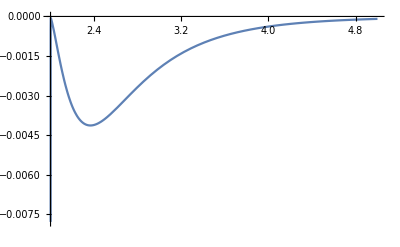

```mathematica
Plot[NEC[ρ, 0, 0.1],{ρ, 1+√(1-0.01^2), 5}, Axes -> True]
```

### Conserved energy of the effective stress-energy tensor.

Local energy density of the Cotton tensor.

```mathematica
EDC= -a √(grrk gxxk (gtϕk^2 - gttk gϕϕk))(Killingt[-μ] normalt[-ν]+ Killingt[-ν] normalt[-μ])(epsilon[g][γ,μ,α,β]Riemann[cd][-α,-β,ν, κ])cd[-γ]@dCSS[-κ] //Perturbations;
```

Local energy density of the Chern-Simons scalar field.

```mathematica
EDCSS =- 1/4 g[-μ, -ν]dCSS[α]dCSS[-α]Killingt[μ]normalt[ν] √(grrk gxxk (gtϕk^2 - gttk gϕϕk))//Perturbations //Simplify //PowerExpand;
```

The total effective energy density is the sum of the two.

```mathematica
EnergyDensity = EDC + EDCSS  /. {r[] -> ρ, x[] -> χ};
```

To obtain the total energy we should integrate over any constant time slice, however since the spin expansion is only a good approximation outside the horizon we integrate the energy density outside the black hole.

```mathematica
Energy = 2 π Integrate[EnergyDensity, {χ, -1, 1}, {ρ, 1+√(1-J^2),∞}] //Perturbations
```

(a^2 J^2 (124890+92021 J^2) π)/13440

```mathematica
EnergyDensity //Perturbations;
```

### Calculating the Wald entropy of the rotating Chern-Simons black hole solution.

Entropy correction due associated with the quadratic curvature term in the action. This entropy surface density we have to integrate over the event horizon.

```mathematica
2π a   * √(gxxk gϕϕk)* ϑ* (gtϕk^2- gttk gϕϕk)/gϕϕk  * -1/(√(grrk gxxk (gtϕk^2 - gttk gϕϕk))) Riemann[cd][{0, Kerr}, {1, -Kerr}, {2, -Kerr},{3, -Kerr}] //Perturbations //Simplify;
% /. {r[] -> 1 +√(1-J^2), x[] -> χ} //Perturbations;

WaldEntropyPontryagin = Integrate[%, {χ, -1, 1}] //Perturbations //CollectJ
```

a^2 ((29 J^2 π)/8+(311 J^4 π)/160)

The other entropy correction comes from the change in the horizon surface area of the black hole, hence it is a correction to the Bekenstein entropy. 
Note that surface area of a dCS black hole is lower than that of a Kerr black hole in GR. Interestingly the highest order terms increase the black hole surface area.

```mathematica
2π * (√(gxx gϕϕ) -  √(gxxk gϕϕk))//Perturbations //Simplify;
% /. {r[] -> 1 +√(1-J^2), x[] -> χ};
BekensteinEntropyCorrection = 1/4 Integrate[%, {χ, -1, 1}] //Perturbations //CollectJ
```

a^2 (-(915 J^2 π)/448-(25063 J^4 π)/26880)

The total entropy correction is the sum of the two. To get the total entropy one still has to add the Bekenstein entropy of a Kerr black hole in GR.

```mathematica
WaldEntropyPontryagin + BekensteinEntropyCorrection //Simplify //CollectJ
```

a^2 ((709 J^2 π)/448+(5437 J^4 π)/5376)

```mathematica
TotalEntropy = 2 π (1 + √(1-J^2)) + WaldEntropyPontryagin + BekensteinEntropyCorrection //Perturbations //CollectJ
```

4 π-J^2 π-(J^4 π)/4+a^2 ((709 J^2 π)/448+(5437 J^4 π)/5376)

First law sanity checks

```mathematica
1 - 2 J  Subscript[Ω, CS] - surfacegravity/π * ( 2 π (1 + √(1-J^2))-  (WaldEntropyPontryagin + BekensteinEntropyCorrection))//Perturbations
```

0

```mathematica
surfacegravity/(2 π)D[TotalEntropy, J]  + Subscript[Ω, CS] //Perturbations
```

0

### Komar charges.

Computing the mass of the spacetime, ie, the Komar charge associated with the time translation killing vector.

```mathematica
-1/4(gxx/(grr * (gtϕ^2- gtt*gϕϕ)))^(1/2)gϕϕ (D[gtt, r[]]+ gtt/gϕϕ D[gtϕ, r[]]) //Perturbations //Simplify;
```

```mathematica
% /. {r[] -> ρ, x[] -> χ};
```

```mathematica
Limit[%, ρ-> ∞];
Mass=M* Integrate[%, {χ, -1, 1}]
```

M

Computing the angular momentum of the spacetime, ie, the Komar charge associated with the axial translation killing vector.

```mathematica
-1/8((gϕϕ gxx)/grr)^(1/2) (gϕϕ/(gtϕ^2- gtt*gϕϕ))^(1/2)gtϕ D[(Log[-gϕϕ/gtϕ]), r[]] //Perturbations //Simplify;
```

```mathematica
% /. {r[] -> ρ, x[] -> χ};
```

```mathematica
Limit[%, ρ -> ∞];
AngularMomentum = Integrate[%, {χ, -1, 1}]
```

J

## Local Petrov type of the dCS black hole

For a general axially symmetric spacetime, one can define the following orthonormal tetrad in terms of the metric components

```mathematica
etv ={Sqrt[-(gttk+s*gttCS)], 0, 0, -(gtϕk+s*gtϕCS)/Sqrt[-(gttk+s*gttCS)]} //Perturbations ;
erv ={0, Sqrt[grrk+ s*grrCS], 0, 0} //Perturbations ;
exv ={0, 0, Sqrt[gxxk +s* gxxCS], 0} //Perturbations ;
eϕv ={0, 0, 0, Sqrt[(gtϕk+ s*gtϕCS)^2-(gttk + s*gttCS)( gϕϕk+ s*gϕϕCS)]/Sqrt[-(gttk+s*gttCS)]} //Perturbations ;
```

```mathematica
et = CTensor[etv, {-Kerr}];
er = CTensor[erv, {-Kerr}];
ex = CTensor[exv, {-Kerr}];
eϕ = CTensor[eϕv, {-Kerr}];
```

With this orthonormal tetrad we can define a complex null tetrad

```mathematica
l[μ_] := 1/(√2)(et[μ] + eϕ[μ]);
n[μ_] := 1/(√2)(et[μ] - eϕ[μ]);
m[μ_] :=  1/(√2)(er[μ] + I ex[μ]);
mbar[μ_] :=1/(√2)(er[μ] - I ex[μ]);
```

Now we are in position to calculate the Weyl scalars in this tetrad basis

```mathematica
ψ0  = Weyl[cd][-α,-β, -μ, -ν]l[α]m[β]l[μ]m[ν] //Perturbations  //Simplify
```

```mathematica
ψ2 = Weyl[cd][-α,-β, -μ, -ν]l[α]m[β]mbar[μ]n[ν]  //Perturbations   //Simplify
```

```mathematica
ψ4  = Weyl[cd][-α,-β, -μ, -ν]n[α]mbar[β]n[μ]mbar[ν] //Perturbations //Simplify
```

The I and J invariant test in the previous section determines whether or not a spacetime is algebraically special or not, or equivalently, whether the spacetime is of type I or not.
If the spacetime is determined to be special, additional test are needed to nail down the Petrov type.

If either one of the I and J invariants vanishes everywhere on the spacetime, then the spacetime is of of type III, N or O. If not, the spacetime can be a type II or type D spacetime. With the choice of frame for a general axially symmetric spacetime as used here, the Weyl scalars ψ_1 and ψ_3 vanish. Therefore axially symmetric spacetimes are never of type II. This implies that the spacetime is of type D if neither I and J vanish, and I^3 = 27 J^2.

However, it’s still nice to check wether the spacetime is of type D by determining whether or not the following quantity vanishes:

```mathematica
TD = 9 ψ2 ^2 - ψ0 ψ4 //Perturbations //PowerExpand //Simplify
```

### Discriminant and Weyl scalars

```mathematica
TD= 1/(15430135002267009024000 r^25)a^2 J^2 (-1+x^2) (-59043883937246208000 r^12 (-249480-94500 r-19700 r^2+24900 r^3+11438 r^4+4221 r^5)+19681294645748736000 ⅈ J r^11 (-4495680-786632 r+296256 r^2+366398 r^3+101244 r^4+10401 r^5) x+1312086309716582400 J^2 r^10 (152685 r^6+54570 r^7-187215000 x^2+5 r^5 (7651+194000 x^2)+50 r^3 (-79740+307397 x^2)-84 r (93097+405215 x^2)+10 r^4 (-105227+428345 x^2)+r^2 (-7058996+8189280 x^2))+10650051215232000 ⅈ J^3 r^9 x (2282764 r^6+8634901 r^7+93594547200 x^2+47040 r (88636+146163 x^2)-1568 r^2 (-1896461+5651697 x^2)-28 r^4 (-5872212+46262473 x^2)-112 r^3 (-10540295+52824144 x^2)-2 r^5 (12297794+60032777 x^2))+38727458964480 J^4 r^8 (2049514665 r^8+723636980 r^9+43906944312000 x^4+r^6 (7743323480-33507774050 x^2)+1293600 r x^2 (3300989+2405823 x^2)-75 r^7 (-67883048+150319535 x^2)-4704 r^2 (-1966583-605100615 x^2+777681475 x^4)-50 r^5 (-266093198+732955536 x^2+1854407653 x^4)-28 r^4 (-650439262-6316675260 x^2+21084067525 x^4)-112 r^3 (-156000061-10001488555 x^2+25765313000 x^4))+198602353664 ⅈ J^5 r^7 x (397071169625 r^8+269736237875 r^9-29383194429388800 x^4-7761600 r x^2 (305023770+8737379 x^2)-125 r^7 (-1359500749+25581444500 x^2)-50 r^6 (5722642921+89617872060 x^2)+23520 r^2 (-255298272-60679201555 x^2+132051424326 x^4)+1680 r^3 (-4521399246-288532175270 x^2+887007799405 x^4)+84 r^4 (-59013280480-813788954080 x^2+3276981866949 x^4)+2 r^5 (-954091590620-673363329145 x^2+12027813395451 x^4))+993011768320 J^6 r^6 (43212562575 r^10+15132565175 r^11-7742576090208960 x^6+r^9 (97898033020-207504514325 x^2)+11642400 r x^4 (-98139813+4855921 x^2)-115 r^8 (-1078266793+5260259540 x^2)+25 r^7 (6905571034-61859513309 x^2+67958227068 x^4)+4704 r^2 x^2 (-961387257-132442929835 x^2+163242061530 x^4)+20 r^6 (10542025221-128830174943 x^2+274688348785 x^4)+2352 r^3 (23822253-3074665703 x^2-80051043360 x^4+174269921175 x^6)+14 r^5 (14986277910-319948214350 x^2+693797861635 x^4+521632844607 x^6)+84 r^4 (1766844016-78581407210 x^2-184655747840 x^4+777671101151 x^6))+347206912 ⅈ J^7 r^5 x (189914661524000 r^10+100015215822375 r^11+69328620155418624000 x^6-4439635200 r x^4 (-1727199064+802063159 x^2)-300 r^8 (-578373056925+8182196362211 x^2)-50 r^9 (-3886201820602+21740322942781 x^2)-40360320 r^2 x^2 (-581249954-100151181325 x^2+187587936925 x^4)+80 r^6 (-4380152400715-49593408729860 x^2+199011065561147 x^4)+20 r^7 (400943368720-175221000417450 x^2+357673075150811 x^4)-517440 r^3 (1340291754-45249640714 x^2-2359571461153 x^4+5595569331230 x^6)-36960 r^4 (28266990220-265273979295 x^2-4910012220974 x^4+12679102901843 x^6)-168 r^5 (4804092408360+3177400549710 x^2-141359380017263 x^4+234665622954070 x^6))+217004320 J^8 r^4 (123913977355350 r^12+43162143522225 r^13+123310808883247265280 x^8-177585408 r x^6 (-132474219236+46386724365 x^2)-420 r^10 (-768995758223+3909086297580 x^2)-140 r^11 (-1934903926077+4049291127724 x^2)-2306304 r^2 x^4 (-59498695862-4726440348028 x^2+5616565682735 x^4)+20 r^9 (20084883244011-188095139040260 x^2+201804981618124 x^4)+40 r^8 (11096808812187-136802716730756 x^2+317097109721704 x^4)-2240 r^6 (-143592893748+4418386354813 x^2-26516969229714 x^4+36498945180354 x^6)-59136 r^3 x^2 (54672968136-3310904026041 x^2-44259458375524 x^4+89886452487285 x^6)-160 r^7 (-2640754961229+49167723813024 x^2-206460978074026 x^4+144364791373537 x^6)-29568 r^4 (-1424097855+265972046170 x^2-5564037345565 x^4-1326191268108 x^6+22902647435671 x^8)-448 r^5 (-375085323195+23085230065020 x^2-237083871293825 x^4+412180152224459 x^6+115959600529707 x^8))+490960 ⅈ J^9 r^3 x (102354806041249300 r^12+48820029726490225 r^13-161201669855361995059200 x^8+9234441216 r x^6 (-2377864884936+1636265467735 x^2)-70 r^11 (-1801110969555589+7083687065480692 x^2)-140 r^10 (-1014655926522943+8857956770548196 x^2)+119927808 r^2 x^4 (-414037209079-86344146252416 x^2+146757436043475 x^4)+224 r^8 (119626367003995-12266689653390900 x^2+37085180093941216 x^4)+32 r^9 (3552360878480770-62330935279920865 x^2+93042491743578664 x^4)+768768 r^3 x^2 (3822838310964-38957737535854 x^2-3713603750357344 x^4+7360387408095525 x^6)-640 r^6 (361089402027060+2993746141165437 x^2-37709457799564334 x^4+65414944685910061 x^6)-64 r^7 (1658927980037265+45694437306165830 x^2-244350633723513086 x^4+228961334318859930 x^6)+109824 r^4 (-1358597282805+26956308364370 x^2+84143606887354 x^4-4082533426558150 x^6+7489711287554322 x^8)+128 r^5 (-2049191396806785+3411180642925860 x^2+206172753184573070 x^4-678606305506960124 x^6+525449599600120767 x^8))+5776 J^10 r^2 (3175270977550275891 r^14+1102121240177242047 r^15-13466937277091929312281600 x^10+392463751680 r x^8 (-7804021742487+3910316801215 x^2)-1225 r^13 (-5568206877842276+11493390553124311 x^2)-70 r^12 (-114150599322571843+579417103747016700 x^2)+299819520 r^2 x^6 (-80822120007220-4107067307974009 x^2+4764053615949702 x^4)+350 r^11 (26954140658235878-252806686245195933 x^2+266228578669243340 x^4)+28 r^10 (351055144357686314-4383468789522217275 x^2+10279502158812286500 x^4)+11531520 r^3 x^4 (78828089061006-2745058757377740 x^2-20584353681609996 x^4+41456602079300095 x^6)-2800 r^8 (-2415040166690436+67238565071887933 x^2-386431067151807020 x^4+565292327252509884 x^6)-8 r^9 (-1115462495946477217+20342957503549961975 x^2-84437271555552104200 x^4+58296644417431351400 x^6)+549120 r^4 x^2 (-35692915586160+3608931766780130 x^2-45425861593888685 x^4+23472202267183751 x^6+89626317133071081 x^8)+3200 r^6 (419507595361932-45832379515161036 x^2+681678103688490685 x^4-2565743750784825226 x^6+2581364261249850838 x^8)+320 r^7 (12144504360596601-581065630981030440 x^2+5137221534110579270 x^4-13290496628357618250 x^6+6702875374884167320 x^8)+1920 r^5 (53561866272915-41130132971926460 x^2+1258064963406109285 x^4-7996307836036869013 x^6+11309848956956473921 x^8+1176534165244873578 x^10))+95 ⅈ J^11 r x (400902055463331226644 r^14+181994118425985158433 r^15+2331199886691691414146908160 x^10-32652984139776 r x^8 (-11310326411338+9156329907085 x^2)-70 r^13 (-7649331772435473186+24971187757839371299 x^2)-140 r^12 (-4632224431219095152+32314907225608279217 x^2)-3517882368 r^2 x^6 (-76069734455520-45012625306044383 x^2+71181383409126645 x^4)+112 r^11 (5611534785467294370-67380535861943606665 x^2+87072826291351619236 x^4)+224 r^10 (1922125023955061842-47858971298522475225 x^2+126009269400758687944 x^4)-12300288 r^3 x^4 (2137146176400714+25871306668162128 x^2-3297093339306967707 x^4+5683916904532135630 x^6)-640 r^8 (532941681682174653+18482576253534856281 x^2-134641786663655506088 x^4+217103995241207616614 x^6)-128 r^9 (-557947359760281358+98794117106932767870 x^2-422542115299519615428 x^4+340819845284350185615 x^6)-219648 r^4 x^2 (-20846944567261050-90868992960638284 x^2+3648531321319465070 x^4-30308379457215645160 x^6+42277084299727906777 x^8)+640 r^7 (-975782235614844798-11690650993336702023 x^2+180796201352646034890 x^4-473654062309756688840 x^6+282745560478158964155 x^8)+256 r^6 (-2366921101586993490-2513098958842674195 x^2+482576274011850474596 x^4-2118242274827741151500 x^6+2378807533881124152570 x^8)-768 r^5 (381091944437584380-6427949975776841050 x^2-117163278756149530968 x^4+1029906100497593667350 x^6-1962177759638830759906 x^8+965096450864718484169 x^10))+J^12 (13221054185869770196635 r^16+4577951259155775987045 r^17+198036229991366546796410634240 x^12+r^15 (28127352678077705119032-57093395222497319544705 x^2)-835162863575040 r x^10 (-61293533153393+36120411085132 x^2)-210 r^14 (-156603495079507694426+779096695519398185069 x^2)-17589411840 r^2 x^8 (-29522478569601610-1029251999077927541 x^2+1177475169484977930 x^4)+70 r^13 (543086168372400233704-4963271420207839864040 x^2+5113564770888373691425 x^4)+140 r^12 (275636041461643488416-3378363395271802157540 x^2+7777961885035593395275 x^4)-61501440 r^3 x^6 (448172363587742156-10250307738316217518 x^2-45415798240610696003 x^4+95140463987165098810 x^6)-560 r^11 (-60946894199804030432+1082544796541096453580 x^2-4339072422824513123975 x^4+2951861723477339954820 x^6)-224 r^10 (-113757077852021512788+3021479043149502828270 x^2-16555074203338080104275 x^4+24272902377776943320500 x^6)-7687680 r^4 x^4 (-139664735695360230+7073526446837178540 x^2-61057487788225074390 x^4+48359809514346520832 x^6+63421860141922659919 x^8)+640 r^9 (23293910582422054533-1015814176173575018961 x^2+8223662765987347486885 x^4-20637549249587642330910 x^6+10450733643938025467000 x^8)+640 r^8 (8730180931838121294-806665729769022160170 x^2+10186196011452628674535 x^4-35684064422951810809160 x^6+37930244197121936524955 x^8)-3840 r^5 x^2 (1242584046371227560-919510023718274456930 x^2+16029141624677449787764 x^4-71619834239199402148826 x^6+84560627110154137878660 x^8+2015947091546728757417 x^10)-19200 r^6 (37707395806116036+5561349369900102856 x^2-306505024081552679523 x^4+2719531504178908376622 x^6-7268562487509255029338 x^8+5777782146312592519985 x^10)-3200 r^7 (-80335872247364580+96158125935801414744 x^2-2156699727202775336169 x^4+11555295478487460697242 x^6-21154066972285626549664 x^8+8352268837469650048023 x^10)));
```

```mathematica
TD = TD/ a^2 /. {r[] -> r, x []-> x, J -> χ};
```

```mathematica
TD = ComplexExpand[TD]
```

```mathematica
ψ0 = -3/(2 r^3)+1/(6726720 (-2+r)^(3/2) r^12 √(1-x^2))J^3 (10090080 r^6 (40 ⅈ x^3 √((1-x^2)/(-2+r))+24 √r x^2 (-1+x^2)+2 ⅈ r^2 x √((1-x^2)/(-2+r)) (-3+8 x^2)-4 ⅈ r x √((1-x^2)/(-2+r)) (-3+13 x^2)+r^(3/2) (-1+15 x^2-14 x^4))+a^2 (-454765500 ⅈ r^9 x √((1-x^2)/(-2+r))+90953100 ⅈ r^10 x √((1-x^2)/(-2+r))-115511235840 ⅈ x^3 √((1-x^2)/(-2+r))+166747350 r^(17/2) (-1+x^2)-60635400 r^(19/2) (-1+x^2)+37171854720 √r x^2 (-1+x^2)+31680 ⅈ r x √((1-x^2)/(-2+r)) (1037009+304723 x^2)+640 ⅈ r^3 x √((1-x^2)/(-2+r)) (-1154516+7967449 x^2)-15 ⅈ r^8 x √((1-x^2)/(-2+r)) (-51457693+11949669 x^2)-20 ⅈ r^6 x √((1-x^2)/(-2+r)) (-3784643+20439488 x^2)+30 ⅈ r^7 x √((1-x^2)/(-2+r)) (-18446641+26830151 x^2)-8 ⅈ r^4 x √((1-x^2)/(-2+r)) (112983261+328445005 x^2)-4 ⅈ r^5 x √((1-x^2)/(-2+r)) (-624429749+1064665725 x^2)+32 ⅈ r^2 x √((1-x^2)/(-2+r)) (-915326093+1583986835 x^2)+r^(11/2) (60492484+202175256 x^2-262667740 x^4)+30 r^(15/2) (3675239-8732324 x^2+5057085 x^4)+168 r^(9/2) (8633793-36356218 x^2+27722425 x^4)-12 r^(13/2) (4756891-41581506 x^2+36824615 x^4)+112 r^(5/2) (9398411-55462326 x^2+46063915 x^4)-352 r^(3/2) (38276254-230993679 x^2+192717425 x^4)+16 r^(7/2) (70271723-327130608 x^2+256858885 x^4)))+1/(6518191680 r^13 √(1-x^2))J^4 (1/(-2+r))^(3/2) (-9777287520 r^6 x (60 x^3 √((1-x^2)/(-2+r))+12 r x (2-7 x^2) √((1-x^2)/(-2+r))-40 ⅈ √r x^2 (-1+x^2)+r^2 x √((1-x^2)/(-2+r)) (-14+29 x^2)+ⅈ r^(3/2) (3-29 x^2+26 x^4))+a^2 (-84858739245 r^11 √((1-x^2)/(-2+r))+16971747849 r^12 √((1-x^2)/(-2+r))+1958516251211520 x^4 √((1-x^2)/(-2+r))+589722167820 ⅈ r^(17/2) x (-1+x^2)-187112910150 ⅈ r^(19/2) x (-1+x^2)-629694367061760 ⅈ √r x^3 (-1+x^2)-30 r^10 √((1-x^2)/(-2+r)) (-6559034405+8373968198 x^2)+30 r^9 √((1-x^2)/(-2+r)) (-7853500770+39838073033 x^2)-15840 r x^2 √((1-x^2)/(-2+r)) (-2800632883+141733384911 x^2)-12 ⅈ r^(13/2) x (-15293658518-14514337307 x^2+29807995825 x^4)+25 r^8 √((1-x^2)/(-2+r)) (4532098237-88365346142 x^2+32294757541 x^4)+4 ⅈ r^(11/2) x (6904164634-60390503473 x^2+53486338839 x^4)+96 ⅈ r^(5/2) x (52277063487-110990551700 x^2+58713488213 x^4)+64 ⅈ r^(7/2) x (28110042520-94514298619 x^2+66404256099 x^4)+10 ⅈ r^(15/2) x (47570248575-119322697217 x^2+71752448642 x^4)-8 r^3 √((1-x^2)/(-2+r)) (-112365611050+1130593682563 x^2+125177313363 x^4)+4 r^6 √((1-x^2)/(-2+r)) (21010288261+163266413158 x^2+176725748349 x^4)-56 ⅈ r^(9/2) x (-26853324557-178973204455 x^2+205826529012 x^4)-4 r^7 √((1-x^2)/(-2+r)) (15987765029-242668364929 x^2+366866156960 x^4)+352 ⅈ r^(3/2) x (-47671105459-1010061686991 x^2+1057732792450 x^4)-8 r^5 √((1-x^2)/(-2+r)) (-143098578739+126834249907 x^2+2107943600368 x^4)+8 r^4 √((1-x^2)/(-2+r)) (115520821644-215339327299 x^2+4160472802355 x^4)+96 r^2 √((1-x^2)/(-2+r)) (-118630679057+106676774380 x^2+6547652583199 x^4)))+1/(461748698611200 r^15 √(1-x^2))J^6 (1/(-2+r))^(5/2) (173155761979200 r^6 x (-896 x^5 √((1-x^2)/(-2+r))+672 ⅈ √r x^4 (-1+x^2)-96 r^2 x^3 √((1-x^2)/(-2+r)) (-6+13 x^2)+16 r^3 x^3 √((1-x^2)/(-2+r)) (-11+18 x^2)+96 r x^3 √((1-x^2)/(-2+r)) (-5+19 x^2)-16 ⅈ r^(3/2) x^2 (5-57 x^2+52 x^4)+ⅈ r^(5/2) (3+49 x^2-324 x^4+272 x^6))+a^2 (-8706618459509355 r^14 √((1-x^2)/(-2+r))+1243802637072765 r^15 √((1-x^2)/(-2+r))+1685142019307293747200 x^6 √((1-x^2)/(-2+r))+54984218803356260 ⅈ r^(23/2) x (-1+x^2)-11052483212024980 ⅈ r^(25/2) x (-1+x^2)-709381922132236953600 ⅈ √r x^5 (-1+x^2)-55 r^13 √((1-x^2)/(-2+r)) (-471664191808495+269335409542393 x^2)-3763200 r x^4 √((1-x^2)/(-2+r)) (-53683655804945+781666743074702 x^2)+55 r^12 √((1-x^2)/(-2+r)) (-753350944563911+1770380810544147 x^2)+20 ⅈ r^(21/2) x (4630873012488229-7990827218306852 x^2+3359954205818623 x^4)+10 r^11 √((1-x^2)/(-2+r)) (3425581419473059-26918187988399992 x^2+7520557961884901 x^4)+107520 ⅈ r^(3/2) x^3 (-16610482669144-7579423512516441 x^2+7596033995185585 x^4)-20 ⅈ r^(19/2) x (2871582325569359-19894592100908292 x^2+17023009775338933 x^4)+17920 r^2 x^2 √((1-x^2)/(-2+r)) (-871658959742975-10836411108023447 x^2+95874488615120455 x^4)-5 r^10 √((1-x^2)/(-2+r)) (2459171782685821-81858657309682662 x^2+97918103594171261 x^4)-896 ⅈ r^(7/2) x (-268850039690893+3452739810826668 x^2-3485733399362295 x^4+301843628226520 x^6)-100 ⅈ r^(17/2) x (-67397048763851+5757248041223246 x^2-7322948845143224 x^4+1633097852683829 x^6)+24 ⅈ r^(15/2) x (-422792658456963+8684208698026208 x^2-23094675813096930 x^4+14833259773527685 x^6)+896 r^4 √((1-x^2)/(-2+r)) (-6915493830448-646838634755483 x^2+4477359253324065 x^4+15385205832033930 x^6)-10 r^9 √((1-x^2)/(-2+r)) (-562406575841213+34332243922509728 x^2-126060372234611657 x^4+17383361045335810 x^6)-224 ⅈ r^(9/2) x (-602531779191901+2182266589581161 x^2-36773114049290335 x^4+35193379238901075 x^6)-8 ⅈ r^(13/2) x (-2358123103453472-18499606459137748 x^2-26369149619184535 x^4+47226879181775755 x^6)-2240 ⅈ r^(5/2) x (668191269402731-4824068478522719 x^2-101431632524102692 x^4+105587509733222680 x^6)-8 r^7 √((1-x^2)/(-2+r)) (-539835279241441+3483143856659640 x^2-24267724804455375 x^4+109363819707546040 x^6)+4 r^8 √((1-x^2)/(-2+r)) (-1887397429401161+29038222698056692 x^2-326405220730098505 x^4+149361772238200970 x^6)-1792 r^3 √((1-x^2)/(-2+r)) (34096924835003-6965582287117388 x^2-18833150416018365 x^4+186625216185780835 x^6)+32 r^6 √((1-x^2)/(-2+r)) (204407078505245-14891491029882732 x^2-16605807772098655 x^4+206213961108763230 x^6)-64 r^5 √((1-x^2)/(-2+r)) (-97146936685612-1076281359849071 x^2-46407379600580480 x^4+293167948073114135 x^6)+16 ⅈ r^(11/2) x (6170067450462797-30137030636601067 x^2-285479081607944430 x^4+309446044794082700 x^6)))+1/(3961803834084096000 (-2+r)^(9/2) r^18 √(1-x^2))J^9 (92854777361346000 r^6 (112640 ⅈ x^9 √((1-x^2)/(-2+r))+92160 √r x^8 (-1+x^2)+56320 ⅈ r^2 x^7 √((1-x^2)/(-2+r)) (-3+8 x^2)-320 ⅈ r^5 x^7 √((1-x^2)/(-2+r)) (-28+39 x^2)+640 ⅈ r^4 x^7 √((1-x^2)/(-2+r)) (-92+147 x^2)-1024 ⅈ r x^7 √((1-x^2)/(-2+r)) (-72+347 x^2)-512 ⅈ r^3 x^7 √((1-x^2)/(-2+r)) (-289+564 x^2)-2048 r^(3/2) x^6 (7-111 x^2+104 x^4)+192 r^(5/2) x^4 (5+127 x^2-1116 x^4+984 x^6)-96 r^(7/2) (x^2+11 x^4+148 x^6-960 x^8+800 x^10)+r^(9/2) (5+51 x^2+296 x^4+2848 x^6-15360 x^8+12160 x^10))+a^2 (-519046756075103256000 ⅈ r^18 x √((1-x^2)/(-2+r))+47186068734100296000 ⅈ r^19 x √((1-x^2)/(-2+r))-133899807860452562632704000 ⅈ x^9 √((1-x^2)/(-2+r))+275252067615585060000 r^(35/2) (-1+x^2)-31457379156066864000 r^(37/2) (-1+x^2)-61631422284442621298688000 √r x^8 (-1+x^2)+590413824 ⅈ r x^7 √((1-x^2)/(-2+r)) (-33925531579807711+543351358629458761 x^2)-7 ⅈ r^17 x √((1-x^2)/(-2+r)) (-352992757335661187717+45533816451264858673 x^2)+28 ⅈ r^16 x √((1-x^2)/(-2+r)) (-237319972663725867296+116817337359271679197 x^2)+147603456 r^(3/2) x^6 (-33169675722575042-641491843980997463 x^2+674661519703572505 x^4)-24600576 ⅈ r^2 x^5 √((1-x^2)/(-2+r)) (-188253201652312937-693929632125340556 x^2+11218597105626261121 x^4)+14 r^(33/2) (69090487209881854427-88966591354754589738 x^2+19876104144872735311 x^4)-84 r^(31/2) (20547710433108952871-49128597421392582471 x^2+28580886988283629600 x^4)+ⅈ r^15 x √((1-x^2)/(-2+r)) (10953329777190347732847-14355309201213808645538 x^2+1014342091061503093767 x^4)-2 ⅈ r^14 x √((1-x^2)/(-2+r)) (5524572616513262600803-17668933914867707399896 x^2+5070137064231666249857 x^4)+r^(29/2) (1618446010542044453958-9920331080512429107486 x^2+9249419156468241967106 x^4-947534086497857313578 x^6)-12300288 r^(5/2) x^4 (73745182892641565-1217875973290257410 x^2-2283584956545853699 x^4+3427715746943469544 x^6)+12300288 ⅈ r^3 x^3 √((1-x^2)/(-2+r)) (6126849019208950-761103987592713713 x^2+1271481096326373116 x^4+7222210844140658035 x^6)-16 ⅈ r^13 x √((1-x^2)/(-2+r)) (-391361852661280973205+3342445154111400043230 x^2-2703135801825250919096 x^4+160714830665733607387 x^6)+16 ⅈ r^12 x √((1-x^2)/(-2+r)) (-102661816390043635179+3138804291908404035201 x^2-6506706643279291109292 x^4+1668073241453643791312 x^6)+4 r^(27/2) (-186120803741369698927+3813025797912011738282 x^2-5655140484370930362823 x^4+2028235490200288323468 x^6)+473088 ⅈ r^4 x √((1-x^2)/(-2+r)) (-4429125548681046-175283669903586463 x^2+13869863119134786436 x^4-44480065118581201756 x^6+1241026178770201671 x^8)-59136 r^(7/2) x^2 (-292084153456803320-19748504085392191495 x^2+237447488700011612651 x^4-313269981080874668532 x^6+95863080619712050696 x^8)-16896 ⅈ r^5 x √((1-x^2)/(-2+r)) (-65517591226942386-1361199443719526536 x^2+99754800479478609648 x^4-341848022301397985979 x^6+128341968482867240409 x^8)-88 ⅈ r^10 x √((1-x^2)/(-2+r)) (4766517504419957609-80838721924886041046 x^2+1722447879941184365498 x^4-3036139344990632772848 x^6+362971434035951113275 x^8)+4 ⅈ r^11 x √((1-x^2)/(-2+r)) (102319054073116878847-6719108996829990043434 x^2+39280517605610338587270 x^4-28637702574440910610426 x^6+614713501781927974503 x^8)-64 ⅈ r^8 x √((1-x^2)/(-2+r)) (-1374578975635368905-94077121243218523815 x^2-142322977326131210851 x^4-945695118169720279361 x^6+687063373544275966392 x^8)+r^(25/2) (175527128105056553919-13351067733628731598074 x^2+41023794620901065636491 x^4-30314802083444392723424 x^6+2466548068067002131088 x^8)+32 ⅈ r^9 x √((1-x^2)/(-2+r)) (2486235162105894913-135482570491016343411 x^2+2652957918926556745343 x^4-10748286889578548610222 x^6+3445506405451729794021 x^8)+64 ⅈ r^7 x √((1-x^2)/(-2+r)) (353223470806360463-34746370018306855032 x^2-1052760372662605392556 x^4+3081076192357789685544 x^6+3701888025010668829413 x^8)-4 r^(23/2) (22044533088585676620-1438566002704183726006 x^2+13507865895429374453193 x^4-17660905094694938575365 x^6+5569560668881162171558 x^8)-128 ⅈ r^6 x √((1-x^2)/(-2+r)) (-355234048156335757+7139288578785256924 x^2-804414813892025397752 x^4-810387340580985887222 x^6+12487995161630709354711 x^8)-11 r^(21/2) (-3280135600397403045+113699768432636903645 x^2-4101141712797901668639 x^4+11187891837002931310499 x^6-7413039166635947728588 x^8+215869409598678586128 x^10)+3696 r^(9/2) (-87972556106410469-3253016817677651335 x^2-111230666787802271244 x^4+1212662578588389223000 x^6-2348197761092871361216 x^8+1250106838666068471264 x^10)-16 r^(15/2) (-1899134130026451059-20654859730393584246 x^2+175982043251778511884 x^4+4284818890580733719539 x^6-7740473393093084420330 x^8+3302226453120992224212 x^10)+4 r^(19/2) (2183661252641897091+281224621996963320251 x^2-5129903584405496668547 x^4+39618756956065793320857 x^6-41720792767444196783436 x^8+6948531112534294913784 x^10)-8 r^(17/2) (-324914468565995774+107325018263401715799 x^2-1012064344013046264516 x^4+14771382961676767798889 x^6-22945470545043254174310 x^8+9079151823584696919912 x^10)-16 r^(13/2) (-1829908187503881657+12123121906695565159 x^2+309456332675096214801 x^4-7541705092580057395487 x^6-4152129336320610863912 x^8+11374084882506380361096 x^10)+32 r^(11/2) (1292054678447715392+12327130570263361033 x^2+624378370871500263487 x^4-4916622176388836569380 x^6-22646505726896904700444 x^8+26925130347165529929912 x^10)))+1/(740825622543053279232000 (-2+r)^(11/2) r^20 √(1-x^2))J^11 (8681550264176405616000 r^6 (638976 ⅈ x^11 √((1-x^2)/(-2+r))+540672 √r x^10 (-1+x^2)-133120 ⅈ r^3 x^9 √((1-x^2)/(-2+r)) (-11+23 x^2)+256 ⅈ r^6 x^9 √((1-x^2)/(-2+r)) (-125+164 x^2)-8192 ⅈ r x^9 √((1-x^2)/(-2+r)) (-55+289 x^2)-512 ⅈ r^5 x^9 √((1-x^2)/(-2+r)) (-505+739 x^2)+4096 ⅈ r^2 x^9 √((1-x^2)/(-2+r)) (-311+896 x^2)+1024 ⅈ r^4 x^9 √((1-x^2)/(-2+r)) (-839+1424 x^2)-30720 r^(3/2) x^8 (3-53 x^2+50 x^4)+1024 r^(5/2) x^6 (7+201 x^2-1944 x^4+1736 x^6)-192 r^(7/2) x^4 (5+61 x^2+918 x^4-6472 x^6+5488 x^8)+24 r^(9/2) x^2 (5+43 x^2+272 x^4+2880 x^6-16640 x^8+13440 x^10)-r^(11/2) (7+63 x^2+282 x^4+1248 x^6+10560 x^8-53376 x^10+41216 x^12))+a^2 (-127042201203863074848078360 ⅈ r^21 x √((1-x^2)/(-2+r))+9772477015681774988313720 ⅈ r^22 x √((1-x^2)/(-2+r))-162353906920644777329364172800000 ⅈ x^11 √((1-x^2)/(-2+r))+70036085279052720749581660 r^(41/2) (-1+x^2)-6514984677121183325542480 r^(43/2) (-1+x^2)-86663526796527146491203905126400 √r x^10 (-1+x^2)+76753797120 ⅈ r x^9 √((1-x^2)/(-2+r)) (-497365132124782178753+6380183370332360042873 x^2)-7 ⅈ r^20 x √((1-x^2)/(-2+r)) (-103979241702116844897096117+9681967129243922551903513 x^2)+14 ⅈ r^19 x √((1-x^2)/(-2+r)) (-172164721917219601838094589+59092162989806072077175827 x^2)+2558459904 r^(3/2) x^8 (-734657310751951566029-76146957739927348256192 x^2+76881615050679299822221 x^4)-2558459904 ⅈ r^2 x^7 √((1-x^2)/(-2+r)) (-2044008567908524600980-28193719719040645029697 x^2+228045813333607390146857 x^4)+14 r^(39/2) (22476566086904093575326507-26706600016505450574754198 x^2+4230033929601356999427691 x^4)+28 ⅈ r^18 x √((1-x^2)/(-2+r)) (180801692583695514903355338-157533264518458182236726836 x^2+7805661046564156135899601 x^4)-28 r^(37/2) (27163575489135194622798985-49532166302880799875966526 x^2+22368590813745605253167541 x^4)-84 ⅈ r^17 x √((1-x^2)/(-2+r)) (82279208340376110986280343-160620252136075913457096151 x^2+30586315355665059070264592 x^4)-426409984 r^(5/2) x^6 (2965767597579225241954-29832599200413811162373 x^2-347724386029457139053714 x^4+374591217632291724974133 x^6)+65601536 ⅈ r^3 x^5 √((1-x^2)/(-2+r)) (2114212769273794680621-210342928033364786325031 x^2-519598297383891486107993 x^4+5082575963553729185006619 x^6)-28 r^(35/2) (-37725075941557229988797793+136505421788390598952510628 x^2-106079319004310495224282129 x^4+7298973157477126260569294 x^6)-16 ⅈ r^16 x √((1-x^2)/(-2+r)) (-373229689713995340468780027+1630017752000395638246808745 x^2-821086186579252398178595949 x^4+29566036190458382974148368 x^6)+56 r^(33/2) (-14786593255411689279022555+131835853707055510401675062 x^2-154752218851625550379734053 x^4+37702958399981729257081546 x^6)+16 ⅈ r^15 x √((1-x^2)/(-2+r)) (-185967712876910116722737325+2052433627124127039116105677 x^2-2399902709739288792515701344 x^4+346249220354638843263309692 x^6)-49201152 ⅈ r^4 x^3 √((1-x^2)/(-2+r)) (151050875439013549950+4678966378873658577100 x^2-285566064062103281504948 x^4+286671065354221482783589 x^6+1657602396062295955115175 x^8)+16400384 r^(7/2) x^4 (2132312996926405167405+141290076371413409561154 x^2-1238920902539760720705035 x^4-1758761263697363192072752 x^6+2854259776868784098049228 x^8)+16 r^(31/2) (20803015401219393131500558-575852975221346477937815181 x^2+1124296467428098018810495596 x^4-597639375996453829065864075 x^6+28392868388482895061683102 x^8)+32 ⅈ r^14 x √((1-x^2)/(-2+r)) (22054218473868571365391333-823462601498942872763502974 x^2+2213470353308763217517039124 x^4-880382109900511466641063680 x^6+28467158239553576112767131 x^8)-64 ⅈ r^13 x √((1-x^2)/(-2+r)) (1969096246976977200559181-192115814643156961415602447 x^2+1332252358049184138528253910 x^4-1282806990929382462276874606 x^6+178675300587102179579861818 x^8)-16 r^(29/2) (4030846161241685411357573-423816895640658911670642356 x^2+1735501192349923402496524571 x^4-1610483129122188666758489308 x^6+294767986251682490521249520 x^8)+3328 ⅈ r^11 x √((1-x^2)/(-2+r)) (-1830946322867592724049+352118084276111617710995 x^2-8777805321204280228862573 x^4+56208256427903363289888681 x^6-53309990609755401303441202 x^8+3797470942411430483995554 x^10)-128 ⅈ r^12 x √((1-x^2)/(-2+r)) (-702997629388988360343739+23129000215064487731678473 x^2-511827041005204844831698675 x^4+1190238121582949043752540687 x^6-471714947555987307882637426 x^8+5651595089681644576074030 x^10)+212992 ⅈ r^5 x √((1-x^2)/(-2+r)) (1197387927601414079811+38458219643954583914959 x^2+606718101841827861962629 x^4-31276207120707222212087587 x^6+76267020534974790165966309 x^8+6800827268562656560020735 x^10)+73216 r^(9/2) x^2 (-18696909872862920722947-588572079467673503879257 x^2-20286922338172980320697804 x^4+176192258505492501297652296 x^6-189705588743977724560067456 x^8+34407521565998740007715168 x^10)+4096 ⅈ r^6 x √((1-x^2)/(-2+r)) (-32773243062411385971514-555747608807597983095810 x^2-6532028681608514708931008 x^4+328746153585289002643689572 x^6-851740810924292918179074257 x^8+48371256836607801829577559 x^10)-8 r^(27/2) (-2637457057516649049051815+319545131689641483012009754 x^2-3779361878783036443667760279 x^4+6017131948354285738371840452 x^6-2665435543848792780477151048 x^8+110757799645418651810112936 x^10)-512 ⅈ r^10 x √((1-x^2)/(-2+r)) (17067109844843627623206+1991356606910327107476567 x^2-16503631802113351554288767 x^4+288444832332280961817513953 x^6-598257763715637285471372351 x^8+112946721341220817818866241 x^10)+512 ⅈ r^9 x √((1-x^2)/(-2+r)) (-19731433838768771626714+153183061896987517780762 x^2-16725557838818681833873348 x^4+96506481502650010218416912 x^6-444457792583352695239503199 x^8+142548084022851835270271043 x^10)-1024 ⅈ r^8 x √((1-x^2)/(-2+r)) (2705900057769675438442-191285678156324615640824 x^2-8738624862015924197497760 x^4-38717166589077189448582796 x^6-1724503651143913349644473 x^8+209802122858794794803374185 x^10)+4096 ⅈ r^7 x √((1-x^2)/(-2+r)) (-1487072300549148787226+21637280263200074861152 x^2-392207952291977822734593 x^4-25082816388561374564680605 x^6-25116939321206845656247952 x^8+284429205162332994177114558 x^10)+8 r^(25/2) (-760930333797103661042083+61577249281172370038427787 x^2-2575833288578523154729354038 x^4+8441334736533103127765893046 x^6-7174286887785949271779119352 x^8+1247969120883994032365194640 x^10)+104 r^(23/2) (-16328772069949138603290-2852380624417233418467817 x^2+71497408769463548041763156 x^4-669800774576216007740248539 x^6+1040613262835688896889370426 x^8-446218127919736490069872976 x^10+6776940287287235436059040 x^12)-32 r^(17/2) (104366902965299373778885+934947589361789034215190 x^2+48714934054273826703967345 x^4-226518111748956713820010640 x^6+1225047797469722003370912116 x^8-1620926542069716162733385936 x^10+572642607802349958070523040 x^12)-16 r^(21/2) (47539798991869492515813-8883474115509562455597224 x^2+123284036675139164388388289 x^4-2943114861533405630885789034 x^6+9669059151919175687215935580 x^8-7554846193731492040398388912 x^10+714453800987100512642935488 x^12)+64 r^(15/2) (-52509340126830584234457+316243915589492272962130 x^2+7859729692398781685506401 x^4-39444681741528414052092042 x^6-1194980567389341492536050368 x^8-1005560553171609363510664336 x^10+2231862338034617826724572672 x^12)+16 r^(19/2) (-20305669349151266242801+2151604596930946107942026 x^2+135834656996221911675595483 x^4-1201578271749221786848728976 x^6+9715985789227375514167364380 x^8-11323358889219025563439131776 x^10+2670985415817068129603201664 x^12)-64 r^(13/2) (83321891854363193854025+600326678987283906671270 x^2+14171710642445055410979377 x^4+301634961589605548305924472 x^6-2121760120809764414247585496 x^8-9524088682126198921746478240 x^10+11329358482133071085176634592 x^12)-128 r^(11/2) (-269986902212407704983918-7483633170662516177782955 x^2-113194154342519725795108335 x^4-2822730658069921442726145960 x^6+24351015772209824425017765360 x^8-36382169967239895277084019744 x^10+14974832627515386944470275552 x^12)))-1/(448448 (-2+r) r^11 √(1-x^2))J^2 (-1345344 r^6 (3 ⅈ √(1/(-2+r)) r^(3/2) x (-1+x^2)+r √(1-x^2) (-1+4 x^2)-6 ⅈ x (-√(r/(-2+r))+√(r/(-2+r)) x^2-ⅈ x √(1-x^2)))+a^2 (4547655 r^8 √(1-x^2)-1515885 r^9 √(1-x^2)+1091061312 ⅈ √(1/(-2+r)) r^(3/2) x (-1+x^2)+41205504 ⅈ √(1/(-2+r)) r^(5/2) x (-1+x^2)+45955296 ⅈ √(1/(-2+r)) r^(7/2) x (-1+x^2)-60310912 ⅈ √(1/(-2+r)) r^(9/2) x (-1+x^2)-6198568 ⅈ √(1/(-2+r)) r^(11/2) x (-1+x^2)-5897696 ⅈ √(1/(-2+r)) r^(13/2) x (-1+x^2)+6910708 ⅈ √(1/(-2+r)) r^(15/2) x (-1+x^2)-28 r^6 √(1-x^2) (29789+96770 x^2)-20 r^5 √(1-x^2) (-9666+207121 x^2)+42 r^7 √(1-x^2) (-130213+224006 x^2)+4752 r √(1-x^2) (99143+628535 x^2)+24 r^2 √(1-x^2) (-1521839+4118643 x^2)+24 r^3 √(1-x^2) (-1277923+4673623 x^2)-16 r^4 √(1-x^2) (2877733+7486872 x^2)-12108096 ⅈ x (-170 √(r/(-2+r))+170 √(r/(-2+r)) x^2-471 ⅈ x √(1-x^2))))-1/(365018734080 (-2+r)^(3/2) r^14)J^5 √(-1/((-2+r) (-1+x^2))) (-136882025280 r^6 (16 ⅈ r x^3 √(1-x^2) (-10+31 x^2)-4 ⅈ r^2 x^3 √(1-x^2) (-26+47 x^2)-48 √(1/(-2+r)) r^(3/2) x^2 (1-13 x^2+12 x^4)+√(1/(-2+r)) r^(5/2) (1+27 x^2-204 x^4+176 x^6)+48 x^4 (-10 √(r/(-2+r))+10 √(r/(-2+r)) x^2-7 ⅈ x √(1-x^2)))+a^2 (19008357590880 ⅈ r^11 x √(1-x^2)-3801671518176 ⅈ r^12 x √(1-x^2)-12038626474224 √(1/(-2+r)) r^(23/2) (-1+x^2)+2534447678784 √(1/(-2+r)) r^(25/2) (-1+x^2)+1182720 ⅈ r x^3 √(1-x^2) (5571999725+28634654953 x^2)+5 ⅈ r^10 x √(1-x^2) (-8253807820699+6403007400623 x^2)-10 ⅈ r^9 x √(1-x^2) (-4865855748375+14429612281073 x^2)+340480 √(1/(-2+r)) r^(3/2) x^2 (37492613618-99789810181 x^2+62297196563 x^4)-1792 ⅈ r^3 x √(1-x^2) (182944893014-1254853552435 x^2+924236384403 x^4)-4 ⅈ r^6 x √(1-x^2) (2047187004897+16269874436614 x^2+1774819202709 x^4)-896 ⅈ r^4 x √(1-x^2) (193477789671-1398572771330 x^2+3363423677157 x^4)-112 ⅈ r^5 x √(1-x^2) (1176906282860-8780547983645 x^2+9718840196513 x^4)+1792 ⅈ r^2 x √(1-x^2) (957033865429-8661684694019 x^2+9992913936302 x^4)-2 √(1/(-2+r)) r^(21/2) (9922183138241-23855728770486 x^2+13933545632245 x^4)+8 √(1/(-2+r)) r^(19/2) (1743799387859-18656979146739 x^2+16913179758880 x^4)-ⅈ r^8 x √(1-x^2) (23595118846825-230258154896710 x^2+45174923602921 x^4)+4 ⅈ r^7 x √(1-x^2) (1261247771423-45415331373757 x^2+54152402510598 x^4)-448 √(1/(-2+r)) r^(7/2) (42598733247-916916294268 x^2+749156282365 x^4+125161278656 x^6)+14 √(1/(-2+r)) r^(17/2) (-436720762463+15994141204803 x^2-18525429628305 x^4+2968009185965 x^6)+224 √(1/(-2+r)) r^(9/2) (-129830584465+365344032795 x^2-5876496798443 x^4+5640983350113 x^6)+16 √(1/(-2+r)) r^(13/2) (-384558203488+1009117426579 x^2-7706401357836 x^4+7081842134745 x^6)-8 √(1/(-2+r)) r^(15/2) (-784592726203+17402100456861 x^2-44539733412673 x^4+27922225682015 x^6)+32 √(1/(-2+r)) r^(11/2) (-1064829729892+19717258906137 x^2-60259014042700 x^4+41606584866455 x^6)-448 √(1/(-2+r)) r^(5/2) (-769958818827+25775051814125 x^2-88346936699622 x^4+63341843704324 x^6)+614768394240 x^4 (-35191 √(r/(-2+r))+35191 √(r/(-2+r)) x^2-109215 ⅈ x √(1-x^2))))-1/(6926230479168000 (-2+r)^(5/2) r^16)J^7 √(-1/((-2+r) (-1+x^2))) (1298668214844000 r^6 (-192 ⅈ r x^5 √(1-x^2) (-7+25 x^2)-32 ⅈ r^3 x^5 √(1-x^2) (-17+26 x^2)+64 ⅈ r^2 x^5 √(1-x^2) (-26+53 x^2)+96 √(1/(-2+r)) r^(3/2) x^4 (5-71 x^2+66 x^4)-24 √(1/(-2+r)) r^(5/2) x^2 (1+23 x^2-184 x^4+160 x^6)+√(1/(-2+r)) r^(7/2) (1+13 x^2+162 x^4-976 x^6+800 x^8)-256 x^6 (-14 √(r/(-2+r))+14 √(r/(-2+r)) x^2-9 ⅈ x √(1-x^2)))+a^2 (522397107570561300 ⅈ r^14 x √(1-x^2)-74628158224365900 ⅈ r^15 x √(1-x^2)-335826712009646550 √(1/(-2+r)) r^(29/2) (-1+x^2)+49752105482910600 √(1/(-2+r)) r^(31/2) (-1+x^2)+22579200 ⅈ r x^5 √(1-x^2) (-26744287884731+792151177427444 x^2)+100 ⅈ r^13 x √(1-x^2) (-15171812819465239+5101496423560790 x^2)-100 ⅈ r^12 x √(1-x^2) (-23476612529869517+32470622518515872 x^2)-100 √(1/(-2+r)) r^(27/2) (8563131614685806-13010168937234801 x^2+4447037322548995 x^4)-1075200 √(1/(-2+r)) r^(3/2) x^4 (-1751817304245361-5939411098843650 x^2+7691228403089011 x^4)-322560 ⅈ r^2 x^3 √(1-x^2) (-1522971591686790+6650836609414491 x^2+10202611303503002 x^4)+150 √(1/(-2+r)) r^(25/2) (6743518652218813-26676967395287040 x^2+19933448743068227 x^4)-25 ⅈ r^11 x √(1-x^2) (76902234624201586-341462084956839171 x^2+78109865817148697 x^4)+50 ⅈ r^10 x √(1-x^2) (12543934676357556-250989503939583331 x^2+248012867497795983 x^4)-6720 ⅈ r^4 x √(1-x^2) (12196102414187-4662866478836142 x^2+16378834439571124 x^4+23169866310674257 x^6)-53760 ⅈ r^3 x √(1-x^2) (-63059270943307+8006790466691032 x^2-40425543846628211 x^4+36174538784698571 x^6)+25 √(1/(-2+r)) r^(23/2) (-21960858803087003+326206150701217134 x^2-377108324561115879 x^4+72863032662985748 x^6)-13440 √(1/(-2+r)) r^(5/2) x^2 (-11016345376220435+254391353041371705 x^2-428740037365290746 x^4+185365029700139476 x^6)-50 √(1/(-2+r)) r^(21/2) (-3204146031727316+183307018933780500 x^2-431527762821588017 x^4+251424889919534833 x^6)+2 ⅈ r^9 x √(1-x^2) (-51138315147387625+5365389682022097705 x^2-14970437839648740677 x^4+1115439324849020829 x^6)+8 ⅈ r^7 x √(1-x^2) (-28449777059446300+86564351474173375 x^2-1308673162084979214 x^4+2209670622237592185 x^6)+96 ⅈ r^5 x √(1-x^2) (-1453257257883655+68745109697236220 x^2-769443979793456387 x^4+2220883726751443012 x^6)-4 ⅈ r^8 x √(1-x^2) (-61017217177648730+994408645997047890 x^2-9164309564167055107 x^4+4220416607833808823 x^6)+16 ⅈ r^6 x √(1-x^2) (-7806073172549245+871253717952018080 x^2-5377736434229098195 x^4+4323002085876609198 x^6)+336 √(1/(-2+r)) r^(9/2) (376601559718825+6002459241529010 x^2-150048325046955355 x^4-502945606914443196 x^6+646614871160150716 x^8)-3 √(1/(-2+r)) r^(19/2) (38840671817851755-1705407798005111615 x^2+12411718658329473955 x^4-11451872394043073929 x^6+706720861900859834 x^8)+3360 √(1/(-2+r)) r^(7/2) (-389126058292860-31159425588928509 x^2+479641481215931989 x^4-1202077175222296804 x^6+753984245653586184 x^8)+12 √(1/(-2+r)) r^(17/2) (5981310279809620-141549146589307135 x^2+3226482103315771820 x^4-4545225726798435191 x^6+1454311459792160886 x^8)-24 √(1/(-2+r)) r^(13/2) (-5065145460952205-90613448483429430 x^2+2268417189341314025 x^4-5223970389276635068 x^6+3051231793879702678 x^8)-16 √(1/(-2+r)) r^(11/2) (-6969935213486000+82736563978670505 x^2-1681350883267182060 x^4-3782071167081644869 x^6+5387655421583642424 x^8)-4 √(1/(-2+r)) r^(15/2) (-3248803637483355-475863835613676510 x^2+3831821382336618235 x^4-10103195798879597524 x^6+6750487055794139154 x^8)+25359196262400 x^6 (-400745594 √(r/(-2+r))+400745594 √(r/(-2+r)) x^2-570722025 ⅈ x √(1-x^2))))+J^14 (1/(2048 r^(35/2))3 (1/(-2+r))^(13/2) x (5505024 √(1/(-2+r)) r^(3/2) x^11 (-21+26 x^2)-8257536 √(1/(-2+r)) r^(5/2) x^11 (-21+26 x^2)+6881280 √(1/(-2+r)) r^(7/2) x^11 (-21+26 x^2)-3440640 √(1/(-2+r)) r^(9/2) x^11 (-21+26 x^2)+1032192 √(1/(-2+r)) r^(11/2) x^11 (-21+26 x^2)-172032 √(1/(-2+r)) r^(13/2) x^11 (-21+26 x^2)+12288 √(1/(-2+r)) r^(15/2) x^11 (-21+26 x^2)-114688 ⅈ r x^10 √(1-x^2) (-87+704 x^2)+2048 ⅈ r^2 x^8 √(1-x^2) (-625-13804 x^2+66528 x^4)-5120 ⅈ r^3 x^6 √(1-x^2) (-49-550 x^2-6496 x^4+24640 x^6)+320 ⅈ r^4 x^4 √(1-x^2) (-153-1288 x^2-7600 x^4-64960 x^6+216832 x^8)-8 ⅈ r^5 x^2 √(1-x^2) (-1001-6800 x^2-30240 x^4-128000 x^6-909440 x^8+2838528 x^10)+13 ⅈ r^6 √(1-x^2) (-63-364 x^2-1360 x^4-4480 x^6-16000 x^8-103936 x^10+315392 x^12)-ⅈ r^7 √(1-x^2) (-63-364 x^2-1360 x^4-4480 x^6-16000 x^8-103936 x^10+315392 x^12)-262144 x^11 (-126 √(r/(-2+r))+156 √(r/(-2+r)) x^2-77 ⅈ x √(1-x^2)))+(a^2 (-8273111033694092900792636528370 r^26 √(1-x^2)+551540735579606193386175768558 r^27 √(1-x^2)+74972170909793063552713283294204 ⅈ √(1/(-2+r)) r^(49/2) x (-1+x^2)-5058615118830301508526925135208 ⅈ √(1/(-2+r)) r^(51/2) x (-1+x^2)-56736406831104 r x^12 √(1-x^2) (-5729726142471707712610883+59632938713129609017294583 x^2)-133 r^25 √(1-x^2) (-418881875183933706662743053751+50757147327130829621261089087 x^2)+399 r^24 √(1-x^2) (-555597725406962713987894356151+243970516224792376566867413987 x^2)-654965735424 ⅈ √(1/(-2+r)) r^(3/2) x^11 (135084748530033962536243307-6353287974531640425753807847 x^2+6218203226001606463217564540 x^4)+40935358464 r^2 x^10 √(1-x^2) (-157435384341024579460451554-25750571100186273139309039715 x^2+141879174186220684631255088605 x^4)+28 ⅈ √(1/(-2+r)) r^(47/2) x (17381127144340487116312055735593-18354045151450590033265353169542 x^2+972918007110102916953297433949 x^4)+14 r^23 √(1-x^2) (41104520154335933677200368261381-44716341972614062003150298381658 x^2+2171158464408124232717300513719 x^4)-28 ⅈ √(1/(-2+r)) r^(45/2) x (64650636095144180987617403504047-78667766754910037710659408897284 x^2+14017130659765856723042005393237 x^4)-7 r^22 √(1-x^2) (144391277079501396316221972611171-337812584280633655859452274985154 x^2+60014542523261720047093969452323 x^4)+13645119488 ⅈ √(1/(-2+r)) r^(5/2) x^9 (550002556776308990226482725+19901891837135929980625641799 x^2-507505637885796890142909181568 x^4+487053743491884651172057057044 x^6)-28 ⅈ √(1/(-2+r)) r^(43/2) x (-151140015027355182173239717026394+239573249082657462893237203628909 x^2-91224913142495069877513974306646 x^4+2791679087192789157516487704131 x^6)-14 r^21 √(1-x^2) (-85639976038794182931031175371659+414433672163183947078597277522212 x^2-184128677102899307408182632295043 x^4+5913329242263200580603203569118 x^6)+112 ⅈ √(1/(-2+r)) r^(41/2) x (-57155450056717687268836991864213+137037045558401940172740737736371 x^2-89681579828890942816094653472826 x^4+9799984327206689912190907600668 x^6)-524812288 r^3 x^8 √(1-x^2) (766588999505930435226763752-41213524777575718889012019878 x^2-2724996921871851461877506197291 x^4+10614485794847213340835148044089 x^6)+28 r^20 √(1-x^2) (-32991884745121237332395926998287+343498544019274637459962765888762 x^2-330209739488768262730331462157777 x^4+39484327184584309234883927298098 x^6)+56 ⅈ √(1/(-2+r)) r^(39/2) x (110506761248834860365380007630893-472939908370016381170675779498189 x^2+483109462054723172013075385606179 x^4-123504125638071406636781524153507 x^6+2827810704529755429001910414624 x^8)+56 r^19 √(1-x^2) (7525150697213850360552875232955-192581064405670804131417171453918 x^2+383018739653116477436670877605775 x^4-116927494228479879123368316798484 x^6+2929579667620508257400903396816 x^8)-524812288 ⅈ √(1/(-2+r)) r^(7/2) x^7 (710624990397425026656584595+40974424486057319672039215010 x^2+653243348744435267967685449693 x^4-12258009754403121023202436803002 x^6+11563081356182231010536055553704 x^8)-112 r^18 √(1-x^2) (845131912213043342976472848843-70342421207788474625533445380490 x^2+299313779123558615076560353204201 x^4-202018307384797551441264116405236 x^6+19163082877058864775205169844434 x^8)-112 ⅈ √(1/(-2+r)) r^(37/2) x (32165221941794715398852281852647-297625897716135442644893906236827 x^2+478381459620622691304068653355317 x^4-232472488190997815076432058042705 x^6+19551704344715851018405029071568 x^8)+37486592 r^4 x^6 √(1-x^2) (875858465168929701164530874+24446777375768509553742855195 x^2-795037959095236415772952531682 x^4-27699018829360966111598439052227 x^6+86182626684745335465232500007506 x^8)-32 ⅈ √(1/(-2+r)) r^(35/2) x (-34228708846803966707528347208706+900555231469571499667534449427738 x^2-2516939746799481212153738174568617 x^4+2066460119600391886437623558582105 x^6-423601086109387930033793683573044 x^8+7754190685709722789902197340524 x^10)-32 r^17 √(1-x^2) (-341815789776764453413023322639+106485190697983858228456746564478 x^2-1106649044601166935118296315920861 x^4+1576401601401094673637801238085300 x^6-389360324209067047544637910063754 x^8+7943362569596428157777321403452 x^10)+64 r^16 √(1-x^2) (-63492751372847281713301334499+11333029647502331633074474780600 x^2-380874805285916047782471747141667 x^4+1180577202891399983173280194668800 x^6-658757705815055696570324294531188 x^8+52948497844532576570262123878762 x^10)+32 ⅈ √(1/(-2+r)) r^(33/2) x (-4278756969043163995521687538835+486864690521502470346891027144075 x^2-2837792759015518609240823640545526 x^4+3804645560490621104579899158578814 x^6-1558838029009325600716260388428328 x^8+109399293981763799025815530789800 x^10)+4685824 ⅈ √(1/(-2+r)) r^(9/2) x^5 (4979501383607662984609441191+183090018053853556726165241777 x^2+5367022157000643389458129502100 x^4+47988500333970442824752852122276 x^6-769392194935744676088769532406804 x^8+715848602925336128654847776099460 x^10)-131072 r^5 x^4 √(1-x^2) (19929659329324882025290901380+435715479370769867005271917578 x^2+5988562273085630104745878513752 x^4-162904013916431437501122088983447 x^6-3241381370615971042895051930292143 x^8+8682270878871125695533534839865186 x^10)+128 r^15 √(1-x^2) (720069487497282552871348485-863879769030848696346887121352 x^2+77624369965050331542137052728627 x^4-595139694125739340602195509393790 x^6+717481283610031165540467968845804 x^8-155989061415147890282251519907340 x^10+2805657514584073653215121457942 x^12)+32 ⅈ √(1/(-2+r)) r^(31/2) x (1012377076866157615361635299945-140592387102472460125058883116178 x^2+2263952481795726030545753151103417 x^4-5290249529166011611766264140182128 x^6+3842734251496449455149065172302992 x^8-687881269483794104528490928286400 x^10+11024075383236533109633992878352 x^12)-128 r^14 √(1-x^2) (-623760323630913138360802566-480810489455562761922959605236 x^2+16625778011759874050861795436420 x^4-387491365535320071056639562139808 x^6+1044944510983501636982697927933479 x^8-534104616016202181074228716814146 x^10+42547159038988421152695508236109 x^12)-32 ⅈ √(1/(-2+r)) r^(29/2) x (333220624665321990608976259335-21577890706995606417665290512748 x^2+1147448476696666673820584982007629 x^4-5552309667305945308362614086116344 x^6+6818313429681427784340758193263424 x^8-2568007625711669014194352860502784 x^10+175800056721850148822680085601488 x^12)+65536 r^6 x^2 √(1-x^2) (2289167566816431064541439564+46789773787074664280207549962 x^2+499780846891891453419687268392 x^4+4536116134205806714492834000705 x^6-125011104579805223540464354331478 x^8-1420692204516402790087071788422866 x^10+3511603593646352432847266680053879 x^12)-32768 ⅈ √(1/(-2+r)) r^(11/2) x^3 (37958326027048802435492897150+1274671485814761007213986244373 x^2+23140466576268240090966690675061 x^4+461512713777848820733316433727610 x^6+2388890682619539072294950412985522 x^8-37293567262739865866841755497697858 x^10+34418710769954367923912872481168142 x^12)-256 r^13 √(1-x^2) (-334738090199638145191934266+8716057498728086392696778520 x^2-2489228285247083159901934091636 x^4+73650415945543393597202969614904 x^6-506139370041312172386626125411535 x^8+587282848950947229349094419917360 x^10-135759750429779646463764852041301 x^12+1769386580356825299307714493646 x^14)+512 r^12 √(1-x^2) (238618535428891238527437398-5228999707002211815271958364 x^2-813842102819272952500543016148 x^4+8849674520630053667505165413448 x^6-153305098935500040163271317414427 x^8+429188303378694677089523808494390 x^10-237958289873290196510097801436571 x^12+10276606563593169194112626524902 x^14)-32 ⅈ √(1/(-2+r)) r^(27/2) x (56030095203545743828565775887+10221115873274526542750224998336 x^2-318005809945030241134436707971078 x^4+4149917037531834875183708245547095 x^6-9100336335158976114193901283708928 x^8+6439624739260436350745378008398352 x^10-1195419424229684539736614240682496 x^12+13942646572941596849287187642832 x^14)-1024 r^11 √(1-x^2) (-191807079056235378426845602+2673261969988115612556830492 x^2-19356150342519131701348798708 x^4+3047541748202380081359309335648 x^6-25788537936881988136603521612131 x^8+203283178584265533621200955953038 x^10-249214246068903807579604006100365 x^12+30440636972734825090172590802988 x^14)+128 ⅈ √(1/(-2+r)) r^(25/2) x (-8974566121782713818708132014+741921689248124758281368527825 x^2-19649836251650087280898503015741 x^4+486718460767111333937905730569978 x^6-2287605509281389638379310729832888 x^8+2911134188518579197981245289182520 x^10-1134748358222239157391419318303472 x^12+43418107346462009088014871003792 x^14)+2048 r^10 √(1-x^2) (141971613286547590298947950-1035292320403127110854493780 x^2+12908444021829194200479698064 x^4+1091217718895103494179406428728 x^6-5158309478015403345958419042819 x^8+49367262557832158721314751386726 x^10-178815388998693794159338495978585 x^12+100591525681438075880633474331180 x^14)-4096 r^9 √(1-x^2) (-70011035439972871934840206+199935601048788100275112260 x^2-7726282705094449718164522600 x^4+21391478396813738241656460232 x^6-4066085639711763326680418068745 x^8-5087397099161530159247534850746 x^10-142046225525236136597229019509911 x^12+246663903540674690904521840265828 x^14)+8192 r^8 √(1-x^2) (-31241610343853793928953510-1024387598681594812948543624 x^2-6227154011091283738483519856 x^4-75793541233892616319324022736 x^6-1854109242825704227278587291395 x^8-16847816123024163148515835788926 x^10-128020419990204592361679737363143 x^12+370344190377695347134755882103942 x^14)-64 ⅈ √(1/(-2+r)) r^(23/2) x (6204099472757283512218968464-399452016275321044199655570794 x^2-31622883363946510361090167352769 x^4+261665229752438223027604315647659 x^6-3237141314210927043817286341945776 x^8+7788518953382806783150069544980320 x^10-5321261626852631686410595762889840 x^12+540234889209062798171985848162736 x^14)-16384 r^7 √(1-x^2) (191403344569656459429041454+5338205672215796806121349248 x^2+50163376079799873171161430892 x^4+352911427624176729600982159724 x^6+2182898928710455131547638428551 x^8-92980391695522741228886966995946 x^10-580404001762074600671453971832821 x^12+1514623274893714896334681043266194 x^14)+128 ⅈ √(1/(-2+r)) r^(21/2) x (15535884891880772262566182255+246207303976452020026283276091 x^2-3815219137161592317902245220095 x^4+79195841170514646471362210067917 x^6-661312720486530405039281866471368 x^8+3679056828764695266039564196323984 x^10-4811867176197923787307460850226832 x^12+1718480702697537539361429706068048 x^14)-256 ⅈ √(1/(-2+r)) r^(19/2) x (1263866173975802680143784860+128370488300109758680292088558 x^2+2196757694549165225299413302371 x^4+52864068992715412493387183932379 x^6-23004053493460217273278880928808 x^8+1183321775550776832800208550059040 x^10-5503982770739604190651783494327408 x^12+4288474587640548911844806792089008 x^14)+512 ⅈ √(1/(-2+r)) r^(17/2) x (1323361671454930824368704721+33665673659134349254790776133 x^2+869846237538073775141235572395 x^4+19015025417292911229065535589863 x^6+55574185464582488290792776902424 x^8+192358931183362020178249008059328 x^10-7037058513565834222453982437593488 x^12+6769205536227728139700654721988624 x^14)-512 ⅈ √(1/(-2+r)) r^(15/2) x (64691431814250467671550776993+1082232672354110250229097901391 x^2+11228038441440014159030950573464 x^4+104880452264202154141596954602248 x^6+1319835481522656804325375471125136 x^8+667061661688795831024438202396256 x^10-49037516030502518441342067770293408 x^12+46933363472481255276973725542917920 x^14)+1024 ⅈ √(1/(-2+r)) r^(13/2) x (40851183004738179187753173549+1573828482457469097619572110991 x^2+25196567534453875927923654239540 x^4+302006715513995636818448658637072 x^6+4649187605128678535765441535756160 x^8+12092792833284009174996553295724032 x^10-231173152039325376400076450915311200 x^12+214102353638198776969291276445669856 x^14)+245140134384194342092800 x^13 (-4390433836099418 ⅈ √(r/(-2+r))+4390433836099418 ⅈ √(r/(-2+r)) x^2+3460736099293185 x √(1-x^2))))/(141657712240192475841626112000 (-2+r)^7 r^23 √(1-x^2))+1/(2048 √(-r^35 (-1+x^2)))3 (1/(-2+r))^(13/2) x (1032192 r^(11/2) x^11 √((1-x^2)/(-2+r)) (2+3 x^2)-172032 r^(13/2) x^11 √((1-x^2)/(-2+r)) (-7+12 x^2)+688128 r^(9/2) x^11 √((1-x^2)/(-2+r)) (-41+16 x^2)+12288 r^(15/2) x^11 √((1-x^2)/(-2+r)) (-21+26 x^2)-983040 r^(7/2) x^11 √((1-x^2)/(-2+r)) (-89+54 x^2)+1179648 r^(5/2) x^11 √((1-x^2)/(-2+r)) (-113+78 x^2)-917504 r^(3/2) x^11 √((1-x^2)/(-2+r)) (-113+83 x^2)-114688 ⅈ r x^10 (87-671 x^2+584 x^4)+2048 ⅈ r^2 x^8 (625+11931 x^2-56428 x^4+43872 x^6)-5120 ⅈ r^3 x^6 (49+457 x^2+4566 x^4-16784 x^6+11712 x^8)+64 ⅈ r^4 x^4 (765+5099 x^2+23944 x^4+162384 x^6-473536 x^8+281344 x^10)+8 ⅈ r^5 x^2 (-1001-4959 x^2-16024 x^4-47264 x^6-205824 x^8+232064 x^10+43008 x^12)+ⅈ r^7 (63+301 x^2+996 x^4+3120 x^6+11520 x^8+87936 x^10-419328 x^12+315392 x^14)-3 ⅈ r^6 (-273-931 x^2-1916 x^4-2640 x^6+1280 x^8+79744 x^10-620032 x^12+544768 x^14)+262144 x^11 (-77 ⅈ x+77 ⅈ x^3-126 √(-(r (-1+x^2))/(-2+r))+96 x^2 √(-(r (-1+x^2))/(-2+r)))))+1/(128 (-2+r)^5 r^19)3 J^10 x (-135168 r^6 x^9+30720 r^7 x^7 (-3+14 x^2)-3840 r^10 x^7 (-20+31 x^2)+128 r^11 x^7 (-95+128 x^2)+1536 r^9 x^7 (-123+233 x^2)-2048 r^8 x^7 (-104+269 x^2)+ⅈ (128 x^8 (1760 √(-(r^13 (-1+x^2))/(-2+r))-4976 √(-(r^15 (-1+x^2))/(-2+r))+5720 √(-(r^17 (-1+x^2))/(-2+r))-3356 √(-(r^19 (-1+x^2))/(-2+r))+1010 √(-(r^21 (-1+x^2))/(-2+r))-125 √(-(r^23 (-1+x^2))/(-2+r)))-32 x^4 (84 √(-(r^17 (-1+x^2))/(-2+r))-146 √(-(r^19 (-1+x^2))/(-2+r))+86 √(-(r^21 (-1+x^2))/(-2+r))-17 √(-(r^23 (-1+x^2))/(-2+r)))+15 (-2 √(-(r^21 (-1+x^2))/(-2+r))+√(-(r^23 (-1+x^2))/(-2+r)))+8 x^2 (40 √(-(r^19 (-1+x^2))/(-2+r))-46 √(-(r^21 (-1+x^2))/(-2+r))+13 √(-(r^23 (-1+x^2))/(-2+r)))+128 x^6 (288 √(-(r^15 (-1+x^2))/(-2+r))-660 √(-(r^17 (-1+x^2))/(-2+r))+578 √(-(r^19 (-1+x^2))/(-2+r))-230 √(-(r^21 (-1+x^2))/(-2+r))+35 √(-(r^23 (-1+x^2))/(-2+r)))))-1/(256 (-2+r)^6 r^21)3 J^12 x (745472 r^6 x^11-10752 r^11 x^9 (-30+43 x^2)+896 r^12 x^9 (-46+59 x^2)-24576 r^7 x^9 (-22+113 x^2)-28672 r^9 x^9 (-62+127 x^2)+30720 r^8 x^9 (-50+141 x^2)+10752 r^10 x^9 (-98+163 x^2)+ⅈ (-128 x^8 (1760 √(-(r^15 (-1+x^2))/(-2+r))-4976 √(-(r^17 (-1+x^2))/(-2+r))+5720 √(-(r^19 (-1+x^2))/(-2+r))-3356 √(-(r^21 (-1+x^2))/(-2+r))+1010 √(-(r^23 (-1+x^2))/(-2+r))-125 √(-(r^25 (-1+x^2))/(-2+r)))-32 x^4 (84 √(-(r^19 (-1+x^2))/(-2+r))-146 √(-(r^21 (-1+x^2))/(-2+r))+86 √(-(r^23 (-1+x^2))/(-2+r))-17 √(-(r^25 (-1+x^2))/(-2+r)))+21 (-2 √(-(r^23 (-1+x^2))/(-2+r))+√(-(r^25 (-1+x^2))/(-2+r)))+10 x^2 (40 √(-(r^21 (-1+x^2))/(-2+r))-46 √(-(r^23 (-1+x^2))/(-2+r))+13 √(-(r^25 (-1+x^2))/(-2+r)))+64 x^6 (288 √(-(r^17 (-1+x^2))/(-2+r))-660 √(-(r^19 (-1+x^2))/(-2+r))+578 √(-(r^21 (-1+x^2))/(-2+r))-230 √(-(r^23 (-1+x^2))/(-2+r))+35 √(-(r^25 (-1+x^2))/(-2+r)))-256 x^10 (4992 √(-(r^13 (-1+x^2))/(-2+r))-16736 √(-(r^15 (-1+x^2))/(-2+r))+23696 √(-(r^17 (-1+x^2))/(-2+r))-18200 √(-(r^19 (-1+x^2))/(-2+r))+8036 √(-(r^21 (-1+x^2))/(-2+r))-1946 √(-(r^23 (-1+x^2))/(-2+r))+203 √(-(r^25 (-1+x^2))/(-2+r)))))+1/(28493293174732818432000 (-2+r)^5 r^19)a^2 J^10 (-1033627376658649277610105 r^20+93966125150786297964555 r^21-546 r^19 (-9097462558546641904063+2024430779745908963706 x^2)+1092 r^18 (-12446213172494580469521+10576978866078883451302 x^2)-738017280 r x^8 (-2198408288318973568721+23266159970563061708501 x^2)+84 r^17 (272341644776687940663164-619747771755080280387965 x^2+55562810045745086960466 x^4)+24600576 r^2 x^6 (-2333005663467628804400-142315844886196069289089 x^2+811819007300834617299429 x^4)-56 r^16 (420371885317520579258825-2361643906490940586168610 x^2+830681706445683835141929 x^4)-8 r^15 (-1705710857007815337271137+25738290196908451367496851 x^2-24768896717538513669480950 x^4+1481963832526394326952448 x^6)-3784704 r^3 x^4 (430728028551097875115-32125008997516789433735 x^2-744381910524659117559229 x^4+3092875124447087838589837 x^6)+8 r^14 (-476756914367945475065085+24553339652150639737816973 x^2-58972217215196830769301944 x^4+14604317241382017070018572 x^6)+16 r^13 (52710680177715041941183-6565277643230990197312305 x^2+42843922387601348978411824 x^4-30644371122633136589994952 x^6+1602807532655843119392488 x^8)+946176 r^4 x^2 (71046491665216238988+1985670666317721032738 x^2-96297392560415055116814 x^4-1041044016426010079677933 x^6+3677475907703131862770701 x^8)-32 r^12 (15489139599743909654237-812096078876491996313424 x^2+19026461833188617452837978 x^4-35985807483811004977951330 x^6+8455884232189544563127809 x^8)-64 r^11 (-451924500234570312671+126893455256658852409546 x^2-4623492033346159754022690 x^4+26000589199458051040275934 x^6-18413023741893058006850667 x^8+657250673494606269939168 x^10)-768 r^9 (-94884748621390983474+1708868746022058530604 x^2-77404476658464327023817 x^4+841556939356411947482051 x^6-3906919217932267371792933 x^8+1366552185216374774809807 x^10)+128 r^10 (325198303023429441054+67583236435374475168620 x^2-508897765881725913784511 x^4+11481161164675317487368625 x^6-20475604084684111105902425 x^8+2328132865091172398927745 x^10)+512 r^8 (220009245414802658155-1810327379856697575802 x^2-156117832667489772356953 x^4-636007111691436530864591 x^6-5355902917255604398476807 x^8+11372672414672581193462589 x^10)-512 r^7 (-228690396998133690770+533797869269154579856 x^2-46771932017054823277550 x^4-1214040320855842147155834 x^6-13780505672236118008480899 x^8+44581995625890868052884977 x^10)+512 r^6 (-168568104052603158988-6961710609039624697412 x^2-51359234682757552583268 x^4-3568310025310995644499796 x^6-14882097815907940516594043 x^8+87215567514825838610958975 x^10)-3072 r^5 (391133766638318976692+12680879481704912795156 x^2+163077129507915011352324 x^4-8559204259201502316802084 x^6-39725705429561411048636955 x^8+148761603559547614039258239 x^10)+4 x (1485435167371781599377051648000 x^9-14784 ⅈ x^8 (110902908394887809148748800 √(-(r (-1+x^2))/(-2+r))-303135833015090061695800832 √(-(r^3 (-1+x^2))/(-2+r))+333823636076370476694241792 √(-(r^5 (-1+x^2))/(-2+r))-185310472867188692280077440 √(-(r^7 (-1+x^2))/(-2+r))+52260629229230888938406624 √(-(r^9 (-1+x^2))/(-2+r))-6759388940052541713842720 √(-(r^11 (-1+x^2))/(-2+r))+860705704979516506597160 √(-(r^13 (-1+x^2))/(-2+r))-406554478185070446833364 √(-(r^15 (-1+x^2))/(-2+r))+101491342555318909464936 √(-(r^17 (-1+x^2))/(-2+r))-20545332095489796930489 √(-(r^19 (-1+x^2))/(-2+r))+5466856076307535014329 √(-(r^21 (-1+x^2))/(-2+r))-692603277882208174740 √(-(r^23 (-1+x^2))/(-2+r)))-32 ⅈ x^6 (2403940424711785047670213632 √(-(r^3 (-1+x^2))/(-2+r))-4701693949122177872819322368 √(-(r^5 (-1+x^2))/(-2+r))+3194556152937158029498942464 √(-(r^7 (-1+x^2))/(-2+r))-749532360646482264045779200 √(-(r^9 (-1+x^2))/(-2+r))-25765792793334101976895952 √(-(r^11 (-1+x^2))/(-2+r))+11489378319775793618123784 √(-(r^13 (-1+x^2))/(-2+r))+1725711931536105209277260 √(-(r^15 (-1+x^2))/(-2+r))-12100492026161976835973354 √(-(r^17 (-1+x^2))/(-2+r))+27936380827781988250717270 √(-(r^19 (-1+x^2))/(-2+r))-23513817535001883066461064 √(-(r^21 (-1+x^2))/(-2+r))+10012526486192168040131350 √(-(r^23 (-1+x^2))/(-2+r))-2175894591629535010674743 √(-(r^25 (-1+x^2))/(-2+r))+193178180896489745217756 √(-(r^27 (-1+x^2))/(-2+r)))+4 ⅈ x^4 (2080634894969519440363908096 √(-(r^5 (-1+x^2))/(-2+r))-3853302369656793823148037120 √(-(r^7 (-1+x^2))/(-2+r))+2465867208451724484794483712 √(-(r^9 (-1+x^2))/(-2+r))-572304976297641526953117056 √(-(r^11 (-1+x^2))/(-2+r))+25121931843326500477335920 √(-(r^13 (-1+x^2))/(-2+r))-8490404253482196733601624 √(-(r^15 (-1+x^2))/(-2+r))+1341274761431758789894996 √(-(r^17 (-1+x^2))/(-2+r))+18901167646488670757755482 √(-(r^19 (-1+x^2))/(-2+r))-66950115099687681226961368 √(-(r^21 (-1+x^2))/(-2+r))+98012424959009520172399113 √(-(r^23 (-1+x^2))/(-2+r))-75110288494218088010994908 √(-(r^25 (-1+x^2))/(-2+r))+32219825713248439852106644 √(-(r^27 (-1+x^2))/(-2+r))-7357857077503517537349408 √(-(r^29 (-1+x^2))/(-2+r))+699081376631155219193406 √(-(r^31 (-1+x^2))/(-2+r)))-4 ⅈ x^2 (53427491229538925409039360 √(-(r^7 (-1+x^2))/(-2+r))-69086371343012076649430912 √(-(r^9 (-1+x^2))/(-2+r))+23647212033693320176855168 √(-(r^11 (-1+x^2))/(-2+r))-674913418351491550228128 √(-(r^13 (-1+x^2))/(-2+r))+1061917440240818708050000 √(-(r^15 (-1+x^2))/(-2+r))-2374338547188288934897400 √(-(r^17 (-1+x^2))/(-2+r))+2469821297217044347384604 √(-(r^19 (-1+x^2))/(-2+r))-1424271002381287153392356 √(-(r^21 (-1+x^2))/(-2+r))+8582530624496518715343701 √(-(r^23 (-1+x^2))/(-2+r))-26896079037641937047259815 √(-(r^25 (-1+x^2))/(-2+r))+37558039909986831672840815 √(-(r^27 (-1+x^2))/(-2+r))-28351157672151752130421064 √(-(r^29 (-1+x^2))/(-2+r))+12096236979706845914683286 √(-(r^31 (-1+x^2))/(-2+r))-2755152486423643535721716 √(-(r^33 (-1+x^2))/(-2+r))+261243112943279579397320 √(-(r^35 (-1+x^2))/(-2+r)))+ⅈ (5216026544077362014705088 √(-(r^9 (-1+x^2))/(-2+r))-3806379595089300259557856 √(-(r^11 (-1+x^2))/(-2+r))+47906989646786984026432 √(-(r^13 (-1+x^2))/(-2+r))-60720257818120117283184 √(-(r^15 (-1+x^2))/(-2+r))+208484962366602093705616 √(-(r^17 (-1+x^2))/(-2+r))-106023332007644556389740 √(-(r^19 (-1+x^2))/(-2+r))-480793030683901365023088 √(-(r^21 (-1+x^2))/(-2+r))+908305254483899739156546 √(-(r^23 (-1+x^2))/(-2+r))-1390568121887673446572132 √(-(r^25 (-1+x^2))/(-2+r))+9399210069807683013695308 √(-(r^27 (-1+x^2))/(-2+r))-25838184393853247316766236 √(-(r^29 (-1+x^2))/(-2+r))+33931508676937320298048588 √(-(r^31 (-1+x^2))/(-2+r))-24598157546486122731928656 √(-(r^33 (-1+x^2))/(-2+r))+10153366610187188481754682 √(-(r^35 (-1+x^2))/(-2+r))-2244427514002694648282928 √(-(r^37 (-1+x^2))/(-2+r))+206841763212278208335867 √(-(r^39 (-1+x^2))/(-2+r)))))+1/(12594035583231905746944000 (-2+r)^6 r^21)a^2 J^12 (-590677577880581568197005185 r^23+45436736760044736015154245 r^24-1036176261120 r x^10 (-4805799874203757112549+49774294582501231294109 x^2)-238 r^22 (-14307167706343600389496489+2293896553404455981751853 x^2)+476 r^21 (-23977876369055742497565548+14256830032988117409375203 x^2)+2558459904 r^2 x^8 (-50873711448023878804981-5267971749229703818314768 x^2+29073101029990733998881679 x^4)+7 r^20 (3481592835161403413589830389-5296383759503179718844612434 x^2+340546388930939616134855233 x^4)-28 r^19 (1210535241167918780914872440-4173328853036076130836619412 x^2+1010608551167532723189868725 x^4)-28 r^18 (-1066249796184309503008719347+8340663699016887284998935022 x^2-5239307663223986073086689675 x^4+221921245528175341244474600 x^6)+56 r^17 (-272303556434153250336854625+5427508652362814987001307620 x^2-7783353347409244567381533583 x^4+1277620875359317891915249942 x^6)-16400384 r^3 x^6 (355858430162672888208476-21780832167238023153787642 x^2-891499326598228550441155549 x^4+3512523918369803190536571195 x^6)+8 r^16 (476365422730944821038234291-31396857762677804010675055960 x^2+102092385641974144842618672535 x^4-44859637869300496707879912516 x^6+1468024127986177323736106846 x^8)-16 r^15 (37145556437213747482918372-7505748600470896892374431725 x^2+62099747184988527410014489991 x^4-64257066482812406401679575868 x^6+8504847153312526200792852126 x^8)+2342912 r^4 x^4 (159608802017509451005980+4280623626077105296086720 x^2-162906896683659816064626440 x^4-3378748160269676987292409615 x^6+10816753941700765348694359377 x^8)-32 r^14 (-8427668428913520015662531+866821967918072239412958426 x^2-23921597930572494866450972241 x^4+57837355403469908053508595244 x^6-21393673531017217949475427866 x^8+627357935857756928619068536 x^10)+64 r^13 (-145347193481611751631078+92070450040637379921115601 x^2-5278521026682749015176662449 x^4+33619750667861116030308875082 x^6-30699104836392852403762761518 x^8+4011354657739600967896265402 x^10)-4096 r^5 x^2 (4622793002617233347308020+106351085710513178382633268 x^2+1391853699756377229395123184 x^4-47195545566036380741304317376 x^6-518500665447727325107036476529 x^8+1485310101130802337659279969529 x^10)+128 r^12 (-72456912904135925813166-33984995838555700716210884 x^2+594638336647784511648965372 x^4-12176987751583025014977805822 x^6+27714632761065090089272821491 x^8-10719042801264742151103386168 x^10+225912760048669010998906797 x^12)-256 r^11 (52243939057934135504828-1361469022871474467312298 x^2+143697225136667534224406634 x^4-2399918369901933853431285505 x^6+16092922513035618072507615887 x^8-15294409172418431308332971899 x^10+1038899417402273097908189667 x^12)+512 r^10 (-44199799959529293704050+674246229859114225332404 x^2+64946925648427783295384310 x^4-305414293394901550614660570 x^6+5575179140707391082513730941 x^8-12359481145669237735024241176 x^10+2424091861363679275535447109 x^12)-1024 r^9 (33593974006994787546352-244440524746934919264488 x^2+3999643349588518594268462 x^4-216544433847389026576167906 x^6+419253730580280457358741707 x^8-7021132722093222481719460696 x^10+7200049745586750796674934575 x^12)+1024 r^8 (-34399971977278058288662+73952822166603311583040 x^2-4667477110918517200978714 x^4-226522307872719864472675012 x^6-1138055626535252792649795212 x^8-12771094577016160911409562441 x^10+31623567414363842998884237291 x^12)-1024 r^7 (-26940444171241813343376-990708713383827426545556 x^2-6606235559244453496500076 x^4-107469632531008046866416984 x^6-3273246984057292316338505270 x^8-20933168451929918892080355231 x^10+78815197780380871733466550293 x^12)+4096 r^6 (90878966788182564723466+2693241741500837784647236 x^2+28567466630171063254187826 x^4+247333398631776790133399396 x^6-10577322012807251631663038565 x^8-57578240983766853399387528278 x^10+174213198670228222386958844625 x^12)+4 (3744608031473044007064970572595200 x^12-54912 ⅈ x^11 (81463642305835554945698918400 √(-(r (-1+x^2))/(-2+r))-265689523138391145646516285440 √(-(r^3 (-1+x^2))/(-2+r))+363535602155926371381830547200 √(-(r^5 (-1+x^2))/(-2+r))-267404327655294397747049447808 √(-(r^7 (-1+x^2))/(-2+r))+111833111235037797481281266112 √(-(r^9 (-1+x^2))/(-2+r))-25639684287182330009375124544 √(-(r^11 (-1+x^2))/(-2+r))+3016690931641277260398783696 √(-(r^13 (-1+x^2))/(-2+r))-419986585327076597162668032 √(-(r^15 (-1+x^2))/(-2+r))+158573767538522592832674456 √(-(r^17 (-1+x^2))/(-2+r))-35500518594929234180550730 √(-(r^19 (-1+x^2))/(-2+r))+6387559020490263856388115 √(-(r^21 (-1+x^2))/(-2+r))-1294177241525447535624279 √(-(r^23 (-1+x^2))/(-2+r))+129099829114834879517708 √(-(r^25 (-1+x^2))/(-2+r)))-32 ⅈ x^9 (9246949567584531008176166676480 √(-(r^3 (-1+x^2))/(-2+r))-23862352410069751975086605819904 √(-(r^5 (-1+x^2))/(-2+r))+24142177325416779512504602229248 √(-(r^7 (-1+x^2))/(-2+r))-11656455059401174615651219569408 √(-(r^9 (-1+x^2))/(-2+r))+2468874230192423151215792858304 √(-(r^11 (-1+x^2))/(-2+r))-104932052640275392901646405824 √(-(r^13 (-1+x^2))/(-2+r))-1410685971519976580616550512 √(-(r^15 (-1+x^2))/(-2+r))-24977696741210408656501092824 √(-(r^17 (-1+x^2))/(-2+r))+52249424595080968980719406216 √(-(r^19 (-1+x^2))/(-2+r))-59466005678737545379694757322 √(-(r^21 (-1+x^2))/(-2+r))+35242856972338760272841267022 √(-(r^23 (-1+x^2))/(-2+r))-11692983697231845902583051978 √(-(r^25 (-1+x^2))/(-2+r))+2071951843237861999425916790 √(-(r^27 (-1+x^2))/(-2+r))-153011957264886829275925711 √(-(r^29 (-1+x^2))/(-2+r)))+16 ⅈ x^7 (1702621306819014959997247660032 √(-(r^5 (-1+x^2))/(-2+r))-4074312636004495367686008053248 √(-(r^7 (-1+x^2))/(-2+r))+3754309632958809304748344387840 √(-(r^9 (-1+x^2))/(-2+r))-1603281774562297820852716353792 √(-(r^11 (-1+x^2))/(-2+r))+285827409284789498244641784368 √(-(r^13 (-1+x^2))/(-2+r))-12211489719975755897834446424 √(-(r^15 (-1+x^2))/(-2+r))+4596444058764494827459188764 √(-(r^17 (-1+x^2))/(-2+r))+4248115350836701379444944078 √(-(r^19 (-1+x^2))/(-2+r))-32342632129943285344586672946 √(-(r^21 (-1+x^2))/(-2+r))+60485841863906718670029559780 √(-(r^23 (-1+x^2))/(-2+r))-58928155893717558803723402067 √(-(r^25 (-1+x^2))/(-2+r))+33743883424712871645640338282 √(-(r^27 (-1+x^2))/(-2+r))-11520855769985534532578957878 √(-(r^29 (-1+x^2))/(-2+r))+2181522114402137227392775574 √(-(r^31 (-1+x^2))/(-2+r))-177066967001575357236608088 √(-(r^33 (-1+x^2))/(-2+r)))-4 ⅈ x^5 (256636691748728897263875689472 √(-(r^7 (-1+x^2))/(-2+r))-472799017075832727911513186304 √(-(r^9 (-1+x^2))/(-2+r))+300987493334541171873315037696 √(-(r^11 (-1+x^2))/(-2+r))-69151424889941868036935541632 √(-(r^13 (-1+x^2))/(-2+r))+4376023906573773442558098096 √(-(r^15 (-1+x^2))/(-2+r))-8667321747212340614635537656 √(-(r^17 (-1+x^2))/(-2+r))+11064225669592040135541964996 √(-(r^19 (-1+x^2))/(-2+r))-6084992005285366396909071166 √(-(r^21 (-1+x^2))/(-2+r))+19384856171235811323333866120 √(-(r^23 (-1+x^2))/(-2+r))-73193521202092525831187386659 √(-(r^25 (-1+x^2))/(-2+r))+125476130351961336874778903802 √(-(r^27 (-1+x^2))/(-2+r))-119309955902213896611528148496 √(-(r^29 (-1+x^2))/(-2+r))+68151825901454772304057468912 √(-(r^31 (-1+x^2))/(-2+r))-23401223997537568596689345468 √(-(r^33 (-1+x^2))/(-2+r))+4471065903934921681223278270 √(-(r^35 (-1+x^2))/(-2+r))-366603838385849845611373445 √(-(r^37 (-1+x^2))/(-2+r)))+ⅈ x^3 (45716558699207066289926827520 √(-(r^9 (-1+x^2))/(-2+r))-59962831279447905912852900480 √(-(r^11 (-1+x^2))/(-2+r))+20927568532869444640697024512 √(-(r^13 (-1+x^2))/(-2+r))-625883107136865038299654304 √(-(r^15 (-1+x^2))/(-2+r))+1102347395339218227410504192 √(-(r^17 (-1+x^2))/(-2+r))-1351732750829595488687228952 √(-(r^19 (-1+x^2))/(-2+r))-2323506179002741964139626044 √(-(r^21 (-1+x^2))/(-2+r))+5778976260339411671927398476 √(-(r^23 (-1+x^2))/(-2+r))-6885570743220723586581422832 √(-(r^25 (-1+x^2))/(-2+r))+39547615133715864082557845596 √(-(r^27 (-1+x^2))/(-2+r))-128748086753055868417617292596 √(-(r^29 (-1+x^2))/(-2+r))+206201556153818911972941523368 √(-(r^31 (-1+x^2))/(-2+r))-189332213504151392972822913676 √(-(r^33 (-1+x^2))/(-2+r))+105580959057059149463272659522 √(-(r^35 (-1+x^2))/(-2+r))-35513828068753978779966392101 √(-(r^37 (-1+x^2))/(-2+r))+6650410422712072372326309871 √(-(r^39 (-1+x^2))/(-2+r))-533979179734180135222442483 √(-(r^41 (-1+x^2))/(-2+r)))-ⅈ x (1374850768532818744177023552 √(-(r^11 (-1+x^2))/(-2+r))-1046987328982594116611830112 √(-(r^13 (-1+x^2))/(-2+r))+18347908982067736948159840 √(-(r^15 (-1+x^2))/(-2+r))-13350042103760743792289296 √(-(r^17 (-1+x^2))/(-2+r))+61062349692594792580240152 √(-(r^19 (-1+x^2))/(-2+r))-18171319623301895296498240 √(-(r^21 (-1+x^2))/(-2+r))-54641112458461165758722292 √(-(r^23 (-1+x^2))/(-2+r))-190887174035039067298200866 √(-(r^25 (-1+x^2))/(-2+r))+522530362697943008643390292 √(-(r^27 (-1+x^2))/(-2+r))-1407526140913553588833574814 √(-(r^29 (-1+x^2))/(-2+r))+10206358734865340069511556636 √(-(r^31 (-1+x^2))/(-2+r))-30721532941674589459983691312 √(-(r^33 (-1+x^2))/(-2+r))+46629416582879011200863826282 √(-(r^35 (-1+x^2))/(-2+r))-41128634298295783579697301217 √(-(r^37 (-1+x^2))/(-2+r))+22160184613633514308337766149 √(-(r^39 (-1+x^2))/(-2+r))-7221360908945917772169527732 √(-(r^41 (-1+x^2))/(-2+r))+1311803576571796054841193498 √(-(r^43 (-1+x^2))/(-2+r))-102234088542424927211501322 √(-(r^45 (-1+x^2))/(-2+r)))))+1/(6926230479168000 (-2+r)^4 r^17)J^8 (a^2 (-185609536104415500 r^17+20623281789379500 r^18+214627204856629813248000 x^8+r^16 (717570220041061184-238786415835272018 x^2)+14 r^15 (-109758172014565267+144773383532925434 x^2)-2709504 r x^6 (-16076623230495141+184184942486175791 x^2)+r^14 (1910668227015609229-7255487624740318989 x^2+1005158473532573308 x^4)-5 r^13 (257205394131448828-2849240318563247537 x^2+1641103752572447593 x^4)+21504 r^2 x^4 (-100992281785179595-3213944851928306638 x^2+20369334130094573275 x^4)-4 r^12 (-100716564158274690+4081373004713437445 x^2-7011796743496924135 x^4+751889671216735848 x^6)-53760 r^3 x^2 (571668618995005-59497177154181208 x^2-655136356320707500 x^4+3202390719663603683 x^6)+2 r^11 (-65626918045745587+5072967718534638979 x^2-26441992930660856855 x^4+12712550562753360063 x^6)+4 r^10 (27516163339777022-662778319795034154 x^2+14921102232150649325 x^4-21766556952814252546 x^6+1427409930270624993 x^8)-16 r^9 (1040492354504989-74539402402219069 x^2+2296420034063109538 x^4-8810278121922620988 x^6+1849204370638726605 x^8)+16 r^8 (-1838021670617525-141129350815706800 x^2+435073257199867930 x^4-5905065645622642610 x^6+4552768433540927817 x^8)+5376 r^4 (86458325292062+3265444881491858 x^2-246902604457677241 x^4-944934691523689086 x^6+4931327496149183487 x^8)-32 r^7 (1421427932965260-16956572911703550 x^2-885355793400444650 x^4-2665261538828194735 x^6+12981273071412407223 x^8)-128 r^5 (-283124540753537-13762542619755036 x^2-639496504710092100 x^4-278766062645831711 x^6+15363632649195671316 x^8)+64 r^6 (-725917939033947+3595924082605804 x^2-395062919496289700 x^4-5435267130436788276 x^6+22343494754023721145 x^8)-168 ⅈ x^7 (1264337945229040281600 √(-(r (-1+x^2))/(-2+r))-2778570124586682707456 √(-(r^3 (-1+x^2))/(-2+r))+2304276913217345783040 √(-(r^5 (-1+x^2))/(-2+r))-854561195811028605440 √(-(r^7 (-1+x^2))/(-2+r))+126590994768654333680 √(-(r^9 (-1+x^2))/(-2+r))-13250598319464937848 √(-(r^11 (-1+x^2))/(-2+r))+8629833118314076812 √(-(r^13 (-1+x^2))/(-2+r))-2404436511797498938 √(-(r^15 (-1+x^2))/(-2+r))+517806270676772886 √(-(r^17 (-1+x^2))/(-2+r))-194976956837641612 √(-(r^19 (-1+x^2))/(-2+r))+32691209016774523 √(-(r^21 (-1+x^2))/(-2+r)))-2 ⅈ x^5 (2541267267436066864128 √(-(r^3 (-1+x^2))/(-2+r))-2904510946698524319744 √(-(r^5 (-1+x^2))/(-2+r))+431023531221223987200 √(-(r^7 (-1+x^2))/(-2+r))+407541828076084641408 √(-(r^9 (-1+x^2))/(-2+r))-75201654562615789648 √(-(r^11 (-1+x^2))/(-2+r))+8191346664435507080 √(-(r^13 (-1+x^2))/(-2+r))-8874671278959029596 √(-(r^15 (-1+x^2))/(-2+r))-54282908513739129118 √(-(r^17 (-1+x^2))/(-2+r))+78876315655086013032 √(-(r^19 (-1+x^2))/(-2+r))-46416232860907294363 √(-(r^21 (-1+x^2))/(-2+r))+12906395689113580902 √(-(r^23 (-1+x^2))/(-2+r))-1417360478882070284 √(-(r^25 (-1+x^2))/(-2+r)))+2 ⅈ x^3 (404749299634074743040 √(-(r^5 (-1+x^2))/(-2+r))-518297075697853220160 √(-(r^7 (-1+x^2))/(-2+r))+174337535771383725888 √(-(r^9 (-1+x^2))/(-2+r))-5071010088283159600 √(-(r^11 (-1+x^2))/(-2+r))+4891720290471645440 √(-(r^13 (-1+x^2))/(-2+r))-711778659060259140 √(-(r^15 (-1+x^2))/(-2+r))-1837715889975306230 √(-(r^17 (-1+x^2))/(-2+r))+7922966504959167954 √(-(r^19 (-1+x^2))/(-2+r))-21151870050863959815 √(-(r^21 (-1+x^2))/(-2+r))+23956491083169604155 √(-(r^23 (-1+x^2))/(-2+r))-13700520667925784845 √(-(r^25 (-1+x^2))/(-2+r))+3927418501025103720 √(-(r^27 (-1+x^2))/(-2+r))-449662681044111869 √(-(r^29 (-1+x^2))/(-2+r)))-2 ⅈ x (5373310165209823200 √(-(r^7 (-1+x^2))/(-2+r))-3743069349020592528 √(-(r^9 (-1+x^2))/(-2+r))+14276546169256352 √(-(r^11 (-1+x^2))/(-2+r))-76753687780141856 √(-(r^13 (-1+x^2))/(-2+r))+177836961569096160 √(-(r^15 (-1+x^2))/(-2+r))-256168204136776250 √(-(r^17 (-1+x^2))/(-2+r))+298619162307669846 √(-(r^19 (-1+x^2))/(-2+r))-249339230508982499 √(-(r^21 (-1+x^2))/(-2+r))+1856488209621075447 √(-(r^23 (-1+x^2))/(-2+r))-4609740987458968420 √(-(r^25 (-1+x^2))/(-2+r))+5042672678249025165 √(-(r^27 (-1+x^2))/(-2+r))-2820808366618106126 √(-(r^29 (-1+x^2))/(-2+r))+793525322669748984 √(-(r^31 (-1+x^2))/(-2+r))-89258919350255137 √(-(r^33 (-1+x^2))/(-2+r))))+1298668214844000 (-5760 r^6 x^8+960 r^9 x^6 (-4+7 x^2)-576 r^8 x^6 (-11+26 x^2)-40 r^10 x^6 (-20+29 x^2)+256 r^7 x^6 (-14+59 x^2)-ⅈ x (-6 √(-(r^19 (-1+x^2))/(-2+r))+3 √(-(r^21 (-1+x^2))/(-2+r))-16 x^4 (84 √(-(r^15 (-1+x^2))/(-2+r))-146 √(-(r^17 (-1+x^2))/(-2+r))+86 √(-(r^19 (-1+x^2))/(-2+r))-17 √(-(r^21 (-1+x^2))/(-2+r)))+x^2 (80 √(-(r^17 (-1+x^2))/(-2+r))-92 √(-(r^19 (-1+x^2))/(-2+r))+26 √(-(r^21 (-1+x^2))/(-2+r)))-32 x^6 (288 √(-(r^13 (-1+x^2))/(-2+r))-660 √(-(r^15 (-1+x^2))/(-2+r))+578 √(-(r^17 (-1+x^2))/(-2+r))-230 √(-(r^19 (-1+x^2))/(-2+r))+35 √(-(r^21 (-1+x^2))/(-2+r))))))+(J^13 (590345417963995581888000 r^6 (5963776 r x^12 (-1+x^2)+6881280 ⅈ x^13 √(-(r (-1+x^2))/(-2+r))+716800 ⅈ r^(9/2) x^11 √((1-x^2)/(-2+r)) (-26+47 x^2)-3584 ⅈ r^(15/2) x^11 √((1-x^2)/(-2+r)) (-58+73 x^2)-100352 ⅈ r^(11/2) x^11 √((1-x^2)/(-2+r)) (-82+127 x^2)-98304 ⅈ r^(3/2) x^11 √((1-x^2)/(-2+r)) (-52+297 x^2)+7168 ⅈ r^(13/2) x^11 √((1-x^2)/(-2+r)) (-278+383 x^2)+16384 ⅈ r^(5/2) x^11 √((1-x^2)/(-2+r)) (-1046+3251 x^2)-8192 ⅈ r^(7/2) x^11 √((1-x^2)/(-2+r)) (-2962+6637 x^2)-98304 r^2 x^10 (11-215 x^2+204 x^4)+30720 r^3 x^8 (3+97 x^2-1028 x^4+928 x^6)-2048 r^4 x^6 (7+97 x^2+1632 x^4-12488 x^6+10752 x^8)+96 r^5 x^4 (25+239 x^2+1704 x^4+19984 x^6-124096 x^8+102144 x^10)-48 r^6 x^2 (7+53 x^2+260 x^4+1280 x^6+11840 x^8-63616 x^10+50176 x^12)+r^7 (21+175 x^2+684 x^4+2320 x^6+8960 x^8+70272 x^10-340480 x^12+258048 x^14))+a^2 (24717584797464336392243909280 r^24 (-1+x^2)-1938634101761908736646581120 r^25 (-1+x^2)-143757850421378116883011520692224000 r x^12 (-1+x^2)+81870716928 r^2 x^10 (29515587981121593055999-5067339986064657214842216 x^2+5037824398083535621786217 x^4)-224 r^22 (1849980788345691750553639634-2865006496519595023929350777 x^2+1015025708173903273375711143 x^4)+14 r^23 (9671272999541995110733733761-10965503728265510815303972294 x^2+1294230728723515704570238533 x^4)-6822559744 r^3 x^8 (302826540134796356368596-925440199230828799817839 x^2-68068103752704676360431227 x^4+68690717411800708803880470 x^6)-14 r^21 (-55003959186170365140653827985+142522752164467425482122884433 x^2-92162330146754821104331149615 x^4+4643537168457760762862093167 x^6)+56 r^20 (-15724547164588002902323719639+81530443553227149279511403515 x^2-79986009979850507764901932049 x^4+14180113591211361387714248173 x^6)+224 r^19 (2655933138868802767380117399-32631241844186929227090664858 x^2+48582468407205999976814818503 x^4-19275627290498094472574789156 x^6+668467588610220955470518112 x^8)+262406144 r^4 x^6 (280151513576575114950532+18529120454186840015109277 x^2-96461269008075537302191068 x^4-895736652665960177271491825 x^6+973388649706272299443623084 x^8)-224 r^18 (947811282390685626255405355-34412896767895530780829200221 x^2+87959483432546399038316697061 x^4-62509457853900680103044783963 x^6+8015059906859126219301881768 x^8)-64 r^17 (-541562846250334322912514458+77120838038854339032640940248 x^2-414469554160953462704929810295 x^4+482720570896365005746435939501 x^6-148861206631401228980269890175 x^8+4030914703385681229035335179 x^10)-9371648 r^5 x^4 (425926949783297792772950+13594726419394617705411364 x^2+472771410780530148660898413 x^4-2968659517169735101320707191 x^6-3766211885108347962060974501 x^8+6248079338128374999222598965 x^10)+128 r^16 (-60234951198667911115971121+13051442424554788836641991626 x^2-195694415993503215770103148412 x^4+391412266468450345644214235131 x^6-233271813904091726906288107490 x^8+24562755955788476106651000266 x^10)+16 r^15 (127558366299792228154169733-17247221226290427096241731302 x^2+935541809321190863719712884393 x^4-3824478211005439281345251947080 x^6+3935650913816006937910508519136 x^8-1054907368185156048563705485872 x^10+25312518913388163146823590992 x^12)-4096 r^6 x^2 (-49783656311992890067281186-1173547342313150531300220101 x^2-18697776587761596021641300097 x^4-463939871067125990132437115448 x^6+3267725280228412639102457238944 x^8-2853236810920663277833008531600 x^10+69372509345763368305997209488 x^12)-64 r^14 (-4954659958782296844686463-1654752889328846165806134437 x^2+76511048107601936877123004166 x^4-841964031883468895748175725678 x^6+1518039089047658554049237779036 x^8-837110900110387463744633909040 x^10+86184502387883497029099672416 x^12)-16 r^13 (-14105883474213021780287349+2186925780986976506202890649 x^2-68397254170671249982489949699 x^4+1917547222991751522676585638903 x^6-7121704756013420376462396958792 x^8+7213054541621418736358871849904 x^10-1958688199118159582602022242960 x^12+16015624791568186527029059344 x^14)+64 r^12 (2074059543099901086768497-155997291405907422447952487 x^2-11862100180759767160384683653 x^4+157378040881721705428909543923 x^6-1534490608068712396775121797528 x^8+2872707572799684111772279592864 x^10-1574533759810459015833175164208 x^12+90954777610388170088853692592 x^14)+256 r^10 (2426589680139760249131692+18484735469740495350009123 x^2+413406412706563478968435412 x^4+17078506020841352274968737865 x^6-83452392233009244563911673044 x^8+575841608270584650391891555656 x^10-662799402608748452611427551952 x^12+152897362812475250773911355248 x^14)-128 r^11 (-611525277936015822502284+31626169799972040684540483 x^2-2240838353194029320641160900 x^4+30931999433824224146243036049 x^6-441976239992150334128738849028 x^8+1709483245188139610652184640512 x^10-1521399023680218666110423889296 x^12+225169842759077158736514184464 x^14)-256 r^9 (-2544101753377741076083811+14482049318522937454559865 x^2+330278133727198440770830191 x^4+10829477011821534251888944635 x^6-36567687919773326903452127184 x^8-523589963481818615843327408 x^10-561502487391489701292803888960 x^12+587422072181630968923061092672 x^14)+512 r^7 (-12019462017609991738689315-283153287374338792845270879 x^2-3076093754296366991768593322 x^4-34417319396788862444240056180 x^6-695187228643276630429234477184 x^8+5118605427347588633022416396512 x^10-5640771578199228271511212806272 x^12+1255141965395393447138623496640 x^14)+512 r^8 (2164508227627333931257229+13232614807663019591551408 x^2+233765335813582083310298515 x^4+3412965026004174965736509096 x^6+23638834493677996812029060440 x^8-243585019836617880475879665648 x^10-1186706451878956312982923934080 x^12+1402990509737043149244204923040 x^14)-ⅈ x (696508291995208036738007040 √(-r^13/((-2+r) (-1+x^2)))+127325122664804265462202368 √(-r^15/((-2+r) (-1+x^2)))-19116921060677558811721728 √(-r^17/((-2+r) (-1+x^2)))-73158881907328399667380224 √(-r^19/((-2+r) (-1+x^2)))-106734601450423050737762304 √(-r^21/((-2+r) (-1+x^2)))-95644400495200455692537856 √(-r^23/((-2+r) (-1+x^2)))-58728554866780501474652160 √(-r^25/((-2+r) (-1+x^2)))-17547540643208600542070784 √(-r^27/((-2+r) (-1+x^2)))+16668103888459809704636928 √(-r^29/((-2+r) (-1+x^2)))+891713722240331092605554688 √(-r^31/((-2+r) (-1+x^2)))-1083393192956165071555010688 √(-r^33/((-2+r) (-1+x^2)))+22250770207152408308679144384 √(-r^35/((-2+r) (-1+x^2)))-89992517859036465611168104896 √(-r^37/((-2+r) (-1+x^2)))+154313983383806746803677098032 √(-r^39/((-2+r) (-1+x^2)))-144199227430410986483424086928 √(-r^41/((-2+r) (-1+x^2)))+79700201576665514381997520368 √(-r^43/((-2+r) (-1+x^2)))-26147155362784566035213031408 √(-r^45/((-2+r) (-1+x^2)))+4725420623044652545576041480 √(-r^47/((-2+r) (-1+x^2)))-363493894080357888121233960 √(-r^49/((-2+r) (-1+x^2)))+49184851386339478439263764480 √(-(r^13 (-1+x^2))/(-2+r))-26206690718519894773250572288 √(-(r^15 (-1+x^2))/(-2+r))-1472981014985906292776017920 √(-(r^17 (-1+x^2))/(-2+r))-584141648491662499532689408 √(-(r^19 (-1+x^2))/(-2+r))-1838116153177283626578188288 √(-(r^21 (-1+x^2))/(-2+r))-1524701234348126158132976640 √(-(r^23 (-1+x^2))/(-2+r))-1033037015903292009122561536 √(-(r^25 (-1+x^2))/(-2+r))-629026589595153848004820736 √(-(r^27 (-1+x^2))/(-2+r))+30469187594267524903004469376 √(-(r^29 (-1+x^2))/(-2+r))-57973097029945108329458646464 √(-(r^31 (-1+x^2))/(-2+r))+437832613473085881743411375200 √(-(r^33 (-1+x^2))/(-2+r))-2044658090780439373278248170192 √(-(r^35 (-1+x^2))/(-2+r))+4621022195266647984687747117832 √(-(r^37 (-1+x^2))/(-2+r))-6134699302903208032623352056556 √(-(r^39 (-1+x^2))/(-2+r))+5266139663519075656094378413234 √(-(r^41 (-1+x^2))/(-2+r))-3038976155998464583719272870415 √(-(r^43 (-1+x^2))/(-2+r))+1180133571164620408014532548996 √(-(r^45 (-1+x^2))/(-2+r))-297216176242117521197822706777 √(-(r^47 (-1+x^2))/(-2+r))+43982761183723304462669309160 √(-(r^49 (-1+x^2))/(-2+r))-2907951152642863104969871680 √(-(r^51 (-1+x^2))/(-2+r))+109824 x^14 (15104099933526158685924393600 √(-r/((-2+r) (-1+x^2)))-53154370406290968885909913984 √(-r^3/((-2+r) (-1+x^2)))+80121197112366650260954714144 √(-r^5/((-2+r) (-1+x^2)))-64224764504276143058975673248 √(-r^7/((-2+r) (-1+x^2)))+27842427393008969189379753376 √(-r^9/((-2+r) (-1+x^2)))-5929805077138221371392852288 √(-r^11/((-2+r) (-1+x^2)))+593483001996257953226524892 √(-r^13/((-2+r) (-1+x^2)))-140951223925937224349975768 √(-r^15/((-2+r) (-1+x^2)))+36010661052517979353716694 √(-r^17/((-2+r) (-1+x^2)))-13053356914063966509753163 √(-r^19/((-2+r) (-1+x^2)))+11768244368862270865941764 √(-r^21/((-2+r) (-1+x^2)))-3396066870742832907343230 √(-r^23/((-2+r) (-1+x^2)))+298044288808559483553028 √(-r^25/((-2+r) (-1+x^2))))-128 x^12 (12959317742965444152523129708800 √(-r/((-2+r) (-1+x^2)))-45604445093624347848320308249344 √(-r^3/((-2+r) (-1+x^2)))+68343975218060802882585408244800 √(-r^5/((-2+r) (-1+x^2)))-53857818601525152481621760165760 √(-r^7/((-2+r) (-1+x^2)))+22025072069512740941433140246112 √(-r^9/((-2+r) (-1+x^2)))-3802605430393725551743654147200 √(-r^11/((-2+r) (-1+x^2)))+175499307433351884584711228824 √(-r^13/((-2+r) (-1+x^2)))-101890172588878955473346108320 √(-r^15/((-2+r) (-1+x^2)))+14828431360445817763128848072 √(-r^17/((-2+r) (-1+x^2)))-22520506631192680222418928554 √(-r^19/((-2+r) (-1+x^2)))+39580140933629988123062665820 √(-r^21/((-2+r) (-1+x^2)))-25012164318819720063303366516 √(-r^23/((-2+r) (-1+x^2)))+9826804348884759298099350600 √(-r^25/((-2+r) (-1+x^2)))-2284251190335522418215381996 √(-r^27/((-2+r) (-1+x^2)))+227031968644863005977509004 √(-r^29/((-2+r) (-1+x^2)))-1923932791790191229285109289017600 √(-(r (-1+x^2))/(-2+r))+6946645276012291275240635992114944 √(-(r^3 (-1+x^2))/(-2+r))-10428457077968460148410991862664000 √(-(r^5 (-1+x^2))/(-2+r))+8255987549610859923392300845520448 √(-(r^7 (-1+x^2))/(-2+r))-3542672177732792465158881401727552 √(-(r^9 (-1+x^2))/(-2+r))+713291826265933480055043908145792 √(-(r^11 (-1+x^2))/(-2+r))-28970912145270836300932725254616 √(-(r^13 (-1+x^2))/(-2+r))+6747900459679356862103726096304 √(-(r^15 (-1+x^2))/(-2+r))-8396058363243468795074163819996 √(-(r^17 (-1+x^2))/(-2+r))+1761241981482148206659829020238 √(-(r^19 (-1+x^2))/(-2+r))-596796694053337714378379171520 √(-(r^21 (-1+x^2))/(-2+r))+287065111133614052079403374240 √(-(r^23 (-1+x^2))/(-2+r))-49196526862323953928534945798 √(-(r^25 (-1+x^2))/(-2+r))+2044453617465465928440870723 √(-(r^27 (-1+x^2))/(-2+r)))+128 x^10 (2004714973303455790397948928 √(-r^3/((-2+r) (-1+x^2)))-486747657282201805369738290432 √(-r^5/((-2+r) (-1+x^2)))+1516898396271835093328177061696 √(-r^7/((-2+r) (-1+x^2)))-2242295879461836424509568318176 √(-r^9/((-2+r) (-1+x^2)))+1533290631219958491492234328320 √(-r^11/((-2+r) (-1+x^2)))-397974548415570539259924183696 √(-r^13/((-2+r) (-1+x^2)))+24496312061467909074074690240 √(-r^15/((-2+r) (-1+x^2)))-19467551154987017723953701768 √(-r^17/((-2+r) (-1+x^2)))-12693544922892243400345550794 √(-r^19/((-2+r) (-1+x^2)))+36254488726844390093708464972 √(-r^21/((-2+r) (-1+x^2)))-32427373051536121735315235818 √(-r^23/((-2+r) (-1+x^2)))+19702158150168546709234686298 √(-r^25/((-2+r) (-1+x^2)))-8795449504278845594733744120 √(-r^27/((-2+r) (-1+x^2)))+2916763520505177139792698176 √(-r^29/((-2+r) (-1+x^2)))-644386894103960286098249416 √(-r^31/((-2+r) (-1+x^2)))+67181724358297179910927642 √(-r^33/((-2+r) (-1+x^2)))+582146670142054540797831004191744 √(-(r^3 (-1+x^2))/(-2+r))-1530980115697204588705358016659712 √(-(r^5 (-1+x^2))/(-2+r))+1470548702109756869460865300296000 √(-(r^7 (-1+x^2))/(-2+r))-499936728090803923974262206897184 √(-(r^9 (-1+x^2))/(-2+r))-104328656354469271653861907776000 √(-(r^11 (-1+x^2))/(-2+r))+113629358993287714163737887810496 √(-(r^13 (-1+x^2))/(-2+r))-19511196522760014268642995089232 √(-(r^15 (-1+x^2))/(-2+r))-1574282503166045860602624263052 √(-(r^17 (-1+x^2))/(-2+r))+1687914635040791716112610805516 √(-(r^19 (-1+x^2))/(-2+r))-2863923741017099008677273995444 √(-(r^21 (-1+x^2))/(-2+r))+2385490868095891470355330580360 √(-(r^23 (-1+x^2))/(-2+r))-1091731943905446366564091457664 √(-(r^25 (-1+x^2))/(-2+r))+305113968967031292678956548182 √(-(r^27 (-1+x^2))/(-2+r))-48195460439028806224072107724 √(-(r^29 (-1+x^2))/(-2+r))+3227167073607906439692174351 √(-(r^31 (-1+x^2))/(-2+r)))+32 x^8 (346943011729675056224007198720 √(-r^5/((-2+r) (-1+x^2)))-1065853286582838240989031129600 √(-r^7/((-2+r) (-1+x^2)))+1486971018754038074351046610944 √(-r^9/((-2+r) (-1+x^2)))-975858238028324561609406497280 √(-r^11/((-2+r) (-1+x^2)))+254331743369474737826906769984 √(-r^13/((-2+r) (-1+x^2)))-22243946273884117643164427200 √(-r^15/((-2+r) (-1+x^2)))+13230238926558391258374123984 √(-r^17/((-2+r) (-1+x^2)))+6628751635055273623549795640 √(-r^19/((-2+r) (-1+x^2)))-28322630516976238063146203296 √(-r^21/((-2+r) (-1+x^2)))+43090130969539083424616925136 √(-r^23/((-2+r) (-1+x^2)))-45578771216278619900913256496 √(-r^25/((-2+r) (-1+x^2)))+35662942105592860566866469072 √(-r^27/((-2+r) (-1+x^2)))-21546754929491213220876536336 √(-r^29/((-2+r) (-1+x^2)))+10061832172870543065144772928 √(-r^31/((-2+r) (-1+x^2)))-3456460930311210364177585164 √(-r^33/((-2+r) (-1+x^2)))+762996190946558438307949308 √(-r^35/((-2+r) (-1+x^2)))-78243917016724726137775422 √(-r^37/((-2+r) (-1+x^2)))-221188657214911358839883300444160 √(-(r^5 (-1+x^2))/(-2+r))+715534677218825277702333332439552 √(-(r^7 (-1+x^2))/(-2+r))-946593601490743976098471420861440 √(-(r^9 (-1+x^2))/(-2+r))+645820933853097743071231308424192 √(-(r^11 (-1+x^2))/(-2+r))-232246088875746042995582850572608 √(-(r^13 (-1+x^2))/(-2+r))+39340962321429726570763076528832 √(-(r^15 (-1+x^2))/(-2+r))-3289307479558350792117014925264 √(-(r^17 (-1+x^2))/(-2+r))-468934811326689710365510980536 √(-(r^19 (-1+x^2))/(-2+r))+4898340101431281904317393188288 √(-(r^21 (-1+x^2))/(-2+r))-8005447465320612173274971308248 √(-(r^23 (-1+x^2))/(-2+r))+7809767740933759874680910251104 √(-(r^25 (-1+x^2))/(-2+r))-5152964460527999661656268215812 √(-(r^27 (-1+x^2))/(-2+r))+2300225367953152400995745358520 √(-(r^29 (-1+x^2))/(-2+r))-664236855109790679768225807296 √(-(r^31 (-1+x^2))/(-2+r))+111658622815604904552411491214 √(-(r^33 (-1+x^2))/(-2+r))-8280468181807505702124811161 √(-(r^35 (-1+x^2))/(-2+r)))-16 x^6 (27245851858778160812414386176 √(-r^7/((-2+r) (-1+x^2)))-49492692609491011604411111424 √(-r^9/((-2+r) (-1+x^2)))+26197039711225413183475780608 √(-r^11/((-2+r) (-1+x^2)))-3296941945802284886362061312 √(-r^13/((-2+r) (-1+x^2)))-592443253606689753067053056 √(-r^15/((-2+r) (-1+x^2)))-731614554711040751479388416 √(-r^17/((-2+r) (-1+x^2)))+2215018877350093830257703168 √(-r^19/((-2+r) (-1+x^2)))-2535705863413915702070984704 √(-r^21/((-2+r) (-1+x^2)))+3956589000111057485668545552 √(-r^23/((-2+r) (-1+x^2)))-10366525821565154510722586768 √(-r^25/((-2+r) (-1+x^2)))+19591401180292996086767952192 √(-r^27/((-2+r) (-1+x^2)))-25578352307673328460539698032 √(-r^29/((-2+r) (-1+x^2)))+25550159551599711455190209696 √(-r^31/((-2+r) (-1+x^2)))-19800007345023148137182935528 √(-r^33/((-2+r) (-1+x^2)))+11135029795863668536641983568 √(-r^35/((-2+r) (-1+x^2)))-4131259525117290053912664744 √(-r^37/((-2+r) (-1+x^2)))+888154162298769609563547612 √(-r^39/((-2+r) (-1+x^2)))-83117741587503855969795723 √(-r^41/((-2+r) (-1+x^2)))+16210723341697388245020470231040 √(-(r^7 (-1+x^2))/(-2+r))-35928101580833929508423164749824 √(-(r^9 (-1+x^2))/(-2+r))+30182234605115003823778412493824 √(-(r^11 (-1+x^2))/(-2+r))-11660788254186800466363980185088 √(-(r^13 (-1+x^2))/(-2+r))+1694947755004182003459078796288 √(-(r^15 (-1+x^2))/(-2+r))+793219231911467556268053728512 √(-(r^17 (-1+x^2))/(-2+r))-1084509241876921600243380225664 √(-(r^19 (-1+x^2))/(-2+r))+899588205437027662898001509504 √(-(r^21 (-1+x^2))/(-2+r))-2232029378341353810778568789648 √(-(r^23 (-1+x^2))/(-2+r))+5663646134640563723805180716816 √(-(r^25 (-1+x^2))/(-2+r))-8700467690753212862269582189088 √(-(r^27 (-1+x^2))/(-2+r))+8655671837591345332163133824384 √(-(r^29 (-1+x^2))/(-2+r))-5812207339381646984554125302928 √(-(r^31 (-1+x^2))/(-2+r))+2625657659481605033663161164136 √(-(r^33 (-1+x^2))/(-2+r))-764908827445778074896100535040 √(-(r^35 (-1+x^2))/(-2+r))+129759602055264032847422001596 √(-(r^37 (-1+x^2))/(-2+r))-9738846354091783595278680628 √(-(r^39 (-1+x^2))/(-2+r)))+x^4 (81395777047796021320592130048 √(-r^9/((-2+r) (-1+x^2)))-101681846856261233225848160256 √(-r^11/((-2+r) (-1+x^2)))+27301503126508596021572960256 √(-r^13/((-2+r) (-1+x^2)))+3541832209428316434358272000 √(-r^15/((-2+r) (-1+x^2)))-135023331705108404389552128 √(-r^17/((-2+r) (-1+x^2)))-939297846594865367882889216 √(-r^19/((-2+r) (-1+x^2)))-990434672843109780049422336 √(-r^21/((-2+r) (-1+x^2)))+6413863721942244227176510464 √(-r^23/((-2+r) (-1+x^2)))-4411420617178282724980010496 √(-r^25/((-2+r) (-1+x^2)))+8467798376582891350315815936 √(-r^27/((-2+r) (-1+x^2)))-65753719647970595708968260864 √(-r^29/((-2+r) (-1+x^2)))+194127983010041132732482854144 √(-r^31/((-2+r) (-1+x^2)))-342545136785222803929263571840 √(-r^33/((-2+r) (-1+x^2)))+408866552606394191228631550272 √(-r^35/((-2+r) (-1+x^2)))-332406663534126189230133645216 √(-r^37/((-2+r) (-1+x^2)))+178957032256627323416407524240 √(-r^39/((-2+r) (-1+x^2)))-60607782673543808737557205536 √(-r^41/((-2+r) (-1+x^2)))+11653820634797149013682345792 √(-r^43/((-2+r) (-1+x^2)))-968820725381600724079486032 √(-r^45/((-2+r) (-1+x^2)))+19017072604205176147578559660032 √(-(r^9 (-1+x^2))/(-2+r))-31727089435571886199530375643136 √(-(r^11 (-1+x^2))/(-2+r))+17853426574519224686720257654784 √(-(r^13 (-1+x^2))/(-2+r))-3697919328685426754578235342848 √(-(r^15 (-1+x^2))/(-2+r))-172832800665676368269919404032 √(-(r^17 (-1+x^2))/(-2+r))+34467820214789204322669025280 √(-(r^19 (-1+x^2))/(-2+r))+1902781147910073036520949172224 √(-(r^21 (-1+x^2))/(-2+r))-2866722794923967609291103342592 √(-(r^23 (-1+x^2))/(-2+r))+5029159736197172199931839519744 √(-(r^25 (-1+x^2))/(-2+r))-19823199697720357503277829956096 √(-(r^27 (-1+x^2))/(-2+r))+49083110197929130027582215009664 √(-(r^29 (-1+x^2))/(-2+r))-72694540883029593502996705775680 √(-(r^31 (-1+x^2))/(-2+r))+70260605557355762834431795397344 √(-(r^33 (-1+x^2))/(-2+r))-45922398380251273847181024808400 √(-(r^35 (-1+x^2))/(-2+r))+20200861535140314990799505466456 √(-(r^37 (-1+x^2))/(-2+r))-5734265655299841272837843747716 √(-(r^39 (-1+x^2))/(-2+r))+948714620185481105767720165606 √(-(r^41 (-1+x^2))/(-2+r))-69487401636371687158902870347 √(-(r^43 (-1+x^2))/(-2+r)))+x^2 (-11484995781279826682646626304 √(-r^11/((-2+r) (-1+x^2)))+6611467050504824262342475776 √(-r^13/((-2+r) (-1+x^2)))+1015212572222672774244876288 √(-r^15/((-2+r) (-1+x^2)))+131584271188991475543269376 √(-r^17/((-2+r) (-1+x^2)))+53477512040083839819079680 √(-r^19/((-2+r) (-1+x^2)))+97864905537011794479353856 √(-r^21/((-2+r) (-1+x^2)))+219379455239501645053314048 √(-r^23/((-2+r) (-1+x^2)))+348712409482402537066765824 √(-r^25/((-2+r) (-1+x^2)))-2768595145477916906863168512 √(-r^27/((-2+r) (-1+x^2)))+1693933726907494470333404160 √(-r^29/((-2+r) (-1+x^2)))-25714250993236542006101862144 √(-r^31/((-2+r) (-1+x^2)))+128835901509905291430975601152 √(-r^33/((-2+r) (-1+x^2)))-277372724190017772976893335424 √(-r^35/((-2+r) (-1+x^2)))+358802834335821205215107927712 √(-r^37/((-2+r) (-1+x^2)))-319060549043653756467067860480 √(-r^39/((-2+r) (-1+x^2)))+203477126238554733525464560896 √(-r^41/((-2+r) (-1+x^2)))-91354022211462663395679866160 √(-r^43/((-2+r) (-1+x^2)))+27115976088166166759292517440 √(-r^45/((-2+r) (-1+x^2)))-4725420623044652545576041480 √(-r^47/((-2+r) (-1+x^2)))+363493894080357888121233960 √(-r^49/((-2+r) (-1+x^2)))-1266829349062062729719103225856 √(-(r^11 (-1+x^2))/(-2+r))+1403769643186911263694369849344 √(-(r^13 (-1+x^2))/(-2+r))-387968499634528931806108237824 √(-(r^15 (-1+x^2))/(-2+r))+14014058564995694502448603136 √(-(r^17 (-1+x^2))/(-2+r))+31672662531538436352560013312 √(-(r^19 (-1+x^2))/(-2+r))+11009652373526490693806141440 √(-(r^21 (-1+x^2))/(-2+r))+9009300653745865726259710976 √(-(r^23 (-1+x^2))/(-2+r))-303064094416108091526160436736 √(-(r^25 (-1+x^2))/(-2+r))+491060885420590637182564995072 √(-(r^27 (-1+x^2))/(-2+r))-1876182345185404676726486426624 √(-(r^29 (-1+x^2))/(-2+r))+8525793410897577285185116108672 √(-(r^31 (-1+x^2))/(-2+r))-20258974266503688956068401298560 √(-(r^33 (-1+x^2))/(-2+r))+28614160338016821276205474414080 √(-(r^35 (-1+x^2))/(-2+r))-26350097403214698125684709976736 √(-(r^37 (-1+x^2))/(-2+r))+16394437519635498095374701901984 √(-(r^39 (-1+x^2))/(-2+r))-6869536433101573731135940090304 √(-(r^41 (-1+x^2))/(-2+r))+1861414381771217860228940818478 √(-(r^43 (-1+x^2))/(-2+r))-294798562134497392418550443928 √(-(r^45 (-1+x^2))/(-2+r))+20726025089965613243093795373 √(-(r^47 (-1+x^2))/(-2+r)))))))/(201504569331710491951104000 (-2+r)^(13/2) r^(45/2) √(1-x^2))+3/14 J √(1/(-2+r)) √((2-r)/(r^19 (-1+x^2))) (7 (-3 ⅈ x √(r^11 (1-x^2))+2 √(1/(-2+r)) r^6 (-1+x^2))+a^2 (-324 √(1/(-2+r)) r (-1+x^2)-280 √(1/(-2+r)) r^2 (-1+x^2)-350 √(1/(-2+r)) r^3 (-1+x^2)+42 (-75 √(1/(-2+r))+75 √(1/(-2+r)) x^2+ⅈ x (10 √(r^3 (1-x^2))+5 √(r^5 (1-x^2))+18 √(r-r x^2)))))
```

```mathematica
ψ2 = 1/(2 r^3)+(3 ⅈ J √(1/(-2+r)) √(-2+r) (r^5-2 a^2 (18+10 r+5 r^2)) x)/(2 r^9)-(3 J^2 x^2)/r^5+(15 J^4 x^4)/(2 r^7)-(14 J^6 x^6)/r^9+(45 J^8 x^8)/(2 r^11)-(33 J^10 x^10)/r^13+(91 J^12 x^12)/(2 r^15)-1/(1345344 r^11)a^2 J^2 (-1515885 r^7+1515885 r^8-2851456608 x^2-84 r^6 (-271+83260 x^2)+2376 r (31803+95821 x^2)-28 r^5 (29789+341586 x^2)+120 r^2 (277981+1245177 x^2)-4 r^4 (754808+3457167 x^2)+8 r^3 (1561508+14955727 x^2))-1/(19554575040 r^13)a^2 J^4 (-16971747849 r^9+16971747849 r^10+489629062802880 x^4-6600 r x^2 (1157972951+8015456629 x^2)-18 r^8 (131413554+10436475145 x^2)+6 r^7 (276192673+44146502820 x^2)+15 r^6 (617014783+7562344822 x^2+27725334999 x^4)+12 r^5 (-711013796-266782115 x^2+44927358925 x^4)+8 r^4 (-5082583367+21072853263 x^2+158923123542 x^4)-24 r^3 (3353308343+25592602703 x^2+522961780910 x^4)-24 r^2 (3672692540+67151630887 x^2+1016472870081 x^4))-1/(1385246095833600 r^15)a^2 J^6 (-1243802637072765 r^11+1243802637072765 r^12-210642752413411718400 x^6+470400 r x^4 (4098174492103+52192462479785 x^2)-165 r^10 (1060397305757+67184235680147 x^2)+55 r^9 (-1066188260297+241984528520721 x^2)+80640 r^2 x^2 (1194116576014-698738824192 x^2+113194605027815 x^4)+30 r^8 (4467891512794+199494870716409 x^2+1294587852138377 x^4)-15 r^7 (24822239625539-182348535115954 x^2+4953726286355803 x^4)-120 r^6 (10105494363103-28617140301377 x^2+423776088148321 x^4+561905659536235 x^6)-336 r^4 (8241825791885-138748303917552 x^2+237969584837280 x^4+859570233499945 x^6)-24 r^5 (91186807710379-853015598808145 x^2+645075682902345 x^4+3156953955958005 x^6)+224 r^3 (-9162175783453+367992175458033 x^2-136742249283690 x^4+15827151325242500 x^6))-1/(20778691437504000 r^17)a^2 J^8 (-20623281789379500 r^13+20623281789379500 r^14+13414200303539363328000 x^8-42 r^12 (55155536643323+4258206678936554 x^2)+14 r^11 (-96761985644594+14084407487605713 x^2)-56448 r x^6 (1248304204215127+27800282263954823 x^2)-9408 r^2 x^4 (940773932513535-2540564024722892 x^2+52584070500731751 x^4)-9 r^9 (395192090487882-5565175334941237 x^2+86628168015230239 x^4)+3 r^10 (60538229132345+21773554104125433 x^2+173134894147345186 x^4)-2016 r^3 x^2 (-234075454573445+3719620427731375 x^2-4898695698764716 x^4+77505961796090530 x^6)+12 r^7 (-1403400976382338+15488550721421161 x^2-35503410178577555 x^4+252158361245312720 x^6)-4 r^8 (2416334124383110-17054510333392305 x^2+127701496440202065 x^4+292113982131554198 x^6)+2016 r^4 (-5844642015698+309129695517853 x^2-2207551339653111 x^4+2887268950804004 x^6+4981319842244102 x^8)+12 r^6 (-1835834532589138+28523114492025746 x^2-66628702528481215 x^4+227247668999560602 x^6+147391616261850261 x^8)+8 r^5 (-2644283792719765+64595261123714463 x^2-282435874986100989 x^4+212811469381085189 x^6+177119893965581280 x^8))-1/(85479879524198455296000 r^19)a^2 J^10 (-93966125150786297964555 r^15+93966125150786297964555 r^16-185679395921472699922131456000 x^10-46956 r^14 (173102991334336117+17639975344003314296 x^2)+69189120 r x^8 (7637983023304307713+305820403988713546047 x^2)+1092 r^13 (-5144443512189742281+802234271669028097522 x^2)+1537536 r^2 x^6 (92916876312277494640-285791379908399406007 x^2+3782512484983189533897 x^4)-168 r^11 (59779094634589312981-1053681168260726720827 x^2+18218350059862571605489 x^4)+84 r^12 (-18722444371002715126+2389854773867506138743 x^2+28724564451087859009858 x^4)+118272 r^3 x^4 (-95955676698990568605+1008513873330356070789 x^2-1478652173880382156426 x^4+13176159502932261330705 x^6)-168 r^10 (142417730409183088223-1391228543753105266249 x^2+8595590655019272791936 x^4+27429777007511473955612 x^6)+24 r^9 (-1698230238854111036153+20697194383096592228005 x^2-60910951003541029854736 x^4+356772947205626176531212 x^6)-118272 r^4 x^2 (-6102411816686887803+126197201975694528337 x^2-604802956345180295335 x^4+680833531579483874576 x^6+668500977166792720275 x^8)+96 r^8 (-568871854527899198392+8563779044497659978269 x^2-25764438052955231496140 x^4+73417185357505118398278 x^6+82848236311256870556172 x^8)-32 r^7 (1805649392223496300607-36258556177557721938006 x^2+164654912309151070298604 x^4-231592640330389102404284 x^6+852121556183592009779859 x^8)-384 r^5 (52133085659870908511-3353982216405198337323 x^2+32888916327244427712037 x^4-97961363278339032760519 x^6+66829340845093531577457 x^8+8003070548973893699229 x^10)-384 r^6 (117233856207931030617-3604115848652809936274 x^2+22885639675189767416463 x^4-39793189514670362924735 x^6+77047676087235618440943 x^8+28200350049081883117368 x^10))-1/(37782106749695717240832000 r^21)a^2 J^12 (-45436736760044736015154245 r^17+45436736760044736015154245 r^18+234038001967065250441560660787200 x^12-1798917120 r x^10 (173221280788100350019+14245091121106123602341 x^2)+9996 r^15 (-228857946995055820727+42388310063561371625123 x^2)-714 r^16 (4272585959594171834001+573159504129627990698047 x^2)-199879680 r^2 x^8 (947766910498347738646-2945077373966365501735 x^2+31294706145820045543323 x^4)-84 r^13 (38755173127800743715907-759413632778725718701004 x^2+16944519644044624872349004 x^4)+63 r^14 (-16323784803277001160095+1083595706309604026046078 x^2+19565980266031592440838773 x^4)-3075072 r^3 x^6 (-6102803752969593165071+50387211158669745533978 x^2-73691734679948325020331 x^4+475184919820646818641344 x^6)+168 r^11 (-68685514332796957930663+905687533477400689843944 x^2-2909381763625525289701019 x^4+20765565636325759233805594 x^6)-56 r^12 (123805406895707561817419-1459215417013108858767666 x^2+8176909733867416791055869 x^4+43140915317723239587954514 x^6)+1317888 r^4 x^4 (-1357745693525082719200+18506298330095705865085 x^2-69958807738310002953562 x^4+70907078241117963939221 x^6+44732341311550388396868 x^8)+168 r^10 (-93519447668011645373839+1401137366816346110119776 x^2-4600092152042373693715495 x^4+12230558860490465634769236 x^6+21688420030066016403225350 x^8)-16 r^9 (1100278894627269097391910-19964502688559368897350369 x^2+90499861715913727065546261 x^4-147881405996652507716111800 x^6+507990315065496316951080114 x^8)-768 r^5 x^2 (-166086873193957906279705+4151624150434898229567265 x^2-26847141937525326103102409 x^4+63090681489098162089822871 x^6-39068008086079495377297865 x^8+4133737450083953964262725 x^10)-384 r^8 (41083491396180186008762-986368063794727826650364 x^2+5796053471273326743523364 x^4-11322337048714696903522024 x^6+20281247384885924498497106 x^8+13471801792579393975247515 x^10)+384 r^7 (-26973832783422036153936+982526338761209306170904 x^2-7793916661432820369197271 x^4+22958029714879600651403234 x^6-24209706799302887802600094 x^8+59671640093739358245669955 x^10)+128 r^6 (-29881979163997549536465+2241862891804086033196980 x^2-27109456940979005113541559 x^4+112870501335148036580494198 x^6-159243640749870290004401799 x^8+222204718375171994012847252 x^10+49716451867747296027921525 x^12))-1/(20180160 r^12)ⅈ J^3 √(1/(-2+r)) √(-2+r) x (100900800 r^6 x^2+a^2 (-90953100 r^7+90953100 r^8-28877808960 x^2+r^3 (928812876-958474060 x^2)-23760 r (-183993+952145 x^2)+90 r^5 (-900073+1736739 x^2)-15 r^6 (1645683+7354613 x^2)+60 r^4 (-951956+9420633 x^2)-24 r^2 (-98893289+335666345 x^2)))-1/(1095056202240 r^14)ⅈ J^5 √(1/(-2+r)) √(-2+r) x (-11498090123520 r^6 x^4+a^2 (-3801671518176 r^9+3801671518176 r^10+16785482544230400 x^4+295680 r x^2 (-6194642473+28757071075 x^2)+6 r^7 (-413905151503+4781700354765 x^2)-r^8 (1198660622493+19960709422535 x^2)-1344 r^3 (17060520127+123504532819 x^2+70912269034 x^4)-336 r^4 (52912103517-175547948755 x^2+608339678962 x^4)-28 r^5 (398745148944-1067295416255 x^2+1844069912511 x^4)+448 r^2 (-47168600313-1559265402127 x^2+4842475030848 x^4)+3 r^6 (-1613992336585+4268164832210 x^2+6671311708187 x^4)))-1/(20778691437504000 r^16)ⅈ J^7 √(1/(-2+r)) √(-2+r) x (374016445875072000 r^6 x^6+a^2 (-74628158224365900 r^11+74628158224365900 r^12-1809131480406169920000 x^6-2822400 r x^4 (-51581122154717+247659925855079 x^2)+300 r^9 (-104425247095891+1352134955972910 x^2)-100 r^10 (179907502444818+3182844582036595 x^2)-80640 r^2 x^2 (-44130709436530-481561998666457 x^2+1659068431233531 x^4)-300 r^7 (339758107321271-1235260721232537 x^2+5971805744664022 x^4)+75 r^8 (-706479222115288+2731913988017095 x^2+11613299883087265 x^4)+20160 r^3 (-5868912605052+184786327586917 x^2+145313222128821 x^4+1015547613535490 x^6)+840 r^4 (-212637999930531+3365423205571586 x^2-7358749430864244 x^4+16789905385909227 x^6)-24 r^6 (6240963128157335-33623994334000285 x^2+51065465207638451 x^4+31992950260298685 x^6)+36 r^5 (-5018110998212340+48926568040146700 x^2-68656896598735823 x^4+91378178898646283 x^6)))-1/(11885411502252288000 r^18)ⅈ J^9 √(1/(-2+r)) √(-2+r) x (-326848816311937920000 r^6 x^8+a^2 (-47186068734100296000 r^13+47186068734100296000 r^14+4184368995639142582272000 x^8+18450432 r x^6 (-13807276704103039+71355842942254489 x^2)+126 r^11 (-101825207241356791+1826793099502573349 x^2)-7 r^12 (1155732302649961191+28428674913670109765 x^2)+6918912 r^2 x^4 (-1386514226910589-6596316323168120 x^2+28198698020127001 x^4)+21 r^10 (-950896549694913001+4138733599261348722 x^2+21559078874278685795 x^4)-4 r^9 (8661324009627623154-35662824559347367093 x^2+184742927465596098651 x^4)-768768 r^3 x^2 (-761073002255725+12689367503646744 x^2-8264952506322270 x^4+60058295711064875 x^6)-24 r^8 (2026786446838459905-11074096709749248425 x^2+21614697842060620164 x^4+37044009990578969480 x^6)+48 r^7 (-1202157710664163289+10348180055449256880 x^2-18924228037304421327 x^4+52533898411264309922 x^6)-44352 r^4 (535706280847678-19986805010636401 x^2+161719762669872332 x^4-276330227339555262 x^6+487305312401578187 x^8)-528 r^5 (87986308502720852-1693520572341265354 x^2+8235554098476209350 x^4-8469984106393416533 x^6+8892379858981016349 x^8)+4 r^6 (-14436839067416358609+182918864250665819516 x^2-506261857147401786096 x^4+569063705231721537048 x^6+172622054025470583765 x^8)))-1/(2222476867629159837696000 r^20)ⅈ J^11 √(1/(-2+r)) √(-2+r) x (86676597837537233670144000 r^6 x^10+a^2 (-9772477015681774988313720 r^15+9772477015681774988313720 r^16-2536779795635074645771315200000 x^10-3597834240 r x^8 (-33254582847720591859+187570870970726868819 x^2)+42 r^13 (-42882924920220369398693+1101931521074338652000607 x^2)-7 r^14 (172286877990741541495551+6047344996148878850252965 x^2)-39975936 r^2 x^6 (-151053307244088472444-327363455810005436881 x^2+1985633256301633142205 x^4)+84 r^12 (-31560800886014385355711+144541677090368405630561 x^2+1161894938772406338189915 x^4)-28 r^11 (153391295732876397117219-670667147297363545772279 x^2+4681850141233531040971092 x^4)+1537536 r^3 x^4 (-324754277863928883906+3872142431538615497422 x^2-4301891104474686475707 x^4+15734395352581973107695 x^6)-672 r^10 (8691378494479754277653-47673818027805198836793 x^2+100403553707974210037557 x^4+243524809155215453932065 x^6)+192 r^9 (-35835119051342963768971+285791231345911233597255 x^2-571745276698265339289426 x^4+1716445794232712516865596 x^6)+1537536 r^4 x^2 (24143297087041697185-486576597858574003700 x^2+2746695172299410089222 x^4-3962382611975640161538 x^6+5833144466524067250960 x^8)-384 r^7 (15742292271996452619471-240231072273444924680461 x^2+1019020800914497643212683 x^4-1310440989261529233912113 x^6+2520875976398485458950620 x^8)+32 r^8 (-219187647557162925144723+2410228433769339424626902 x^2-6583365080984401749418746 x^4+8907039547601710158968436 x^6+8022372592986891295042195 x^8)-384 r^6 (10680224556259009717973-241760999823966942374008 x^2+1529889946158831046100922 x^4-2987706868157302232952100 x^6+2748020172572420520821901 x^8+446314362924100934714880 x^10)+3328 r^5 (-511514706570177094197+22234192611219023295917 x^2-221890731092343180122472 x^4+744338613554319500572620 x^6-631895642710972312356718 x^8+549174879105842475394920 x^10)))+J^13 ((105 ⅈ √(1/(-2+r)) √(-2+r) x^13)/(2 r^16)-1/(604513707995131475853312000 r^22)ⅈ a^2 √(1/(-2+r)) √(-2+r) x (-2907951152642863104969871680 r^17+2907951152642863104969871680 r^18+1910973474047225785132586159308800 x^12+53727657984 r x^10 (-1326983572053079940317+8204577379113606740017 x^2)-189 r^16 (1407746027487043256801639+68510150426975014298196005 x^2)+42 r^15 (-9064787087245565402373663+326559814486662604299063325 x^2)+639614976 r^2 x^8 (-6970052393233685977480-5827391003116479976517 x^2+65675072251228693426821 x^4)-84 r^13 (9883348651741556716998964-44602620112400791010546307 x^2+442628535313009701146422671 x^4)+21 r^14 (-25631167316499121759428693+120377628939222377624597106 x^2+1477988153788794921307386535 x^4)-49201152 r^3 x^6 (-8985426316439169275818+86448622497027365337263 x^2-110572067678991219919340 x^4+309192378928211227063191 x^6)+672 r^11 (-1921808911927691944912998+14526912676347275454098895 x^2-30218351804827684310486033 x^4+121874351586665151499062012 x^6)-336 r^12 (3279563453349750074100331-17948973610619909885235973 x^2+39100069736343540798399754 x^4+160482290711217453545091884 x^6)-1757184 r^4 x^4 (25425773383922484875022-369388550284255278684070 x^2+1654405951316445059986209 x^4-2106557230075427572905271 x^6+2709449626279721653516458 x^8)-768 r^9 (1569898519062853575181971-20533958264045441089070787 x^2+79717324204415291327373486 x^4-109764979720712281296374657 x^6+232963428810871873805673239 x^8)+96 r^10 (-13928422599547685653508336+138673769939458338841020380 x^2-372626765391425729890493095 x^4+534353661053897511586220164 x^6+778204647075184198104546739 x^8)-384 r^8 (2382279635277688118702639-42074019353697757972456587 x^2+227212010649400414803049886 x^4-433056503808084544105396498 x^6+463749811140810594052877951 x^8+255649277511257073321804929 x^10)+1792 r^7 (-299406647704260416244228+7750029432473869202825839 x^2-59517081588478061053145301 x^4+174110411941474184256177990 x^6-178754126020192925846717875 x^8+266620965539743081642387185 x^10)-1536 r^5 x^2 (-2435717454192129974791890+57791678716978707786949846 x^2-405434267292644684144313070 x^4+1072505945835747062135390362 x^6-795588221842836307652052979 x^8+596065280568128125007530563 x^10)+384 r^6 (-487294362550539055123010+24116774478403776137947860 x^2-285908771365254549222920608 x^4+1250332270085593991956458444 x^6-1953988144468681690676415781 x^8+1554637323708900228695696298 x^10+139531266083154801528258729 x^12)))+J^14 (1/(424973136720577427524878336000 r^23)a^2 (551540735579606193386175768558 r^19-551540735579606193386175768558 r^20+6627854003507530507902642079481856000 x^14-147751059456 r x^12 (16364291841076461117491+4689397456830128630280109 x^2)+399 r^18 (73353323634179947308599419+12684549638387434853012513409 x^2)-399 r^17 (-57764149608547128797622829+12979882799828971908207381161 x^2)-639614976 r^2 x^10 (8344026240211604115153676-25491455726738871664858055 x^2+238014973724818969751303061 x^4)-42 r^16 (-297612496289713902399176238+14437901790214733544186917645 x^2+374272225329848187874899580147 x^4)+21 r^15 (1347031084932572281896125941-27757796799623693231682654694 x^2+820627433328753485427746672117 x^4)-49201152 r^3 x^8 (-12311927544205735566753260+86581854958725371527823857 x^2-123342836094385065368161875 x^4+642211584936672129663926040 x^6)-168 r^13 (-526329574352767673905288162+7420851083645162140197698874 x^2-24802481020618282522531600175 x^4+239514532291450866728296006879 x^6)+56 r^14 (974258281845551120583784726-13006250322502594609264676976 x^2+68565799354305295283939625201 x^4+574834370832438944781808948869 x^6)+878592 r^4 x^6 (-82518559336184818985347594+880525328926401372443916777 x^2-2836750191107596577363762994 x^4+2652743706439638764423368236 x^6+1164747342666422854581624549 x^8)-336 r^12 (-361296716702741512976745243+5475095603295271411748846582 x^2-18690867774098919811856857202 x^4+47895792092208324092747484897 x^6+151510272951322728589547731880 x^8)+224 r^11 (630878114898448334699865480-10847474376784724129220510624 x^2+48676139207188208413789093545 x^4-83975486684903597121928556558 x^6+365026905842438593302465540753 x^8)-1024 r^5 x^4 (-7590037004734148150020325610+124985373142235067851804601382 x^2-631319093100671943158195320650 x^4+1259934886335393748445568050166 x^6-717037757537201607387153553301 x^8+141933592319880904673967140733 x^10)+384 r^10 (357886828957485807436614703-7471049942925969395376034297 x^2+41561526104143762545527562766 x^4-83572422013351328890621324235 x^6+145344317264083003876731445653 x^8+170625578862023379866081725478 x^10)-384 r^9 (-279023663223145551622059911+7704692302148653329382669007 x^2-53937896024590174595590027022 x^4+153490102429175375437892044878 x^6-180116735534481313286551072011 x^8+443617869326902240398265687603 x^10)+3072 r^6 x^2 (-195690815891515090738885510+5691726159402904946209210270 x^2-45215985283919284345566518022 x^4+146041043300450808270114163198 x^6-176844747551648975326532976001 x^8+198394643673696650090801319027 x^10+28324333886891329882811394750 x^12)-256 r^8 (-237498823689953986560814239+9910894064954303052348752259 x^2-92877179681464676482302892980 x^4+350564958565785046178863826492 x^6-525407912624973280089813598224 x^8+710204458149655701626612601471 x^10+308982020021844829479089982085 x^12)+384 r^7 (49912849709462272422861202-4253412913699607916909295428 x^2+60445723948980367762699383596 x^4-312553888012936529947928904880 x^6+707743789684801160952881586765 x^8-612964623166172486555648022078 x^10+1154040366320077283414699342963 x^12))+1/(2048 r^(35/2))(1/(-2+r))^(13/2) (-27525120 √(1/(-2+r)) r^(3/2) x^14+41287680 √(1/(-2+r)) r^(5/2) x^14-34406400 √(1/(-2+r)) r^(7/2) x^14+17203200 √(1/(-2+r)) r^(9/2) x^14-5160960 √(1/(-2+r)) r^(11/2) x^14+860160 √(1/(-2+r)) r^(13/2) x^14-61440 √(1/(-2+r)) r^(15/2) x^14+114688 ⅈ r x^11 √(1-x^2) (29+528 x^2)-10240 ⅈ r^2 x^9 √(1-x^2) (75+812 x^2+7392 x^4)+5120 ⅈ r^3 x^7 √(1-x^2) (35+300 x^2+1624 x^4+9856 x^6)-320 ⅈ r^4 x^5 √(1-x^2) (119+840 x^2+3600 x^4+12992 x^6+59136 x^8)+8 ⅈ r^5 x^3 √(1-x^2) (819+4760 x^2+16800 x^4+48000 x^6+129920 x^8+473088 x^10)-ⅈ r^6 x √(1-x^2) (693+3276 x^2+9520 x^4+22400 x^6+48000 x^8+103936 x^10+315392 x^12)+262144 x^13 (30 √(r/(-2+r)) x-77 ⅈ √(1-x^2)))-1/(2048 √(-r^35 (-1+x^2)))(1/(-2+r))^(13/2) (27525120 r^(3/2) x^14 √((1-x^2)/(-2+r))-41287680 r^(5/2) x^14 √((1-x^2)/(-2+r))+34406400 r^(7/2) x^14 √((1-x^2)/(-2+r))-17203200 r^(9/2) x^14 √((1-x^2)/(-2+r))+5160960 r^(11/2) x^14 √((1-x^2)/(-2+r))-860160 r^(13/2) x^14 √((1-x^2)/(-2+r))+61440 r^(15/2) x^14 √((1-x^2)/(-2+r))-114688 ⅈ r x^11 (-29-499 x^2+528 x^4)+10240 ⅈ r^2 x^9 (-75-737 x^2-6580 x^4+7392 x^6)-5120 ⅈ r^3 x^7 (-35-265 x^2-1324 x^4-8232 x^6+9856 x^8)+320 ⅈ r^4 x^5 (-119-721 x^2-2760 x^4-9392 x^6-46144 x^8+59136 x^10)-8 ⅈ r^5 x^3 (-819-3941 x^2-12040 x^4-31200 x^6-81920 x^8-343168 x^10+473088 x^12)+ⅈ r^6 x (-693-2583 x^2-6244 x^4-12880 x^6-25600 x^8-55936 x^10-211456 x^12+315392 x^14)+262144 ⅈ x^13 (-77+77 x^2+30 ⅈ x √(-(r (-1+x^2))/(-2+r)))));
```

```mathematica
ψ4 = -3/(2 r^3)+1/(6726720 (-2+r)^(3/2) r^12 √(1-x^2))J^3 (10090080 r^6 (40 ⅈ x^3 √((1-x^2)/(-2+r))-24 √r x^2 (-1+x^2)+2 ⅈ r^2 x √((1-x^2)/(-2+r)) (-3+8 x^2)-4 ⅈ r x √((1-x^2)/(-2+r)) (-3+13 x^2)+r^(3/2) (1-15 x^2+14 x^4))+a^2 (-454765500 ⅈ r^9 x √((1-x^2)/(-2+r))+90953100 ⅈ r^10 x √((1-x^2)/(-2+r))-115511235840 ⅈ x^3 √((1-x^2)/(-2+r))-166747350 r^(17/2) (-1+x^2)+60635400 r^(19/2) (-1+x^2)-37171854720 √r x^2 (-1+x^2)+31680 ⅈ r x √((1-x^2)/(-2+r)) (1037009+304723 x^2)+640 ⅈ r^3 x √((1-x^2)/(-2+r)) (-1154516+7967449 x^2)-15 ⅈ r^8 x √((1-x^2)/(-2+r)) (-51457693+11949669 x^2)-20 ⅈ r^6 x √((1-x^2)/(-2+r)) (-3784643+20439488 x^2)+30 ⅈ r^7 x √((1-x^2)/(-2+r)) (-18446641+26830151 x^2)-8 ⅈ r^4 x √((1-x^2)/(-2+r)) (112983261+328445005 x^2)-4 ⅈ r^5 x √((1-x^2)/(-2+r)) (-624429749+1064665725 x^2)+32 ⅈ r^2 x √((1-x^2)/(-2+r)) (-915326093+1583986835 x^2)-30 r^(15/2) (3675239-8732324 x^2+5057085 x^4)-168 r^(9/2) (8633793-36356218 x^2+27722425 x^4)+12 r^(13/2) (4756891-41581506 x^2+36824615 x^4)-112 r^(5/2) (9398411-55462326 x^2+46063915 x^4)+4 r^(11/2) (-15123121-50543814 x^2+65666935 x^4)+352 r^(3/2) (38276254-230993679 x^2+192717425 x^4)-16 r^(7/2) (70271723-327130608 x^2+256858885 x^4)))+1/(6518191680 r^13 √(1-x^2))J^4 (1/(-2+r))^(3/2) (-9777287520 r^6 x (60 x^3 √((1-x^2)/(-2+r))+12 r x (2-7 x^2) √((1-x^2)/(-2+r))+40 ⅈ √r x^2 (-1+x^2)+r^2 x √((1-x^2)/(-2+r)) (-14+29 x^2)-ⅈ r^(3/2) (3-29 x^2+26 x^4))+a^2 (-84858739245 r^11 √((1-x^2)/(-2+r))+16971747849 r^12 √((1-x^2)/(-2+r))+1958516251211520 x^4 √((1-x^2)/(-2+r))-589722167820 ⅈ r^(17/2) x (-1+x^2)+187112910150 ⅈ r^(19/2) x (-1+x^2)+629694367061760 ⅈ √r x^3 (-1+x^2)-30 r^10 √((1-x^2)/(-2+r)) (-6559034405+8373968198 x^2)+30 r^9 √((1-x^2)/(-2+r)) (-7853500770+39838073033 x^2)-15840 r x^2 √((1-x^2)/(-2+r)) (-2800632883+141733384911 x^2)+12 ⅈ r^(13/2) x (-15293658518-14514337307 x^2+29807995825 x^4)+25 r^8 √((1-x^2)/(-2+r)) (4532098237-88365346142 x^2+32294757541 x^4)-4 ⅈ r^(11/2) x (6904164634-60390503473 x^2+53486338839 x^4)-96 ⅈ r^(5/2) x (52277063487-110990551700 x^2+58713488213 x^4)-64 ⅈ r^(7/2) x (28110042520-94514298619 x^2+66404256099 x^4)-10 ⅈ r^(15/2) x (47570248575-119322697217 x^2+71752448642 x^4)-8 r^3 √((1-x^2)/(-2+r)) (-112365611050+1130593682563 x^2+125177313363 x^4)+4 r^6 √((1-x^2)/(-2+r)) (21010288261+163266413158 x^2+176725748349 x^4)+56 ⅈ r^(9/2) x (-26853324557-178973204455 x^2+205826529012 x^4)-4 r^7 √((1-x^2)/(-2+r)) (15987765029-242668364929 x^2+366866156960 x^4)-352 ⅈ r^(3/2) x (-47671105459-1010061686991 x^2+1057732792450 x^4)-8 r^5 √((1-x^2)/(-2+r)) (-143098578739+126834249907 x^2+2107943600368 x^4)+8 r^4 √((1-x^2)/(-2+r)) (115520821644-215339327299 x^2+4160472802355 x^4)+96 r^2 √((1-x^2)/(-2+r)) (-118630679057+106676774380 x^2+6547652583199 x^4)))+1/(461748698611200 r^15 √(1-x^2))J^6 (1/(-2+r))^(5/2) (173155761979200 r^6 x (-896 x^5 √((1-x^2)/(-2+r))-672 ⅈ √r x^4 (-1+x^2)-96 r^2 x^3 √((1-x^2)/(-2+r)) (-6+13 x^2)+16 r^3 x^3 √((1-x^2)/(-2+r)) (-11+18 x^2)+96 r x^3 √((1-x^2)/(-2+r)) (-5+19 x^2)+16 ⅈ r^(3/2) x^2 (5-57 x^2+52 x^4)-ⅈ r^(5/2) (3+49 x^2-324 x^4+272 x^6))+a^2 (-8706618459509355 r^14 √((1-x^2)/(-2+r))+1243802637072765 r^15 √((1-x^2)/(-2+r))+1685142019307293747200 x^6 √((1-x^2)/(-2+r))-54984218803356260 ⅈ r^(23/2) x (-1+x^2)+11052483212024980 ⅈ r^(25/2) x (-1+x^2)+709381922132236953600 ⅈ √r x^5 (-1+x^2)-55 r^13 √((1-x^2)/(-2+r)) (-471664191808495+269335409542393 x^2)-3763200 r x^4 √((1-x^2)/(-2+r)) (-53683655804945+781666743074702 x^2)+55 r^12 √((1-x^2)/(-2+r)) (-753350944563911+1770380810544147 x^2)-20 ⅈ r^(21/2) x (4630873012488229-7990827218306852 x^2+3359954205818623 x^4)+10 r^11 √((1-x^2)/(-2+r)) (3425581419473059-26918187988399992 x^2+7520557961884901 x^4)-107520 ⅈ r^(3/2) x^3 (-16610482669144-7579423512516441 x^2+7596033995185585 x^4)+20 ⅈ r^(19/2) x (2871582325569359-19894592100908292 x^2+17023009775338933 x^4)+17920 r^2 x^2 √((1-x^2)/(-2+r)) (-871658959742975-10836411108023447 x^2+95874488615120455 x^4)-5 r^10 √((1-x^2)/(-2+r)) (2459171782685821-81858657309682662 x^2+97918103594171261 x^4)+896 ⅈ r^(7/2) x (-268850039690893+3452739810826668 x^2-3485733399362295 x^4+301843628226520 x^6)+100 ⅈ r^(17/2) x (-67397048763851+5757248041223246 x^2-7322948845143224 x^4+1633097852683829 x^6)-24 ⅈ r^(15/2) x (-422792658456963+8684208698026208 x^2-23094675813096930 x^4+14833259773527685 x^6)+896 r^4 √((1-x^2)/(-2+r)) (-6915493830448-646838634755483 x^2+4477359253324065 x^4+15385205832033930 x^6)-10 r^9 √((1-x^2)/(-2+r)) (-562406575841213+34332243922509728 x^2-126060372234611657 x^4+17383361045335810 x^6)+224 ⅈ r^(9/2) x (-602531779191901+2182266589581161 x^2-36773114049290335 x^4+35193379238901075 x^6)+8 ⅈ r^(13/2) x (-2358123103453472-18499606459137748 x^2-26369149619184535 x^4+47226879181775755 x^6)+2240 ⅈ r^(5/2) x (668191269402731-4824068478522719 x^2-101431632524102692 x^4+105587509733222680 x^6)-8 r^7 √((1-x^2)/(-2+r)) (-539835279241441+3483143856659640 x^2-24267724804455375 x^4+109363819707546040 x^6)+4 r^8 √((1-x^2)/(-2+r)) (-1887397429401161+29038222698056692 x^2-326405220730098505 x^4+149361772238200970 x^6)-1792 r^3 √((1-x^2)/(-2+r)) (34096924835003-6965582287117388 x^2-18833150416018365 x^4+186625216185780835 x^6)+32 r^6 √((1-x^2)/(-2+r)) (204407078505245-14891491029882732 x^2-16605807772098655 x^4+206213961108763230 x^6)-64 r^5 √((1-x^2)/(-2+r)) (-97146936685612-1076281359849071 x^2-46407379600580480 x^4+293167948073114135 x^6)-16 ⅈ r^(11/2) x (6170067450462797-30137030636601067 x^2-285479081607944430 x^4+309446044794082700 x^6)))+1/(3961803834084096000 (-2+r)^(9/2) r^18 √(1-x^2))J^9 (92854777361346000 r^6 (112640 ⅈ x^9 √((1-x^2)/(-2+r))-92160 √r x^8 (-1+x^2)+56320 ⅈ r^2 x^7 √((1-x^2)/(-2+r)) (-3+8 x^2)-320 ⅈ r^5 x^7 √((1-x^2)/(-2+r)) (-28+39 x^2)+640 ⅈ r^4 x^7 √((1-x^2)/(-2+r)) (-92+147 x^2)-1024 ⅈ r x^7 √((1-x^2)/(-2+r)) (-72+347 x^2)-512 ⅈ r^3 x^7 √((1-x^2)/(-2+r)) (-289+564 x^2)+2048 r^(3/2) x^6 (7-111 x^2+104 x^4)-192 r^(5/2) x^4 (5+127 x^2-1116 x^4+984 x^6)+96 r^(7/2) (x^2+11 x^4+148 x^6-960 x^8+800 x^10)-r^(9/2) (5+51 x^2+296 x^4+2848 x^6-15360 x^8+12160 x^10))+a^2 (-519046756075103256000 ⅈ r^18 x √((1-x^2)/(-2+r))+47186068734100296000 ⅈ r^19 x √((1-x^2)/(-2+r))-133899807860452562632704000 ⅈ x^9 √((1-x^2)/(-2+r))-275252067615585060000 r^(35/2) (-1+x^2)+31457379156066864000 r^(37/2) (-1+x^2)+61631422284442621298688000 √r x^8 (-1+x^2)+590413824 ⅈ r x^7 √((1-x^2)/(-2+r)) (-33925531579807711+543351358629458761 x^2)-7 ⅈ r^17 x √((1-x^2)/(-2+r)) (-352992757335661187717+45533816451264858673 x^2)+28 ⅈ r^16 x √((1-x^2)/(-2+r)) (-237319972663725867296+116817337359271679197 x^2)-147603456 r^(3/2) x^6 (-33169675722575042-641491843980997463 x^2+674661519703572505 x^4)-24600576 ⅈ r^2 x^5 √((1-x^2)/(-2+r)) (-188253201652312937-693929632125340556 x^2+11218597105626261121 x^4)-14 r^(33/2) (69090487209881854427-88966591354754589738 x^2+19876104144872735311 x^4)+84 r^(31/2) (20547710433108952871-49128597421392582471 x^2+28580886988283629600 x^4)+ⅈ r^15 x √((1-x^2)/(-2+r)) (10953329777190347732847-14355309201213808645538 x^2+1014342091061503093767 x^4)-2 ⅈ r^14 x √((1-x^2)/(-2+r)) (5524572616513262600803-17668933914867707399896 x^2+5070137064231666249857 x^4)+12300288 r^(5/2) x^4 (73745182892641565-1217875973290257410 x^2-2283584956545853699 x^4+3427715746943469544 x^6)+12300288 ⅈ r^3 x^3 √((1-x^2)/(-2+r)) (6126849019208950-761103987592713713 x^2+1271481096326373116 x^4+7222210844140658035 x^6)-16 ⅈ r^13 x √((1-x^2)/(-2+r)) (-391361852661280973205+3342445154111400043230 x^2-2703135801825250919096 x^4+160714830665733607387 x^6)+2 r^(29/2) (-809223005271022226979+4960165540256214553743 x^2-4624709578234120983553 x^4+473767043248928656789 x^6)+16 ⅈ r^12 x √((1-x^2)/(-2+r)) (-102661816390043635179+3138804291908404035201 x^2-6506706643279291109292 x^4+1668073241453643791312 x^6)-4 r^(27/2) (-186120803741369698927+3813025797912011738282 x^2-5655140484370930362823 x^4+2028235490200288323468 x^6)+r^(25/2) (-175527128105056553919+13351067733628731598074 x^2-41023794620901065636491 x^4+30314802083444392723424 x^6-2466548068067002131088 x^8)+473088 ⅈ r^4 x √((1-x^2)/(-2+r)) (-4429125548681046-175283669903586463 x^2+13869863119134786436 x^4-44480065118581201756 x^6+1241026178770201671 x^8)+59136 r^(7/2) x^2 (-292084153456803320-19748504085392191495 x^2+237447488700011612651 x^4-313269981080874668532 x^6+95863080619712050696 x^8)-16896 ⅈ r^5 x √((1-x^2)/(-2+r)) (-65517591226942386-1361199443719526536 x^2+99754800479478609648 x^4-341848022301397985979 x^6+128341968482867240409 x^8)-88 ⅈ r^10 x √((1-x^2)/(-2+r)) (4766517504419957609-80838721924886041046 x^2+1722447879941184365498 x^4-3036139344990632772848 x^6+362971434035951113275 x^8)+4 ⅈ r^11 x √((1-x^2)/(-2+r)) (102319054073116878847-6719108996829990043434 x^2+39280517605610338587270 x^4-28637702574440910610426 x^6+614713501781927974503 x^8)-64 ⅈ r^8 x √((1-x^2)/(-2+r)) (-1374578975635368905-94077121243218523815 x^2-142322977326131210851 x^4-945695118169720279361 x^6+687063373544275966392 x^8)+32 ⅈ r^9 x √((1-x^2)/(-2+r)) (2486235162105894913-135482570491016343411 x^2+2652957918926556745343 x^4-10748286889578548610222 x^6+3445506405451729794021 x^8)+64 ⅈ r^7 x √((1-x^2)/(-2+r)) (353223470806360463-34746370018306855032 x^2-1052760372662605392556 x^4+3081076192357789685544 x^6+3701888025010668829413 x^8)+4 r^(23/2) (22044533088585676620-1438566002704183726006 x^2+13507865895429374453193 x^4-17660905094694938575365 x^6+5569560668881162171558 x^8)-128 ⅈ r^6 x √((1-x^2)/(-2+r)) (-355234048156335757+7139288578785256924 x^2-804414813892025397752 x^4-810387340580985887222 x^6+12487995161630709354711 x^8)+11 r^(21/2) (-3280135600397403045+113699768432636903645 x^2-4101141712797901668639 x^4+11187891837002931310499 x^6-7413039166635947728588 x^8+215869409598678586128 x^10)-3696 r^(9/2) (-87972556106410469-3253016817677651335 x^2-111230666787802271244 x^4+1212662578588389223000 x^6-2348197761092871361216 x^8+1250106838666068471264 x^10)+16 r^(15/2) (-1899134130026451059-20654859730393584246 x^2+175982043251778511884 x^4+4284818890580733719539 x^6-7740473393093084420330 x^8+3302226453120992224212 x^10)-4 r^(19/2) (2183661252641897091+281224621996963320251 x^2-5129903584405496668547 x^4+39618756956065793320857 x^6-41720792767444196783436 x^8+6948531112534294913784 x^10)+8 r^(17/2) (-324914468565995774+107325018263401715799 x^2-1012064344013046264516 x^4+14771382961676767798889 x^6-22945470545043254174310 x^8+9079151823584696919912 x^10)+16 r^(13/2) (-1829908187503881657+12123121906695565159 x^2+309456332675096214801 x^4-7541705092580057395487 x^6-4152129336320610863912 x^8+11374084882506380361096 x^10)-32 r^(11/2) (1292054678447715392+12327130570263361033 x^2+624378370871500263487 x^4-4916622176388836569380 x^6-22646505726896904700444 x^8+26925130347165529929912 x^10)))+1/(740825622543053279232000 (-2+r)^(11/2) r^20 √(1-x^2))J^11 (8681550264176405616000 r^6 (638976 ⅈ x^11 √((1-x^2)/(-2+r))-540672 √r x^10 (-1+x^2)-133120 ⅈ r^3 x^9 √((1-x^2)/(-2+r)) (-11+23 x^2)+256 ⅈ r^6 x^9 √((1-x^2)/(-2+r)) (-125+164 x^2)-8192 ⅈ r x^9 √((1-x^2)/(-2+r)) (-55+289 x^2)-512 ⅈ r^5 x^9 √((1-x^2)/(-2+r)) (-505+739 x^2)+4096 ⅈ r^2 x^9 √((1-x^2)/(-2+r)) (-311+896 x^2)+1024 ⅈ r^4 x^9 √((1-x^2)/(-2+r)) (-839+1424 x^2)+30720 r^(3/2) x^8 (3-53 x^2+50 x^4)-1024 r^(5/2) x^6 (7+201 x^2-1944 x^4+1736 x^6)+192 r^(7/2) x^4 (5+61 x^2+918 x^4-6472 x^6+5488 x^8)-24 r^(9/2) x^2 (5+43 x^2+272 x^4+2880 x^6-16640 x^8+13440 x^10)+r^(11/2) (7+63 x^2+282 x^4+1248 x^6+10560 x^8-53376 x^10+41216 x^12))+a^2 (-127042201203863074848078360 ⅈ r^21 x √((1-x^2)/(-2+r))+9772477015681774988313720 ⅈ r^22 x √((1-x^2)/(-2+r))-162353906920644777329364172800000 ⅈ x^11 √((1-x^2)/(-2+r))-70036085279052720749581660 r^(41/2) (-1+x^2)+6514984677121183325542480 r^(43/2) (-1+x^2)+86663526796527146491203905126400 √r x^10 (-1+x^2)+76753797120 ⅈ r x^9 √((1-x^2)/(-2+r)) (-497365132124782178753+6380183370332360042873 x^2)-7 ⅈ r^20 x √((1-x^2)/(-2+r)) (-103979241702116844897096117+9681967129243922551903513 x^2)+14 ⅈ r^19 x √((1-x^2)/(-2+r)) (-172164721917219601838094589+59092162989806072077175827 x^2)-2558459904 r^(3/2) x^8 (-734657310751951566029-76146957739927348256192 x^2+76881615050679299822221 x^4)-2558459904 ⅈ r^2 x^7 √((1-x^2)/(-2+r)) (-2044008567908524600980-28193719719040645029697 x^2+228045813333607390146857 x^4)-14 r^(39/2) (22476566086904093575326507-26706600016505450574754198 x^2+4230033929601356999427691 x^4)+28 ⅈ r^18 x √((1-x^2)/(-2+r)) (180801692583695514903355338-157533264518458182236726836 x^2+7805661046564156135899601 x^4)+28 r^(37/2) (27163575489135194622798985-49532166302880799875966526 x^2+22368590813745605253167541 x^4)-84 ⅈ r^17 x √((1-x^2)/(-2+r)) (82279208340376110986280343-160620252136075913457096151 x^2+30586315355665059070264592 x^4)+426409984 r^(5/2) x^6 (2965767597579225241954-29832599200413811162373 x^2-347724386029457139053714 x^4+374591217632291724974133 x^6)+65601536 ⅈ r^3 x^5 √((1-x^2)/(-2+r)) (2114212769273794680621-210342928033364786325031 x^2-519598297383891486107993 x^4+5082575963553729185006619 x^6)+28 r^(35/2) (-37725075941557229988797793+136505421788390598952510628 x^2-106079319004310495224282129 x^4+7298973157477126260569294 x^6)-16 ⅈ r^16 x √((1-x^2)/(-2+r)) (-373229689713995340468780027+1630017752000395638246808745 x^2-821086186579252398178595949 x^4+29566036190458382974148368 x^6)-56 r^(33/2) (-14786593255411689279022555+131835853707055510401675062 x^2-154752218851625550379734053 x^4+37702958399981729257081546 x^6)+16 ⅈ r^15 x √((1-x^2)/(-2+r)) (-185967712876910116722737325+2052433627124127039116105677 x^2-2399902709739288792515701344 x^4+346249220354638843263309692 x^6)-49201152 ⅈ r^4 x^3 √((1-x^2)/(-2+r)) (151050875439013549950+4678966378873658577100 x^2-285566064062103281504948 x^4+286671065354221482783589 x^6+1657602396062295955115175 x^8)-16400384 r^(7/2) x^4 (2132312996926405167405+141290076371413409561154 x^2-1238920902539760720705035 x^4-1758761263697363192072752 x^6+2854259776868784098049228 x^8)-16 r^(31/2) (20803015401219393131500558-575852975221346477937815181 x^2+1124296467428098018810495596 x^4-597639375996453829065864075 x^6+28392868388482895061683102 x^8)+32 ⅈ r^14 x √((1-x^2)/(-2+r)) (22054218473868571365391333-823462601498942872763502974 x^2+2213470353308763217517039124 x^4-880382109900511466641063680 x^6+28467158239553576112767131 x^8)-64 ⅈ r^13 x √((1-x^2)/(-2+r)) (1969096246976977200559181-192115814643156961415602447 x^2+1332252358049184138528253910 x^4-1282806990929382462276874606 x^6+178675300587102179579861818 x^8)+16 r^(29/2) (4030846161241685411357573-423816895640658911670642356 x^2+1735501192349923402496524571 x^4-1610483129122188666758489308 x^6+294767986251682490521249520 x^8)+3328 ⅈ r^11 x √((1-x^2)/(-2+r)) (-1830946322867592724049+352118084276111617710995 x^2-8777805321204280228862573 x^4+56208256427903363289888681 x^6-53309990609755401303441202 x^8+3797470942411430483995554 x^10)-128 ⅈ r^12 x √((1-x^2)/(-2+r)) (-702997629388988360343739+23129000215064487731678473 x^2-511827041005204844831698675 x^4+1190238121582949043752540687 x^6-471714947555987307882637426 x^8+5651595089681644576074030 x^10)+212992 ⅈ r^5 x √((1-x^2)/(-2+r)) (1197387927601414079811+38458219643954583914959 x^2+606718101841827861962629 x^4-31276207120707222212087587 x^6+76267020534974790165966309 x^8+6800827268562656560020735 x^10)-73216 r^(9/2) x^2 (-18696909872862920722947-588572079467673503879257 x^2-20286922338172980320697804 x^4+176192258505492501297652296 x^6-189705588743977724560067456 x^8+34407521565998740007715168 x^10)+4096 ⅈ r^6 x √((1-x^2)/(-2+r)) (-32773243062411385971514-555747608807597983095810 x^2-6532028681608514708931008 x^4+328746153585289002643689572 x^6-851740810924292918179074257 x^8+48371256836607801829577559 x^10)+8 r^(27/2) (-2637457057516649049051815+319545131689641483012009754 x^2-3779361878783036443667760279 x^4+6017131948354285738371840452 x^6-2665435543848792780477151048 x^8+110757799645418651810112936 x^10)-512 ⅈ r^10 x √((1-x^2)/(-2+r)) (17067109844843627623206+1991356606910327107476567 x^2-16503631802113351554288767 x^4+288444832332280961817513953 x^6-598257763715637285471372351 x^8+112946721341220817818866241 x^10)+512 ⅈ r^9 x √((1-x^2)/(-2+r)) (-19731433838768771626714+153183061896987517780762 x^2-16725557838818681833873348 x^4+96506481502650010218416912 x^6-444457792583352695239503199 x^8+142548084022851835270271043 x^10)-1024 ⅈ r^8 x √((1-x^2)/(-2+r)) (2705900057769675438442-191285678156324615640824 x^2-8738624862015924197497760 x^4-38717166589077189448582796 x^6-1724503651143913349644473 x^8+209802122858794794803374185 x^10)+4096 ⅈ r^7 x √((1-x^2)/(-2+r)) (-1487072300549148787226+21637280263200074861152 x^2-392207952291977822734593 x^4-25082816388561374564680605 x^6-25116939321206845656247952 x^8+284429205162332994177114558 x^10)-8 r^(25/2) (-760930333797103661042083+61577249281172370038427787 x^2-2575833288578523154729354038 x^4+8441334736533103127765893046 x^6-7174286887785949271779119352 x^8+1247969120883994032365194640 x^10)-104 r^(23/2) (-16328772069949138603290-2852380624417233418467817 x^2+71497408769463548041763156 x^4-669800774576216007740248539 x^6+1040613262835688896889370426 x^8-446218127919736490069872976 x^10+6776940287287235436059040 x^12)+32 r^(17/2) (104366902965299373778885+934947589361789034215190 x^2+48714934054273826703967345 x^4-226518111748956713820010640 x^6+1225047797469722003370912116 x^8-1620926542069716162733385936 x^10+572642607802349958070523040 x^12)+16 r^(21/2) (47539798991869492515813-8883474115509562455597224 x^2+123284036675139164388388289 x^4-2943114861533405630885789034 x^6+9669059151919175687215935580 x^8-7554846193731492040398388912 x^10+714453800987100512642935488 x^12)-64 r^(15/2) (-52509340126830584234457+316243915589492272962130 x^2+7859729692398781685506401 x^4-39444681741528414052092042 x^6-1194980567389341492536050368 x^8-1005560553171609363510664336 x^10+2231862338034617826724572672 x^12)-16 r^(19/2) (-20305669349151266242801+2151604596930946107942026 x^2+135834656996221911675595483 x^4-1201578271749221786848728976 x^6+9715985789227375514167364380 x^8-11323358889219025563439131776 x^10+2670985415817068129603201664 x^12)+64 r^(13/2) (83321891854363193854025+600326678987283906671270 x^2+14171710642445055410979377 x^4+301634961589605548305924472 x^6-2121760120809764414247585496 x^8-9524088682126198921746478240 x^10+11329358482133071085176634592 x^12)+128 r^(11/2) (-269986902212407704983918-7483633170662516177782955 x^2-113194154342519725795108335 x^4-2822730658069921442726145960 x^6+24351015772209824425017765360 x^8-36382169967239895277084019744 x^10+14974832627515386944470275552 x^12)))-1/(448448 (-2+r) r^11 √(1-x^2))J^2 (-1345344 r^6 (-3 ⅈ √(1/(-2+r)) r^(3/2) x (-1+x^2)+r √(1-x^2) (-1+4 x^2)+6 ⅈ x (-√(r/(-2+r))+√(r/(-2+r)) x^2+ⅈ x √(1-x^2)))+a^2 (4547655 r^8 √(1-x^2)-1515885 r^9 √(1-x^2)-1091061312 ⅈ √(1/(-2+r)) r^(3/2) x (-1+x^2)-41205504 ⅈ √(1/(-2+r)) r^(5/2) x (-1+x^2)-45955296 ⅈ √(1/(-2+r)) r^(7/2) x (-1+x^2)+60310912 ⅈ √(1/(-2+r)) r^(9/2) x (-1+x^2)+6198568 ⅈ √(1/(-2+r)) r^(11/2) x (-1+x^2)+5897696 ⅈ √(1/(-2+r)) r^(13/2) x (-1+x^2)-6910708 ⅈ √(1/(-2+r)) r^(15/2) x (-1+x^2)-28 r^6 √(1-x^2) (29789+96770 x^2)-20 r^5 √(1-x^2) (-9666+207121 x^2)+42 r^7 √(1-x^2) (-130213+224006 x^2)+4752 r √(1-x^2) (99143+628535 x^2)+24 r^2 √(1-x^2) (-1521839+4118643 x^2)+24 r^3 √(1-x^2) (-1277923+4673623 x^2)-16 r^4 √(1-x^2) (2877733+7486872 x^2)+12108096 ⅈ x (-170 √(r/(-2+r))+170 √(r/(-2+r)) x^2+471 ⅈ x √(1-x^2))))+1/(365018734080 (-2+r)^(3/2) r^14)J^5 √(-1/((-2+r) (-1+x^2))) (-136882025280 r^6 (-16 ⅈ r x^3 √(1-x^2) (-10+31 x^2)+4 ⅈ r^2 x^3 √(1-x^2) (-26+47 x^2)-48 √(1/(-2+r)) r^(3/2) x^2 (1-13 x^2+12 x^4)+√(1/(-2+r)) r^(5/2) (1+27 x^2-204 x^4+176 x^6)+48 x^4 (-10 √(r/(-2+r))+10 √(r/(-2+r)) x^2+7 ⅈ x √(1-x^2)))+a^2 (-19008357590880 ⅈ r^11 x √(1-x^2)+3801671518176 ⅈ r^12 x √(1-x^2)-12038626474224 √(1/(-2+r)) r^(23/2) (-1+x^2)+2534447678784 √(1/(-2+r)) r^(25/2) (-1+x^2)-1182720 ⅈ r x^3 √(1-x^2) (5571999725+28634654953 x^2)-5 ⅈ r^10 x √(1-x^2) (-8253807820699+6403007400623 x^2)+10 ⅈ r^9 x √(1-x^2) (-4865855748375+14429612281073 x^2)+340480 √(1/(-2+r)) r^(3/2) x^2 (37492613618-99789810181 x^2+62297196563 x^4)+1792 ⅈ r^3 x √(1-x^2) (182944893014-1254853552435 x^2+924236384403 x^4)+4 ⅈ r^6 x √(1-x^2) (2047187004897+16269874436614 x^2+1774819202709 x^4)+896 ⅈ r^4 x √(1-x^2) (193477789671-1398572771330 x^2+3363423677157 x^4)+112 ⅈ r^5 x √(1-x^2) (1176906282860-8780547983645 x^2+9718840196513 x^4)-1792 ⅈ r^2 x √(1-x^2) (957033865429-8661684694019 x^2+9992913936302 x^4)-2 √(1/(-2+r)) r^(21/2) (9922183138241-23855728770486 x^2+13933545632245 x^4)+8 √(1/(-2+r)) r^(19/2) (1743799387859-18656979146739 x^2+16913179758880 x^4)+ⅈ r^8 x √(1-x^2) (23595118846825-230258154896710 x^2+45174923602921 x^4)-4 ⅈ r^7 x √(1-x^2) (1261247771423-45415331373757 x^2+54152402510598 x^4)-448 √(1/(-2+r)) r^(7/2) (42598733247-916916294268 x^2+749156282365 x^4+125161278656 x^6)+14 √(1/(-2+r)) r^(17/2) (-436720762463+15994141204803 x^2-18525429628305 x^4+2968009185965 x^6)+224 √(1/(-2+r)) r^(9/2) (-129830584465+365344032795 x^2-5876496798443 x^4+5640983350113 x^6)+16 √(1/(-2+r)) r^(13/2) (-384558203488+1009117426579 x^2-7706401357836 x^4+7081842134745 x^6)-8 √(1/(-2+r)) r^(15/2) (-784592726203+17402100456861 x^2-44539733412673 x^4+27922225682015 x^6)+32 √(1/(-2+r)) r^(11/2) (-1064829729892+19717258906137 x^2-60259014042700 x^4+41606584866455 x^6)-448 √(1/(-2+r)) r^(5/2) (-769958818827+25775051814125 x^2-88346936699622 x^4+63341843704324 x^6)+614768394240 x^4 (-35191 √(r/(-2+r))+35191 √(r/(-2+r)) x^2+109215 ⅈ x √(1-x^2))))+1/(6926230479168000 (-2+r)^(5/2) r^16)J^7 √(-1/((-2+r) (-1+x^2))) (1298668214844000 r^6 (192 ⅈ r x^5 √(1-x^2) (-7+25 x^2)+32 ⅈ r^3 x^5 √(1-x^2) (-17+26 x^2)-64 ⅈ r^2 x^5 √(1-x^2) (-26+53 x^2)+96 √(1/(-2+r)) r^(3/2) x^4 (5-71 x^2+66 x^4)-24 √(1/(-2+r)) r^(5/2) x^2 (1+23 x^2-184 x^4+160 x^6)+√(1/(-2+r)) r^(7/2) (1+13 x^2+162 x^4-976 x^6+800 x^8)-256 x^6 (-14 √(r/(-2+r))+14 √(r/(-2+r)) x^2+9 ⅈ x √(1-x^2)))+a^2 (-522397107570561300 ⅈ r^14 x √(1-x^2)+74628158224365900 ⅈ r^15 x √(1-x^2)-335826712009646550 √(1/(-2+r)) r^(29/2) (-1+x^2)+49752105482910600 √(1/(-2+r)) r^(31/2) (-1+x^2)-22579200 ⅈ r x^5 √(1-x^2) (-26744287884731+792151177427444 x^2)-100 ⅈ r^13 x √(1-x^2) (-15171812819465239+5101496423560790 x^2)+100 ⅈ r^12 x √(1-x^2) (-23476612529869517+32470622518515872 x^2)-100 √(1/(-2+r)) r^(27/2) (8563131614685806-13010168937234801 x^2+4447037322548995 x^4)-1075200 √(1/(-2+r)) r^(3/2) x^4 (-1751817304245361-5939411098843650 x^2+7691228403089011 x^4)+322560 ⅈ r^2 x^3 √(1-x^2) (-1522971591686790+6650836609414491 x^2+10202611303503002 x^4)+150 √(1/(-2+r)) r^(25/2) (6743518652218813-26676967395287040 x^2+19933448743068227 x^4)+25 ⅈ r^11 x √(1-x^2) (76902234624201586-341462084956839171 x^2+78109865817148697 x^4)-50 ⅈ r^10 x √(1-x^2) (12543934676357556-250989503939583331 x^2+248012867497795983 x^4)+6720 ⅈ r^4 x √(1-x^2) (12196102414187-4662866478836142 x^2+16378834439571124 x^4+23169866310674257 x^6)+53760 ⅈ r^3 x √(1-x^2) (-63059270943307+8006790466691032 x^2-40425543846628211 x^4+36174538784698571 x^6)+25 √(1/(-2+r)) r^(23/2) (-21960858803087003+326206150701217134 x^2-377108324561115879 x^4+72863032662985748 x^6)-13440 √(1/(-2+r)) r^(5/2) x^2 (-11016345376220435+254391353041371705 x^2-428740037365290746 x^4+185365029700139476 x^6)-50 √(1/(-2+r)) r^(21/2) (-3204146031727316+183307018933780500 x^2-431527762821588017 x^4+251424889919534833 x^6)-2 ⅈ r^9 x √(1-x^2) (-51138315147387625+5365389682022097705 x^2-14970437839648740677 x^4+1115439324849020829 x^6)-8 ⅈ r^7 x √(1-x^2) (-28449777059446300+86564351474173375 x^2-1308673162084979214 x^4+2209670622237592185 x^6)-96 ⅈ r^5 x √(1-x^2) (-1453257257883655+68745109697236220 x^2-769443979793456387 x^4+2220883726751443012 x^6)+4 ⅈ r^8 x √(1-x^2) (-61017217177648730+994408645997047890 x^2-9164309564167055107 x^4+4220416607833808823 x^6)-16 ⅈ r^6 x √(1-x^2) (-7806073172549245+871253717952018080 x^2-5377736434229098195 x^4+4323002085876609198 x^6)+336 √(1/(-2+r)) r^(9/2) (376601559718825+6002459241529010 x^2-150048325046955355 x^4-502945606914443196 x^6+646614871160150716 x^8)-3 √(1/(-2+r)) r^(19/2) (38840671817851755-1705407798005111615 x^2+12411718658329473955 x^4-11451872394043073929 x^6+706720861900859834 x^8)+3360 √(1/(-2+r)) r^(7/2) (-389126058292860-31159425588928509 x^2+479641481215931989 x^4-1202077175222296804 x^6+753984245653586184 x^8)+12 √(1/(-2+r)) r^(17/2) (5981310279809620-141549146589307135 x^2+3226482103315771820 x^4-4545225726798435191 x^6+1454311459792160886 x^8)-24 √(1/(-2+r)) r^(13/2) (-5065145460952205-90613448483429430 x^2+2268417189341314025 x^4-5223970389276635068 x^6+3051231793879702678 x^8)-16 √(1/(-2+r)) r^(11/2) (-6969935213486000+82736563978670505 x^2-1681350883267182060 x^4-3782071167081644869 x^6+5387655421583642424 x^8)-4 √(1/(-2+r)) r^(15/2) (-3248803637483355-475863835613676510 x^2+3831821382336618235 x^4-10103195798879597524 x^6+6750487055794139154 x^8)+25359196262400 x^6 (-400745594 √(r/(-2+r))+400745594 √(r/(-2+r)) x^2+570722025 ⅈ x √(1-x^2))))+J^14 (1/(2048 r^(35/2))3 (1/(-2+r))^(13/2) x (5505024 √(1/(-2+r)) r^(3/2) x^11 (-21+26 x^2)-8257536 √(1/(-2+r)) r^(5/2) x^11 (-21+26 x^2)+6881280 √(1/(-2+r)) r^(7/2) x^11 (-21+26 x^2)-3440640 √(1/(-2+r)) r^(9/2) x^11 (-21+26 x^2)+1032192 √(1/(-2+r)) r^(11/2) x^11 (-21+26 x^2)-172032 √(1/(-2+r)) r^(13/2) x^11 (-21+26 x^2)+12288 √(1/(-2+r)) r^(15/2) x^11 (-21+26 x^2)+114688 ⅈ r x^10 √(1-x^2) (-87+704 x^2)-2048 ⅈ r^2 x^8 √(1-x^2) (-625-13804 x^2+66528 x^4)+5120 ⅈ r^3 x^6 √(1-x^2) (-49-550 x^2-6496 x^4+24640 x^6)-320 ⅈ r^4 x^4 √(1-x^2) (-153-1288 x^2-7600 x^4-64960 x^6+216832 x^8)+8 ⅈ r^5 x^2 √(1-x^2) (-1001-6800 x^2-30240 x^4-128000 x^6-909440 x^8+2838528 x^10)-13 ⅈ r^6 √(1-x^2) (-63-364 x^2-1360 x^4-4480 x^6-16000 x^8-103936 x^10+315392 x^12)+ⅈ r^7 √(1-x^2) (-63-364 x^2-1360 x^4-4480 x^6-16000 x^8-103936 x^10+315392 x^12)-262144 x^11 (-126 √(r/(-2+r))+156 √(r/(-2+r)) x^2+77 ⅈ x √(1-x^2)))+(a^2 (-8273111033694092900792636528370 r^26 √(1-x^2)+551540735579606193386175768558 r^27 √(1-x^2)-74972170909793063552713283294204 ⅈ √(1/(-2+r)) r^(49/2) x (-1+x^2)+5058615118830301508526925135208 ⅈ √(1/(-2+r)) r^(51/2) x (-1+x^2)-56736406831104 r x^12 √(1-x^2) (-5729726142471707712610883+59632938713129609017294583 x^2)-133 r^25 √(1-x^2) (-418881875183933706662743053751+50757147327130829621261089087 x^2)+399 r^24 √(1-x^2) (-555597725406962713987894356151+243970516224792376566867413987 x^2)+654965735424 ⅈ √(1/(-2+r)) r^(3/2) x^11 (135084748530033962536243307-6353287974531640425753807847 x^2+6218203226001606463217564540 x^4)+40935358464 r^2 x^10 √(1-x^2) (-157435384341024579460451554-25750571100186273139309039715 x^2+141879174186220684631255088605 x^4)-28 ⅈ √(1/(-2+r)) r^(47/2) x (17381127144340487116312055735593-18354045151450590033265353169542 x^2+972918007110102916953297433949 x^4)+14 r^23 √(1-x^2) (41104520154335933677200368261381-44716341972614062003150298381658 x^2+2171158464408124232717300513719 x^4)+28 ⅈ √(1/(-2+r)) r^(45/2) x (64650636095144180987617403504047-78667766754910037710659408897284 x^2+14017130659765856723042005393237 x^4)-7 r^22 √(1-x^2) (144391277079501396316221972611171-337812584280633655859452274985154 x^2+60014542523261720047093969452323 x^4)-13645119488 ⅈ √(1/(-2+r)) r^(5/2) x^9 (550002556776308990226482725+19901891837135929980625641799 x^2-507505637885796890142909181568 x^4+487053743491884651172057057044 x^6)+28 ⅈ √(1/(-2+r)) r^(43/2) x (-151140015027355182173239717026394+239573249082657462893237203628909 x^2-91224913142495069877513974306646 x^4+2791679087192789157516487704131 x^6)-14 r^21 √(1-x^2) (-85639976038794182931031175371659+414433672163183947078597277522212 x^2-184128677102899307408182632295043 x^4+5913329242263200580603203569118 x^6)-112 ⅈ √(1/(-2+r)) r^(41/2) x (-57155450056717687268836991864213+137037045558401940172740737736371 x^2-89681579828890942816094653472826 x^4+9799984327206689912190907600668 x^6)-524812288 r^3 x^8 √(1-x^2) (766588999505930435226763752-41213524777575718889012019878 x^2-2724996921871851461877506197291 x^4+10614485794847213340835148044089 x^6)+28 r^20 √(1-x^2) (-32991884745121237332395926998287+343498544019274637459962765888762 x^2-330209739488768262730331462157777 x^4+39484327184584309234883927298098 x^6)-56 ⅈ √(1/(-2+r)) r^(39/2) x (110506761248834860365380007630893-472939908370016381170675779498189 x^2+483109462054723172013075385606179 x^4-123504125638071406636781524153507 x^6+2827810704529755429001910414624 x^8)+56 r^19 √(1-x^2) (7525150697213850360552875232955-192581064405670804131417171453918 x^2+383018739653116477436670877605775 x^4-116927494228479879123368316798484 x^6+2929579667620508257400903396816 x^8)+524812288 ⅈ √(1/(-2+r)) r^(7/2) x^7 (710624990397425026656584595+40974424486057319672039215010 x^2+653243348744435267967685449693 x^4-12258009754403121023202436803002 x^6+11563081356182231010536055553704 x^8)-112 r^18 √(1-x^2) (845131912213043342976472848843-70342421207788474625533445380490 x^2+299313779123558615076560353204201 x^4-202018307384797551441264116405236 x^6+19163082877058864775205169844434 x^8)+112 ⅈ √(1/(-2+r)) r^(37/2) x (32165221941794715398852281852647-297625897716135442644893906236827 x^2+478381459620622691304068653355317 x^4-232472488190997815076432058042705 x^6+19551704344715851018405029071568 x^8)+37486592 r^4 x^6 √(1-x^2) (875858465168929701164530874+24446777375768509553742855195 x^2-795037959095236415772952531682 x^4-27699018829360966111598439052227 x^6+86182626684745335465232500007506 x^8)+32 ⅈ √(1/(-2+r)) r^(35/2) x (-34228708846803966707528347208706+900555231469571499667534449427738 x^2-2516939746799481212153738174568617 x^4+2066460119600391886437623558582105 x^6-423601086109387930033793683573044 x^8+7754190685709722789902197340524 x^10)-32 r^17 √(1-x^2) (-341815789776764453413023322639+106485190697983858228456746564478 x^2-1106649044601166935118296315920861 x^4+1576401601401094673637801238085300 x^6-389360324209067047544637910063754 x^8+7943362569596428157777321403452 x^10)+64 r^16 √(1-x^2) (-63492751372847281713301334499+11333029647502331633074474780600 x^2-380874805285916047782471747141667 x^4+1180577202891399983173280194668800 x^6-658757705815055696570324294531188 x^8+52948497844532576570262123878762 x^10)-32 ⅈ √(1/(-2+r)) r^(33/2) x (-4278756969043163995521687538835+486864690521502470346891027144075 x^2-2837792759015518609240823640545526 x^4+3804645560490621104579899158578814 x^6-1558838029009325600716260388428328 x^8+109399293981763799025815530789800 x^10)-4685824 ⅈ √(1/(-2+r)) r^(9/2) x^5 (4979501383607662984609441191+183090018053853556726165241777 x^2+5367022157000643389458129502100 x^4+47988500333970442824752852122276 x^6-769392194935744676088769532406804 x^8+715848602925336128654847776099460 x^10)-131072 r^5 x^4 √(1-x^2) (19929659329324882025290901380+435715479370769867005271917578 x^2+5988562273085630104745878513752 x^4-162904013916431437501122088983447 x^6-3241381370615971042895051930292143 x^8+8682270878871125695533534839865186 x^10)+128 r^15 √(1-x^2) (720069487497282552871348485-863879769030848696346887121352 x^2+77624369965050331542137052728627 x^4-595139694125739340602195509393790 x^6+717481283610031165540467968845804 x^8-155989061415147890282251519907340 x^10+2805657514584073653215121457942 x^12)-32 ⅈ √(1/(-2+r)) r^(31/2) x (1012377076866157615361635299945-140592387102472460125058883116178 x^2+2263952481795726030545753151103417 x^4-5290249529166011611766264140182128 x^6+3842734251496449455149065172302992 x^8-687881269483794104528490928286400 x^10+11024075383236533109633992878352 x^12)-128 r^14 √(1-x^2) (-623760323630913138360802566-480810489455562761922959605236 x^2+16625778011759874050861795436420 x^4-387491365535320071056639562139808 x^6+1044944510983501636982697927933479 x^8-534104616016202181074228716814146 x^10+42547159038988421152695508236109 x^12)+32 ⅈ √(1/(-2+r)) r^(29/2) x (333220624665321990608976259335-21577890706995606417665290512748 x^2+1147448476696666673820584982007629 x^4-5552309667305945308362614086116344 x^6+6818313429681427784340758193263424 x^8-2568007625711669014194352860502784 x^10+175800056721850148822680085601488 x^12)+65536 r^6 x^2 √(1-x^2) (2289167566816431064541439564+46789773787074664280207549962 x^2+499780846891891453419687268392 x^4+4536116134205806714492834000705 x^6-125011104579805223540464354331478 x^8-1420692204516402790087071788422866 x^10+3511603593646352432847266680053879 x^12)+32768 ⅈ √(1/(-2+r)) r^(11/2) x^3 (37958326027048802435492897150+1274671485814761007213986244373 x^2+23140466576268240090966690675061 x^4+461512713777848820733316433727610 x^6+2388890682619539072294950412985522 x^8-37293567262739865866841755497697858 x^10+34418710769954367923912872481168142 x^12)-256 r^13 √(1-x^2) (-334738090199638145191934266+8716057498728086392696778520 x^2-2489228285247083159901934091636 x^4+73650415945543393597202969614904 x^6-506139370041312172386626125411535 x^8+587282848950947229349094419917360 x^10-135759750429779646463764852041301 x^12+1769386580356825299307714493646 x^14)+512 r^12 √(1-x^2) (238618535428891238527437398-5228999707002211815271958364 x^2-813842102819272952500543016148 x^4+8849674520630053667505165413448 x^6-153305098935500040163271317414427 x^8+429188303378694677089523808494390 x^10-237958289873290196510097801436571 x^12+10276606563593169194112626524902 x^14)+32 ⅈ √(1/(-2+r)) r^(27/2) x (56030095203545743828565775887+10221115873274526542750224998336 x^2-318005809945030241134436707971078 x^4+4149917037531834875183708245547095 x^6-9100336335158976114193901283708928 x^8+6439624739260436350745378008398352 x^10-1195419424229684539736614240682496 x^12+13942646572941596849287187642832 x^14)-1024 r^11 √(1-x^2) (-191807079056235378426845602+2673261969988115612556830492 x^2-19356150342519131701348798708 x^4+3047541748202380081359309335648 x^6-25788537936881988136603521612131 x^8+203283178584265533621200955953038 x^10-249214246068903807579604006100365 x^12+30440636972734825090172590802988 x^14)-128 ⅈ √(1/(-2+r)) r^(25/2) x (-8974566121782713818708132014+741921689248124758281368527825 x^2-19649836251650087280898503015741 x^4+486718460767111333937905730569978 x^6-2287605509281389638379310729832888 x^8+2911134188518579197981245289182520 x^10-1134748358222239157391419318303472 x^12+43418107346462009088014871003792 x^14)+2048 r^10 √(1-x^2) (141971613286547590298947950-1035292320403127110854493780 x^2+12908444021829194200479698064 x^4+1091217718895103494179406428728 x^6-5158309478015403345958419042819 x^8+49367262557832158721314751386726 x^10-178815388998693794159338495978585 x^12+100591525681438075880633474331180 x^14)-4096 r^9 √(1-x^2) (-70011035439972871934840206+199935601048788100275112260 x^2-7726282705094449718164522600 x^4+21391478396813738241656460232 x^6-4066085639711763326680418068745 x^8-5087397099161530159247534850746 x^10-142046225525236136597229019509911 x^12+246663903540674690904521840265828 x^14)+8192 r^8 √(1-x^2) (-31241610343853793928953510-1024387598681594812948543624 x^2-6227154011091283738483519856 x^4-75793541233892616319324022736 x^6-1854109242825704227278587291395 x^8-16847816123024163148515835788926 x^10-128020419990204592361679737363143 x^12+370344190377695347134755882103942 x^14)+64 ⅈ √(1/(-2+r)) r^(23/2) x (6204099472757283512218968464-399452016275321044199655570794 x^2-31622883363946510361090167352769 x^4+261665229752438223027604315647659 x^6-3237141314210927043817286341945776 x^8+7788518953382806783150069544980320 x^10-5321261626852631686410595762889840 x^12+540234889209062798171985848162736 x^14)-16384 r^7 √(1-x^2) (191403344569656459429041454+5338205672215796806121349248 x^2+50163376079799873171161430892 x^4+352911427624176729600982159724 x^6+2182898928710455131547638428551 x^8-92980391695522741228886966995946 x^10-580404001762074600671453971832821 x^12+1514623274893714896334681043266194 x^14)-128 ⅈ √(1/(-2+r)) r^(21/2) x (15535884891880772262566182255+246207303976452020026283276091 x^2-3815219137161592317902245220095 x^4+79195841170514646471362210067917 x^6-661312720486530405039281866471368 x^8+3679056828764695266039564196323984 x^10-4811867176197923787307460850226832 x^12+1718480702697537539361429706068048 x^14)+256 ⅈ √(1/(-2+r)) r^(19/2) x (1263866173975802680143784860+128370488300109758680292088558 x^2+2196757694549165225299413302371 x^4+52864068992715412493387183932379 x^6-23004053493460217273278880928808 x^8+1183321775550776832800208550059040 x^10-5503982770739604190651783494327408 x^12+4288474587640548911844806792089008 x^14)-512 ⅈ √(1/(-2+r)) r^(17/2) x (1323361671454930824368704721+33665673659134349254790776133 x^2+869846237538073775141235572395 x^4+19015025417292911229065535589863 x^6+55574185464582488290792776902424 x^8+192358931183362020178249008059328 x^10-7037058513565834222453982437593488 x^12+6769205536227728139700654721988624 x^14)+512 ⅈ √(1/(-2+r)) r^(15/2) x (64691431814250467671550776993+1082232672354110250229097901391 x^2+11228038441440014159030950573464 x^4+104880452264202154141596954602248 x^6+1319835481522656804325375471125136 x^8+667061661688795831024438202396256 x^10-49037516030502518441342067770293408 x^12+46933363472481255276973725542917920 x^14)-1024 ⅈ √(1/(-2+r)) r^(13/2) x (40851183004738179187753173549+1573828482457469097619572110991 x^2+25196567534453875927923654239540 x^4+302006715513995636818448658637072 x^6+4649187605128678535765441535756160 x^8+12092792833284009174996553295724032 x^10-231173152039325376400076450915311200 x^12+214102353638198776969291276445669856 x^14)+245140134384194342092800 x^13 (4390433836099418 ⅈ √(r/(-2+r))-4390433836099418 ⅈ √(r/(-2+r)) x^2+3460736099293185 x √(1-x^2))))/(141657712240192475841626112000 (-2+r)^7 r^23 √(1-x^2))+1/(2048 √(-r^35 (-1+x^2)))3 (1/(-2+r))^(13/2) x (1032192 r^(11/2) x^11 √((1-x^2)/(-2+r)) (2+3 x^2)-172032 r^(13/2) x^11 √((1-x^2)/(-2+r)) (-7+12 x^2)+688128 r^(9/2) x^11 √((1-x^2)/(-2+r)) (-41+16 x^2)+12288 r^(15/2) x^11 √((1-x^2)/(-2+r)) (-21+26 x^2)-983040 r^(7/2) x^11 √((1-x^2)/(-2+r)) (-89+54 x^2)+1179648 r^(5/2) x^11 √((1-x^2)/(-2+r)) (-113+78 x^2)-917504 r^(3/2) x^11 √((1-x^2)/(-2+r)) (-113+83 x^2)+114688 ⅈ r x^10 (87-671 x^2+584 x^4)-2048 ⅈ r^2 x^8 (625+11931 x^2-56428 x^4+43872 x^6)+5120 ⅈ r^3 x^6 (49+457 x^2+4566 x^4-16784 x^6+11712 x^8)-64 ⅈ r^4 x^4 (765+5099 x^2+23944 x^4+162384 x^6-473536 x^8+281344 x^10)-8 ⅈ r^5 x^2 (-1001-4959 x^2-16024 x^4-47264 x^6-205824 x^8+232064 x^10+43008 x^12)-ⅈ r^7 (63+301 x^2+996 x^4+3120 x^6+11520 x^8+87936 x^10-419328 x^12+315392 x^14)+3 ⅈ r^6 (-273-931 x^2-1916 x^4-2640 x^6+1280 x^8+79744 x^10-620032 x^12+544768 x^14)+262144 x^11 (77 ⅈ x-77 ⅈ x^3-126 √(-(r (-1+x^2))/(-2+r))+96 x^2 √(-(r (-1+x^2))/(-2+r)))))+1/(128 (-2+r)^5 r^19)3 J^10 x (-135168 r^6 x^9+30720 r^7 x^7 (-3+14 x^2)-3840 r^10 x^7 (-20+31 x^2)+128 r^11 x^7 (-95+128 x^2)+1536 r^9 x^7 (-123+233 x^2)-2048 r^8 x^7 (-104+269 x^2)-ⅈ (128 x^8 (1760 √(-(r^13 (-1+x^2))/(-2+r))-4976 √(-(r^15 (-1+x^2))/(-2+r))+5720 √(-(r^17 (-1+x^2))/(-2+r))-3356 √(-(r^19 (-1+x^2))/(-2+r))+1010 √(-(r^21 (-1+x^2))/(-2+r))-125 √(-(r^23 (-1+x^2))/(-2+r)))-32 x^4 (84 √(-(r^17 (-1+x^2))/(-2+r))-146 √(-(r^19 (-1+x^2))/(-2+r))+86 √(-(r^21 (-1+x^2))/(-2+r))-17 √(-(r^23 (-1+x^2))/(-2+r)))+15 (-2 √(-(r^21 (-1+x^2))/(-2+r))+√(-(r^23 (-1+x^2))/(-2+r)))+8 x^2 (40 √(-(r^19 (-1+x^2))/(-2+r))-46 √(-(r^21 (-1+x^2))/(-2+r))+13 √(-(r^23 (-1+x^2))/(-2+r)))+128 x^6 (288 √(-(r^15 (-1+x^2))/(-2+r))-660 √(-(r^17 (-1+x^2))/(-2+r))+578 √(-(r^19 (-1+x^2))/(-2+r))-230 √(-(r^21 (-1+x^2))/(-2+r))+35 √(-(r^23 (-1+x^2))/(-2+r)))))+1/(256 (-2+r)^6 r^21)3 J^12 x (-745472 r^6 x^11+10752 r^11 x^9 (-30+43 x^2)-896 r^12 x^9 (-46+59 x^2)+24576 r^7 x^9 (-22+113 x^2)+28672 r^9 x^9 (-62+127 x^2)-30720 r^8 x^9 (-50+141 x^2)-10752 r^10 x^9 (-98+163 x^2)+ⅈ (-128 x^8 (1760 √(-(r^15 (-1+x^2))/(-2+r))-4976 √(-(r^17 (-1+x^2))/(-2+r))+5720 √(-(r^19 (-1+x^2))/(-2+r))-3356 √(-(r^21 (-1+x^2))/(-2+r))+1010 √(-(r^23 (-1+x^2))/(-2+r))-125 √(-(r^25 (-1+x^2))/(-2+r)))-32 x^4 (84 √(-(r^19 (-1+x^2))/(-2+r))-146 √(-(r^21 (-1+x^2))/(-2+r))+86 √(-(r^23 (-1+x^2))/(-2+r))-17 √(-(r^25 (-1+x^2))/(-2+r)))+21 (-2 √(-(r^23 (-1+x^2))/(-2+r))+√(-(r^25 (-1+x^2))/(-2+r)))+10 x^2 (40 √(-(r^21 (-1+x^2))/(-2+r))-46 √(-(r^23 (-1+x^2))/(-2+r))+13 √(-(r^25 (-1+x^2))/(-2+r)))+64 x^6 (288 √(-(r^17 (-1+x^2))/(-2+r))-660 √(-(r^19 (-1+x^2))/(-2+r))+578 √(-(r^21 (-1+x^2))/(-2+r))-230 √(-(r^23 (-1+x^2))/(-2+r))+35 √(-(r^25 (-1+x^2))/(-2+r)))-256 x^10 (4992 √(-(r^13 (-1+x^2))/(-2+r))-16736 √(-(r^15 (-1+x^2))/(-2+r))+23696 √(-(r^17 (-1+x^2))/(-2+r))-18200 √(-(r^19 (-1+x^2))/(-2+r))+8036 √(-(r^21 (-1+x^2))/(-2+r))-1946 √(-(r^23 (-1+x^2))/(-2+r))+203 √(-(r^25 (-1+x^2))/(-2+r)))))+1/(28493293174732818432000 (-2+r)^5 r^19)a^2 J^10 (-1033627376658649277610105 r^20+93966125150786297964555 r^21-546 r^19 (-9097462558546641904063+2024430779745908963706 x^2)+1092 r^18 (-12446213172494580469521+10576978866078883451302 x^2)-738017280 r x^8 (-2198408288318973568721+23266159970563061708501 x^2)+84 r^17 (272341644776687940663164-619747771755080280387965 x^2+55562810045745086960466 x^4)+24600576 r^2 x^6 (-2333005663467628804400-142315844886196069289089 x^2+811819007300834617299429 x^4)-56 r^16 (420371885317520579258825-2361643906490940586168610 x^2+830681706445683835141929 x^4)-8 r^15 (-1705710857007815337271137+25738290196908451367496851 x^2-24768896717538513669480950 x^4+1481963832526394326952448 x^6)-3784704 r^3 x^4 (430728028551097875115-32125008997516789433735 x^2-744381910524659117559229 x^4+3092875124447087838589837 x^6)+8 r^14 (-476756914367945475065085+24553339652150639737816973 x^2-58972217215196830769301944 x^4+14604317241382017070018572 x^6)+16 r^13 (52710680177715041941183-6565277643230990197312305 x^2+42843922387601348978411824 x^4-30644371122633136589994952 x^6+1602807532655843119392488 x^8)+946176 r^4 x^2 (71046491665216238988+1985670666317721032738 x^2-96297392560415055116814 x^4-1041044016426010079677933 x^6+3677475907703131862770701 x^8)-32 r^12 (15489139599743909654237-812096078876491996313424 x^2+19026461833188617452837978 x^4-35985807483811004977951330 x^6+8455884232189544563127809 x^8)-64 r^11 (-451924500234570312671+126893455256658852409546 x^2-4623492033346159754022690 x^4+26000589199458051040275934 x^6-18413023741893058006850667 x^8+657250673494606269939168 x^10)-768 r^9 (-94884748621390983474+1708868746022058530604 x^2-77404476658464327023817 x^4+841556939356411947482051 x^6-3906919217932267371792933 x^8+1366552185216374774809807 x^10)+128 r^10 (325198303023429441054+67583236435374475168620 x^2-508897765881725913784511 x^4+11481161164675317487368625 x^6-20475604084684111105902425 x^8+2328132865091172398927745 x^10)+512 r^8 (220009245414802658155-1810327379856697575802 x^2-156117832667489772356953 x^4-636007111691436530864591 x^6-5355902917255604398476807 x^8+11372672414672581193462589 x^10)-512 r^7 (-228690396998133690770+533797869269154579856 x^2-46771932017054823277550 x^4-1214040320855842147155834 x^6-13780505672236118008480899 x^8+44581995625890868052884977 x^10)+512 r^6 (-168568104052603158988-6961710609039624697412 x^2-51359234682757552583268 x^4-3568310025310995644499796 x^6-14882097815907940516594043 x^8+87215567514825838610958975 x^10)-3072 r^5 (391133766638318976692+12680879481704912795156 x^2+163077129507915011352324 x^4-8559204259201502316802084 x^6-39725705429561411048636955 x^8+148761603559547614039258239 x^10)+4 x (1485435167371781599377051648000 x^9+14784 ⅈ x^8 (110902908394887809148748800 √(-(r (-1+x^2))/(-2+r))-303135833015090061695800832 √(-(r^3 (-1+x^2))/(-2+r))+333823636076370476694241792 √(-(r^5 (-1+x^2))/(-2+r))-185310472867188692280077440 √(-(r^7 (-1+x^2))/(-2+r))+52260629229230888938406624 √(-(r^9 (-1+x^2))/(-2+r))-6759388940052541713842720 √(-(r^11 (-1+x^2))/(-2+r))+860705704979516506597160 √(-(r^13 (-1+x^2))/(-2+r))-406554478185070446833364 √(-(r^15 (-1+x^2))/(-2+r))+101491342555318909464936 √(-(r^17 (-1+x^2))/(-2+r))-20545332095489796930489 √(-(r^19 (-1+x^2))/(-2+r))+5466856076307535014329 √(-(r^21 (-1+x^2))/(-2+r))-692603277882208174740 √(-(r^23 (-1+x^2))/(-2+r)))+32 ⅈ x^6 (2403940424711785047670213632 √(-(r^3 (-1+x^2))/(-2+r))-4701693949122177872819322368 √(-(r^5 (-1+x^2))/(-2+r))+3194556152937158029498942464 √(-(r^7 (-1+x^2))/(-2+r))-749532360646482264045779200 √(-(r^9 (-1+x^2))/(-2+r))-25765792793334101976895952 √(-(r^11 (-1+x^2))/(-2+r))+11489378319775793618123784 √(-(r^13 (-1+x^2))/(-2+r))+1725711931536105209277260 √(-(r^15 (-1+x^2))/(-2+r))-12100492026161976835973354 √(-(r^17 (-1+x^2))/(-2+r))+27936380827781988250717270 √(-(r^19 (-1+x^2))/(-2+r))-23513817535001883066461064 √(-(r^21 (-1+x^2))/(-2+r))+10012526486192168040131350 √(-(r^23 (-1+x^2))/(-2+r))-2175894591629535010674743 √(-(r^25 (-1+x^2))/(-2+r))+193178180896489745217756 √(-(r^27 (-1+x^2))/(-2+r)))-4 ⅈ x^4 (2080634894969519440363908096 √(-(r^5 (-1+x^2))/(-2+r))-3853302369656793823148037120 √(-(r^7 (-1+x^2))/(-2+r))+2465867208451724484794483712 √(-(r^9 (-1+x^2))/(-2+r))-572304976297641526953117056 √(-(r^11 (-1+x^2))/(-2+r))+25121931843326500477335920 √(-(r^13 (-1+x^2))/(-2+r))-8490404253482196733601624 √(-(r^15 (-1+x^2))/(-2+r))+1341274761431758789894996 √(-(r^17 (-1+x^2))/(-2+r))+18901167646488670757755482 √(-(r^19 (-1+x^2))/(-2+r))-66950115099687681226961368 √(-(r^21 (-1+x^2))/(-2+r))+98012424959009520172399113 √(-(r^23 (-1+x^2))/(-2+r))-75110288494218088010994908 √(-(r^25 (-1+x^2))/(-2+r))+32219825713248439852106644 √(-(r^27 (-1+x^2))/(-2+r))-7357857077503517537349408 √(-(r^29 (-1+x^2))/(-2+r))+699081376631155219193406 √(-(r^31 (-1+x^2))/(-2+r)))+4 ⅈ x^2 (53427491229538925409039360 √(-(r^7 (-1+x^2))/(-2+r))-69086371343012076649430912 √(-(r^9 (-1+x^2))/(-2+r))+23647212033693320176855168 √(-(r^11 (-1+x^2))/(-2+r))-674913418351491550228128 √(-(r^13 (-1+x^2))/(-2+r))+1061917440240818708050000 √(-(r^15 (-1+x^2))/(-2+r))-2374338547188288934897400 √(-(r^17 (-1+x^2))/(-2+r))+2469821297217044347384604 √(-(r^19 (-1+x^2))/(-2+r))-1424271002381287153392356 √(-(r^21 (-1+x^2))/(-2+r))+8582530624496518715343701 √(-(r^23 (-1+x^2))/(-2+r))-26896079037641937047259815 √(-(r^25 (-1+x^2))/(-2+r))+37558039909986831672840815 √(-(r^27 (-1+x^2))/(-2+r))-28351157672151752130421064 √(-(r^29 (-1+x^2))/(-2+r))+12096236979706845914683286 √(-(r^31 (-1+x^2))/(-2+r))-2755152486423643535721716 √(-(r^33 (-1+x^2))/(-2+r))+261243112943279579397320 √(-(r^35 (-1+x^2))/(-2+r)))-ⅈ (5216026544077362014705088 √(-(r^9 (-1+x^2))/(-2+r))-3806379595089300259557856 √(-(r^11 (-1+x^2))/(-2+r))+47906989646786984026432 √(-(r^13 (-1+x^2))/(-2+r))-60720257818120117283184 √(-(r^15 (-1+x^2))/(-2+r))+208484962366602093705616 √(-(r^17 (-1+x^2))/(-2+r))-106023332007644556389740 √(-(r^19 (-1+x^2))/(-2+r))-480793030683901365023088 √(-(r^21 (-1+x^2))/(-2+r))+908305254483899739156546 √(-(r^23 (-1+x^2))/(-2+r))-1390568121887673446572132 √(-(r^25 (-1+x^2))/(-2+r))+9399210069807683013695308 √(-(r^27 (-1+x^2))/(-2+r))-25838184393853247316766236 √(-(r^29 (-1+x^2))/(-2+r))+33931508676937320298048588 √(-(r^31 (-1+x^2))/(-2+r))-24598157546486122731928656 √(-(r^33 (-1+x^2))/(-2+r))+10153366610187188481754682 √(-(r^35 (-1+x^2))/(-2+r))-2244427514002694648282928 √(-(r^37 (-1+x^2))/(-2+r))+206841763212278208335867 √(-(r^39 (-1+x^2))/(-2+r)))))+1/(12594035583231905746944000 (-2+r)^6 r^21)a^2 J^12 (-590677577880581568197005185 r^23+45436736760044736015154245 r^24-1036176261120 r x^10 (-4805799874203757112549+49774294582501231294109 x^2)-238 r^22 (-14307167706343600389496489+2293896553404455981751853 x^2)+476 r^21 (-23977876369055742497565548+14256830032988117409375203 x^2)+2558459904 r^2 x^8 (-50873711448023878804981-5267971749229703818314768 x^2+29073101029990733998881679 x^4)+7 r^20 (3481592835161403413589830389-5296383759503179718844612434 x^2+340546388930939616134855233 x^4)-28 r^19 (1210535241167918780914872440-4173328853036076130836619412 x^2+1010608551167532723189868725 x^4)-28 r^18 (-1066249796184309503008719347+8340663699016887284998935022 x^2-5239307663223986073086689675 x^4+221921245528175341244474600 x^6)+56 r^17 (-272303556434153250336854625+5427508652362814987001307620 x^2-7783353347409244567381533583 x^4+1277620875359317891915249942 x^6)-16400384 r^3 x^6 (355858430162672888208476-21780832167238023153787642 x^2-891499326598228550441155549 x^4+3512523918369803190536571195 x^6)+8 r^16 (476365422730944821038234291-31396857762677804010675055960 x^2+102092385641974144842618672535 x^4-44859637869300496707879912516 x^6+1468024127986177323736106846 x^8)-16 r^15 (37145556437213747482918372-7505748600470896892374431725 x^2+62099747184988527410014489991 x^4-64257066482812406401679575868 x^6+8504847153312526200792852126 x^8)+2342912 r^4 x^4 (159608802017509451005980+4280623626077105296086720 x^2-162906896683659816064626440 x^4-3378748160269676987292409615 x^6+10816753941700765348694359377 x^8)-32 r^14 (-8427668428913520015662531+866821967918072239412958426 x^2-23921597930572494866450972241 x^4+57837355403469908053508595244 x^6-21393673531017217949475427866 x^8+627357935857756928619068536 x^10)+64 r^13 (-145347193481611751631078+92070450040637379921115601 x^2-5278521026682749015176662449 x^4+33619750667861116030308875082 x^6-30699104836392852403762761518 x^8+4011354657739600967896265402 x^10)-4096 r^5 x^2 (4622793002617233347308020+106351085710513178382633268 x^2+1391853699756377229395123184 x^4-47195545566036380741304317376 x^6-518500665447727325107036476529 x^8+1485310101130802337659279969529 x^10)+128 r^12 (-72456912904135925813166-33984995838555700716210884 x^2+594638336647784511648965372 x^4-12176987751583025014977805822 x^6+27714632761065090089272821491 x^8-10719042801264742151103386168 x^10+225912760048669010998906797 x^12)-256 r^11 (52243939057934135504828-1361469022871474467312298 x^2+143697225136667534224406634 x^4-2399918369901933853431285505 x^6+16092922513035618072507615887 x^8-15294409172418431308332971899 x^10+1038899417402273097908189667 x^12)+512 r^10 (-44199799959529293704050+674246229859114225332404 x^2+64946925648427783295384310 x^4-305414293394901550614660570 x^6+5575179140707391082513730941 x^8-12359481145669237735024241176 x^10+2424091861363679275535447109 x^12)-1024 r^9 (33593974006994787546352-244440524746934919264488 x^2+3999643349588518594268462 x^4-216544433847389026576167906 x^6+419253730580280457358741707 x^8-7021132722093222481719460696 x^10+7200049745586750796674934575 x^12)+1024 r^8 (-34399971977278058288662+73952822166603311583040 x^2-4667477110918517200978714 x^4-226522307872719864472675012 x^6-1138055626535252792649795212 x^8-12771094577016160911409562441 x^10+31623567414363842998884237291 x^12)-1024 r^7 (-26940444171241813343376-990708713383827426545556 x^2-6606235559244453496500076 x^4-107469632531008046866416984 x^6-3273246984057292316338505270 x^8-20933168451929918892080355231 x^10+78815197780380871733466550293 x^12)+4096 r^6 (90878966788182564723466+2693241741500837784647236 x^2+28567466630171063254187826 x^4+247333398631776790133399396 x^6-10577322012807251631663038565 x^8-57578240983766853399387528278 x^10+174213198670228222386958844625 x^12)+4 x (3744608031473044007064970572595200 x^11+54912 ⅈ x^10 (81463642305835554945698918400 √(-(r (-1+x^2))/(-2+r))-265689523138391145646516285440 √(-(r^3 (-1+x^2))/(-2+r))+363535602155926371381830547200 √(-(r^5 (-1+x^2))/(-2+r))-267404327655294397747049447808 √(-(r^7 (-1+x^2))/(-2+r))+111833111235037797481281266112 √(-(r^9 (-1+x^2))/(-2+r))-25639684287182330009375124544 √(-(r^11 (-1+x^2))/(-2+r))+3016690931641277260398783696 √(-(r^13 (-1+x^2))/(-2+r))-419986585327076597162668032 √(-(r^15 (-1+x^2))/(-2+r))+158573767538522592832674456 √(-(r^17 (-1+x^2))/(-2+r))-35500518594929234180550730 √(-(r^19 (-1+x^2))/(-2+r))+6387559020490263856388115 √(-(r^21 (-1+x^2))/(-2+r))-1294177241525447535624279 √(-(r^23 (-1+x^2))/(-2+r))+129099829114834879517708 √(-(r^25 (-1+x^2))/(-2+r)))+32 ⅈ x^8 (9246949567584531008176166676480 √(-(r^3 (-1+x^2))/(-2+r))-23862352410069751975086605819904 √(-(r^5 (-1+x^2))/(-2+r))+24142177325416779512504602229248 √(-(r^7 (-1+x^2))/(-2+r))-11656455059401174615651219569408 √(-(r^9 (-1+x^2))/(-2+r))+2468874230192423151215792858304 √(-(r^11 (-1+x^2))/(-2+r))-104932052640275392901646405824 √(-(r^13 (-1+x^2))/(-2+r))-1410685971519976580616550512 √(-(r^15 (-1+x^2))/(-2+r))-24977696741210408656501092824 √(-(r^17 (-1+x^2))/(-2+r))+52249424595080968980719406216 √(-(r^19 (-1+x^2))/(-2+r))-59466005678737545379694757322 √(-(r^21 (-1+x^2))/(-2+r))+35242856972338760272841267022 √(-(r^23 (-1+x^2))/(-2+r))-11692983697231845902583051978 √(-(r^25 (-1+x^2))/(-2+r))+2071951843237861999425916790 √(-(r^27 (-1+x^2))/(-2+r))-153011957264886829275925711 √(-(r^29 (-1+x^2))/(-2+r)))-16 ⅈ x^6 (1702621306819014959997247660032 √(-(r^5 (-1+x^2))/(-2+r))-4074312636004495367686008053248 √(-(r^7 (-1+x^2))/(-2+r))+3754309632958809304748344387840 √(-(r^9 (-1+x^2))/(-2+r))-1603281774562297820852716353792 √(-(r^11 (-1+x^2))/(-2+r))+285827409284789498244641784368 √(-(r^13 (-1+x^2))/(-2+r))-12211489719975755897834446424 √(-(r^15 (-1+x^2))/(-2+r))+4596444058764494827459188764 √(-(r^17 (-1+x^2))/(-2+r))+4248115350836701379444944078 √(-(r^19 (-1+x^2))/(-2+r))-32342632129943285344586672946 √(-(r^21 (-1+x^2))/(-2+r))+60485841863906718670029559780 √(-(r^23 (-1+x^2))/(-2+r))-58928155893717558803723402067 √(-(r^25 (-1+x^2))/(-2+r))+33743883424712871645640338282 √(-(r^27 (-1+x^2))/(-2+r))-11520855769985534532578957878 √(-(r^29 (-1+x^2))/(-2+r))+2181522114402137227392775574 √(-(r^31 (-1+x^2))/(-2+r))-177066967001575357236608088 √(-(r^33 (-1+x^2))/(-2+r)))+4 ⅈ x^4 (256636691748728897263875689472 √(-(r^7 (-1+x^2))/(-2+r))-472799017075832727911513186304 √(-(r^9 (-1+x^2))/(-2+r))+300987493334541171873315037696 √(-(r^11 (-1+x^2))/(-2+r))-69151424889941868036935541632 √(-(r^13 (-1+x^2))/(-2+r))+4376023906573773442558098096 √(-(r^15 (-1+x^2))/(-2+r))-8667321747212340614635537656 √(-(r^17 (-1+x^2))/(-2+r))+11064225669592040135541964996 √(-(r^19 (-1+x^2))/(-2+r))-6084992005285366396909071166 √(-(r^21 (-1+x^2))/(-2+r))+19384856171235811323333866120 √(-(r^23 (-1+x^2))/(-2+r))-73193521202092525831187386659 √(-(r^25 (-1+x^2))/(-2+r))+125476130351961336874778903802 √(-(r^27 (-1+x^2))/(-2+r))-119309955902213896611528148496 √(-(r^29 (-1+x^2))/(-2+r))+68151825901454772304057468912 √(-(r^31 (-1+x^2))/(-2+r))-23401223997537568596689345468 √(-(r^33 (-1+x^2))/(-2+r))+4471065903934921681223278270 √(-(r^35 (-1+x^2))/(-2+r))-366603838385849845611373445 √(-(r^37 (-1+x^2))/(-2+r)))-ⅈ x^2 (45716558699207066289926827520 √(-(r^9 (-1+x^2))/(-2+r))-59962831279447905912852900480 √(-(r^11 (-1+x^2))/(-2+r))+20927568532869444640697024512 √(-(r^13 (-1+x^2))/(-2+r))-625883107136865038299654304 √(-(r^15 (-1+x^2))/(-2+r))+1102347395339218227410504192 √(-(r^17 (-1+x^2))/(-2+r))-1351732750829595488687228952 √(-(r^19 (-1+x^2))/(-2+r))-2323506179002741964139626044 √(-(r^21 (-1+x^2))/(-2+r))+5778976260339411671927398476 √(-(r^23 (-1+x^2))/(-2+r))-6885570743220723586581422832 √(-(r^25 (-1+x^2))/(-2+r))+39547615133715864082557845596 √(-(r^27 (-1+x^2))/(-2+r))-128748086753055868417617292596 √(-(r^29 (-1+x^2))/(-2+r))+206201556153818911972941523368 √(-(r^31 (-1+x^2))/(-2+r))-189332213504151392972822913676 √(-(r^33 (-1+x^2))/(-2+r))+105580959057059149463272659522 √(-(r^35 (-1+x^2))/(-2+r))-35513828068753978779966392101 √(-(r^37 (-1+x^2))/(-2+r))+6650410422712072372326309871 √(-(r^39 (-1+x^2))/(-2+r))-533979179734180135222442483 √(-(r^41 (-1+x^2))/(-2+r)))+ⅈ (1374850768532818744177023552 √(-(r^11 (-1+x^2))/(-2+r))-1046987328982594116611830112 √(-(r^13 (-1+x^2))/(-2+r))+18347908982067736948159840 √(-(r^15 (-1+x^2))/(-2+r))-13350042103760743792289296 √(-(r^17 (-1+x^2))/(-2+r))+61062349692594792580240152 √(-(r^19 (-1+x^2))/(-2+r))-18171319623301895296498240 √(-(r^21 (-1+x^2))/(-2+r))-54641112458461165758722292 √(-(r^23 (-1+x^2))/(-2+r))-190887174035039067298200866 √(-(r^25 (-1+x^2))/(-2+r))+522530362697943008643390292 √(-(r^27 (-1+x^2))/(-2+r))-1407526140913553588833574814 √(-(r^29 (-1+x^2))/(-2+r))+10206358734865340069511556636 √(-(r^31 (-1+x^2))/(-2+r))-30721532941674589459983691312 √(-(r^33 (-1+x^2))/(-2+r))+46629416582879011200863826282 √(-(r^35 (-1+x^2))/(-2+r))-41128634298295783579697301217 √(-(r^37 (-1+x^2))/(-2+r))+22160184613633514308337766149 √(-(r^39 (-1+x^2))/(-2+r))-7221360908945917772169527732 √(-(r^41 (-1+x^2))/(-2+r))+1311803576571796054841193498 √(-(r^43 (-1+x^2))/(-2+r))-102234088542424927211501322 √(-(r^45 (-1+x^2))/(-2+r)))))-3/14 J √(1/(-2+r)) √((2-r)/(r^19 (-1+x^2))) (7 (3 ⅈ x √(r^11 (1-x^2))+2 √(1/(-2+r)) r^6 (-1+x^2))-2 a^2 (1575 √(1/(-2+r))-1575 √(1/(-2+r)) x^2+162 √(1/(-2+r)) r (-1+x^2)+140 √(1/(-2+r)) r^2 (-1+x^2)+175 √(1/(-2+r)) r^3 (-1+x^2)+21 ⅈ x (10 √(r^3 (1-x^2))+5 √(r^5 (1-x^2))+18 √(r-r x^2))))+1/(6926230479168000 (-2+r)^4 r^17)J^8 (a^2 (-185609536104415500 r^17+20623281789379500 r^18+214627204856629813248000 x^8+r^16 (717570220041061184-238786415835272018 x^2)+14 r^15 (-109758172014565267+144773383532925434 x^2)-2709504 r x^6 (-16076623230495141+184184942486175791 x^2)+r^14 (1910668227015609229-7255487624740318989 x^2+1005158473532573308 x^4)-5 r^13 (257205394131448828-2849240318563247537 x^2+1641103752572447593 x^4)+21504 r^2 x^4 (-100992281785179595-3213944851928306638 x^2+20369334130094573275 x^4)-4 r^12 (-100716564158274690+4081373004713437445 x^2-7011796743496924135 x^4+751889671216735848 x^6)-53760 r^3 x^2 (571668618995005-59497177154181208 x^2-655136356320707500 x^4+3202390719663603683 x^6)+2 r^11 (-65626918045745587+5072967718534638979 x^2-26441992930660856855 x^4+12712550562753360063 x^6)+4 r^10 (27516163339777022-662778319795034154 x^2+14921102232150649325 x^4-21766556952814252546 x^6+1427409930270624993 x^8)-16 r^9 (1040492354504989-74539402402219069 x^2+2296420034063109538 x^4-8810278121922620988 x^6+1849204370638726605 x^8)+16 r^8 (-1838021670617525-141129350815706800 x^2+435073257199867930 x^4-5905065645622642610 x^6+4552768433540927817 x^8)+5376 r^4 (86458325292062+3265444881491858 x^2-246902604457677241 x^4-944934691523689086 x^6+4931327496149183487 x^8)-32 r^7 (1421427932965260-16956572911703550 x^2-885355793400444650 x^4-2665261538828194735 x^6+12981273071412407223 x^8)-128 r^5 (-283124540753537-13762542619755036 x^2-639496504710092100 x^4-278766062645831711 x^6+15363632649195671316 x^8)+64 r^6 (-725917939033947+3595924082605804 x^2-395062919496289700 x^4-5435267130436788276 x^6+22343494754023721145 x^8)+168 ⅈ x^7 (1264337945229040281600 √(-(r (-1+x^2))/(-2+r))-2778570124586682707456 √(-(r^3 (-1+x^2))/(-2+r))+2304276913217345783040 √(-(r^5 (-1+x^2))/(-2+r))-854561195811028605440 √(-(r^7 (-1+x^2))/(-2+r))+126590994768654333680 √(-(r^9 (-1+x^2))/(-2+r))-13250598319464937848 √(-(r^11 (-1+x^2))/(-2+r))+8629833118314076812 √(-(r^13 (-1+x^2))/(-2+r))-2404436511797498938 √(-(r^15 (-1+x^2))/(-2+r))+517806270676772886 √(-(r^17 (-1+x^2))/(-2+r))-194976956837641612 √(-(r^19 (-1+x^2))/(-2+r))+32691209016774523 √(-(r^21 (-1+x^2))/(-2+r)))+2 ⅈ x^5 (2541267267436066864128 √(-(r^3 (-1+x^2))/(-2+r))-2904510946698524319744 √(-(r^5 (-1+x^2))/(-2+r))+431023531221223987200 √(-(r^7 (-1+x^2))/(-2+r))+407541828076084641408 √(-(r^9 (-1+x^2))/(-2+r))-75201654562615789648 √(-(r^11 (-1+x^2))/(-2+r))+8191346664435507080 √(-(r^13 (-1+x^2))/(-2+r))-8874671278959029596 √(-(r^15 (-1+x^2))/(-2+r))-54282908513739129118 √(-(r^17 (-1+x^2))/(-2+r))+78876315655086013032 √(-(r^19 (-1+x^2))/(-2+r))-46416232860907294363 √(-(r^21 (-1+x^2))/(-2+r))+12906395689113580902 √(-(r^23 (-1+x^2))/(-2+r))-1417360478882070284 √(-(r^25 (-1+x^2))/(-2+r)))-2 ⅈ x^3 (404749299634074743040 √(-(r^5 (-1+x^2))/(-2+r))-518297075697853220160 √(-(r^7 (-1+x^2))/(-2+r))+174337535771383725888 √(-(r^9 (-1+x^2))/(-2+r))-5071010088283159600 √(-(r^11 (-1+x^2))/(-2+r))+4891720290471645440 √(-(r^13 (-1+x^2))/(-2+r))-711778659060259140 √(-(r^15 (-1+x^2))/(-2+r))-1837715889975306230 √(-(r^17 (-1+x^2))/(-2+r))+7922966504959167954 √(-(r^19 (-1+x^2))/(-2+r))-21151870050863959815 √(-(r^21 (-1+x^2))/(-2+r))+23956491083169604155 √(-(r^23 (-1+x^2))/(-2+r))-13700520667925784845 √(-(r^25 (-1+x^2))/(-2+r))+3927418501025103720 √(-(r^27 (-1+x^2))/(-2+r))-449662681044111869 √(-(r^29 (-1+x^2))/(-2+r)))+2 ⅈ x (5373310165209823200 √(-(r^7 (-1+x^2))/(-2+r))-3743069349020592528 √(-(r^9 (-1+x^2))/(-2+r))+14276546169256352 √(-(r^11 (-1+x^2))/(-2+r))-76753687780141856 √(-(r^13 (-1+x^2))/(-2+r))+177836961569096160 √(-(r^15 (-1+x^2))/(-2+r))-256168204136776250 √(-(r^17 (-1+x^2))/(-2+r))+298619162307669846 √(-(r^19 (-1+x^2))/(-2+r))-249339230508982499 √(-(r^21 (-1+x^2))/(-2+r))+1856488209621075447 √(-(r^23 (-1+x^2))/(-2+r))-4609740987458968420 √(-(r^25 (-1+x^2))/(-2+r))+5042672678249025165 √(-(r^27 (-1+x^2))/(-2+r))-2820808366618106126 √(-(r^29 (-1+x^2))/(-2+r))+793525322669748984 √(-(r^31 (-1+x^2))/(-2+r))-89258919350255137 √(-(r^33 (-1+x^2))/(-2+r))))+1298668214844000 (-5760 r^6 x^8+960 r^9 x^6 (-4+7 x^2)-576 r^8 x^6 (-11+26 x^2)-40 r^10 x^6 (-20+29 x^2)+256 r^7 x^6 (-14+59 x^2)+ⅈ x (-6 √(-(r^19 (-1+x^2))/(-2+r))+3 √(-(r^21 (-1+x^2))/(-2+r))-16 x^4 (84 √(-(r^15 (-1+x^2))/(-2+r))-146 √(-(r^17 (-1+x^2))/(-2+r))+86 √(-(r^19 (-1+x^2))/(-2+r))-17 √(-(r^21 (-1+x^2))/(-2+r)))+x^2 (80 √(-(r^17 (-1+x^2))/(-2+r))-92 √(-(r^19 (-1+x^2))/(-2+r))+26 √(-(r^21 (-1+x^2))/(-2+r)))-32 x^6 (288 √(-(r^13 (-1+x^2))/(-2+r))-660 √(-(r^15 (-1+x^2))/(-2+r))+578 √(-(r^17 (-1+x^2))/(-2+r))-230 √(-(r^19 (-1+x^2))/(-2+r))+35 √(-(r^21 (-1+x^2))/(-2+r))))))+(J^13 (590345417963995581888000 r^6 (-5963776 r x^12 (-1+x^2)+6881280 ⅈ x^13 √(-(r (-1+x^2))/(-2+r))+716800 ⅈ r^(9/2) x^11 √((1-x^2)/(-2+r)) (-26+47 x^2)-3584 ⅈ r^(15/2) x^11 √((1-x^2)/(-2+r)) (-58+73 x^2)-100352 ⅈ r^(11/2) x^11 √((1-x^2)/(-2+r)) (-82+127 x^2)-98304 ⅈ r^(3/2) x^11 √((1-x^2)/(-2+r)) (-52+297 x^2)+7168 ⅈ r^(13/2) x^11 √((1-x^2)/(-2+r)) (-278+383 x^2)+16384 ⅈ r^(5/2) x^11 √((1-x^2)/(-2+r)) (-1046+3251 x^2)-8192 ⅈ r^(7/2) x^11 √((1-x^2)/(-2+r)) (-2962+6637 x^2)+98304 r^2 x^10 (11-215 x^2+204 x^4)-30720 r^3 x^8 (3+97 x^2-1028 x^4+928 x^6)+2048 r^4 x^6 (7+97 x^2+1632 x^4-12488 x^6+10752 x^8)-96 r^5 x^4 (25+239 x^2+1704 x^4+19984 x^6-124096 x^8+102144 x^10)+48 r^6 x^2 (7+53 x^2+260 x^4+1280 x^6+11840 x^8-63616 x^10+50176 x^12)-r^7 (21+175 x^2+684 x^4+2320 x^6+8960 x^8+70272 x^10-340480 x^12+258048 x^14))+a^2 (-24717584797464336392243909280 r^24 (-1+x^2)+1938634101761908736646581120 r^25 (-1+x^2)+143757850421378116883011520692224000 r x^12 (-1+x^2)-81870716928 r^2 x^10 (29515587981121593055999-5067339986064657214842216 x^2+5037824398083535621786217 x^4)+224 r^22 (1849980788345691750553639634-2865006496519595023929350777 x^2+1015025708173903273375711143 x^4)-14 r^23 (9671272999541995110733733761-10965503728265510815303972294 x^2+1294230728723515704570238533 x^4)+6822559744 r^3 x^8 (302826540134796356368596-925440199230828799817839 x^2-68068103752704676360431227 x^4+68690717411800708803880470 x^6)+14 r^21 (-55003959186170365140653827985+142522752164467425482122884433 x^2-92162330146754821104331149615 x^4+4643537168457760762862093167 x^6)-56 r^20 (-15724547164588002902323719639+81530443553227149279511403515 x^2-79986009979850507764901932049 x^4+14180113591211361387714248173 x^6)-224 r^19 (2655933138868802767380117399-32631241844186929227090664858 x^2+48582468407205999976814818503 x^4-19275627290498094472574789156 x^6+668467588610220955470518112 x^8)-262406144 r^4 x^6 (280151513576575114950532+18529120454186840015109277 x^2-96461269008075537302191068 x^4-895736652665960177271491825 x^6+973388649706272299443623084 x^8)+224 r^18 (947811282390685626255405355-34412896767895530780829200221 x^2+87959483432546399038316697061 x^4-62509457853900680103044783963 x^6+8015059906859126219301881768 x^8)+64 r^17 (-541562846250334322912514458+77120838038854339032640940248 x^2-414469554160953462704929810295 x^4+482720570896365005746435939501 x^6-148861206631401228980269890175 x^8+4030914703385681229035335179 x^10)+9371648 r^5 x^4 (425926949783297792772950+13594726419394617705411364 x^2+472771410780530148660898413 x^4-2968659517169735101320707191 x^6-3766211885108347962060974501 x^8+6248079338128374999222598965 x^10)-128 r^16 (-60234951198667911115971121+13051442424554788836641991626 x^2-195694415993503215770103148412 x^4+391412266468450345644214235131 x^6-233271813904091726906288107490 x^8+24562755955788476106651000266 x^10)-16 r^15 (127558366299792228154169733-17247221226290427096241731302 x^2+935541809321190863719712884393 x^4-3824478211005439281345251947080 x^6+3935650913816006937910508519136 x^8-1054907368185156048563705485872 x^10+25312518913388163146823590992 x^12)+4096 r^6 x^2 (-49783656311992890067281186-1173547342313150531300220101 x^2-18697776587761596021641300097 x^4-463939871067125990132437115448 x^6+3267725280228412639102457238944 x^8-2853236810920663277833008531600 x^10+69372509345763368305997209488 x^12)+64 r^14 (-4954659958782296844686463-1654752889328846165806134437 x^2+76511048107601936877123004166 x^4-841964031883468895748175725678 x^6+1518039089047658554049237779036 x^8-837110900110387463744633909040 x^10+86184502387883497029099672416 x^12)+16 r^13 (-14105883474213021780287349+2186925780986976506202890649 x^2-68397254170671249982489949699 x^4+1917547222991751522676585638903 x^6-7121704756013420376462396958792 x^8+7213054541621418736358871849904 x^10-1958688199118159582602022242960 x^12+16015624791568186527029059344 x^14)-64 r^12 (2074059543099901086768497-155997291405907422447952487 x^2-11862100180759767160384683653 x^4+157378040881721705428909543923 x^6-1534490608068712396775121797528 x^8+2872707572799684111772279592864 x^10-1574533759810459015833175164208 x^12+90954777610388170088853692592 x^14)-256 r^10 (2426589680139760249131692+18484735469740495350009123 x^2+413406412706563478968435412 x^4+17078506020841352274968737865 x^6-83452392233009244563911673044 x^8+575841608270584650391891555656 x^10-662799402608748452611427551952 x^12+152897362812475250773911355248 x^14)+128 r^11 (-611525277936015822502284+31626169799972040684540483 x^2-2240838353194029320641160900 x^4+30931999433824224146243036049 x^6-441976239992150334128738849028 x^8+1709483245188139610652184640512 x^10-1521399023680218666110423889296 x^12+225169842759077158736514184464 x^14)+256 r^9 (-2544101753377741076083811+14482049318522937454559865 x^2+330278133727198440770830191 x^4+10829477011821534251888944635 x^6-36567687919773326903452127184 x^8-523589963481818615843327408 x^10-561502487391489701292803888960 x^12+587422072181630968923061092672 x^14)-512 r^7 (-12019462017609991738689315-283153287374338792845270879 x^2-3076093754296366991768593322 x^4-34417319396788862444240056180 x^6-695187228643276630429234477184 x^8+5118605427347588633022416396512 x^10-5640771578199228271511212806272 x^12+1255141965395393447138623496640 x^14)-512 r^8 (2164508227627333931257229+13232614807663019591551408 x^2+233765335813582083310298515 x^4+3412965026004174965736509096 x^6+23638834493677996812029060440 x^8-243585019836617880475879665648 x^10-1186706451878956312982923934080 x^12+1402990509737043149244204923040 x^14)-ⅈ x (696508291995208036738007040 √(-r^13/((-2+r) (-1+x^2)))+127325122664804265462202368 √(-r^15/((-2+r) (-1+x^2)))-19116921060677558811721728 √(-r^17/((-2+r) (-1+x^2)))-73158881907328399667380224 √(-r^19/((-2+r) (-1+x^2)))-106734601450423050737762304 √(-r^21/((-2+r) (-1+x^2)))-95644400495200455692537856 √(-r^23/((-2+r) (-1+x^2)))-58728554866780501474652160 √(-r^25/((-2+r) (-1+x^2)))-17547540643208600542070784 √(-r^27/((-2+r) (-1+x^2)))+16668103888459809704636928 √(-r^29/((-2+r) (-1+x^2)))+891713722240331092605554688 √(-r^31/((-2+r) (-1+x^2)))-1083393192956165071555010688 √(-r^33/((-2+r) (-1+x^2)))+22250770207152408308679144384 √(-r^35/((-2+r) (-1+x^2)))-89992517859036465611168104896 √(-r^37/((-2+r) (-1+x^2)))+154313983383806746803677098032 √(-r^39/((-2+r) (-1+x^2)))-144199227430410986483424086928 √(-r^41/((-2+r) (-1+x^2)))+79700201576665514381997520368 √(-r^43/((-2+r) (-1+x^2)))-26147155362784566035213031408 √(-r^45/((-2+r) (-1+x^2)))+4725420623044652545576041480 √(-r^47/((-2+r) (-1+x^2)))-363493894080357888121233960 √(-r^49/((-2+r) (-1+x^2)))+49184851386339478439263764480 √(-(r^13 (-1+x^2))/(-2+r))-26206690718519894773250572288 √(-(r^15 (-1+x^2))/(-2+r))-1472981014985906292776017920 √(-(r^17 (-1+x^2))/(-2+r))-584141648491662499532689408 √(-(r^19 (-1+x^2))/(-2+r))-1838116153177283626578188288 √(-(r^21 (-1+x^2))/(-2+r))-1524701234348126158132976640 √(-(r^23 (-1+x^2))/(-2+r))-1033037015903292009122561536 √(-(r^25 (-1+x^2))/(-2+r))-629026589595153848004820736 √(-(r^27 (-1+x^2))/(-2+r))+30469187594267524903004469376 √(-(r^29 (-1+x^2))/(-2+r))-57973097029945108329458646464 √(-(r^31 (-1+x^2))/(-2+r))+437832613473085881743411375200 √(-(r^33 (-1+x^2))/(-2+r))-2044658090780439373278248170192 √(-(r^35 (-1+x^2))/(-2+r))+4621022195266647984687747117832 √(-(r^37 (-1+x^2))/(-2+r))-6134699302903208032623352056556 √(-(r^39 (-1+x^2))/(-2+r))+5266139663519075656094378413234 √(-(r^41 (-1+x^2))/(-2+r))-3038976155998464583719272870415 √(-(r^43 (-1+x^2))/(-2+r))+1180133571164620408014532548996 √(-(r^45 (-1+x^2))/(-2+r))-297216176242117521197822706777 √(-(r^47 (-1+x^2))/(-2+r))+43982761183723304462669309160 √(-(r^49 (-1+x^2))/(-2+r))-2907951152642863104969871680 √(-(r^51 (-1+x^2))/(-2+r))+109824 x^14 (15104099933526158685924393600 √(-r/((-2+r) (-1+x^2)))-53154370406290968885909913984 √(-r^3/((-2+r) (-1+x^2)))+80121197112366650260954714144 √(-r^5/((-2+r) (-1+x^2)))-64224764504276143058975673248 √(-r^7/((-2+r) (-1+x^2)))+27842427393008969189379753376 √(-r^9/((-2+r) (-1+x^2)))-5929805077138221371392852288 √(-r^11/((-2+r) (-1+x^2)))+593483001996257953226524892 √(-r^13/((-2+r) (-1+x^2)))-140951223925937224349975768 √(-r^15/((-2+r) (-1+x^2)))+36010661052517979353716694 √(-r^17/((-2+r) (-1+x^2)))-13053356914063966509753163 √(-r^19/((-2+r) (-1+x^2)))+11768244368862270865941764 √(-r^21/((-2+r) (-1+x^2)))-3396066870742832907343230 √(-r^23/((-2+r) (-1+x^2)))+298044288808559483553028 √(-r^25/((-2+r) (-1+x^2))))-128 x^12 (12959317742965444152523129708800 √(-r/((-2+r) (-1+x^2)))-45604445093624347848320308249344 √(-r^3/((-2+r) (-1+x^2)))+68343975218060802882585408244800 √(-r^5/((-2+r) (-1+x^2)))-53857818601525152481621760165760 √(-r^7/((-2+r) (-1+x^2)))+22025072069512740941433140246112 √(-r^9/((-2+r) (-1+x^2)))-3802605430393725551743654147200 √(-r^11/((-2+r) (-1+x^2)))+175499307433351884584711228824 √(-r^13/((-2+r) (-1+x^2)))-101890172588878955473346108320 √(-r^15/((-2+r) (-1+x^2)))+14828431360445817763128848072 √(-r^17/((-2+r) (-1+x^2)))-22520506631192680222418928554 √(-r^19/((-2+r) (-1+x^2)))+39580140933629988123062665820 √(-r^21/((-2+r) (-1+x^2)))-25012164318819720063303366516 √(-r^23/((-2+r) (-1+x^2)))+9826804348884759298099350600 √(-r^25/((-2+r) (-1+x^2)))-2284251190335522418215381996 √(-r^27/((-2+r) (-1+x^2)))+227031968644863005977509004 √(-r^29/((-2+r) (-1+x^2)))-1923932791790191229285109289017600 √(-(r (-1+x^2))/(-2+r))+6946645276012291275240635992114944 √(-(r^3 (-1+x^2))/(-2+r))-10428457077968460148410991862664000 √(-(r^5 (-1+x^2))/(-2+r))+8255987549610859923392300845520448 √(-(r^7 (-1+x^2))/(-2+r))-3542672177732792465158881401727552 √(-(r^9 (-1+x^2))/(-2+r))+713291826265933480055043908145792 √(-(r^11 (-1+x^2))/(-2+r))-28970912145270836300932725254616 √(-(r^13 (-1+x^2))/(-2+r))+6747900459679356862103726096304 √(-(r^15 (-1+x^2))/(-2+r))-8396058363243468795074163819996 √(-(r^17 (-1+x^2))/(-2+r))+1761241981482148206659829020238 √(-(r^19 (-1+x^2))/(-2+r))-596796694053337714378379171520 √(-(r^21 (-1+x^2))/(-2+r))+287065111133614052079403374240 √(-(r^23 (-1+x^2))/(-2+r))-49196526862323953928534945798 √(-(r^25 (-1+x^2))/(-2+r))+2044453617465465928440870723 √(-(r^27 (-1+x^2))/(-2+r)))+128 x^10 (2004714973303455790397948928 √(-r^3/((-2+r) (-1+x^2)))-486747657282201805369738290432 √(-r^5/((-2+r) (-1+x^2)))+1516898396271835093328177061696 √(-r^7/((-2+r) (-1+x^2)))-2242295879461836424509568318176 √(-r^9/((-2+r) (-1+x^2)))+1533290631219958491492234328320 √(-r^11/((-2+r) (-1+x^2)))-397974548415570539259924183696 √(-r^13/((-2+r) (-1+x^2)))+24496312061467909074074690240 √(-r^15/((-2+r) (-1+x^2)))-19467551154987017723953701768 √(-r^17/((-2+r) (-1+x^2)))-12693544922892243400345550794 √(-r^19/((-2+r) (-1+x^2)))+36254488726844390093708464972 √(-r^21/((-2+r) (-1+x^2)))-32427373051536121735315235818 √(-r^23/((-2+r) (-1+x^2)))+19702158150168546709234686298 √(-r^25/((-2+r) (-1+x^2)))-8795449504278845594733744120 √(-r^27/((-2+r) (-1+x^2)))+2916763520505177139792698176 √(-r^29/((-2+r) (-1+x^2)))-644386894103960286098249416 √(-r^31/((-2+r) (-1+x^2)))+67181724358297179910927642 √(-r^33/((-2+r) (-1+x^2)))+582146670142054540797831004191744 √(-(r^3 (-1+x^2))/(-2+r))-1530980115697204588705358016659712 √(-(r^5 (-1+x^2))/(-2+r))+1470548702109756869460865300296000 √(-(r^7 (-1+x^2))/(-2+r))-499936728090803923974262206897184 √(-(r^9 (-1+x^2))/(-2+r))-104328656354469271653861907776000 √(-(r^11 (-1+x^2))/(-2+r))+113629358993287714163737887810496 √(-(r^13 (-1+x^2))/(-2+r))-19511196522760014268642995089232 √(-(r^15 (-1+x^2))/(-2+r))-1574282503166045860602624263052 √(-(r^17 (-1+x^2))/(-2+r))+1687914635040791716112610805516 √(-(r^19 (-1+x^2))/(-2+r))-2863923741017099008677273995444 √(-(r^21 (-1+x^2))/(-2+r))+2385490868095891470355330580360 √(-(r^23 (-1+x^2))/(-2+r))-1091731943905446366564091457664 √(-(r^25 (-1+x^2))/(-2+r))+305113968967031292678956548182 √(-(r^27 (-1+x^2))/(-2+r))-48195460439028806224072107724 √(-(r^29 (-1+x^2))/(-2+r))+3227167073607906439692174351 √(-(r^31 (-1+x^2))/(-2+r)))+32 x^8 (346943011729675056224007198720 √(-r^5/((-2+r) (-1+x^2)))-1065853286582838240989031129600 √(-r^7/((-2+r) (-1+x^2)))+1486971018754038074351046610944 √(-r^9/((-2+r) (-1+x^2)))-975858238028324561609406497280 √(-r^11/((-2+r) (-1+x^2)))+254331743369474737826906769984 √(-r^13/((-2+r) (-1+x^2)))-22243946273884117643164427200 √(-r^15/((-2+r) (-1+x^2)))+13230238926558391258374123984 √(-r^17/((-2+r) (-1+x^2)))+6628751635055273623549795640 √(-r^19/((-2+r) (-1+x^2)))-28322630516976238063146203296 √(-r^21/((-2+r) (-1+x^2)))+43090130969539083424616925136 √(-r^23/((-2+r) (-1+x^2)))-45578771216278619900913256496 √(-r^25/((-2+r) (-1+x^2)))+35662942105592860566866469072 √(-r^27/((-2+r) (-1+x^2)))-21546754929491213220876536336 √(-r^29/((-2+r) (-1+x^2)))+10061832172870543065144772928 √(-r^31/((-2+r) (-1+x^2)))-3456460930311210364177585164 √(-r^33/((-2+r) (-1+x^2)))+762996190946558438307949308 √(-r^35/((-2+r) (-1+x^2)))-78243917016724726137775422 √(-r^37/((-2+r) (-1+x^2)))-221188657214911358839883300444160 √(-(r^5 (-1+x^2))/(-2+r))+715534677218825277702333332439552 √(-(r^7 (-1+x^2))/(-2+r))-946593601490743976098471420861440 √(-(r^9 (-1+x^2))/(-2+r))+645820933853097743071231308424192 √(-(r^11 (-1+x^2))/(-2+r))-232246088875746042995582850572608 √(-(r^13 (-1+x^2))/(-2+r))+39340962321429726570763076528832 √(-(r^15 (-1+x^2))/(-2+r))-3289307479558350792117014925264 √(-(r^17 (-1+x^2))/(-2+r))-468934811326689710365510980536 √(-(r^19 (-1+x^2))/(-2+r))+4898340101431281904317393188288 √(-(r^21 (-1+x^2))/(-2+r))-8005447465320612173274971308248 √(-(r^23 (-1+x^2))/(-2+r))+7809767740933759874680910251104 √(-(r^25 (-1+x^2))/(-2+r))-5152964460527999661656268215812 √(-(r^27 (-1+x^2))/(-2+r))+2300225367953152400995745358520 √(-(r^29 (-1+x^2))/(-2+r))-664236855109790679768225807296 √(-(r^31 (-1+x^2))/(-2+r))+111658622815604904552411491214 √(-(r^33 (-1+x^2))/(-2+r))-8280468181807505702124811161 √(-(r^35 (-1+x^2))/(-2+r)))-16 x^6 (27245851858778160812414386176 √(-r^7/((-2+r) (-1+x^2)))-49492692609491011604411111424 √(-r^9/((-2+r) (-1+x^2)))+26197039711225413183475780608 √(-r^11/((-2+r) (-1+x^2)))-3296941945802284886362061312 √(-r^13/((-2+r) (-1+x^2)))-592443253606689753067053056 √(-r^15/((-2+r) (-1+x^2)))-731614554711040751479388416 √(-r^17/((-2+r) (-1+x^2)))+2215018877350093830257703168 √(-r^19/((-2+r) (-1+x^2)))-2535705863413915702070984704 √(-r^21/((-2+r) (-1+x^2)))+3956589000111057485668545552 √(-r^23/((-2+r) (-1+x^2)))-10366525821565154510722586768 √(-r^25/((-2+r) (-1+x^2)))+19591401180292996086767952192 √(-r^27/((-2+r) (-1+x^2)))-25578352307673328460539698032 √(-r^29/((-2+r) (-1+x^2)))+25550159551599711455190209696 √(-r^31/((-2+r) (-1+x^2)))-19800007345023148137182935528 √(-r^33/((-2+r) (-1+x^2)))+11135029795863668536641983568 √(-r^35/((-2+r) (-1+x^2)))-4131259525117290053912664744 √(-r^37/((-2+r) (-1+x^2)))+888154162298769609563547612 √(-r^39/((-2+r) (-1+x^2)))-83117741587503855969795723 √(-r^41/((-2+r) (-1+x^2)))+16210723341697388245020470231040 √(-(r^7 (-1+x^2))/(-2+r))-35928101580833929508423164749824 √(-(r^9 (-1+x^2))/(-2+r))+30182234605115003823778412493824 √(-(r^11 (-1+x^2))/(-2+r))-11660788254186800466363980185088 √(-(r^13 (-1+x^2))/(-2+r))+1694947755004182003459078796288 √(-(r^15 (-1+x^2))/(-2+r))+793219231911467556268053728512 √(-(r^17 (-1+x^2))/(-2+r))-1084509241876921600243380225664 √(-(r^19 (-1+x^2))/(-2+r))+899588205437027662898001509504 √(-(r^21 (-1+x^2))/(-2+r))-2232029378341353810778568789648 √(-(r^23 (-1+x^2))/(-2+r))+5663646134640563723805180716816 √(-(r^25 (-1+x^2))/(-2+r))-8700467690753212862269582189088 √(-(r^27 (-1+x^2))/(-2+r))+8655671837591345332163133824384 √(-(r^29 (-1+x^2))/(-2+r))-5812207339381646984554125302928 √(-(r^31 (-1+x^2))/(-2+r))+2625657659481605033663161164136 √(-(r^33 (-1+x^2))/(-2+r))-764908827445778074896100535040 √(-(r^35 (-1+x^2))/(-2+r))+129759602055264032847422001596 √(-(r^37 (-1+x^2))/(-2+r))-9738846354091783595278680628 √(-(r^39 (-1+x^2))/(-2+r)))+x^4 (81395777047796021320592130048 √(-r^9/((-2+r) (-1+x^2)))-101681846856261233225848160256 √(-r^11/((-2+r) (-1+x^2)))+27301503126508596021572960256 √(-r^13/((-2+r) (-1+x^2)))+3541832209428316434358272000 √(-r^15/((-2+r) (-1+x^2)))-135023331705108404389552128 √(-r^17/((-2+r) (-1+x^2)))-939297846594865367882889216 √(-r^19/((-2+r) (-1+x^2)))-990434672843109780049422336 √(-r^21/((-2+r) (-1+x^2)))+6413863721942244227176510464 √(-r^23/((-2+r) (-1+x^2)))-4411420617178282724980010496 √(-r^25/((-2+r) (-1+x^2)))+8467798376582891350315815936 √(-r^27/((-2+r) (-1+x^2)))-65753719647970595708968260864 √(-r^29/((-2+r) (-1+x^2)))+194127983010041132732482854144 √(-r^31/((-2+r) (-1+x^2)))-342545136785222803929263571840 √(-r^33/((-2+r) (-1+x^2)))+408866552606394191228631550272 √(-r^35/((-2+r) (-1+x^2)))-332406663534126189230133645216 √(-r^37/((-2+r) (-1+x^2)))+178957032256627323416407524240 √(-r^39/((-2+r) (-1+x^2)))-60607782673543808737557205536 √(-r^41/((-2+r) (-1+x^2)))+11653820634797149013682345792 √(-r^43/((-2+r) (-1+x^2)))-968820725381600724079486032 √(-r^45/((-2+r) (-1+x^2)))+19017072604205176147578559660032 √(-(r^9 (-1+x^2))/(-2+r))-31727089435571886199530375643136 √(-(r^11 (-1+x^2))/(-2+r))+17853426574519224686720257654784 √(-(r^13 (-1+x^2))/(-2+r))-3697919328685426754578235342848 √(-(r^15 (-1+x^2))/(-2+r))-172832800665676368269919404032 √(-(r^17 (-1+x^2))/(-2+r))+34467820214789204322669025280 √(-(r^19 (-1+x^2))/(-2+r))+1902781147910073036520949172224 √(-(r^21 (-1+x^2))/(-2+r))-2866722794923967609291103342592 √(-(r^23 (-1+x^2))/(-2+r))+5029159736197172199931839519744 √(-(r^25 (-1+x^2))/(-2+r))-19823199697720357503277829956096 √(-(r^27 (-1+x^2))/(-2+r))+49083110197929130027582215009664 √(-(r^29 (-1+x^2))/(-2+r))-72694540883029593502996705775680 √(-(r^31 (-1+x^2))/(-2+r))+70260605557355762834431795397344 √(-(r^33 (-1+x^2))/(-2+r))-45922398380251273847181024808400 √(-(r^35 (-1+x^2))/(-2+r))+20200861535140314990799505466456 √(-(r^37 (-1+x^2))/(-2+r))-5734265655299841272837843747716 √(-(r^39 (-1+x^2))/(-2+r))+948714620185481105767720165606 √(-(r^41 (-1+x^2))/(-2+r))-69487401636371687158902870347 √(-(r^43 (-1+x^2))/(-2+r)))+x^2 (-11484995781279826682646626304 √(-r^11/((-2+r) (-1+x^2)))+6611467050504824262342475776 √(-r^13/((-2+r) (-1+x^2)))+1015212572222672774244876288 √(-r^15/((-2+r) (-1+x^2)))+131584271188991475543269376 √(-r^17/((-2+r) (-1+x^2)))+53477512040083839819079680 √(-r^19/((-2+r) (-1+x^2)))+97864905537011794479353856 √(-r^21/((-2+r) (-1+x^2)))+219379455239501645053314048 √(-r^23/((-2+r) (-1+x^2)))+348712409482402537066765824 √(-r^25/((-2+r) (-1+x^2)))-2768595145477916906863168512 √(-r^27/((-2+r) (-1+x^2)))+1693933726907494470333404160 √(-r^29/((-2+r) (-1+x^2)))-25714250993236542006101862144 √(-r^31/((-2+r) (-1+x^2)))+128835901509905291430975601152 √(-r^33/((-2+r) (-1+x^2)))-277372724190017772976893335424 √(-r^35/((-2+r) (-1+x^2)))+358802834335821205215107927712 √(-r^37/((-2+r) (-1+x^2)))-319060549043653756467067860480 √(-r^39/((-2+r) (-1+x^2)))+203477126238554733525464560896 √(-r^41/((-2+r) (-1+x^2)))-91354022211462663395679866160 √(-r^43/((-2+r) (-1+x^2)))+27115976088166166759292517440 √(-r^45/((-2+r) (-1+x^2)))-4725420623044652545576041480 √(-r^47/((-2+r) (-1+x^2)))+363493894080357888121233960 √(-r^49/((-2+r) (-1+x^2)))-1266829349062062729719103225856 √(-(r^11 (-1+x^2))/(-2+r))+1403769643186911263694369849344 √(-(r^13 (-1+x^2))/(-2+r))-387968499634528931806108237824 √(-(r^15 (-1+x^2))/(-2+r))+14014058564995694502448603136 √(-(r^17 (-1+x^2))/(-2+r))+31672662531538436352560013312 √(-(r^19 (-1+x^2))/(-2+r))+11009652373526490693806141440 √(-(r^21 (-1+x^2))/(-2+r))+9009300653745865726259710976 √(-(r^23 (-1+x^2))/(-2+r))-303064094416108091526160436736 √(-(r^25 (-1+x^2))/(-2+r))+491060885420590637182564995072 √(-(r^27 (-1+x^2))/(-2+r))-1876182345185404676726486426624 √(-(r^29 (-1+x^2))/(-2+r))+8525793410897577285185116108672 √(-(r^31 (-1+x^2))/(-2+r))-20258974266503688956068401298560 √(-(r^33 (-1+x^2))/(-2+r))+28614160338016821276205474414080 √(-(r^35 (-1+x^2))/(-2+r))-26350097403214698125684709976736 √(-(r^37 (-1+x^2))/(-2+r))+16394437519635498095374701901984 √(-(r^39 (-1+x^2))/(-2+r))-6869536433101573731135940090304 √(-(r^41 (-1+x^2))/(-2+r))+1861414381771217860228940818478 √(-(r^43 (-1+x^2))/(-2+r))-294798562134497392418550443928 √(-(r^45 (-1+x^2))/(-2+r))+20726025089965613243093795373 √(-(r^47 (-1+x^2))/(-2+r)))))))/(201504569331710491951104000 (-2+r)^(13/2) r^(45/2) √(1-x^2));
```

### Discriminant to order 14

```mathematica
PetrovDet14Re[r_, x_, χ_]:=(-(13365 χ^2)/(14 r^13)-(10125 χ^2)/(28 r^12)-(14775 χ^2)/(196 r^11)+(18675 χ^2)/(196 r^10)+(2451 χ^2)/(56 r^9)+(1809 χ^2)/(112 r^8)+(13365 x^2 χ^2)/(14 r^13)+(10125 x^2 χ^2)/(28 r^12)+(14775 x^2 χ^2)/(196 r^11)-(18675 x^2 χ^2)/(196 r^10)-(2451 x^2 χ^2)/(56 r^9)-(1809 x^2 χ^2)/(112 r^8)+(93097 χ^4)/(140 r^14)+(252107 χ^4)/(420 r^13)+(33225 χ^4)/(98 r^12)+(105227 χ^4)/(1176 r^11)-(1093 χ^4)/(336 r^10)-(10179 χ^4)/(784 r^9)-(1819 χ^4)/(392 r^8)+(222875 x^2 χ^4)/(14 r^15)+(156059 x^2 χ^4)/(70 r^14)-(3812069 x^2 χ^4)/(2940 r^13)-(1935685 x^2 χ^4)/(1176 r^12)-(133393 x^2 χ^4)/(294 r^11)-(186349 x^2 χ^4)/(2352 r^10)+(10179 x^2 χ^4)/(784 r^9)+(1819 x^2 χ^4)/(392 r^8)-(222875 x^4 χ^4)/(14 r^15)-(81043 x^4 χ^4)/(28 r^14)+(34122 x^4 χ^4)/(49 r^13)+(1536985 x^4 χ^4)/(1176 r^12)+(428345 x^4 χ^4)/(1176 r^11)+(12125 x^4 χ^4)/(147 r^10)-(1966583 χ^6)/(84700 r^15)-(22285723 χ^6)/(508200 r^14)-(29565421 χ^6)/(646800 r^13)-(19006657 χ^6)/(569184 r^12)-(193583087 χ^6)/(9960720 r^11)-(8485381 χ^6)/(664048 r^10)-(12421301 χ^6)/(2414720 r^9)-(3289259 χ^6)/(1811040 r^8)-(3300989 x^2 χ^6)/(308 r^16)-(150783508 x^2 χ^6)/(21175 r^15)-(1640914749 x^2 χ^6)/(592900 r^14)-(2833117999 x^2 χ^6)/(7114800 r^13)+(499524367 x^2 χ^6)/(3984288 r^12)+(4125109753 x^2 χ^6)/(39842880 r^11)+(218202583 x^2 χ^6)/(5312384 r^10)+(12421301 x^2 χ^6)/(2414720 r^9)+(3289259 x^2 χ^6)/(1811040 r^8)-(2424405 x^4 χ^6)/(22 r^17)+(447583 x^4 χ^6)/(154 r^16)+(138278209 x^4 χ^6)/(8470 r^15)+(2384453437 x^4 χ^6)/(237160 r^14)+(5480148557 x^4 χ^6)/(2845920 r^13)+(1121452117 x^4 χ^6)/(7968576 r^12)-(670155481 x^4 χ^6)/(7968576 r^11)-(150319535 x^4 χ^6)/(5312384 r^10)+(2424405 x^6 χ^6)/(22 r^17)+(343689 x^6 χ^6)/(44 r^16)-(31107259 x^6 χ^6)/(3388 r^15)-(18403795 x^6 χ^6)/(2541 r^14)-(843362701 x^6 χ^6)/(569184 r^13)-(264915379 x^6 χ^6)/(1138368 r^12)-(87261 χ^8)/(24200 r^16)-(15775393 χ^8)/(1651650 r^15)-(166514199 χ^8)/(12332320 r^14)-(38615477 χ^8)/(2845920 r^13)-(3452785517 χ^8)/(310774464 r^12)-(24800136239 χ^8)/(3107744640 r^11)-(4894901651 χ^8)/(776936160 r^10)-(6331511 χ^8)/(2276736 r^9)-(6651677 χ^8)/(6830208 r^8)+(320462419 x^2 χ^8)/(1101100 r^17)+(774621989 x^2 χ^8)/(1651650 r^16)+(40174125613 x^2 χ^8)/(92492400 r^15)+(16746724613 x^2 χ^8)/(55495440 r^14)+(34843050041 x^2 χ^8)/(194234040 r^13)+(7640564927 x^2 χ^8)/(69060992 r^12)+(48595368553 x^2 χ^8)/(1035914880 r^11)+(2908595689 x^2 χ^8)/(147987840 r^10)+(6331511 x^2 χ^8)/(2276736 r^9)+(6651677 x^2 χ^8)/(6830208 r^8)+(294419439 x^4 χ^8)/(4004 r^18)+(65740771289 x^4 χ^8)/(1651650 r^17)+(76976377657 x^4 χ^8)/(6606600 r^16)+(10607434063 x^4 χ^8)/(18498480 r^15)-(202749215197 x^4 χ^8)/(221981760 r^14)-(8406635911 x^4 χ^8)/(16186170 r^13)-(9985980029 x^4 χ^8)/(47811456 r^12)-(6049298471 x^4 χ^8)/(155387232 r^11)-(8300180573 x^4 χ^8)/(621548928 r^10)+(54810383 x^6 χ^8)/(110 r^19)-(154493601 x^6 χ^8)/(2002 r^18)-(59136998273 x^6 χ^8)/(660660 r^17)-(1541339179 x^6 χ^8)/(40040 r^16)-(962326848991 x^6 χ^8)/(184984800 r^15)+(43041254257 x^6 χ^8)/(277477200 r^14)+(54937669757 x^6 χ^8)/(155387232 r^13)+(5663185589 x^6 χ^8)/(51795744 r^12)-(54810383 x^8 χ^8)/(110 r^19)+(2081109 x^8 χ^8)/(572 r^18)+(5441402051 x^8 χ^8)/(110110 r^17)+(331942707 x^8 χ^8)/(12584 r^16)+(15870838799 x^8 χ^8)/(3775200 r^15)+(24839659267 x^8 χ^8)/(52852800 r^14)-(94939857 χ^10)/(160320160 r^17)-(2273244383 χ^10)/(961920960 r^16)-(3988691493 χ^10)/(881760880 r^15)-(11431839659 χ^10)/(1923841920 r^14)-(75488495321 χ^10)/(12092720640 r^13)-(2231653693779 χ^10)/(395028874240 r^12)-(9986957899 χ^10)/(2198676480 r^11)-(644967975359 χ^10)/(169298088960 r^10)-(3025982353 χ^10)/(1736390656 r^9)-(6324123593 χ^10)/(10418343936 r^8)+(2278040339 x^2 χ^10)/(50100050 r^18)+(10695845761 x^2 χ^10)/(96192096 r^17)+(1564021025881 x^2 χ^10)/(10581130560 r^16)+(651711321223 x^2 χ^10)/(4534770240 r^15)+(17269492924751 x^2 χ^10)/(148135827840 r^14)+(147899525542943 x^2 χ^10)/(1777629934080 r^13)+(208180022284271 x^2 χ^10)/(3555259868160 r^12)+(359852465831 x^2 χ^10)/(13022929920 r^11)+(5984195053801 x^2 χ^10)/(507894266880 r^10)+(3025982353 x^2 χ^10)/(1736390656 r^9)+(6324123593 x^2 χ^10)/(10418343936 r^8)-(29749347931 x^4 χ^10)/(15415400 r^19)-(1121858998059 x^4 χ^10)/(400800400 r^18)-(1166001878347 x^4 χ^10)/(480960480 r^17)-(7433402895967 x^4 χ^10)/(4534770240 r^16)-(30935355584527 x^4 χ^10)/(31743391680 r^15)-(25562870188705 x^4 χ^10)/(44440748352 r^14)-(7564997107541 x^4 χ^10)/(29627165568 r^13)-(1160417025769 x^4 χ^10)/(10581130560 r^12)-(65151438293 x^4 χ^10)/(2821634816 r^11)-(1012322781931 x^4 χ^10)/(126973566720 r^10)-(33118554809 x^6 χ^10)/(100100 r^20)-(2333470826083 x^6 χ^10)/(15415400 r^19)-(3722595849953 x^6 χ^10)/(109309200 r^18)+(4237846077457 x^6 χ^10)/(2404802400 r^17)+(162316005879571 x^6 χ^10)/(39679239600 r^16)+(5251326200839 x^6 χ^10)/(2645282640 r^15)+(350825769447563 x^6 χ^10)/(444407483520 r^14)+(3049010670401 x^6 χ^10)/(17092595520 r^13)+(50451245404531 x^6 χ^10)/(888814967040 r^12)-(5341343607 x^8 χ^10)/(3080 r^21)+(178860943601 x^8 χ^10)/(400400 r^20)+(1477572290109 x^8 χ^10)/(4404400 r^19)+(134145910862809 x^8 χ^10)/(1202401200 r^18)+(24228838703779 x^8 χ^10)/(2404802400 r^17)-(9256892240461 x^8 χ^10)/(4959904950 r^16)-(6083157530059 x^8 χ^10)/(5290565280 r^15)-(2946220232113 x^8 χ^10)/(9069540480 r^14)+(5341343607 x^10 χ^10)/(3080 r^21)-(9277344873 x^10 χ^10)/(80080 r^20)-(160473305221 x^10 χ^10)/(880880 r^19)-(5992430165819 x^10 χ^10)/(80160080 r^18)-(22902647435671 x^10 χ^10)/(2404802400 r^17)-(3513927288779 x^10 χ^10)/(4809604800 r^16)-(3567223861 χ^12)/(92665052480 r^18)-(454012549093 χ^12)/(903484261680 r^17)-(578309731456981 χ^12)/(397533075139200 r^16)-(11838432189659 χ^12)/(4676859707520 r^15)-(14486525921382821 χ^12)/(4336724456064000 r^14)-(1928874419547727 χ^12)/(524219439744000 r^13)-(13477070329117939 χ^12)/(3816317521336320 r^12)-(114150599322571843 χ^12)/(38163175213363200 r^11)-(1392051719460569 χ^12)/(545188217333760 r^10)-(2964772154575421 χ^12)/(2494325177344000 r^9)-(3087174342233171 χ^12)/(7482975532032000 r^8)+(21245783087 x^2 χ^12)/(2895782890 r^19)+(21394127188675 x^2 χ^12)/(722787409344 r^18)+(275308851848351 x^2 χ^12)/(4969163439240 r^17)+(28248101682934621 x^2 χ^12)/(397533075139200 r^16)+(69653605238578369 x^2 χ^12)/(954079380334080 r^15)+(17531388888477483 x^2 χ^12)/(272816816272000 r^14)+(4734523933879903589 x^2 χ^12)/(95407938033408000 r^13)+(39965832414775973 x^2 χ^12)/(1090376434667520 r^12)+(99081100438512649 x^2 χ^12)/(5451882173337600 r^11)+(5687199143655529 x^2 χ^12)/(726917623111680 r^10)+(2964772154575421 x^2 χ^12)/(2494325177344000 r^9)+(3087174342233171 x^2 χ^12)/(7482975532032000 r^8)-(39414044530503 x^4 χ^12)/(115831315600 r^20)-(52066066890947 x^4 χ^12)/(69498789360 r^19)-(12373286632171769 x^4 χ^12)/(13251102504640 r^18)-(103930069029093103 x^4 χ^12)/(119259922541760 r^17)-(81689816644165853 x^4 χ^12)/(119259922541760 r^16)-(13747564612839241 x^4 χ^12)/(28911496373760 r^15)-(1397069720788027549 x^4 χ^12)/(4452370441559040 r^14)-(195506279311126717 x^4 χ^12)/(1272105840445440 r^13)-(518516748166273 x^4 χ^12)/(7625010032640 r^12)-(175580940529399 x^4 χ^12)/(11564598549504 r^11)-(884106965624947 x^4 χ^12)/(167750220718080 r^10)+(4041106000361 x^6 χ^12)/(445505060 r^21)+(128358493019943 x^6 χ^12)/(10530119600 r^20)+(1400994096019109 x^6 χ^12)/(138997578720 r^19)+(50848202194741639 x^6 χ^12)/(7644866829600 r^18)+(27289259281288369 x^6 χ^12)/(7015289561280 r^17)+(32906639575836067 x^6 χ^12)/(14907490317720 r^16)+(118965424300539613 x^6 χ^12)/(119259922541760 r^15)+(118944929977486213 x^6 χ^12)/(278273152597440 r^14)+(2284333813069397 x^6 χ^12)/(21201764007424 r^13)+(13311428933462167 x^6 χ^12)/(381631752133632 r^12)+(7804021742487 x^8 χ^12)/(6806800 r^22)+(4026245187966789 x^8 χ^12)/(8910101200 r^21)+(557477966382258 x^8 χ^12)/(7239457225 r^20)-(17224515965268109 x^8 χ^12)/(1216228813800 r^19)-(9653078396496671467 x^8 χ^12)/(695682881493600 r^18)-(12372855798160279 x^8 χ^12)/(2006777542770 r^17)-(117608070607304621 x^8 χ^12)/(49107026928960 r^16)-(47107693937709157 x^8 χ^12)/(79506615027840 r^15)-(41640460298165251 x^8 χ^12)/(238519845083520 r^14)+(263952593749 x^10 χ^12)/(52360 r^23)-(5857169271851 x^10 χ^12)/(3403400 r^22)-(8871120923923711 x^10 χ^12)/(8910101200 r^21)-(8862993680130013 x^10 χ^12)/(33094661600 r^20)-(6615411486588733 x^10 χ^12)/(486491525520 r^19)+(10133314791711600343 x^10 χ^12)/(1391365762987200 r^18)+(1290682130624925419 x^10 χ^12)/(417409728896160 r^17)+(167571884372104183 x^10 χ^12)/(208704864448080 r^16)-(263952593749 x^12 χ^12)/(52360 r^23)+(71096669113 x^12 χ^12)/(123760 r^22)+(2382026807974851 x^12 χ^12)/(4455050600 r^21)+(487724730344707 x^12 χ^12)/(2725442720 r^20)+(2715949004032457 x^12 χ^12)/(147421674400 r^19)+(124659267349531 x^12 χ^12)/(147421674400 r^18)+(3139143840003 χ^14)/(66904167890560 r^19)-(17388716936659 χ^14)/(1043705019092736 r^18)-(18896495523459137 χ^14)/(52185250954636800 r^17)-(52820658917056813 χ^14)/(54670262904857600 r^16)-(861796044333496309 χ^14)/(521852509546368000 r^15)-(272084349106267993 χ^14)/(123008091535929600 r^14)-(1230518042239479859 χ^14)/(492032366143718400 r^13)-(67885771046550029213 χ^14)/(27553812504048230400 r^12)-(463323949939371877 χ^14)/(217387080899788800 r^11)-(167424718321891101899 χ^14)/(91846041680160768000 r^10)-(2209031610003303291 χ^14)/(2578134503302758400 r^9)-(764904136868132997 χ^14)/(2578134503302758400 r^8)+(795732502351 x^2 χ^14)/(2573237226560 r^20)+(3586780502658433 x^2 χ^14)/(521852509546368 r^19)+(381898657968447537 x^2 χ^14)/(19134592016700160 r^18)+(4853547087505120723 x^2 χ^14)/(143509440125251200 r^17)+(3534381247469377801 x^2 χ^14)/(82005394357286400 r^16)+(522539353500254056843 x^2 χ^14)/(11480755210020096000 r^15)+(285872922685225121003 x^2 χ^14)/(6888453126012057600 r^14)+(83045441743941946499 x^2 χ^14)/(2504892045822566400 r^13)+(114715783095421668703 x^2 χ^14)/(4592302084008038400 r^12)+(187140038119781175899 x^2 χ^14)/(14695366668825722880 r^11)+(1352710284136111502599 x^2 χ^14)/(244922777813762048000 r^10)+(2209031610003303291 x^2 χ^14)/(2578134503302758400 r^9)+(764904136868132997 x^2 χ^14)/(2578134503302758400 r^8)-(4655491189845341 x^4 χ^14)/(66904167890560 r^21)-(1195782607486552837 x^4 χ^14)/(5218525095463680 r^20)-(44580910493064683197 x^4 χ^14)/(114807552100200960 r^19)-(9752631398868297623 x^4 χ^14)/(20874100381854720 r^18)-(6409831919079679787 x^4 χ^14)/(14058067604106240 r^17)-(659962638725780178989 x^4 χ^14)/(1722113281503014400 r^16)-(79904298965255440541 x^4 χ^14)/(281161352082124800 r^15)-(1084323443873121915511 x^4 χ^14)/(5510762500809646080 r^14)-(67614092607923609411 x^4 χ^14)/(667971212219351040 r^13)-(671789079406414237031 x^4 χ^14)/(14695366668825722880 r^12)-(111299527931342597867 x^4 χ^14)/(10496690477732659200 r^11)-(49431511015149194411 x^4 χ^14)/(13359424244387020800 r^10)+(10185735536085049 x^6 χ^14)/(5702059763400 r^22)+(34348529440631137 x^6 χ^14)/(9557738270080 r^21)+(403539324961802958207 x^6 χ^14)/(95672960083500800 r^20)+(28819395507242486249 x^6 χ^14)/(7653836806680064 r^19)+(31092959650091238171 x^6 χ^14)/(10934052580971520 r^18)+(436859623184804185559 x^6 χ^14)/(229615104200401920 r^17)+(6200045545773359789 x^6 χ^14)/(5179288064670720 r^16)+(33328960474379610959 x^6 χ^14)/(56232270416424960 r^15)+(1458186829260370615759 x^6 χ^14)/(5510762500809646080 r^14)+(18301086788319043283 x^6 χ^14)/(259330000038100992 r^13)+(204542590835534947657 x^6 χ^14)/(8817220001295433728 r^12)-(2952247856960161 x^8 χ^14)/(87723996360 r^23)-(1783080016983993279 x^8 χ^14)/(41815104931600 r^22)-(133590223990318143 x^8 χ^14)/(3935539287680 r^21)-(17287766442579260737 x^8 χ^14)/(792557065780480 r^20)-(14688373517188475597 x^8 χ^14)/(1181842448090304 r^19)-(16354681225386543623453 x^8 χ^14)/(2410958594104220160 r^18)-(14722861724014749466823 x^8 χ^14)/(4821917188208440320 r^17)-(239140637642505136907 x^8 χ^14)/(185458353392632320 r^16)-(6935114965079126663 x^8 χ^14)/(19681294645748736 r^15)-(58084646270707201 x^8 χ^14)/(542184425502720 r^14)-(61293533153393 x^10 χ^14)/(18475600 r^24)-(999729520508325931 x^10 χ^14)/(877239963600 r^23)-(7033098100458895697 x^10 χ^14)/(50178125917920 r^22)+(54708648651285797611 x^10 χ^14)/(1003562518358400 r^21)+(78090230674676770013743 x^10 χ^14)/(2009132161753516800 r^20)+(4348781544607282516441 x^10 χ^14)/(267884288233802240 r^19)+(29506335809755276597687 x^10 χ^14)/(4821917188208440320 r^18)+(7586048839424387304991 x^10 χ^14)/(4821917188208440320 r^17)+(52253668219690127335 x^10 χ^14)/(120547929705211008 r^16)-(1450926760993 x^12 χ^14)/(113050 r^25)+(3896557769541 x^12 χ^14)/(739024 r^24)+(45035248338018479 x^12 χ^14)/(17902856400 r^23)+(352271333904199987 x^12 χ^14)/(628798570400 r^22)+(15062050627576139087 x^12 χ^14)/(2007125036716800 r^21)-(82544680018607409121243 x^12 χ^14)/(4018264323507033600 r^20)-(165079489894645500571 x^12 χ^14)/(22961510420040192 r^19)-(928029870829961116447 x^12 χ^14)/(535768576467604480 r^18)+(1450926760993 x^14 χ^14)/(113050 r^25)-(820918433753 x^14 χ^14)/(419900 r^24)-(5607024616595133 x^14 χ^14)/(4177333160 r^23)-(123559044139175453 x^14 χ^14)/(325831986480 r^22)-(63421860141922659919 x^14 χ^14)/(2007125036716800 r^21)-(2013933158388340417 x^14 χ^14)/(4014250073433600 r^20))
```

```mathematica
PetrovDet14Im[r_, x_, χ_]:=((40140 x χ^3)/(7 r^14)+(14047 x χ^3)/(14 r^13)-(18516 x χ^3)/(49 r^12)-(183199 x χ^3)/(392 r^11)-(25311 x χ^3)/(196 r^10)-(10401 x χ^3)/(784 r^9)-(40140 x^3 χ^3)/(7 r^14)-(14047 x^3 χ^3)/(14 r^13)+(18516 x^3 χ^3)/(49 r^12)+(183199 x^3 χ^3)/(392 r^11)+(25311 x^3 χ^3)/(196 r^10)+(10401 x^3 χ^3)/(784 r^9)-(221590 x χ^5)/(77 r^15)-(270923 x χ^5)/(132 r^14)-(10540295 x χ^5)/(12936 r^13)-(489351 x χ^5)/(4312 r^12)+(6148897 x χ^5)/(362208 r^11)-(51881 x χ^5)/(32928 r^10)-(784991 x χ^5)/(131712 r^9)-(64600 x^3 χ^5)/r^16-(287635 x^3 χ^5)/(154 r^15)+(3774079 x^3 χ^5)/(462 r^14)+(63364439 x^3 χ^5)/(12936 r^13)+(52134685 x^3 χ^5)/(51744 r^12)+(15911661 x^3 χ^5)/(241472 r^11)+(51881 x^3 χ^5)/(32928 r^10)+(784991 x^3 χ^5)/(131712 r^9)+(64600 x^5 χ^5)/r^16+(730815 x^5 χ^5)/(154 r^15)-(1883899 x^5 χ^5)/(308 r^14)-(2201006 x^5 χ^5)/(539 r^13)-(46262473 x^5 χ^5)/(51744 r^12)-(8576111 x^5 χ^5)/(103488 r^11)+(21274856 x χ^7)/(275275 r^16)+(1182993 x χ^7)/(12100 r^15)+(4790039 x χ^7)/(75075 r^14)+(6814939933 x χ^7)/(277477200 r^13)+(5722642921 x χ^7)/(1553872320 r^12)-(1359500749 x χ^7)/(621548928 r^11)-(244351489 x χ^7)/(47811456 r^10)-(165991531 x χ^7)/(47811456 r^9)+(30502377 x^3 χ^7)/(1001 r^17)+(60423903283 x^3 χ^7)/(3303300 r^16)+(35501347003 x^3 χ^7)/(5780775 r^15)+(24191528 x^3 χ^7)/(29645 r^14)-(11229130459 x^3 χ^7)/(1553872320 r^13)+(83895229139 x^3 χ^7)/(1553872320 r^12)+(2993438361 x^3 χ^7)/(69060992 r^11)+(244351489 x^3 χ^7)/(47811456 r^10)+(165991531 x^3 χ^7)/(47811456 r^9)+(20800624 x^5 χ^7)/(55 r^18)-(296286391 x^5 χ^7)/(10010 r^17)-(192730625881 x^5 χ^7)/(3303300 r^16)-(1424896939 x^5 χ^7)/(56056 r^15)-(4090770821029 x^5 χ^7)/(924924000 r^14)-(3175294181149 x^5 χ^7)/(9711702000 r^13)-(497877067 x^5 χ^7)/(8632624 r^12)-(6395361125 x^5 χ^7)/(155387232 r^11)-(20800624 x^7 χ^7)/(55 r^18)-(1248197 x^7 χ^7)/(1430 r^17)+(22008570721 x^7 χ^7)/(550550 r^16)+(1949467691 x^7 χ^7)/(101640 r^15)+(156046755569 x^7 χ^7)/(44044000 r^14)+(11688837119 x^7 χ^7)/(37752000 r^13)+(223381959 x χ^9)/(14314300 r^17)+(201907073 x χ^9)/(8588580 r^16)+(5719157629 x χ^9)/(314914600 r^15)+(9626708573 x χ^9)/(1220899680 r^14)-(5011792109 x χ^9)/(27775467720 r^13)-(38558203795 x χ^9)/(9875721856 r^12)-(1943100910301 x χ^9)/(444407483520 r^11)-(6782666483 x χ^9)/(1587169584 r^10)-(38101034599 x χ^9)/(16929808896 r^9)-(290624977 x^3 χ^9)/(550550 r^18)-(11647483117 x^3 χ^9)/(21471450 r^17)-(58708193903 x^3 χ^9)/(240480240 r^16)-(10844612391 x^3 χ^9)/(1763521760 r^15)+(9042651265829 x^3 χ^9)/(111101870880 r^14)+(2508884911231 x^3 χ^9)/(31743391680 r^13)+(68441948587 x^3 χ^9)/(1157311155 r^12)+(25626524763383 x^3 χ^9)/(888814967040 r^11)+(6782666483 x^3 χ^9)/(1587169584 r^10)+(38101034599 x^3 χ^9)/(16929808896 r^9)-(863599532 x^5 χ^9)/(5005 r^19)-(99569931371 x^5 χ^9)/(1101100 r^18)-(771440606813 x^5 χ^9)/(28628600 r^17)-(4644738241679 x^5 χ^9)/(1202401200 r^16)-(144536780566973 x^5 χ^9)/(264528264000 r^15)-(248604474291007 x^5 χ^9)/(555509354400 r^14)-(48444915960751 x^5 χ^9)/(202003401600 r^13)-(8182196362211 x^5 χ^9)/(148135827840 r^12)-(21740322942781 x^5 χ^9)/(888814967040 r^11)-(120121824 x^7 χ^9)/(77 r^20)+(2529262223 x^7 χ^9)/(10010 r^19)+(5754782365 x^7 χ^9)/(22022 r^18)+(2651713597461 x^7 χ^9)/(28628600 r^17)+(2512730731831 x^7 χ^9)/(171771600 r^16)+(125341667657111 x^7 χ^9)/(88176088000 r^15)+(28430152223021 x^7 χ^9)/(79358479200 r^14)+(51096153592973 x^7 χ^9)/(317433916800 r^13)+(120121824 x^9 χ^9)/(77 r^20)-(802063159 x^9 χ^9)/(10010 r^19)-(7503517477 x^9 χ^9)/(44044 r^18)-(559556933123 x^9 χ^9)/(8588580 r^17)-(1811300414549 x^9 χ^9)/(171771600 r^16)-(27705504481 x^9 χ^9)/(31231200 r^15)+(12939021741 x χ^11)/(2725442720 r^18)+(1774191685547 x χ^11)/(212584532160 r^17)+(17545646357 x χ^11)/(2386152912 r^16)+(2257044870799 x χ^11)/(668122815360 r^15)-(23925273400799 x χ^11)/(28061158245120 r^14)-(355236087848077 x χ^11)/(98214053857920 r^13)-(1014655926522943 x χ^11)/(224489265960960 r^12)-(1801110969555589 x χ^11)/(448978531921920 r^11)-(781931291377 x χ^11)/(240095471616 r^10)-(16410094025711 x χ^11)/(10564200751104 r^9)-(318569859247 x^3 χ^11)/(3406803400 r^19)-(161799460841 x^3 χ^11)/(1635265632 r^18)-(52003543235549 x^3 χ^11)/(2338429853760 r^17)+(125364606625637 x^3 χ^11)/(2338429853760 r^16)+(1258157409317959 x^3 χ^11)/(14030579122560 r^15)+(2477263204078979 x^3 χ^11)/(28061158245120 r^14)+(13176659231680327 x^3 χ^11)/(196428107715840 r^13)+(3290870899023713 x^3 χ^11)/(74829755320320 r^12)+(8884798035036281 x^3 χ^11)/(448978531921920 r^11)+(781931291377 x^3 χ^11)/(240095471616 r^10)+(16410094025711 x^3 χ^11)/(10564200751104 r^9)+(31849016083 x^5 χ^11)/(20158600 r^20)+(21390287923409 x^5 χ^11)/(20440820400 r^19)-(1021201759339 x^5 χ^11)/(5110205100 r^18)-(222814914880931 x^5 χ^11)/(269818829280 r^17)-(5814743420104253 x^5 χ^11)/(7015289561280 r^16)-(10358752536774247 x^5 χ^11)/(17538223903200 r^15)-(12337967436833029 x^5 χ^11)/(35076447806400 r^14)-(11951802078730733 x^5 χ^11)/(75549272198400 r^13)-(2214489192637049 x^5 χ^11)/(56122316490240 r^12)-(1770921766370173 x^5 χ^11)/(112244632980480 r^11)+(297233110617 x^7 χ^11)/(425425 r^21)+(6610008387949 x^7 χ^11)/(20158600 r^20)+(17498314346769 x^7 χ^11)/(194674480 r^19)+(130208657295172 x^7 χ^11)/(8942858925 r^18)+(63198504192252371 x^7 χ^11)/(17538223903200 r^17)+(6874960165698293 x^7 χ^11)/(3273801795264 r^16)+(59163996005296627 x^7 χ^11)/(61383783661200 r^15)+(1158911877935663 x^7 χ^11)/(4384555975800 r^14)+(1661473066849619 x^7 χ^11)/(17538223903200 r^13)+(789890047 x^9 χ^11)/(154 r^22)-(236125314863 x^9 χ^11)/(200200 r^21)-(233101582295891 x^9 χ^11)/(262061800 r^20)-(11073991158452869 x^9 χ^11)/(40881640800 r^19)-(111271583789543 x^9 χ^11)/(2751648900 r^18)-(1204055905107080891 x^9 χ^11)/(245535134644800 r^17)-(5946813153264551 x^9 χ^11)/(4464275175360 r^16)-(7632044477295331 x^9 χ^11)/(16369008976320 r^15)-(789890047 x^11 χ^11)/(154 r^22)+(327253093547 x^11 χ^11)/(680680 r^21)+(5870297441739 x^11 χ^11)/(10482472 r^20)+(98138498774607 x^11 χ^11)/(545088544 r^19)+(1248285214592387 x^11 χ^11)/(47695247600 r^18)+(408274747164041 x^11 χ^11)/(190780990400 r^17)+(488091324621 x χ^13)/(270867076480 r^19)+(1024641169518179 x χ^13)/(274659215550720 r^18)+(7744303457260673 x χ^13)/(2014167580705280 r^17)+(8459391772732931 x χ^13)/(4028335161410560 r^16)-(2344316637648241 x χ^13)/(5331620066572800 r^15)-(137294644568218703 x χ^13)/(51792880646707200 r^14)-(187051159515576479 x χ^13)/(48340021936926720 r^13)-(22270309765476419 x χ^13)/(5577694838876160 r^12)-(38632988749674107 x χ^13)/(11718793196830720 r^11)-(251191764074768939 x χ^13)/(101768467235635200 r^10)-(21720267147151827 x χ^13)/(19384469949644800 r^9)-(2836318988743 x^3 χ^13)/(100607771264 r^20)-(8842911584694059 x^3 χ^13)/(274659215550720 r^19)+(15298572187931 x^3 χ^13)/(66401129034240 r^18)+(6002727595362385 x^3 χ^13)/(142176535108608 r^17)+(213686125855389067 x^3 χ^13)/(3021251371057920 r^16)+(3548288016667608901 x^3 χ^13)/(45318770565868800 r^15)+(49781096322477537067 x^3 χ^13)/(725100329053900800 r^14)+(2085487732783168601 x^3 χ^13)/(41434304517365760 r^13)+(36947131656827374369 x^3 χ^13)/(1160160526486241280 r^12)+(6524103906054968897 x^3 χ^13)/(464064210594496512 r^11)+(251191764074768939 x^3 χ^13)/(101768467235635200 r^10)+(21720267147151827 x^3 χ^13)/(19384469949644800 r^9)+(356191029400119 x^5 χ^13)/(2200794996400 r^21)-(23930980312159 x^5 χ^13)/(252722870400 r^20)-(7909666341455192137 x^5 χ^13)/(15106256855289600 r^19)-(69298481852956164113 x^5 χ^13)/(90637541131737600 r^18)-(9166040587903939853 x^5 χ^13)/(12085005484231680 r^17)-(21874908988170051767 x^5 χ^13)/(36255016452695040 r^16)-(591084163726136489 x^5 χ^13)/(1438691129075200 r^15)-(173868240699281163169 x^5 χ^13)/(725100329053900800 r^14)-(154453362153295225901 x^5 χ^13)/(1450200658107801600 r^13)-(2937718838691661747 x^5 χ^13)/(105469138771476480 r^12)-(24971187757839371299 x^5 χ^13)/(2320321052972482560 r^11)-(24381325146 x^7 χ^13)/(14798245 r^22)+(3955693415293569 x^7 χ^13)/(2200794996400 r^21)+(89033340816192937 x^7 χ^13)/(17606359971200 r^20)+(44118053048220892243 x^7 χ^13)/(8134138306694400 r^19)+(162551159302474476631 x^7 χ^13)/(39653924245135200 r^18)+(65445026366240272373 x^7 χ^13)/(25378511516886528 r^17)+(175872890952431561351 x^7 χ^13)/(126892557584432640 r^16)+(254453986861289933681 x^7 χ^13)/(422975191948108800 r^15)+(15735423251842993 x^7 χ^13)/(90546994137600 r^14)+(3109743796119700687 x^7 χ^13)/(51792880646707200 r^13)-(332656659157 x^9 χ^13)/(146300 r^23)-(70544043283499 x^9 χ^13)/(72481200 r^22)-(221530976398341989 x^9 χ^13)/(880317998560 r^21)-(1131897025951170341 x^9 χ^13)/(24648903959680 r^20)-(124670160839017684469 x^9 χ^13)/(8811983165585600 r^19)-(449704980870886530407 x^9 χ^13)/(63446278792216320 r^18)-(151279924557583130599 x^9 χ^13)/(50757023033773056 r^17)-(108551997620603808307 x^9 χ^13)/(126892557584432640 r^16)-(7573774339652226347 x^9 χ^13)/(28198346129873920 r^15)-(8539852281 x^11 χ^13)/(595 r^24)+(2923808045489 x^11 χ^13)/(710600 r^23)+(29048502178792757 x^11 χ^13)/(11542631100 r^22)+(1283001463405586191 x^11 χ^13)/(1886395711200 r^21)+(72585463756943551937 x^11 χ^13)/(739467118790400 r^20)+(39030322806713989921 x^11 χ^13)/(2819834612987392 r^19)+(26431194820901379473 x^11 χ^13)/(7049586532468480 r^18)+(18849704031877264277 x^11 χ^13)/(16919007677924352 r^17)+(8539852281 x^13 χ^13)/(595 r^24)-(1831265981417 x^13 χ^13)/(994840 r^23)-(4745425560608443 x^13 χ^13)/(3078034960 r^22)-(568391690453213563 x^13 χ^13)/(1320476997840 r^21)-(42277084299727906777 x^13 χ^13)/(739467118790400 r^20)-(6748926229823206183 x^13 χ^13)/(1478934237580800 r^19))
```

### Results

```mathematica
spin = 0.6;
angle = 0.1;
```

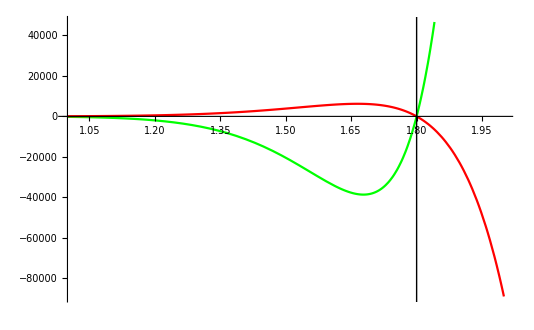

```mathematica
Plot[{PetrovDet14Re[r, angle, spin], PetrovDet14Im[r, angle, spin]}, {r, 1,2}, PlotRange -> Automatic,Epilog->{InfiniteLine[{1+Sqrt[1-spin^2],0},{0,1}], InfiniteLine[{1-Sqrt[1-spin^2],0},{0,1}]}, Evaluated -> True, Axes -> True, PlotStyle -> {Green, Red, Blue, Yellow}]
```

## Energy loss from single or binary black holes

First we calculate the angular velocity of the event horizon.

```mathematica
-gtϕ/gϕϕ;
% /. {r[] -> 1 + √(1-J^2)};
% //Perturbations //Simplify;
Subscript[Ω, CS]= %
```

(J (1024+256 J^2+128 J^4+80 J^6+56 J^8+42 J^10+33 J^12))/4096-1/533970262425600 a^2 J (211263904051200+58750634342400 J^2+57547223784960 J^4+62102514387200 J^6+65296315118280 J^8+66974469229300 J^10+67579939563817 J^12)

```mathematica
Subscript[Ω, GR] = (J(1+√(1-J^2)))/(4-2 J^2+4 √(1-J^2)) //Perturbations //Simplify;
```

The dCS correction is then simply

```mathematica
δΩ = 1/a^2(Subscript[Ω, CS] - Subscript[Ω, GR]) //Simplify
```

-1/533970262425600 J (211263904051200+58750634342400 J^2+57547223784960 J^4+62102514387200 J^6+65296315118280 J^8+66974469229300 J^10+67579939563817 J^12)

Solution to the Penrose process in GR. Here (M, χ) are the initial mass and spin of the black hole.

```mathematica
PenroseGR[J_] := M ((1+√(1-0^2))/(1+ √(1-J^2)))^(1/2)
```

```mathematica
PenroseGR'[J] - (PenroseGR[J] Subscript[Ω, GR])/(1-2  J Subscript[Ω, GR])  //Perturbations
```

0

To obtain the dCS correction to the Penrose process we expand in the coupling parameter around the GR solution. We want a solution of the form M(χ) = M^(0)(χ) + α^2 M^(2)(χ), with M^(0) the GR solution,
and with the initial conditions M^(0)(χ_0) = M_0 and M^(2)(χ_0) = 0.

The differential equation for M^(2) then becomes

```mathematica
M2[x_] :=-((709 x^2)/(3584 M^3))-(8747 x^4)/(86016 M^3)-(5784463 x^6)/(75694080 M^3)-(1534220603 x^8)/(23616552960 M^3)-(9347435299 x^10)/(160306298880 M^3)-(38736160452331 x^12)/(719454669373440 M^3)-(55277078724807509 x^14)/(1093571097447628800 M^3)
```

```mathematica
M2'[J] -Subscript[Ω, GR]/(1-2  J Subscript[Ω, GR]) M2[J] - δΩ/PenroseGR[J]^3 1/(1-2J Subscript[Ω, GR])^2 //Perturbations //Simplify
```

0

This was checked and is correct.

This equation we now want to solve perturbatively in the spin parameter.

```mathematica
f1[J_] := -(J(1024+768 J^2+640 J^4+560 J^6+504 J^8+462 J^10+429 J^12))/4096
f2[J_] := 1/(4*136696387180953600  M^3)J(216334237748428800+195369548159385600 J^2+216526660636016640 J^4+246397219120640000 J^6+278638424040464000 J^8+311202354429620880 J^10+343296416765000013 J^12)
```

```mathematica
AsymptoticDSolveValue[{y'[x] + f1[x]y[x] + f2[x] == 0, y[0] == 0}, y[x], {x, 0, 14}]
```

-(709 x^2)/(3584 M^3)-(8747 x^4)/(86016 M^3)-(5784463 x^6)/(75694080 M^3)-(1534220603 x^8)/(23616552960 M^3)-(9347435299 x^10)/(160306298880 M^3)-(38736160452331 x^12)/(719454669373440 M^3)-(55277078724807509 x^14)/(1093571097447628800 M^3)

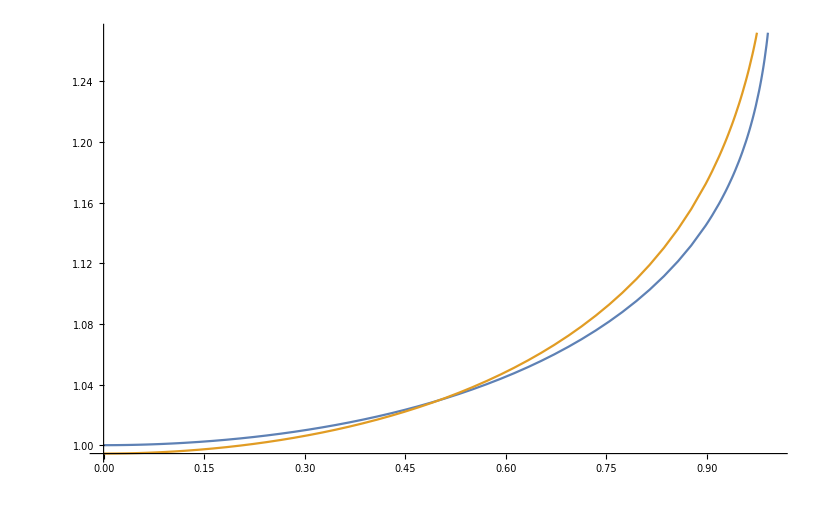

```mathematica
Plot[{0.1*M2[x] * M^3 + PenroseGR[x]/M,1.0295429255776376((1+√(1-0.5^2))/(1+ √(1-x^2)))^(1/2)}, {x, 0, 1}]
```

In dCS the Penrose process is, just like in GR, a dS = 0 process but with a modified entropy. As dS is a combination of the Bekenstein term and a quadratic curvature correction, dA != 0 in this process.

```mathematica
0.1*M2[0.5] * M^3 + PenroseGR[0.5]/M
```

1.02954

```mathematica
BlackHoleSurface[M_, J_] := 4π a^2 J^2/M^2 1/114536621290291200(-233930822501376000-106794320662149120 J^2-51209215690913280 J^4-20812922851818240 J^6-2285384692207760 J^8+9757887452198860 J^10+17922709822092007 J^12)  +   4π M^2 ((1+ √(1-J^2))^2 + J^2)
```

```mathematica
BlackHoleEntropy[M_, J_] := π M^2 ((1+ √(1-J^2))^2 + J^2) +  a^2 J^2/M^2 1/266985131212800(422527808102400+270014538393600 J^2+213478621923840 J^4+184652303046400 J^6+167032596534320 J^8+154921376364060 J^10+145899606713247 J^12) π
```

```mathematica
BlackHoleSurface[PenroseGR[J]+ a^2 M2[J], J] //Perturbations
```

-1/(22162658918400 M^2)a^2 J^2 (321358554316800+91975034511360 J^2+47356193364480 J^4+28979576820480 J^6+19306671567040 J^8+13528643088480 J^10+9794915782793 J^12) π+16 M^2 π

```mathematica
BlackHoleEntropy[PenroseGR[J]+ a^2 M2[J], J] //Perturbations
```

4 M^2 π

```mathematica
ΔM =(2 π(1+m^2)(1+√(1-J^2))+(1+1/m^2)(1/266985131212800 a^2 J^2 (422527808102400+270014538393600 J^2+213478621923840 J^4+184652303046400 J^6+167032596534320 J^8+154921376364060 J^10+145899606713247 J^12) π))^(1/2) //Perturbations //CollectJ //Simplify
```